heart dingbat = tested with new guild nomenclature
club = uses EcoEqns/EvoEqns

```mathematica
PacletDirectoryAdd["~/github/EcoEvo"]
```

{/Users/klaus/github/EcoEvo}

```mathematica
<<EcoEvo`
```

```mathematica
HighlightChanges[False]
```

```mathematica
SetOptions[EvaluationNotebook[],DockedCells->{Cell[BoxData@ToBoxes@Button["<<EcoEvo`",<<EcoEvo`],"DockedCell"]}]
```

## Models

### ricker (DiscreteTime, 1 Unstructured Pop)

```mathematica
ricker={ModelType->"DiscreteTime",Pop[1]->{Variable->n,Equation:>n[t]*E^(rr(1-n[t]))}};
```

### lvc “lotka-volterra competition” (ContinousTime, 2 Unstructured Pops)

```mathematica
Clear[α12,α21,k1,k2]
```

```mathematica
lvc={Pop[1]->{Name->"n1",Variable->n1,Equation:>dn1},Pop[2]->{Name->"n2",Variable->n2,Equation:>dn2}};

dn1:=n1[t]*(1-(n1[t]+α12 n2[t])/k1);
dn2:=n2[t]*(1-(n2[t]+α21 n1[t])/k2);
```

```mathematica
α12=0.5;
α21=0.5;
k1=1;
k2=1.2;
```

### rm “rosenzweig-macarthur” (ContinuousTime, 2 Unstructured Pops)

```mathematica
rm={Pop[1]->{Variable->n,Equation:>dN,Color->Green},Pop[2]->{Variable->p,Equation:>dP,Color->Red},Assumptions->{an>0,apred>0,h>0,mp>0,nk>0,apred>mp}};
dN:=n[t]*(1-n[t]/nk)-an p[t]n[t]/(n[t]+h);
dP:=p[t]*(apred n[t]/(n[t]+h)-mp);
```

```mathematica
an=1;
apred=2;
h=1;
mp=1;
nk=2;
```

### tt “tritrophic” (ContinuousTime, 3 Unstructured Pops)

```mathematica
tt={Pop[1]->{Variable->x,Equation:>f1},Pop[2]->{Variable->y,Equation:>f2},Pop[3]->{Variable->z,Equation:>f3}};
f1:=x[t]*(1-x[t])-A1*x[t]/(1+B1*x[t])*y[t];
f2:=A1*x[t]/(1+B1*x[t])*y[t]-A2*y[t]/(1+B2*y[t])*z[t]-D1*y[t];
f3:=A2*y[t]/(1+B2*y[t])*z[t]-D2*z[t];
```

```mathematica
A1=5.0;
A2=0.1;
B2=2.0;
D1=0.4;
D2=0.01;
```

### fl “fluctuating light” (ContinuousTimePeriodic, 2 Unstructured Pops & 1 Aux)

```mathematica
fl={
Pop[1]->{Variable->b1,Equation:>db1},
Pop[2]->{Variable->b2,Equation:>db2},
Aux[1]->{Variable->R,Equation:>dRfl},Period->T};

db1:=b1[t]*(μ1*R[t]/(R[t]+K1)-death);
db2:=b2[t]*(μ2*R[t]/(R[t]+K2)-death);
dRfl:=(Rin-R[t])-μ1*R[t]/(R[t]+K1)*b1[t]-μ2*R[t]/(R[t]+K2)*b2[t];
μ1:=Piecewise[{{1,Mod[t,T]<ϕ T},{0,Mod[t,T]>=ϕ T}}];
μ2:=Piecewise[{{2,Mod[t,T]<ϕ T},{0,Mod[t,T]>=ϕ T}}];
K1=1;K2=4;
ϕ=0.6;
T=365;
Rin=20;
death=0.2;
```

### twop “two patches” (ContinuousTime, 1 Structured Pop)

```mathematica
twop = {Pop[1]-> {Name->"pop", Component[1]->{Variable->p1,Equation:>dp1}, Component[2]->{Variable->p2,Equation:>dp2}}};

dp1 := rp1*p1[t]*(1 - p1[t]) + disp*(p2[t] - p1[t]);
dp2 := rp2*p2[t]*(1 - p2[t]) + disp*(p1[t] - p2[t]);

rp1 = 1;
rp2 = 2;
disp = 0.1;
```

### threep “three patches” (ContinuousTime, 1 Structured Pop)

```mathematica
threep={Pop[1]->{Name->"pop",Component[1]->{Variable->p1,Equation:>dp1′},Component[2]->{Variable->p2,Equation:>dp2′},Component[3]->{Variable->p3,Equation:>dp3′}}};
```

```mathematica
dp1′:=rp1*p1[t]*(1-p1[t])+disp*(p2[t]/2+p3[t]/2-p1[t]);
dp2′:=rp2*p2[t]*(1-p2[t])+disp*(p1[t]/2+p3[t]/2-p2[t]);
dp3′:=rp3*p3[t]*(1-p3[t])+disp*(p1[t]/2+p2[t]/2-p3[t]);
```

```mathematica
rp1=1;
rp2=2;
rp3=-2;
disp=0.1;
```

### opt “optimization” (ContinuousTime, 1 Unstructured Pop)

```mathematica
opt={Guild[1]->{Variable->n,Equation->dndt,Trait[1]->{Variable->x,Range->Interval[{-1,1}]}}};
```

```mathematica
dndt[i_]:=fit[Subscript[x, i]]Subscript[n, i][t];
```

```mathematica
fit[x_]:=E^(-(x-0.5)^2/0.125)+1.2E^(-(x+0.5)^2/0.125)-0.13533529846659245;
fit[x_]:=1-x^2;
```

### dl “juvenile-adult” (DiscreteTime, 1 Structured Pop)

```mathematica
dl={ModelType->"DiscreteTime",Pop[1]->{Name->"pop",Component[1]->{Variable->j,Equation:>dj},Component[2]->{Variable->a,Equation:>da}}};
```

```mathematica
dj:=rj*j[t]+ra*a[t];
da:=mat*j[t];
```

```mathematica
rj=0.5;
mat=0.2;
ra=5;
```

### lv “AD lotka-volterra competition” (ContinousTime, 1 Unstructured Guild)

```mathematica
(*lv={Guild[1]->{Variable->n,Equation->(r*(1-Sum[a[Subscript[x, #],Subscript[x, j]]*Subscript[n, j][t],{j,Nsp[1]}]/k[Subscript[x, #]])*Subscript[n, #][t]&),Trait[1]->{Variable->x,Range->Interval[{-1,1}]}}};*)
```

```mathematica
lv={Guild[n]->{Variable->n,Equation->g,Trait[1]->{Variable->x,Range->Interval[{-1,1}]}}};
```

```mathematica
g[i_]:=r*(1-Sum[a[Subscript[x, i],Subscript[x, j]]*Subscript[n, j][t],{j,Nsp[n]}]/k[Subscript[x, i]])*Subscript[n, i][t];
a[xi_,xj_]:=E^(-1/2*(xi-xj)^2/σa^2);
k[x_]:=(k0-λ*(x-x0)^2);
```

```mathematica
σa=1/2;
k0=1;
x0=0;
λ=1;
r=1;
```

### newlv “new AD lotka-volterra competition” (ContinousTime, 1 Unstructured Guild)

```mathematica
newlv={Guild[1]->{Variable->n,Equation->gnew,Trait[1]->{Variable->x,Range->Interval[{-1,1}]}}};
```

```mathematica
gnew[i_]:=(k[Subscript[x, i]]-Sum[a[Subscript[x, i],Subscript[x, j]]*Subscript[n, j][t],{j,Nsp[1]}])*Subscript[n, i][t];
a[xi_,xj_]:=E^(-1/2*(xi-xj)^2/σa^2);
k[x_]:=(k0-λ*(x-x0)^2);
```

```mathematica
σa=1/2;
k0=1;
x0=0;
λ=1;
r=1;
```

### si “susceptible, infected” (ContinousTime, 1 Structured Guild)

```mathematica
si={Guild[1]->{Component[1]->{Variable->s,Equation->ds},Component[2]->{Variable->i,Equation->di},Trait[1]->{Variable->B,Range->Interval[{0,1}]}}};
```

```mathematica
(* tradeoff *)

bmin=0.3;
bmax=0.35;
Bmin=0;
Bmax=0.05;
α=1;

bb[B_]:=bmin+(bmax-bmin)*((B-Bmin)/(Bmax-Bmin))^α;
```

```mathematica
(* setup equations *)

ds[sp_]:=bb[Subscript[B, sp]]*(Subscript[s, sp][t]+f*Subscript[i, sp][t])*(1-cc*Sum[Subscript[s, sp′][t]+Subscript[i, sp′][t],{sp′,Nsp[1]}])-m*Subscript[s, sp][t]-nn*Subscript[s, sp][t]-Sum[Subscript[B, sp]*Subscript[s, sp][t]*Subscript[i, sp′][t],{sp′,Nsp[1]}];

di[sp_]:=Sum[Subscript[B, sp]*Subscript[s, sp][t]*Subscript[i, sp′][t],{sp′,Nsp[1]}]-nn*Subscript[i, sp][t]-v*Subscript[i, sp][t]-θ*m*Subscript[i, sp][t];
```

```mathematica
(* parameters *)

f=0.75;
cc=0.05;
m=0.02;
nn=0.05;
v=0.05;
θ=9;
```

### ch “chemostat” (ContinousTime, 1 Structured Guild & 1 Aux)

```mathematica
ch={Aux[1]->{Variable->R,Equation:>dR},Guild[1]->{Variable->n,Equation->dnn,Trait[1]->{Variable->mu,Range-> Interval[{0,1}]}}};
```

```mathematica
dnn[sp_]:=(Subscript[mu, sp]*R[t]/(R[t]+K[Subscript[mu, sp]])-m)*Subscript[n, sp][t];
dR:=aa*(rin-R[t])-Sum[Subscript[mu, sp′]*R[t]/(R[t]+K[Subscript[mu, sp′]])*Subscript[n, sp′][t],{sp′,Nsp[1]}];

K[μ_]:=c1*μ^c2;
```

```mathematica
aa=1;
m=0.02;
c1=1;
c2=2;
rin=1;
```

### pp “predator-prey” (ContinuousTime, 2 Unstructured Guilds)

```mathematica
pp={
Guild[prey]->
{Variable->n,Equation->dn,Trait[1]->{Variable->xn,Range->Interval[{-1,1}]}},Guild[pred]->{Variable->p,Equation->dp,Trait[1]->{Variable->xp,Range->Interval[{-1,1}]}}
};
```

```mathematica
dn[sp_]:=(r*(1-Sum[ac[Subscript[xn, sp],Subscript[xn, sp′]]*Subscript[n, sp′][t],{sp′,Nsp[prey]}]/(k0-λ*(Subscript[xn, sp]-x0)^2))-Sum[ap[Subscript[xn, sp],Subscript[xp, sp′]]*Subscript[p, sp′][t],{sp′,Nsp[pred]}])*Subscript[n, sp][t];
dp[sp_]:=(Sum[ap[Subscript[xn, sp′],Subscript[xp, sp]]*Subscript[n, sp′][t],{sp′,Nsp[prey]}]-m)*Subscript[p, sp][t];
ac[xi_,xj_]:=E^(-1/2*(xi-xj)^2/σc^2);
ap[xi_,xj_]:=E^(-1/2*(xi-xj)^2/σp^2);
```

```mathematica
σc=1/2;
σp=1;
k0=1;
x0=0;
λ=1;
r=1;
m=0.1;
```

### lv2 “2D AD lotka-volterra competition” (ContinousTime, 1 Unstructured Guild, 2 Traits)

```mathematica
lv2={Guild[1]->{Variable->n,Equation->g2,Trait[1]->{Variable->x,Range->Interval[{-1,1}]},Trait[2]->{Variable->y,Range->Interval[{-1,1}]}}};
```

```mathematica
g2[i_]:=((k0-λ*((Subscript[x, i]-x0)^2+(Subscript[y, i]-y0)^2))-Sum[a[Subscript[x, i],Subscript[x, j],Subscript[y, i],Subscript[y, j]]*Subscript[n, j][t],{j,Nsp[1]}])*Subscript[n, i][t];
a[xi_,xj_,yi_,yj_]:=E^(-1/2*((xi-xj)^2+(yi-yj)^2)/σa^2);
```

```mathematica
σa=1/2;
k0=1;
x0=0;
y0=0;
λ=1;
r=1;
```

### droop “droop” (ContinuousTime, 1 Intensive-Structured Guild)

```mathematica
droop={
Aux[1]->{Variable->r1,Equation:>dr1},
Guild[1]->{
Component[1]->{Variable->b,Equation-> db},Component[2]->{Variable->q,Equation->dq,Range->Interval[{qmin,∞}],Type->"Intensive"},
Trait[1]->{Variable->a1,Range->Interval[{0,1}]}
}};
```

```mathematica
db[sp_]:=μ*(1-qmin/Subscript[q, sp][t])*Subscript[b, sp][t]-m*Subscript[b, sp][t];
dq[sp_]:=Subscript[a1, sp]*v′*r1[t]/(r1[t]+k1)-μ*(1-qmin/Subscript[q, sp][t])*Subscript[q, sp][t];
dr1:=aa*(rin1-r1[t])-Sum[Subscript[a1, sp′]*v′*r1[t]/(r1[t]+k1)*Subscript[b, sp′][t],{sp′,Nsp[1]}];
```

```mathematica
aa=1;
rin1=20;
rin2=10;

μ=2;
k1=1;
qmin=1;
v′=1;
m=0.02;
```

### dlv “discrete-time AD lotka-volterra competition” (DiscreteTime, 1 Unstructured Guild)

```mathematica
dlv={ModelType->"DiscreteTime",Guild[1]->{Variable->n,Equation->dg,Trait[1]->{Variable->x,Range->Interval[{-0.999999,0.999999}]}}};
```

```mathematica
dg[i_]:=Subscript[n, i][t]*E^(r*(1-Sum[a[Subscript[x, i],Subscript[x, j]]*Subscript[n, j][t],{j,Nsp[1]}]/k[Subscript[x, i]]));
a[xi_,xj_]:=E^(-1/2*(xi-xj)^2/σa^2);
k[x_]:=(k0-λ*(x-x0)^2);
```

### jon “norberg 2001” (ContinuousTimePeriodic, 1 Unstructured Guild)

```mathematica
jon={
ModelType->"ContinuousTime",Period->T,
Guild[1]->{Variable->c,Equation->dc,Trait[1]->{Variable->x,Range-> Interval[{0,30}]}}
};
dc[i_]:=(ρ E^(-(Subscript[x, i]-e[t])^2/σ^2)(1-Sum[Subscript[c, j][t],{j,Nsp[1]}])-d)*Subscript[c, i][t];
e[t]:=χ+δ Sin[ω t];
```

```mathematica
χ=15;
δ=6;
T=365;
ω=2π/T;
σ=2.5;
ρ=3.0;
d=0.1;
```

### mc “metacommunity” (ContinuousTimePeriodic, 1 Structured Guild)

```mathematica
mc={ModelType->"ContinuousTime",Period->1,
Guild[1]-> {Component[1]->{Variable->p1,Equation:>mcdp1}, Component[2]->{Variable->p2,Equation:>mcdp2},Trait[1]->{Variable->dd,Range->Interval[{0,∞}]}}};

mcdp1[i_]:=(rbg+Sin[2π*t])*Subscript[p1, i][t]-Subscript[p1, i][t]*Sum[Subscript[p1, j][t],{j,Nsp[1]}]+Subscript[dd, i]*(Subscript[p2, i][t]-Subscript[p1, i][t]);
mcdp2[i_]:=(rbg-Sin[2π*t])*Subscript[p2, i][t]-Subscript[p2, i][t]*Sum[Subscript[p2, j][t],{j,Nsp[1]}]+Subscript[dd, i]*(Subscript[p1, i][t]-Subscript[p2, i][t]);
```

```mathematica
rbg=0.1;
```

### pulsed “pulsed” (ContinuousTimePeriodic, 1 Intensive-Structured Guild, WhenEvents)

```mathematica
pulsed={ModelType->"ContinuousTime",Period->τ,
Aux[1]->{Variable->r1,Equation:>dr1},
Guild[1]->{
Component[1]->{Variable->b,Equation-> db},Component[2]->{Variable->q,Equation->dq,Range->Interval[{qmin,∞}],Type->"Intensive"},
Trait[1]->{Variable->a1,Range->Interval[{0,1}]}
},
WhenEvents->{WhenEvent[Mod[t,τ],r1[t]->r1[t]+10]}
};
```

### dormant “dormant” (ContinuousTimePeriodic, 1 Intensive- & Extensive-Structured Guild, WhenEvents)

```mathematica
dormant={ModelType->"ContinuousTime",Period->τ,
Aux[1]->{Variable->r1,Equation:>dr1},
Guild[1]->{
Component[1]->{Variable->b,Equation-> db‵},Component[2]->{Variable->bd,Equation->dbd},Component[3]->{Variable->q,Equation->dq,Range->Interval[{qmin,∞}],Type->"Intensive"},
Trait[1]->{Variable->a1,Range->Interval[{0,1}]}
},
WhenEvents->{WhenEvent[Mod[t,τ],r1[t]->r1[t]+10]}
};
```

```mathematica
db‵[sp_]:=μ*(1-qmin/Subscript[q, sp][t])*Subscript[b, sp][t]-m*Subscript[b, sp][t]+xx(Subscript[bd, sp][t]-Subscript[b, sp][t]);
dbd[sp_]:=-md*Subscript[b, sp][t]+xx(Subscript[b, sp][t]-Subscript[bd, sp][t]);
dq[sp_]:=Subscript[a1, sp]*v′*r1[t]/(r1[t]+k1)-μ*(1-qmin/Subscript[q, sp][t])*Subscript[q, sp][t];
dr1:=aa*(rin1-r1[t])-Sum[Subscript[a1, sp′]*v′*r1[t]/(r1[t]+k1)*Subscript[b, sp′][t],{sp′,Nsp[1]}];
```

```mathematica
md=0.002;
xx=0.1;
```

### dfltwop “discrete fluctuating twopatch” (DiscreteTimePeriodic, 1 Structured Guild)

```mathematica
dfltwop = {ModelType->"DiscreteTime",Period->2,Guild[1]-> {Component[1]->{Variable->p1,Equation->dp1fl}, Component[2]->{Variable->p2,Equation->dp2fl},Trait[1]->{Variable->dd,Range->Interval[{0,1}]}}};

dp1fl[i_]:=Subscript[p1, i][t]+If[Mod[t,2]==0,rp1a,rp1b]*Subscript[p1, i][t]-Subscript[p1, i][t]*Sum[Subscript[p1, j][t],{j,Nsp[1]}]+Subscript[dd, i]*(Subscript[p2, i][t]-Subscript[p1, i][t]);
dp2fl[i_]:= Subscript[p2, i][t]+If[Mod[t,2]==0,rp2a,rp2b]*Subscript[p2, i][t]-Subscript[p2, i][t]*Sum[Subscript[p2, j][t],{j,Nsp[1]}]+Subscript[dd, i]*(Subscript[p1, i][t]-Subscript[p2, i][t]);

rp1a=0.5;
rp2a=1;
rp1b=1;
rp2b=0.5;
```

### t82 "tilman 82"

```mathematica
t82={Aux[1]->{Variable->R1,Equation:>dR1},Aux[2]->{Variable->R2,Equation:>dR2},Pop[1]->{Variable->n,Equation:>dnt82}};
```

```mathematica
dR1:=(R1in-R1[t])-qq1 Min[aa1 R1[t],aa2 R2[t]]n[t];
dR2:=(R2in-R2[t])-qq2 Min[aa1 R1[t],aa2 R2[t]]n[t];
dnt82:=(Min[aa1 R1[t],aa2 R2[t]]-mn)n[t];
```

```mathematica
qq1=qq2=1;
aa1=aa2=1;
mn=0.1;
```

## General Utilities

### VarSort

```mathematica
VarSort[{a->1,c->2,b->3},{a,b,c}]
```

{a→1,b→3,c→2}

```mathematica
VarSort[{{a->1,c->2,b->3},{a->1,c->2,b->3}},{a,b,c}]
```

{{a→1,b→3,c→2},{a→1,b→3,c→2}}

### ColorData["EEReds"] / ColorData["EEGreens”] / ColorData["EEBlues"]

```mathematica
ColorData["EEReds"]
ColorData["EEGreens"]
ColorData["EEBlues"]
```

ColorDataFunction[…]

ColorDataFunction[…]

ColorDataFunction[…]

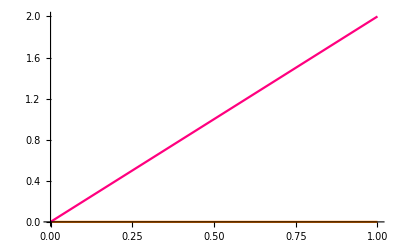

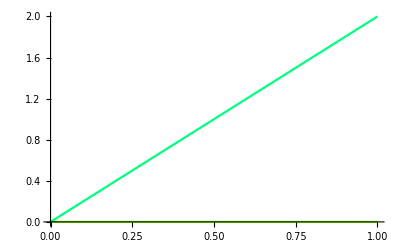

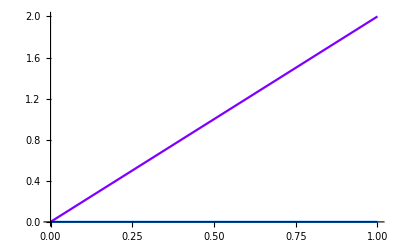

```mathematica
Plot[Evaluate[Table[i x,{i,0,2,2}]],{x,0,1},PlotStyle->Table[ColorData["EEReds"][j/3],{j,2}]]
Plot[Evaluate[Table[i x,{i,0,2,2}]],{x,0,1},PlotStyle->Table[ColorData["EEGreens"][j/3],{j,2}]]
Plot[Evaluate[Table[i x,{i,0,2,2}]],{x,0,1},PlotStyle->Table[ColorData["EEBlues"][j/3],{j,2}]]
```

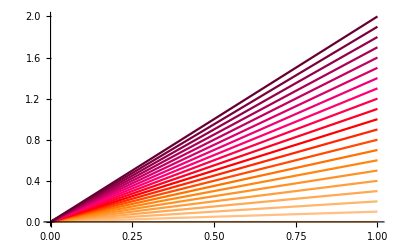

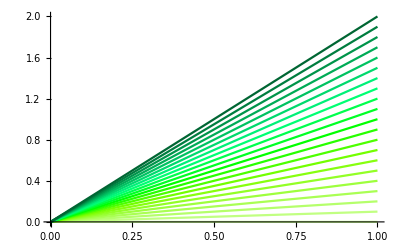

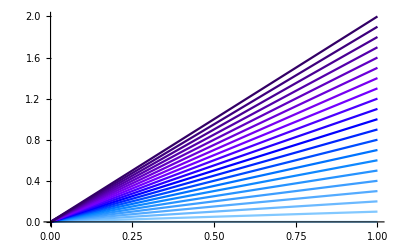

```mathematica
Plot[Evaluate[Table[i x,{i,0,2,0.1}]],{x,0,1},PlotStyle->Table[ColorData["EEReds"][(j-1)/20],{j,21}]]
Plot[Evaluate[Table[i x,{i,0,2,0.1}]],{x,0,1},PlotStyle->Table[ColorData["EEGreens"][(j-1)/20],{j,21}]]
Plot[Evaluate[Table[i x,{i,0,2,0.1}]],{x,0,1},PlotStyle->Table[ColorData["EEBlues"][(j-1)/20],{j,21}]]
```

```mathematica
{ColorData["EEReds"][0],ColorData["EEGreens"][0],ColorData["EEBlues"][0]}
{ColorData["EEReds"][1],ColorData["EEGreens"][1],ColorData["EEBlues"][1]}
```

{RGBColor[1., 0.7992, 0.6],RGBColor[0.8, 1., 0.6],RGBColor[0.6, 0.8392000000000002, 1.]}

{RGBColor[0.4, 0., 0.19919999999999974],RGBColor[0., 0.4, 0.20079999999999992],RGBColor[0.2, 0., 0.4]}

### RuleList

```mathematica
?RuleList
```

RuleList[var, n, val] makes a list of n rules where var takes on value val.
RuleList[var, n, {min, max}] makes a list of n rules where var ranges from min to max.
RuleList[vars, n, vals] makes a list of rules between corresponding elements of the lists vars and vals.
RuleList[var, ns, val] makes a list of rules with dimensions ns where var takes on value val.
RuleList[{var_1, …, var_nv}, {n_1, … , n_nv}, {{min_1 , max_1 }, … , {min_nv , max_nv }}] makes a list of rules with dimensions ns where var_i ranges from min_i  to max_i .

```mathematica
(* ex 1 *)
RuleList[n,10,1]
```

{n_1→1,n_2→1,n_3→1,n_4→1,n_5→1,n_6→1,n_7→1,n_8→1,n_9→1,n_10→1}

```mathematica
(* ex 1 *)
RuleList[n,10,RandomReal[{0,1}]]
```

{n_1→0.742477,n_2→0.0784329,n_3→0.420984,n_4→0.335291,n_5→0.559518,n_6→0.417298,n_7→0.567687,n_8→0.0307024,n_9→0.162852,n_10→0.502842}

```mathematica
(* ex 1 *)
nsp=10;
RuleList[n,nsp,1]
```

{n_1→1,n_2→1,n_3→1,n_4→1,n_5→1,n_6→1,n_7→1,n_8→1,n_9→1,n_10→1}

```mathematica
(* ex 2 *)
RuleList[x,10,{0,1}]
```

{x_1→0,x_2→1/9,x_3→2/9,x_4→1/3,x_5→4/9,x_6→5/9,x_7→2/3,x_8→7/9,x_9→8/9,x_10→1}

```mathematica
(* ex 3 *)
RuleList[{x,y},10,{1,2}]
```

{x_1→1,y_1→2,x_2→1,y_2→2,x_3→1,y_3→2,x_4→1,y_4→2,x_5→1,y_5→2,x_6→1,y_6→2,x_7→1,y_7→2,x_8→1,y_8→2,x_9→1,y_9→2,x_10→1,y_10→2}

```mathematica
(* ex 4 *)
RuleList[n,{5,3},1]
```

{n_1→1,n_2→1,n_3→1,n_4→1,n_5→1,n_6→1,n_7→1,n_8→1,n_9→1,n_10→1,n_11→1,n_12→1,n_13→1,n_14→1,n_15→1}

```mathematica
(* ex 4 *)
nsp1=5;nsp2=3;
RuleList[n,{nsp1,nsp2},1]
```

{n_1→1,n_2→1,n_3→1,n_4→1,n_5→1,n_6→1,n_7→1,n_8→1,n_9→1,n_10→1,n_11→1,n_12→1,n_13→1,n_14→1,n_15→1}

```mathematica
(* ex 5 *)
RuleList[{x,y},{5,3},{{0,1},{-1,0}}]
```

{x_1→0,y_1→-1,x_2→0,y_2→-1/2,x_3→0,y_3→0,x_4→1/4,y_4→-1,x_5→1/4,y_5→-1/2,x_6→1/4,y_6→0,x_7→1/2,y_7→-1,x_8→1/2,y_8→-1/2,x_9→1/2,y_9→0,x_10→3/4,y_10→-1,x_11→3/4,y_11→-1/2,x_12→3/4,y_12→0,x_13→1,y_13→-1,x_14→1,y_14→-1/2,x_15→1,y_15→0}

```mathematica
RuleList[{x,y},{5,3},{7,{-1,0}}]
```

{x_1→7,y_1→-1,x_2→7,y_2→-1/2,x_3→7,y_3→0,x_4→7,y_4→-1,x_5→7,y_5→-1/2,x_6→7,y_6→0,x_7→7,y_7→-1,x_8→7,y_8→-1/2,x_9→7,y_9→0,x_10→7,y_10→-1,x_11→7,y_11→-1/2,x_12→7,y_12→0,x_13→7,y_13→-1,x_14→7,y_14→-1/2,x_15→7,y_15→0}

### RuleListAdd

```mathematica
RuleListAdd[{x->1},{x->2}]
```

{x→3}

```mathematica
RuleListAdd[{x->1},{y->4}]
```

{x→1,y→4}

```mathematica
RuleListAdd[{x->1},{x->2,y->4}]
```

{x→3,y→4}

### ClearCache

```mathematica
?ClearCache
```

ClearCache[f, g, ...] removes memoized DownValues of f, g, etc.

```mathematica
fff[1]=1
```

1

```mathematica
?fff
```

Global`fff

fff[1]=1

```mathematica
ClearCache[fff]
```

```mathematica
fff[1]
```

fff[1]

### IFQ / Mean / Var / Cov / FindMaxima / FindMinima / FindExtrema / FindPeriod

```mathematica
SetModel[jon]
tmax=5*365;
sol=EcoSim[{Subscript[x, 1]->12},{Subscript[c, 1]->1},tmax]
```

{c_1→InterpolatingFunction[…]}

#### IFFQ

```mathematica
?IFFQ
```

IFFQ[x] is True if x is a InterpolatingFunction function.

```mathematica
IFFQ[sol]
```

True

```mathematica
IFFQ[Subscript[c, 1]/.sol]
```

False

```mathematica
IFFQ[Subscript[c, 1][t]/.sol]
```

True

```mathematica
IFFQ[(Subscript[c, 1][t]^2)/.sol]
```

True

#### Avg

```mathematica
?Avg
```

Avg[f, var] gives the average of the function f, which contains an InterpolatingFunction, with respect to var (default var=t).
Avg[f, {var, varmin, varmax}] gives the average of the function f with respect to var, ranging from varmin to varmax.

```mathematica
Avg[Sin[t],{t,0,2π}]
```

0

```mathematica
Avg[Subscript[c, 1][t]/.sol]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1290.3}. NIntegrate obtained 892.589 and 0.00100548 for the integral and error estimates.

0.48909

```mathematica
IFFQ[(Subscript[c, 1][t]^2)/.sol]
```

True

```mathematica
Avg[(Subscript[c, 1][t]^2)/.sol]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {559.591}. NIntegrate obtained 795.833 and 0.00311232 for the integral and error estimates.

0.436073

```mathematica
Avg[Subscript[c, 1][t]/.sol,{t,4*365,5*365}]
```

0.488955

```mathematica
Avg[Subscript[c, 1][t]/.sol,t]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1290.3}. NIntegrate obtained 892.589 and 0.00100548 for the integral and error estimates.

0.48909

```mathematica
Avg[Subscript[c, 1][x]/.sol,x]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1290.3}. NIntegrate obtained 892.589 and 0.00100548 for the integral and error estimates.

0.48909

#### Var

```mathematica
?Var
```

Var[f, var] gives the variance of the function f, which contains an InterpolatingFunction, with respect to var (default var=t).
Var[f, {var, varmin, varmax}] gives the variance of the function f with respect to var, ranging from varmin to varmax.

```mathematica
Var[Sin[t],{t,0,2π}]
```

1/(4 π)

```mathematica
Var[Subscript[c, 1][t]/.sol]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1290.3}. NIntegrate obtained 892.589 and 0.00100548 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {559.591}. NIntegrate obtained 359.277 and 0.00227461 for the integral and error estimates.

0.000107871

```mathematica
Var[Subscript[c, 1][t]/.sol,{t,4*365,5*365}]
```

0.000539098

```mathematica
Var[Subscript[c, 1][t]/.FinalSlice[sol,365]]
```

0.000539098

#### Cov

```mathematica
?Cov
```

Cov[f_1, f_2, var] gives the covariance of f_1 and f_2, at least one of which contains an InterpolatingFunction, with respect to var (default var=t).
Cov[f_1, f_2, {var, varmin, varmax}] gives the covariance of the functions f_1 and f_2 with respect to var, ranging from varmin to varmax.

```mathematica
Cov[Sin[t],Cos[t],{t,0,2π}]
```

0

```mathematica
Cov[Sin[t],Sin[t+π],{t,0,2π}]
```

-1/(4 π)

```mathematica
Cov[Subscript[c, 1][t],Sin[(2 π t)/365]]/.sol
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1824.899259752291343639196696813087328337132930755615234375}. NIntegrate obtained -3.2685×10^-13 and 1.03729×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1290.3}. NIntegrate obtained 892.589 and 0.00100548 for the integral and error estimates.

-0.000152438

```mathematica
Cov[Subscript[c, 1][t],Subscript[c, 1][t]]/.sol
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1290.3}. NIntegrate obtained 892.589 and 0.00100548 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {559.591}. NIntegrate obtained 359.277 and 0.00227461 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.000107871

```mathematica
Cov[Subscript[c, 1][t]/.sol,Subscript[c, 1][t]/.sol,{t,4*365,5*365}]
```

0.000539098

#### FindMaxima

```mathematica
?FindMaxima
```

FindMaxima[f, {tmin, tmax}] finds local maxima of InterpolatingFunction f between tmin and tmax.
FindMaxima[f] looks over entire domain of f.

```mathematica
FindMaxima[Subscript[c, 1]/.sol,{0,5*365}]
```

{{213.264,0.966661},{334.927,0.96666},{578.264,0.966661},{699.927,0.966661},{943.264,0.966661},{1064.93,0.96666},{1308.26,0.966661},{1429.93,0.966661},{1673.26,0.966661},{1794.93,0.966661}}

#### FindMinima

```mathematica
?FindMinima
```

FindMinima[f, {tmin, tmax}] finds local minima of InterpolatingFunction f between tmin and tmax.
FindMinima[f] looks over entire domain of f.

```mathematica
FindMinima[Subscript[c, 1]/.sol,{0,5*365}]
```

{{166.634,-1.12248×10^-7},{275.364,0.859621},{531.707,-8.63949×10^-7},{640.364,0.859621},{896.709,-9.80947×10^-8},{1005.36,0.859621},{1261.71,-5.1292×10^-7},{1370.36,0.859622},{1626.71,6.90035×10^-9},{1735.36,0.859622}}

#### FindExtrema

```mathematica
?FindExtrema
```

FindExtrema[f, {tmin, tmax}] finds local extrema of InterpolatingFunction f between tmin and tmax.
FindExtrema[f] looks over entire domain of f.

```mathematica
FindExtrema[Subscript[c, 1]/.sol,{0,5*365}]
```

{{166.634,-1.12248×10^-7},{213.264,0.966661},{275.364,0.859621},{334.927,0.96666},{531.707,-8.63949×10^-7},{578.264,0.966661},{640.364,0.859621},{699.927,0.966661},{896.709,-9.80947×10^-8},{943.264,0.966661},{1005.36,0.859621},{1064.93,0.96666},{1261.71,-5.1292×10^-7},{1308.26,0.966661},{1370.36,0.859622},{1429.93,0.966661},{1626.71,6.90035×10^-9},{1673.26,0.966661},{1735.36,0.859622},{1794.93,0.966661}}

#### FindPeriod

```mathematica
FindPeriod[sol,BasePeriod->T]
```

365

### ExtractPlotPoints

```mathematica
?ExtractPlotPoints
```

ExtractPlotPoints[plot] extracts lists of points from lines in plot.

```mathematica
ExtractPlotPoints[Plot[x^2,{x,0,1}]]
```

{{{2.04082×10^-8,4.16493×10^-16},{0.000306718,9.40759×10^-8},{0.000613415,3.76278×10^-7},{0.000920113,8.46608×10^-7},{0.00122681,1.50506×10^-6},{0.00153351,2.35165×10^-6},{0.00184021,3.38636×10^-6},{0.0021469,4.60919×10^-6},{0.0024536,6.02016×10^-6},{0.0027603,7.61925×10^-6},{0.003067,9.40646×10^-6},{0.00337369,0.0000113818},{0.00368039,0.0000135453},{0.00398709,0.0000158969},{0.00429379,0.0000184366},{0.00490718,0.0000240804},{0.00521388,0.0000271845},{0.00552058,0.0000304768},{0.00613397,0.0000376256},{0.00644067,0.0000414822},{0.00674737,0.0000455269},{0.00736076,0.0000541808},{0.00766746,0.0000587899},{0.00797416,0.0000635872},{0.00858755,0.000073746},{0.00981434,0.0000963213},{0.010121,0.000102435},{0.0104277,0.000108738},{0.0110411,0.000121907},{0.0122679,0.000150502},{0.0125746,0.000158121},{0.0128813,0.000165928},{0.0134947,0.000182107},{0.0147215,0.000216723},{0.0150282,0.000225847},{0.0153349,0.000235159},{0.0159483,0.000254348},{0.0171751,0.000294983},{0.0196287,0.000385284},{0.0199612,0.000398448},{0.0202937,0.000411832},{0.0209586,0.000439265},{0.0222886,0.000496783},{0.0249486,0.000622432},{0.0252811,0.000639133},{0.0256136,0.000656055},{0.0262786,0.000690563},{0.0276085,0.000762232},{0.0302685,0.000916183},{0.030601,0.000936421},{0.0309335,0.000956881},{0.0315985,0.000998465},{0.0329285,0.00108428},{0.0355884,0.00126654},{0.0409084,0.00167349},{0.0412188,0.00169899},{0.0415293,0.00172468},{0.0421502,0.00177664},{0.043392,0.00188287},{0.0458757,0.00210458},{0.0508431,0.00258502},{0.0511536,0.00261669},{0.051464,0.00264855},{0.052085,0.00271284},{0.0533268,0.00284375},{0.0558105,0.00311481},{0.0607779,0.00369395},{0.0610823,0.00373104},{0.0613866,0.00376832},{0.0619954,0.00384343},{0.0632129,0.00399586},{0.0656478,0.00430964},{0.0705178,0.00497276},{0.0708221,0.00501578},{0.0711265,0.00505898},{0.0717353,0.00514595},{0.0729527,0.0053221},{0.0753877,0.00568331},{0.0802576,0.00644129},{0.0805878,0.0064944},{0.080918,0.00654772},{0.0815783,0.00665502},{0.082899,0.00687224},{0.0855404,0.00731715},{0.0908231,0.00824883},{0.101388,0.0102796},{0.101697,0.0103422},{0.102005,0.010405},{0.102621,0.0105311},{0.103854,0.0107856},{0.106319,0.0113037},{0.111249,0.0123763},{0.121109,0.0146674},{0.142481,0.0203008},{0.163463,0.0267201},{0.183035,0.0335016},{0.204257,0.0417211},{0.22407,0.0502074},{0.243493,0.0592888},{0.264567,0.0699956},{0.284231,0.0807871},{0.305546,0.0933581},{0.326471,0.106583},{0.345986,0.119706},{0.367151,0.1348},{0.386907,0.149697},{0.408314,0.16672},{0.429331,0.184325},{0.448938,0.201545},{0.470196,0.221084},{0.490044,0.240143},{0.509502,0.259592},{0.530611,0.281548},{0.55031,0.302841},{0.57166,0.326795},{0.59262,0.351199},{0.61217,0.374752},{0.633371,0.401159},{0.653162,0.426621},{0.672563,0.452342},{0.693616,0.481103},{0.713258,0.508737},{0.734551,0.539565},{0.754434,0.56917},{0.773927,0.598963},{0.795071,0.632138},{0.814805,0.663908},{0.83619,0.699215},{0.857186,0.734768},{0.876771,0.768727},{0.898007,0.806417},{0.917833,0.842418},{0.93727,0.878475},{0.958357,0.918448},{0.978034,0.956551},{0.978378,0.957223},{0.978721,0.957894},{0.979407,0.959238},{0.98078,0.961929},{0.983526,0.967323},{0.989017,0.978155},{0.98936,0.978834},{0.989704,0.979513},{0.99039,0.980872},{0.991763,0.983594},{0.994509,0.989047},{0.994852,0.98973},{0.995195,0.990413},{0.995881,0.99178},{0.997254,0.994516},{0.997597,0.995201},{0.997941,0.995886},{0.998627,0.997256},{0.99897,0.997942},{0.999314,0.998628},{0.999657,0.999314},{1.,1.}}}

```mathematica
ExtractPlotPoints[Plot[{x,2x},{x,0,1}]]
```

{{{2.04082×10^-8,2.04082×10^-8},{0.000306718,0.000306718},{0.000613415,0.000613415},{0.00122681,0.00122681},{0.0024536,0.0024536},{0.00490718,0.00490718},{0.00981434,0.00981434},{0.0196287,0.0196287},{0.0409084,0.0409084},{0.0607779,0.0607779},{0.0802576,0.0802576},{0.101388,0.101388},{0.121109,0.121109},{0.142481,0.142481},{0.163463,0.163463},{0.183035,0.183035},{0.204257,0.204257},{0.22407,0.22407},{0.243493,0.243493},{0.264567,0.264567},{0.284231,0.284231},{0.305546,0.305546},{0.326471,0.326471},{0.345986,0.345986},{0.367151,0.367151},{0.386907,0.386907},{0.408314,0.408314},{0.429331,0.429331},{0.448938,0.448938},{0.470196,0.470196},{0.490044,0.490044},{0.509502,0.509502},{0.530611,0.530611},{0.55031,0.55031},{0.57166,0.57166},{0.59262,0.59262},{0.61217,0.61217},{0.633371,0.633371},{0.653162,0.653162},{0.672563,0.672563},{0.693616,0.693616},{0.713258,0.713258},{0.734551,0.734551},{0.754434,0.754434},{0.773927,0.773927},{0.795071,0.795071},{0.814805,0.814805},{0.83619,0.83619},{0.857186,0.857186},{0.876771,0.876771},{0.898007,0.898007},{0.917833,0.917833},{0.93727,0.93727},{0.958357,0.958357},{0.978034,0.978034},{0.978378,0.978378},{0.978721,0.978721},{0.979407,0.979407},{0.98078,0.98078},{0.983526,0.983526},{0.989017,0.989017},{0.98936,0.98936},{0.989704,0.989704},{0.99039,0.99039},{0.991763,0.991763},{0.994509,0.994509},{0.994852,0.994852},{0.995195,0.995195},{0.995881,0.995881},{0.997254,0.997254},{0.997597,0.997597},{0.997941,0.997941},{0.998627,0.998627},{0.99897,0.99897},{0.999314,0.999314},{0.999657,0.999657},{1.,1.}},{{2.04082×10^-8,4.08163×10^-8},{0.000306718,0.000613436},{0.000613415,0.00122683},{0.00122681,0.00245362},{0.0024536,0.0049072},{0.00490718,0.00981436},{0.00981434,0.0196287},{0.0196287,0.0392573},{0.0409084,0.0818167},{0.0607779,0.121556},{0.0802576,0.160515},{0.101388,0.202777},{0.121109,0.242218},{0.142481,0.284962},{0.163463,0.326926},{0.183035,0.366069},{0.204257,0.408515},{0.22407,0.44814},{0.243493,0.486986},{0.264567,0.529134},{0.284231,0.568461},{0.305546,0.611091},{0.326471,0.652941},{0.345986,0.691971},{0.367151,0.734303},{0.386907,0.773815},{0.408314,0.816628},{0.429331,0.858662},{0.448938,0.897876},{0.470196,0.940392},{0.490044,0.980088},{0.509502,1.019},{0.530611,1.06122},{0.55031,1.10062},{0.57166,1.14332},{0.59262,1.18524},{0.61217,1.22434},{0.633371,1.26674},{0.653162,1.30632},{0.672563,1.34513},{0.693616,1.38723},{0.713258,1.42652},{0.734551,1.4691},{0.754434,1.50887},{0.773927,1.54785},{0.795071,1.59014},{0.814805,1.62961},{0.83619,1.67238},{0.857186,1.71437},{0.876771,1.75354},{0.898007,1.79601},{0.917833,1.83567},{0.93727,1.87454},{0.958357,1.91671},{0.978034,1.95607},{0.978378,1.95676},{0.978721,1.95744},{0.979407,1.95881},{0.98078,1.96156},{0.983526,1.96705},{0.989017,1.97803},{0.98936,1.97872},{0.989704,1.97941},{0.99039,1.98078},{0.991763,1.98353},{0.994509,1.98902},{0.994852,1.9897},{0.995195,1.99039},{0.995881,1.99176},{0.997254,1.99451},{0.997597,1.99519},{0.997941,1.99588},{0.998627,1.99725},{0.99897,1.99794},{0.999314,1.99863},{0.999657,1.99931},{1.,2.}}}

### Else

```mathematica
?Else
```

Else is an alias for True.

```mathematica
Else
```

True

### SpFrac

```mathematica
?SpFrac
```

SpFrac[sp, nsp] gives (sp-1)/(nsp-1).

```mathematica
SpFrac[3,15]
```

0.1875

### ModPart

```mathematica
?ModPart
```

ModPart[list, part] returns part number part of list like Part, but wraps around.

```mathematica
ModPart[{1,2,3},2]
```

2

```mathematica
ModPart[{1,2,3},5]
```

2

### NumberedGridForm

```mathematica
?NumberedGridForm
```

NumberedGridForm[list] formats list in a table with numbers

```mathematica
Table[x^n,{n,1,5}]//NumberedGridForm
```

1 | x
2 | x^2
3 | x^3
4 | x^4
5 | x^5

### RuleListTweak

```mathematica
?RuleListTweak
```

RuleListTweak[point, var, h] perturbs variable var in rulelist point by h.
RuleListTweak[point, vars, h] perturbs variables vars in rulelist point by h.

```mathematica
RuleListTweak[{x->1},x,0.1]
```

{x→1.1}

```mathematica
RuleListTweak[{Subscript[x, 1]->1},Subscript[x, 1],0.1]
```

{x_1→1.1}

```mathematica
RuleListTweak[{Subscript[x, 1]->1,Subscript[x, 2]->2},{Subscript[x, 1],Subscript[x, 2]},{0.1,0.2}]
```

{x_1→1.1,x_2→2.2}

### InterpolatingFunctionTake

```mathematica
?InterpolatingFunctionTake
```

InterpolatingFunctionTake[if, {tmin, tmax}] takes part of an InterpolatingFunction from tmin to tmax.

```mathematica
if=n/.NDSolve[{n'[t]==(Sin[2π t]+1)n[t]-n[t]^2,n[0]==0.01},n,{t,0,10^5}]⟦1⟧;
```

```mathematica
if2=InterpolatingFunctionTake[if,{99000,100000}]
```

InterpolatingFunction[{{99000., 100000.}}, <>]

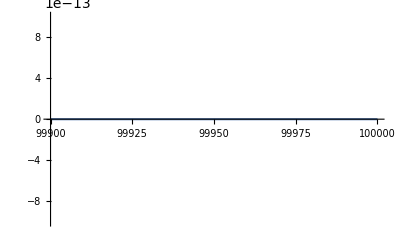

```mathematica
Plot[if[t]-if2[t],{t,99900,100000},PlotRange->{-10^-12,10^-12}]
```

```mathematica
if=n/.NDSolve[{n'[t]==1,n[0]==0,WhenEvent[Mod[t,1],n[t]->0]},n,{t,0,2}]⟦1⟧;
```

```mathematica
if2=InterpolatingFunctionTake[if,{0.5,1.5}]
```

InterpolatingFunction[…]

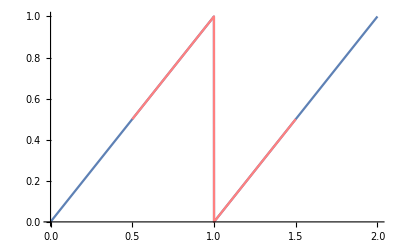

```mathematica
Show[Plot[if[t],{t,0,2}],Plot[if2[t],{t,0.5,1.5},PlotStyle->Pink]]
```

### *Slice* / FinalDerivatives / *Time

```mathematica
?Slice
```

Slice[rulelist, t] replaces temporal rulelist with its values at t.
Slice[rulelist, {tmin, tmax}] extracts values from tmin to tmax.

```mathematica
?InitialSlice
```

InitialSlice[rulelist] extracts the initial values from temporal rulelist.
InitialSlice[rulelist, tmax] extracts the initial values ending at tmax.

```mathematica
?FinalSlice
```

FinalSlice[rulelist] extracts the final values from temporal rulelist.
FinalSlice[rulelist, tmin] extracts the final values starting at tmin.

```mathematica
?FinalDerivatives
```

FinalDerivatives[rulelist] replaces temporal rulelist with their final derivatives.
FinalDerivatives[rulelist, δ] averages over the final values starting at δ.

```mathematica
?InitialTime
```

InitialTime[rulelist] returns the initial time of temporal rulelist.

```mathematica
?FinalTime
```

FinalTime[rulelist] returns the final time of temporal rulelist.

#### List

```mathematica
sol={x->Table[{t,t^2},{t,0,10}]}
```

{x→{{0,0},{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}}

```mathematica
FinalSlice[sol]
```

{x→100}

```mathematica
Slice[sol,{5,10}]
```

{x→{{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}}

#### ricker

{n→TimeSeries[…]}

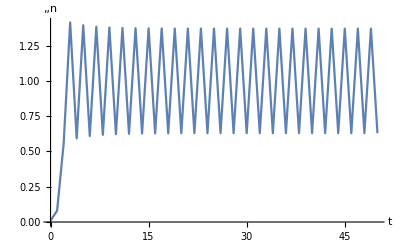

```mathematica
SetModel[ricker]
rr=2.1;
tmax=50;
sol=EcoSim[{n->0.01},tmax]
PlotDynamics[sol]
```

```mathematica
Table[{t,n[t]/.sol},{t,0,10}]
```

{{0,0.01},{1,0.0799647},{2,0.552061},{3,1.41422},{4,0.592575},{5,1.39419},{6,0.609274},{7,1.38408},{8,0.617834},{9,1.37852},{10,0.622578}}

```mathematica
Slice[sol,10]
```

{n→0.622578}

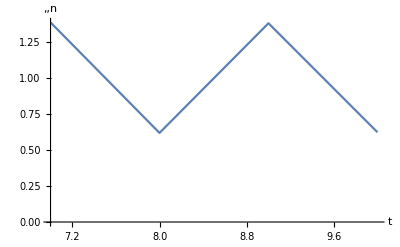

```mathematica
PlotDynamics@Slice[sol,{7,10}]
```

```mathematica
InitialSlice[sol]
```

{n→0.01}

```mathematica
InitialSlice[sol,1]
```

{n→TimeSeries[…]}

```mathematica
FinalSlice[sol]
```

{n→0.629294}

```mathematica
FinalSlice[sol,1]
```

{n→TimeSeries[…]}

```mathematica
FinalDerivatives[sol]
```

{n→-0.741412}

```mathematica
FinalDerivatives[sol,2]
```

{n→8.79758×10^-8}

```mathematica
InitialTime[sol]
```

0

```mathematica
FinalTime[sol]
```

50

#### lvc

```mathematica
SetModel[lvc];
```

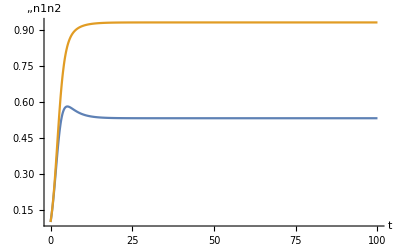

```mathematica
tmax=100;
sol=EcoSim[{n1->0.1,n2->0.1},tmax];
PlotDynamics[sol]
```

```mathematica
Slice[sol,10]
```

{n1→0.548869,n2→0.919504}

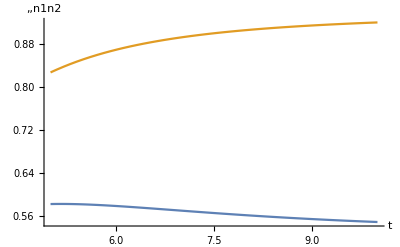

```mathematica
PlotDynamics[Slice[sol,{5,10}]]
```

```mathematica
InitialSlice[sol]
```

{n1→0.1,n2→0.1}

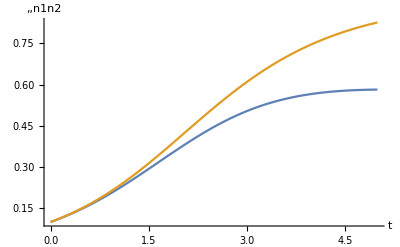

```mathematica
PlotDynamics[InitialSlice[sol,5]]
```

```mathematica
FinalSlice[sol]
```

{n1→0.533333,n2→0.933333}

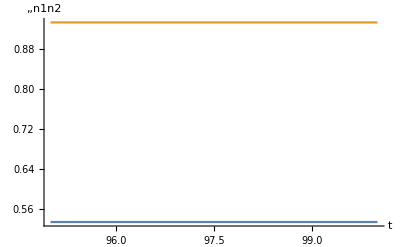

```mathematica
PlotDynamics[FinalSlice[sol,5]]
```

```mathematica
FinalDerivatives[sol]
```

{n1→6.06932×10^-12,n2→-5.0564×10^-12}

```mathematica
FinalDerivatives[sol,tmax]
```

{n1→0.00433333,n2→0.00833333}

```mathematica
InitialTime[sol]
```

0.

```mathematica
FinalTime[sol]
```

100.

#### jon

```mathematica
SetModel[jon];
```

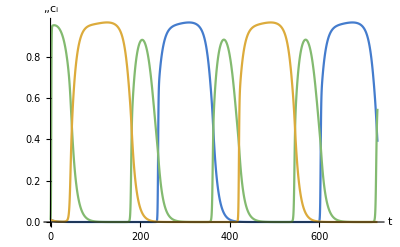

```mathematica
T=365;
tmax=2T;
sol=EcoSim[{Subscript[x, 1]->10,Subscript[x, 2]->15,Subscript[x, 3]->20},{Subscript[c, 1]->0.01,Subscript[c, 2]->0.01,Subscript[c, 3]->0.01},tmax];
PlotDynamics[sol]
```

```mathematica
Slice[sol,600]
```

{c_1→0.00372092,c_2→0.45436,c_3→0.00207044}

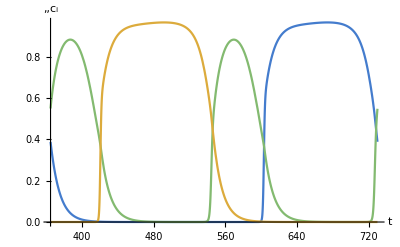

```mathematica
PlotDynamics[Slice[sol,{tmax-T,tmax}]]
```

```mathematica
InitialSlice[sol]
```

{c_1→0.01,c_2→0.01,c_3→0.01}

```mathematica
FinalSlice[sol]
```

{c_1→0.388443,c_2→0.548294,c_3→5.00612×10^-9}

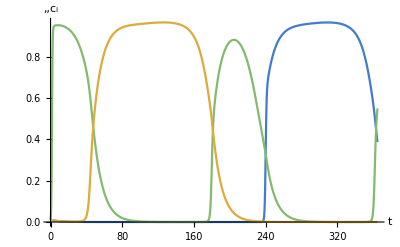

```mathematica
PlotDynamics[InitialSlice[sol,T]]
```

```mathematica
PlotDynamics[FinalSlice[sol,T]]
```

-Graphics-

```mathematica
FinalDerivatives[sol]
```

{c_1→-0.0374941,c_2→0.0492307,c_3→-4.8321×10^-10}

```mathematica
FinalDerivatives[sol,T]
```

{c_1→2.38096×10^-6,c_2→-3.60902×10^-6,c_3→-2.28903×10^-13}

### SubscriptAdd

```mathematica
SubscriptAdd[Subscript[x, 1],2]
```

x_3

### DeleteSubscript

```mathematica
DeleteSubscript[Subscript[x, 2]]
```

x

### ZeroSubscript

```mathematica
ZeroSubscript[Subscript[x, 2]]
```

x_0

## EcoEvo Utilities

### SetModel

```mathematica
?SetModel
```

SetModel[model] sets an EcoEvo model for analysis.

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 0.9.4X (December 30, 2018)

```mathematica
lv={Guild[1]->{Variable->n,Equation->g,Trait[1]->{Variable->x,Range->Interval[{-1,1}]}}};
g[i_]:=r*(1-Sum[a[Subscript[x, i],Subscript[x, j]]*Subscript[n, j][t],{j,Nsp[1]}]/k[Subscript[x, i]])*Subscript[n, i][t];
SetModel[lv]
```

modelguilds={Guild[1]→{Variable→n,Equation→g,Trait[1]→{Variable→x,Range→Interval[{-1,1}]}}}

guilds={1}

nguilds=1

1 {1,1}

Nsp={1}

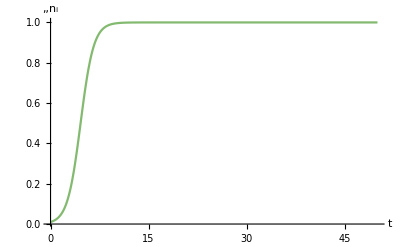

```mathematica
tmax=50;
sol=EcoSim[{Subscript[x, 1]->0},{Subscript[n, 1]->0.01},tmax];
PlotDynamics[sol,PlotRange->All]
```

```mathematica
lv={Guild["n"]->{Variable->n,Equation->g,Trait[1]->{Variable->x,Range->Interval[{-1,1}]}}};
g[i_]:=r*(1-Sum[a[Subscript[x, i],Subscript[x, j]]*Subscript[n, j][t],{j,Nsp["n"]}]/k[Subscript[x, i]])*Subscript[n, i][t];
SetModel[lv]
```

modelguilds={Guild[n]→{Variable→n,Equation→g,Trait[1]→{Variable→x,Range→Interval[{-1,1}]}}}

guilds={n}

nguilds=1

n {1,1}

```mathematica
tmax=50;
sol=EcoSim[{Subscript[x, 1]->0},{Subscript[n, 1]->0.01},tmax];
PlotDynamics[sol,PlotRange->All]
```

Nsp={1}

-Graphics-

```mathematica
lv={Guild[n]->{Variable->n,Equation->g,Trait[1]->{Variable->x,Range->Interval[{-1,1}]}}};
g[i_]:=r*(1-Sum[a[Subscript[x, i],Subscript[x, j]]*Subscript[n, j][t],{j,Nsp[n]}]/k[Subscript[x, i]])*Subscript[n, i][t];
SetModel[lv]
```

modelguilds={Guild[n]→{Variable→n,Equation→g,Trait[1]→{Variable→x,Range→Interval[{-1,1}]}}}

guilds={n}

nguilds=1

n {1,1}

```mathematica
tmax=50;
sol=EcoSim[{Subscript[x, 1]->0},{Subscript[n, 1]->0.01},tmax];
PlotDynamics[sol,PlotRange->All]
```

Nsp={1}

-Graphics-

### MatrixToComponents

```mathematica
MatrixToComponents[{{3,8},{1/2,0}},n]
```

{Component[1]→{Variable→n[1],Equation:>3 n[1][t]+8 n[2][t]},Component[2]→{Variable→n[2],Equation:>1/2 n[1][t]}}

```mathematica
MatrixToComponents[A,n,3]
```

{Component[1]→{Variable→n[1],Equation:>A⟦1,1⟧ n[1][t]+A⟦1,2⟧ n[2][t]+A⟦1,3⟧ n[3][t]},Component[2]→{Variable→n[2],Equation:>A⟦2,1⟧ n[1][t]+A⟦2,2⟧ n[2][t]+A⟦2,3⟧ n[3][t]},Component[3]→{Variable→n[3],Equation:>A⟦3,1⟧ n[1][t]+A⟦3,2⟧ n[2][t]+A⟦3,3⟧ n[3][t]}}

### SetNsp

```mathematica
SetModel[lv]
```

```mathematica
EcoSim[{Subscript[x, 1]->0,Subscript[x, 2]->0.2},{Subscript[n, 1]->0.01,Subscript[n, 2]->0.01},1];
```

```mathematica
EcoSim[{Subscript[x, 1]->0,Subscript[x, 2]->0.2},{Subscript[n, 1]->0.01,Subscript[n, 2]->0.01,Subscript[n, 3]->0.01},1];
```

SetNsp::badnsp: Number of species inconsistent between traits {2} and densities {3}.

$Aborted

```mathematica
SetModel[si]
```

```mathematica
EcoSim[{Subscript[B, 1]->1,Subscript[B, 2]->1},{Subscript[s, 1]->1,Subscript[i, 1]->1,Subscript[s, 2]->1},1]
```

SetNsp::badcomm: Number of components in guild 1 inconsistent: {2,1}.

$Aborted

```mathematica
SetModel[lv2]
```

```mathematica
EcoSim[{Subscript[x, 1]->0,Subscript[y, 1]->0,Subscript[x, 2]->0,Subscript[y, 2]->0},{Subscript[n, 1]->1,Subscript[n, 2]->1},1];
```

```mathematica
EcoSim[{Subscript[x, 1]->0,Subscript[y, 1]->0,Subscript[x, 2]->0},{Subscript[n, 1]->1,Subscript[n, 2]->1},1];
```

SetNsp::badtr: Number of traits in guild 1 inconsistent: {2,1}.

$Aborted

```mathematica
EcoSim[{Subscript[x, 1]->0,Subscript[y, 1]->0,Subscript[x, 2]->0,Subscript[y, 2]->0,Subscript[x, 3]->0},{Subscript[n, 1]->1,Subscript[n, 2]->1},1];
```

SetNsp::badtr: Number of traits in guild 1 inconsistent: {3,2}.

$Aborted

```mathematica
EcoSim[{Subscript[x, 1]->0,Subscript[y, 1]->0,Subscript[x, 2]->0,Subscript[y, 2]->0},{Subscript[n, 1]->1},1];
```

SetNsp::badnsp: Number of species inconsistent between traits {2} and densities {1}.

$Aborted

### LookUp

```mathematica
?LookUp
```

LookUp[var] finds the indices of a variable or trait.

#### lvc

```mathematica
SetModel[lvc]
```

```mathematica
LookUp[n1]
```

{pcomp,1,1}

```mathematica
LookUp[n2]
```

{pcomp,2,1}

#### lv

```mathematica
SetModel[lv]
```

```mathematica
LookUp[Subscript[n, 1]]
```

{gcomp,1,1,1}

```mathematica
LookUp[Subscript[n, 10]]
```

{gcomp,1,1,10}

```mathematica
LookUp[Subscript[x, 2]]
```

{trait,1,1,2}

```mathematica
LookUp[k0]
```

### ExtractTraits / ExtractAuxs / ExtractPops / ExtractGuilds / ExtractVariables

```mathematica
?ExtractTraits
```

ExtractTraits[x] extracts traits from rulelist or list of rulelists x.

```mathematica
?ExtractAuxs
```

ExtractAuxs[x] extracts auxs from rulelist or list of rulelists x.

```mathematica
?ExtractPops
```

ExtractPops[x] extracts pops from rulelist or list of rulelists x.

```mathematica
?ExtractGuilds
```

ExtractGuilds[x] extracts guilds from rulelist or list of rulelists x.

```mathematica
?ExtractVariables
```

ExtractVariables[x] extracts pops, guilds, and auxs from rulelist or list of rulelists x.

#### lv

```mathematica
SetModel[lv]
```

```mathematica
ExtractTraits[{Subscript[x, 1]->1,Subscript[n, 1]->2}]
```

{x_1→1}

```mathematica
ExtractTraits[{{Subscript[x, 1]->1,Subscript[n, 1]->2},{Subscript[x, 1]->2,Subscript[n, 1]->3}}]
```

{}

```mathematica
ExtractGuilds[{Subscript[x, 1]->1,Subscript[n, 1]->2}]
```

{n_1→2}

```mathematica
ExtractGuilds[{{Subscript[x, 1]->1,Subscript[n, 1]->2},{Subscript[x, 1]->2,Subscript[n, 1]->3}}]
```

{}

```mathematica
ExtractTraits[{Subscript[x, 1]->1,Subscript[n, 1]->2}]
```

{x_1→1}

```mathematica
ExtractVariables[{Subscript[x, 1]->1,Subscript[n, 1]->2}]
```

{n_1→2}

```mathematica
ExtractVariables[{{Subscript[x, 1]->1,Subscript[n, 1]->2},{Subscript[x, 1]->2,Subscript[n, 1]->3}}]
```

{}

### TraitsQ / VariablesQ / TraitsAndVariablesQ

```mathematica
?TraitsQ
```

TraitsQ[x] returns True if x is a rulelist of traits.

```mathematica
?VariablesQ
```

VariablesQ[x] returns True if x is a rulelist of variables.

```mathematica
?TraitsAndVariablesQ
```

TraitsAndVariablesQ[x] returns True if x is a rulelist of traits and/or variables.

#### ricker

```mathematica
SetModel[ricker]
```

```mathematica
VariablesQ[{n->0.9}]
```

True

```mathematica
TraitsQ[{n->0.9}]
```

False

```mathematica
TraitsAndVariablesQ[{n->0.9}]
```

False

#### lv

```mathematica
SetModel[lv]
```

```mathematica
TraitsQ[{Subscript[x, 1]->1}]
```

True

```mathematica
tmp={Nsp[1]->1};
```

```mathematica
TraitsQ[{Nsp[1]->1}]
```

True

```mathematica
TraitsQ[{Subscript[x, 1]->1,Subscript[x, 2]->2}]
```

True

```mathematica
TraitsQ[{Subscript[x, 1]->1,Subscript[y, 2]->2}]
```

False

```mathematica
VariablesQ[{Subscript[n, 1]->1}]
```

True

```mathematica
VariablesQ[{Subscript[n, 1]->1,Subscript[x, 1]->1}]
```

False

```mathematica
TraitsAndVariablesQ[{Subscript[n, 1]->1,Subscript[x, 1]->1}]
```

True

### DeleteInvaders

```mathematica
DeleteInvaders[{Subscript[x, 0]->-0.5,Subscript[x, 1]->0.5}]
```

{x_1→0.5}

### ModelInfo

```mathematica
SetModel[lv]
```

```mathematica
ModelInfo
```

ModelType=ContinuousTime

NumAuxs=0

NumPops=0

NumGuilds=1

NumGuildComponents[n]=1

GuildComponentVar[n,1]=n

GuildComponentEqn[n,1]=g

GuildComponentRange[n,1]=Interval[{0,∞}]

GuildComponentType[n,1]=Extensive

NumTraits[n]=1

TraitVar[n,1]=x

TraitRange[n,1]=Interval[{-1,1}]

```mathematica
SetModel[si]
```

```mathematica
ModelInfo
```

ModelType=ContinuousTime

NumAuxs=0

NumPops=0

NumGuilds=1

NumGuildComponents[1]=2

GuildComponentVar[1,1]=s

GuildComponentEqn[1,1]=ds

GuildComponentRange[1,1]=Interval[{0,∞}]

GuildComponentType[1,1]=Extensive

GuildComponentVar[1,2]=i

GuildComponentEqn[1,2]=di

GuildComponentRange[1,2]=Interval[{0,∞}]

GuildComponentType[1,2]=Extensive

NumTraits[1]=1

TraitVar[1,1]=B

TraitRange[1,1]=Interval[{0,1}]

### EcoEqns

#### ricker

```mathematica
SetModel[ricker]
```

```mathematica
EcoEqns[]
```

{n[1+t]==ⅇ^(rr (1-n[t])) n[t]}

```mathematica
EcoEqns[Logged->True]
```

{n[1+t]==ⅇ^(rr (1-n[t])) n[t]}

#### lvc

```mathematica
SetModel[lvc]
```

```mathematica
EcoEqns[]
```

fixedvars={}

AllVariables={n1,n2}

nonfixedvars={n1,n2}

fixed2={}

{n1'[t]==n1[t] (1-n1[t]-0.5 n2[t]),n2'[t]==n2[t] (1-0.833333 (0.5 n1[t]+n2[t]))}

{n1'[t]==n1[t] (1-n1[t]-0.5 n2[t]),n2'[t]==n2[t] (1-0.833333 (0.5 n1[t]+n2[t]))}

```mathematica
EcoEqns[Fixed->{n2->0}]
```

fixedvars={n2}

AllVariables={n1,n2}

nonfixedvars={n1}

fixed2={n2[t]→0}

{n1'[t]==n1[t] (1-n1[t]-0.5 n2[t])}

{n1'[t]==(1.-n1[t]) n1[t]}

#### lv

```mathematica
SetModel[lv]
```

```mathematica
EcoEqns[{Nsp[n]->1}]
```

{n_1'[t]==n_1[t] (1-n_1[t]/(1-x_1^2))}

```mathematica
EcoEqns[{Nsp[n]->2}]
```

{n_1'[t]==n_1[t] (1-(n_1[t]+ⅇ^(-2 (x_1-x_2)^2) n_2[t])/(1-x_1^2)),n_2'[t]==n_2[t] (1-(ⅇ^(-2 (-x_1+x_2)^2) n_1[t]+n_2[t])/(1-x_2^2))}

```mathematica
EcoEqns[{Subscript[x, 1]->0.1}]
```

{n_1'[t]==(1-1.0101 n_1[t]) n_1[t]}

```mathematica
EcoEqns[{Subscript[x, 1]->0.1,Subscript[x, 2]->0.2}]
```

{n_1'[t]==n_1[t] (1-1.0101 (n_1[t]+0.980199 n_2[t])),n_2'[t]==n_2[t] (1-1.04167 (0.980199 n_1[t]+n_2[t]))}

```mathematica
EcoEqns[{Subscript[x, 1]->0.1,Subscript[x, 2]->0.2},Fixed->{Subscript[n, 2]->0}]
```

{n_1'[t]==n_1[t] (1-1.0101 (n_1[t]+0.980199 n_2[t]))}

## Ecological Commands

### EcoEqns

#### lv

```mathematica
SetModel[lv]
```

```mathematica
EcoEqns[{Nsp[1]->1}]
```

{n_1'[t]==n_1[t] (1-n_1[t]/(1-x_1^2))}

```mathematica
EcoEqns[{Nsp[1]->1}]/.RemovePopts/.ZeroLHS
```

{0==n_1 (1-n_1/(1-x_1^2))}

```mathematica
EcoEqns[{Subscript[x, 1]->0.1}]
```

{n_1'[t]==(1-1.0101 n_1[t]) n_1[t]}

### EcoSim

```mathematica
?EcoSim
```

EcoSim[pops, tmax] simulates ecological dynamics, with initial densities in pops, from time t=0 to tmax.
EcoSim[traits, pops, tmax] uses trait values traits.
EcoSim[traitsandpops, tmax] uses combined traitsandpops.

```mathematica
EcoSim[{},100]
```

EcoEvoGeneral::nomodel: No model loaded. Use SetModel first.

$Failed

#### ricker

```mathematica
SetModel[ricker]
```

```mathematica
tmax=10;
```

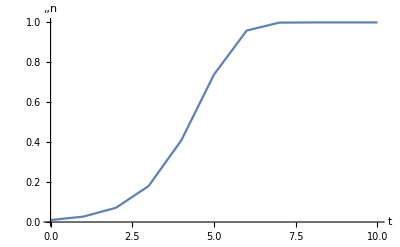

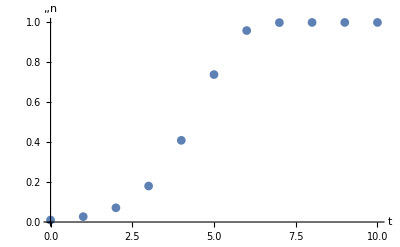

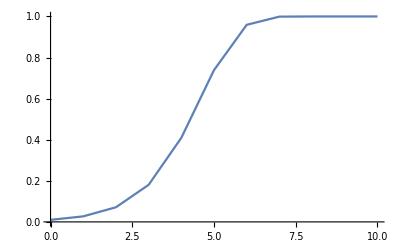

```mathematica
rr=1;
PlotDynamics[EcoSim[{n->0.01},tmax]]
PlotDynamics[EcoSim[{n->0.01},tmax],Joined->False]
PlotDynamics[EcoSim[{n->0.01},tmax],AxesLabel->None]
```

```mathematica
EcoSim[{n->0.01},tmax,Verbose->True]
```

res=RecurrenceTable[{n[1+t]==ⅇ^(1-n[t]) n[t],n[0]==0.01},{n},{t,0,10},Method→{Compiled→False}]

{n→TimeSeries[…]}

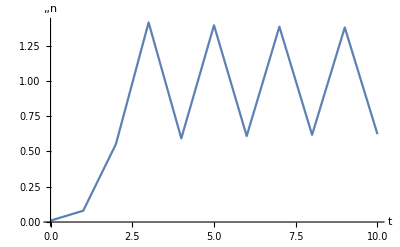

```mathematica
rr=2.1;
PlotDynamics[EcoSim[{n->0.01},tmax]]
```

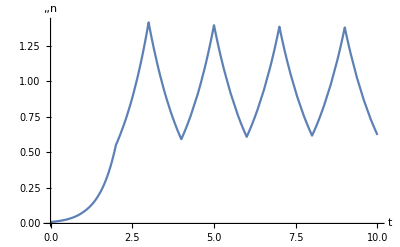

```mathematica
rr=2.1;
PlotDynamics[EcoSim[{n->0.01},tmax,Logged->True]]
(* need to fix transformation for TimeSeries *)
```

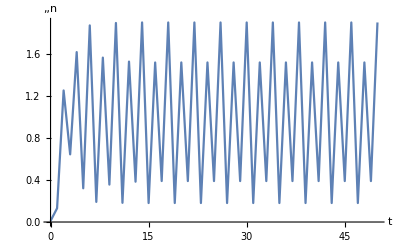

```mathematica
tmax=50;
rr=2.6;
PlotDynamics[EcoSim[{n->0.01},tmax]]
```

#### lvc

```mathematica
SetModel[lvc];
```

```mathematica
tmax=100;
sol=EcoSim[{n1->0.1,n2->0.1},tmax,Verbose->True];
PlotDynamics[sol]
```

sol=NDSolve[{n1'[t]==n1[t] (1-n1[t]-0.5 n2[t]),n2'[t]==n2[t] (1-0.833333 (0.5 n1[t]+n2[t])),n1[0]==0.1,n2[0]==0.1},{n1,n2},{t,0,100}]⟦1⟧

-Graphics-

sol=NDSolve[{log[n1]'[t]==1-ⅇ^(log[n1][t])-0.5 ⅇ^(log[n2][t]),log[n2]'[t]==1-0.833333 (0.5 ⅇ^(log[n1][t])+ⅇ^(log[n2][t])),log[n1][0]==-2.30259,log[n2][0]==-2.30259},{log[n1],log[n2]},{t,0,100}]⟦1⟧

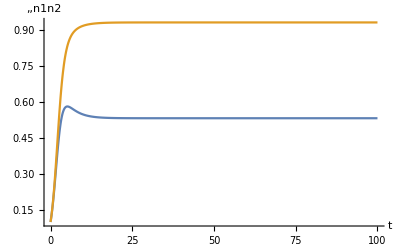

```mathematica
tmax=100;
sol=EcoSim[{n1->0.1,n2->0.1},tmax,Logged->True,Verbose->True];
PlotDynamics[sol]
```

```mathematica
sol=EcoSim[{n1->0.1,n2->0.1},tmax,OutputTMin->tmax-10]
```

{n1→InterpolatingFunction[…],n2→InterpolatingFunction[…]}

```mathematica
sol=EcoSim[{n1->0.1,n2->0.1},tmax,Output->"FinalSlice"]
```

{n1→0.533333,n2→0.933333}

sol=NDSolve[{n1'[t]==n1[t] (1-n1[t]-0.5 n2[t]),n2'[t]==(1+1/43 (-0.5 n1[t]-n2[t])) n2[t],n1[0]==0.1,n2[0]==0.1},{n1,n2},{t,0,100}]⟦1⟧

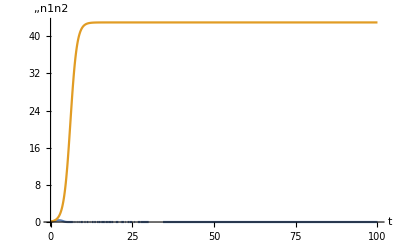

```mathematica
k2=43;
sol=EcoSim[{n1->0.1,n2->0.1},tmax,Verbose->True];
PlotDynamics[sol]
```

```mathematica
EcoSim[{n2->0.1},tmax,Fixed->{n1->0},Verbose->True]
```

sol=NDSolve[{n2'[t]==(1+1/43 (0.-n2[t])) n2[t],n2[0]==0.1},{n2},{t,0,100}]⟦1⟧

{n1→InterpolatingFunction[…],n2→InterpolatingFunction[…]}

```mathematica
EcoSim[{n2->0.1},tmax,Fixed->{n1->0},Output->"FinalSlice"]
```

{n1→0,n2→43.}

```mathematica
EcoSim[{n1->0.1},tmax]
```

{n1→InterpolatingFunction[…],n2→InterpolatingFunction[…]}

```mathematica
EcoSim[{n2->0.1},tmax]
```

{n1→InterpolatingFunction[…],n2→InterpolatingFunction[…]}

```mathematica
k2=1.2;
```

#### rm

```mathematica
SetModel[rm]
```

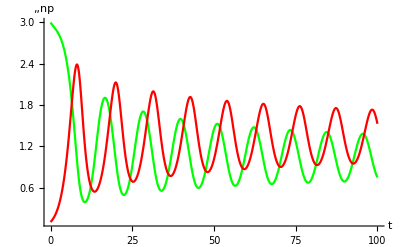

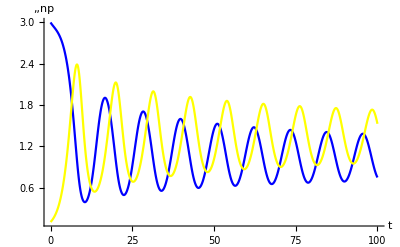

```mathematica
tmax=100;
nk=3;
sol=EcoSim[{n->nk,p->0.1},tmax];
PlotDynamics[sol]
PlotDynamics[sol,PlotStyle->{Blue,Yellow}]
```

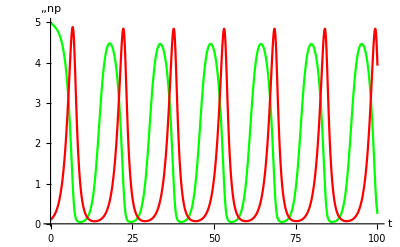

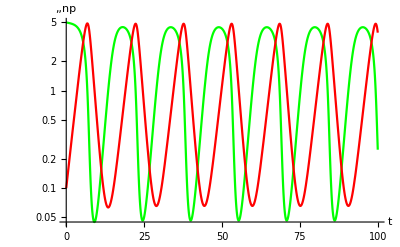

```mathematica
nk=5;
sol=EcoSim[{n->nk,p->0.1},tmax];
PlotDynamics[sol]
PlotDynamics[sol,Logged->True]
```

```mathematica
nk=2;
```

#### fl

```mathematica
SetModel[fl]
```

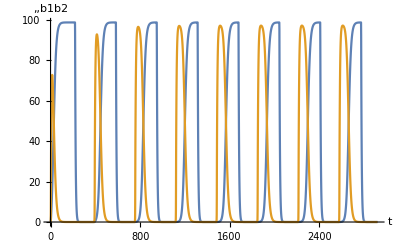

{b1→2.05636×10^-11,b2→1.79052×10^-15,R→20.}

```mathematica
ϕ=0.6;
tmax=8T;
sol=EcoSim[{b1->0.1,b2->0.1,R->Rin},tmax,NDSolveOpts->{AccuracyGoal->24}];
PlotDynamics[sol,{b1,b2}]
FinalSlice[sol]
```

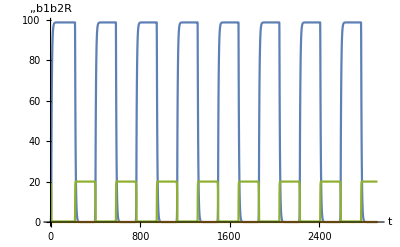

```mathematica
sol=EcoSim[{b1->0.1,R->Rin},tmax,NDSolveOpts->{AccuracyGoal->24}];
PlotDynamics[sol]
```

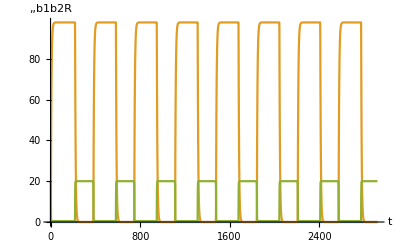

```mathematica
sol=EcoSim[{b2->0.1,R->Rin},tmax,NDSolveOpts->{AccuracyGoal->32}];
PlotDynamics[sol]
```

```mathematica
sol=EcoSim[{b1->0.1,b2->0.1,R->Rin},tmax,Logged->True];
FinalSlice[sol]
```

{b1→2.05636×10^-11,b2→1.79052×10^-15,R→20.}

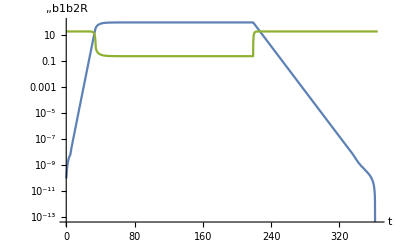

```mathematica
sol=EcoSim[{b1->10.^-10,R->Rin},T,Fixed->{b2->0}];
PlotDynamics[sol,Logged->True]
```

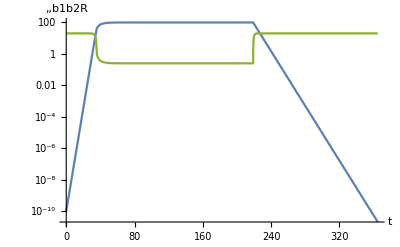

```mathematica
sol=EcoSim[{b1->10.^-10,R->Rin},T,Logged->True,Fixed->{b2->0}];
PlotDynamics[sol,Logged->True]
```

#### twop

```mathematica
SetModel[twop]
```

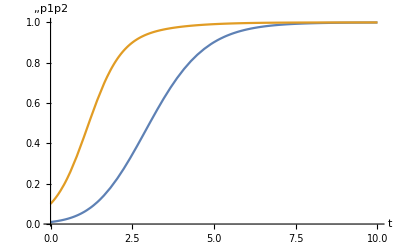

```mathematica
tmax=10;
disp=0.1;
sol=EcoSim[{p1->0.01,p2->0.1},tmax];
PlotDynamics[sol]
```

#### dl

```mathematica
SetModel[dl]
```

```mathematica
tmax=20;
sol=EcoSim[{j->0.1,a->0},tmax]
```

{j→TimeSeries[…],a→TimeSeries[…]}

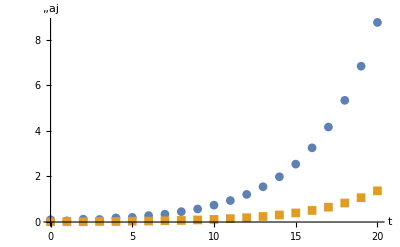

```mathematica
PlotDynamics[sol,Joined->False]
```

```mathematica
PlotDynamics[sol,Joined->False,PlotMarkers->{"J","A"}]
```

-Graphics-

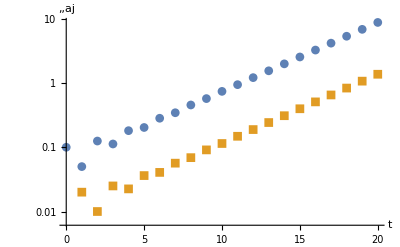

```mathematica
PlotDynamics[sol,Joined->False,Logged->True]
```

#### opt

```mathematica
SetModel[opt]
```

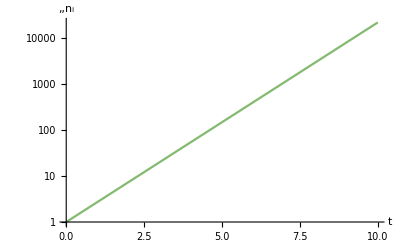

```mathematica
tmax=10;
sol=EcoSim[{Subscript[x, 1]->0},{Subscript[n, 1]->1},tmax];
PlotDynamics[sol,Logged->True]
```

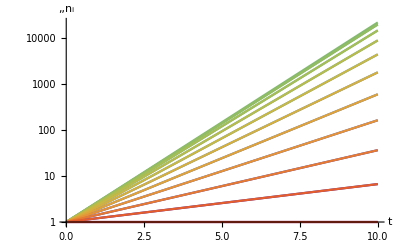

```mathematica
tmax=10;
nsp=21;
sol=EcoSim[RuleList[x,nsp,{-1,1}],RuleList[n,nsp,1],tmax];
PlotDynamics[sol,Logged->True]
```

#### lv

```mathematica
SetModel[lv]
```

```mathematica
tmax=50;
sol=EcoSim[{Subscript[x, 1]->0},{Subscript[n, 1]->0.01},tmax];
PlotDynamics[sol,PlotRange->All]
```

-Graphics-

```mathematica
tmax=50;
sol=EcoSim[{Subscript[x, 1]->0,Subscript[n, 1]->0.01},tmax];
PlotDynamics[sol,PlotRange->All]
```

-Graphics-

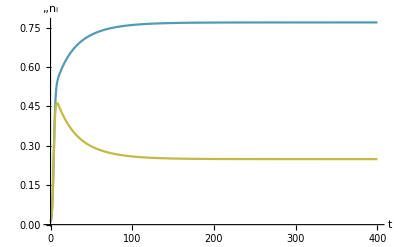

```mathematica
tmax=400;
sol=EcoSim[{Subscript[x, 1]->0,Subscript[x, 2]->0.2},{Subscript[n, 1]->0.01,Subscript[n, 2]->0.01},tmax];
PlotDynamics[sol]
```

```mathematica
sol=EcoSim[{Subscript[x, 1]->0,Subscript[x, 2]->0.2},{Subscript[n, 1]->0.01},tmax]
sol=EcoSim[{Subscript[x, 1]->0,Subscript[x, 2]->0.2},{Subscript[n, 2]->0.01},tmax]
```

SetNsp::badnsp: Number of species inconsistent between traits {2} and densities {1}.

$Aborted

{n_1→InterpolatingFunction[…],n_2→InterpolatingFunction[…]}

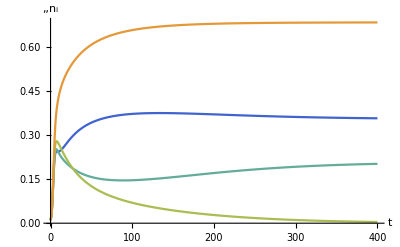

```mathematica
tmax=400;
sol=EcoSim[{Subscript[x, 1]->-0.5,Subscript[x, 2]->-0.2,Subscript[x, 3]->0,Subscript[x, 4]->0.25},{Subscript[n, 1]->0.01,Subscript[n, 2]->0.01,Subscript[n, 3]->0.01,Subscript[n, 4]->0.01},tmax];
PlotDynamics[sol]
```

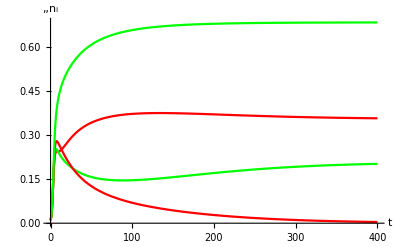

```mathematica
PlotDynamics[sol,PlotStyle->{Red,Green}]
```

```mathematica
SetModel[{Guild[n]->{Variable->n,Equation:>g,Trait[1]->{Variable->x,Range->Interval[{-1,1}]},Color->ColorData["AvocadoColors"]}}]
```

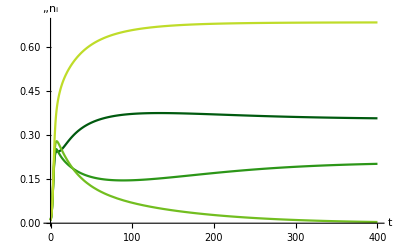

```mathematica
PlotDynamics[sol]
```

#### si

```mathematica
SetModel[si]
```

sol=NDSolve[{s_1'[t]==-0.07 s_1[t]-0.05 i_1[t] s_1[t]+0.35 (0.75 i_1[t]+s_1[t]) (1-0.05 (i_1[t]+s_1[t])),i_1'[t]==-0.28 i_1[t]+0.05 i_1[t] s_1[t],s_1[0]==0.1,i_1[0]==1/10000},{s_1,i_1},{t,0,100}]⟦1⟧

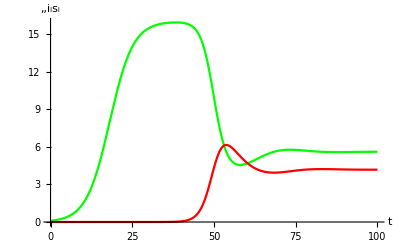

```mathematica
tmax=100;
sol=EcoSim[{Subscript[B, 1]->0.05},{Subscript[s, 1]->0.1,Subscript[i, 1]->10^-4},tmax,Verbose->True];
PlotDynamics[sol]
```

```mathematica
FinalSlice[sol]
```

{s_1→5.60324,i_1→4.17417}

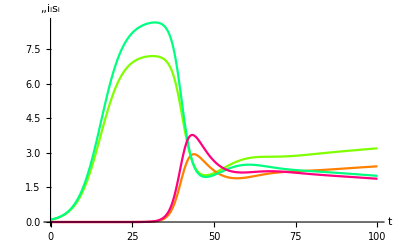

```mathematica
tmax=100;
sol=EcoSim[{Subscript[B, 1]->0.05,Subscript[B, 2]->0.06},{Subscript[s, 1]->0.1,Subscript[i, 1]->10^-4,Subscript[s, 2]->0.1,Subscript[i, 2]->10^-4},tmax];
PlotDynamics[sol]
```

#### ch

```mathematica
SetModel[ch]
```

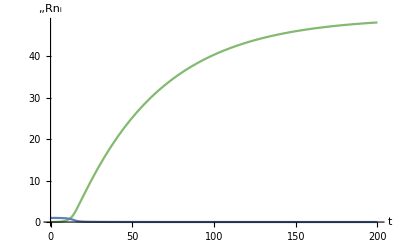

```mathematica
tmax=200;
sol=EcoSim[{Subscript[mu, 1]->0.5},{Subscript[n, 1]->0.01,R->1},tmax];
PlotDynamics[sol]
```

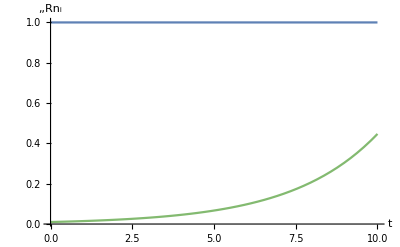

```mathematica
tmax=10;
sol=EcoSim[{Subscript[mu, 1]->0.5},{Subscript[n, 1]->0.01},tmax,Fixed->{R->1}];
PlotDynamics[sol]
```

```mathematica
FinalSlice[sol]
```

{n_1→48.2239,R→0.0106963}

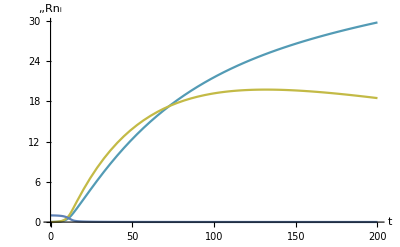

```mathematica
tmax=200;
sol=EcoSim[{Subscript[mu, 1]->0.5,Subscript[mu, 2]->0.6},{Subscript[n, 1]->0.01,Subscript[n, 2]->0.01,R->1},tmax];
PlotDynamics[sol]
```

#### pp

```mathematica
SetModel[pp]
```

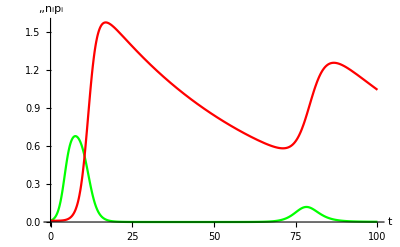

```mathematica
tmax=100;
sol=EcoSim[{Subscript[xn, 1]->0.5,Subscript[xp, 1]->0.5},{Subscript[n, 1]->0.01,Subscript[p, 1]-> 0.01},tmax];
PlotDynamics[sol,{n,p}]
```

```mathematica
FinalSlice[sol]
```

{n_1→0.00192488,p_1→1.04505}

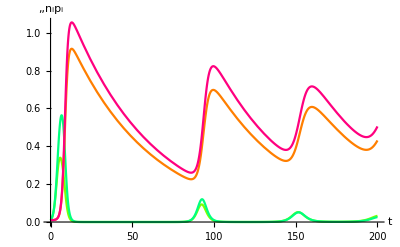

```mathematica
tmax=200;
sol=EcoSim[{Subscript[xn, 1]->0.5,Subscript[xp, 1]->0.5,Subscript[xn, 2]->0.0,Subscript[xp, 2]->0.0},{Subscript[n, 1]->0.01,Subscript[p, 1]-> 0.01,Subscript[n, 2]->0.01,Subscript[p, 2]-> 0.01},tmax];
PlotDynamics[sol]
```

#### lv2

```mathematica
SetModel[lv2]
```

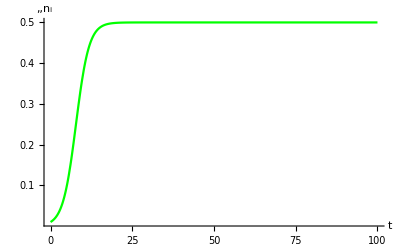

```mathematica
tmax=100;
sol=EcoSim[{Subscript[x, 1]->0.5,Subscript[y, 1]->0.5},{Subscript[n, 1]->0.01},tmax];
PlotDynamics[sol]
```

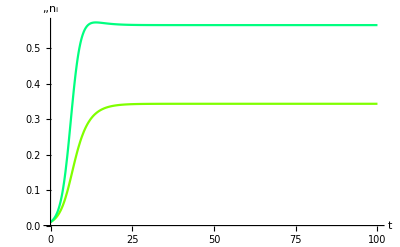

```mathematica
tmax=100;
sol=EcoSim[{Subscript[x, 1]->0.5,Subscript[y, 1]->0.5,Subscript[x, 2]->-0.3,Subscript[y, 2]->0.5},{Subscript[n, 1]->0.01,Subscript[n, 2]->0.01},tmax];
PlotDynamics[sol]
```

#### droop

```mathematica
SetModel[droop]
```

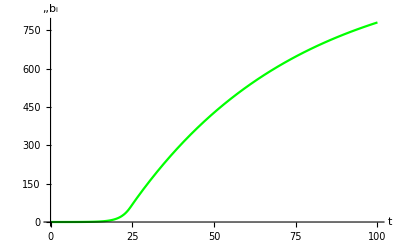

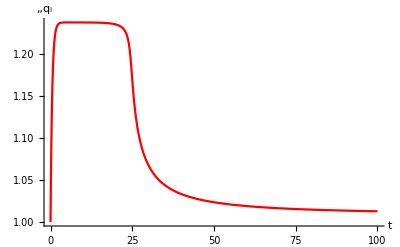

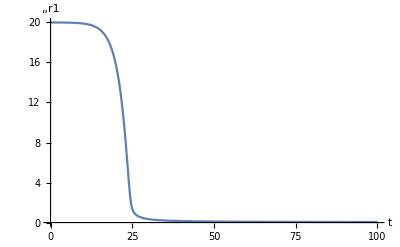

```mathematica
sol=EcoSim[{Subscript[a1, 1]->0.5},{Subscript[b, 1]->0.01,Subscript[q, 1]->qmin,r1->rin1},100];
PlotDynamics[sol,b]
PlotDynamics[sol,q]
PlotDynamics[sol,r1]
```

```mathematica
FinalSlice[sol]
```

{b_1→781.204,q_1→1.0128,r1→0.053814}

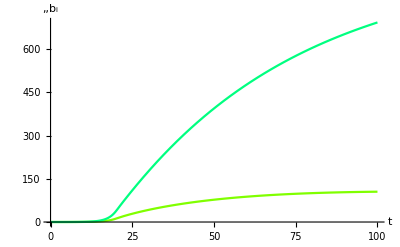

```mathematica
sol=EcoSim[{Subscript[a1, 1]->0.5,Subscript[a1, 2]->0.6},{Subscript[b, 1]->0.01,Subscript[q, 1]->qmin,Subscript[b, 2]->0.01,Subscript[q, 2]->qmin,r1->rin1},100];
PlotDynamics[sol,b]
```

#### dlv

```mathematica
SetModel[dlv]
```

```mathematica
tmax=20;
sol=EcoSim[{Subscript[x, 1]->0},{Subscript[n, 1]->0.01},tmax]
```

{n_1→TimeSeries[…]}

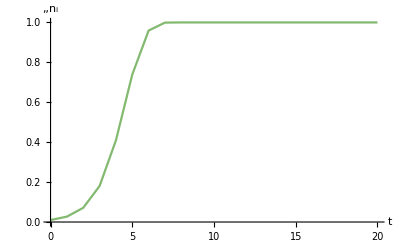

```mathematica
PlotDynamics[sol]
```

```mathematica
tmax=20;
sol=EcoSim[{Subscript[x, 1]->0,Subscript[x, 2]->0.2},{Subscript[n, 1]->0.01,Subscript[n, 2]->0.01},tmax]
```

{n_1→TimeSeries[…],n_2→TimeSeries[…]}

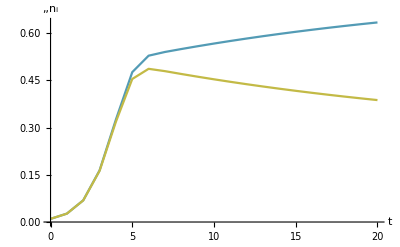

```mathematica
PlotDynamics[sol]
```

#### jon

```mathematica
SetModel[jon]
```

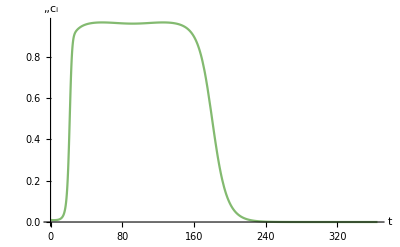

```mathematica
T=365;
sol=EcoSim[{Subscript[x, 1]->20},{Subscript[c, 1]->0.01},T];
PlotDynamics[sol]
```

```mathematica
tmax=2T;
sol=EcoSim[{Subscript[x, 1]->10,Subscript[x, 2]->15,Subscript[x, 3]->20},{Subscript[c, 1]->0.01,Subscript[c, 2]->0.01,Subscript[c, 3]->0.01},tmax];
PlotDynamics[sol]
```

-Graphics-

```mathematica
tmax=2T;
sol=EcoSim[{Subscript[x, 1]->10,Subscript[x, 2]->15,Subscript[x, 3]->20},{Subscript[c, 1]->0.01,Subscript[c, 2]->0.01,Subscript[c, 3]->0.01},tmax,Logged->True];
PlotDynamics[sol]
```

-Graphics-

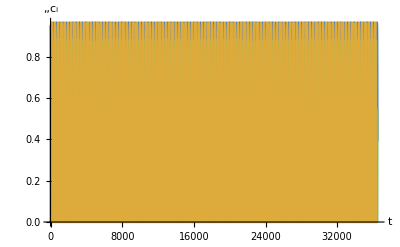

```mathematica
tmax=100T;
sol=EcoSim[{Subscript[x, 1]->10,Subscript[x, 2]->15,Subscript[x, 3]->20},{Subscript[c, 1]->0.01,Subscript[c, 2]->0.01,Subscript[c, 3]->0.01},tmax];
PlotDynamics[sol]
```

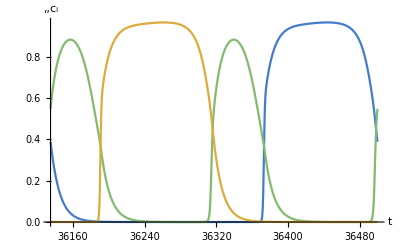

```mathematica
fs=Slice[sol,{tmax-T,tmax}];
PlotDynamics[fs]
```

#### mc

```mathematica
SetModel[mc]
```

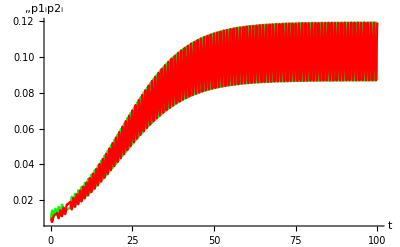

```mathematica
tmax=100;
sol=EcoSim[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.01,Subscript[p2, 1]->0.01},tmax];
PlotDynamics[sol]
```

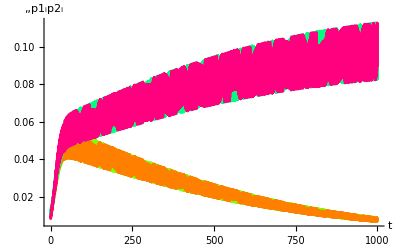

```mathematica
tmax=1000;
sol=EcoSim[{Subscript[dd, 1]->0.1,Subscript[dd, 2]->0.2},{Subscript[p1, 1]->0.01,Subscript[p2, 1]->0.01,Subscript[p1, 2]->0.01,Subscript[p2, 2]->0.01},tmax];
PlotDynamics[sol]
```

#### pulsed

```mathematica
SetModel[pulsed]
```

```mathematica
τ=10;
tmax=τ;
sol=EcoSim[{Subscript[a1, 1]->0.5},{r1->rin1,Subscript[b, 1]->1,Subscript[q, 1]->qmin},tmax,Verbose->True];
```

sol=NDSolve[{b_1'[t]==-0.02 b_1[t]+2 b_1[t] (1-1/q_1[t]),q_1'[t]==(0.5 r1[t])/(1+r1[t])-2 (1-1/q_1[t]) q_1[t],r1'[t]==20-r1[t]-(0.5 r1[t] b_1[t])/(1+r1[t]),r1[-1/1000000000000000]==20,b_1[-1/1000000000000000]==1,q_1[-1/1000000000000000]==1,WhenEvent[Mod[t,τ],r1[t]→r1[t]+10]},{r1,b_1,q_1},{t,0,10}]⟦1⟧

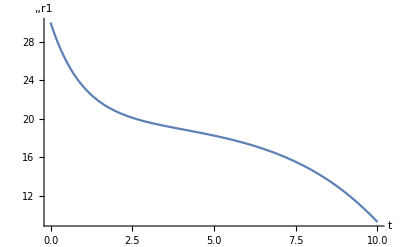

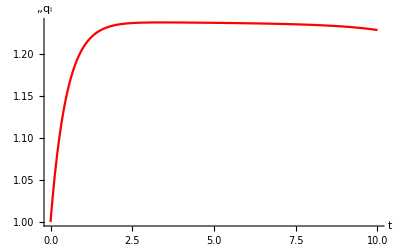

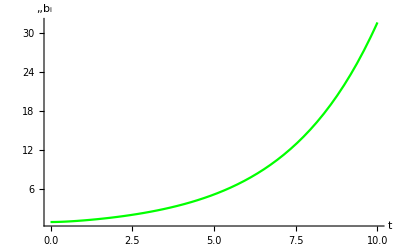

```mathematica
PlotDynamics[sol,r1]
PlotDynamics[sol,q]
PlotDynamics[sol,b]
```

```mathematica
τ=10;
tmax=10τ;
sol=EcoSim[{Subscript[a1, 1]->0.5},{r1->rin1,Subscript[b, 1]->1000,Subscript[q, 1]->qmin},tmax];
FinalSlice[sol]
```

{b_1→1029.46,q_1→1.00969,r1→0.0403411}

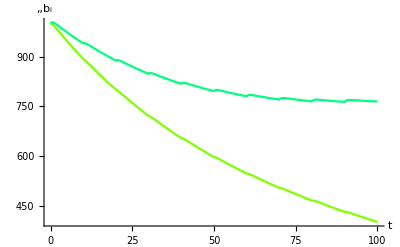

```mathematica
sol=EcoSim[{Subscript[a1, 1]->0.5,Subscript[a1, 2]->0.8},{r1->rin1,Subscript[b, 1]->1000,Subscript[q, 1]->qmin,Subscript[b, 2]->1000,Subscript[q, 2]->qmin},tmax];
PlotDynamics[sol,b]
```

#### dormant

```mathematica
SetModel[dormant]
```

```mathematica
τ=100;
tmax=10τ;
sol=EcoSim[{Subscript[a1, 1]->0.5},{r1->rin1,Subscript[b, 1]->1000,Subscript[bd, 1]->0,Subscript[q, 1]->qmin},tmax]
```

{b_1→InterpolatingFunction[…],bd_1→InterpolatingFunction[…],q_1→InterpolatingFunction[…],r1→InterpolatingFunction[…]}

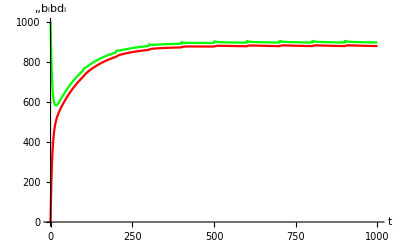

```mathematica
PlotDynamics[sol,{Subscript[b, 1],Subscript[bd, 1]}]
```

#### dfltwop

```mathematica
SetModel[dfltwop]
```

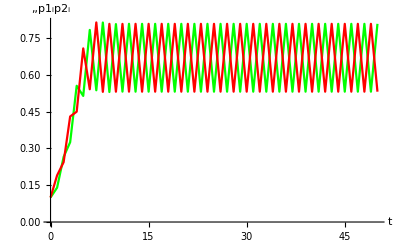

```mathematica
tmax=50;
sol=EcoSim[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.1,Subscript[p2, 1]->0.1},tmax];
PlotDynamics[sol]
```

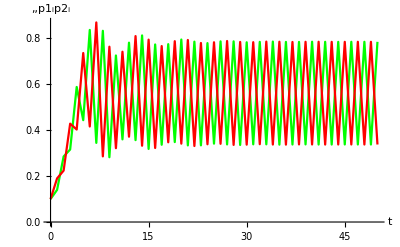

```mathematica
sol=EcoSim[{Subscript[dd, 1]->0.5},{Subscript[p1, 1]->0.1,Subscript[p2, 1]->0.1},tmax];
PlotDynamics[sol]
```

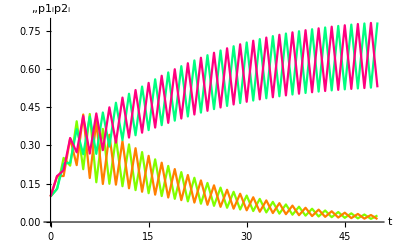

```mathematica
sol=EcoSim[{Subscript[dd, 1]->0.5,Subscript[dd, 2]->0.05},{Subscript[p1, 1]->0.1,Subscript[p2, 1]->0.1,Subscript[p1, 2]->0.1,Subscript[p2, 2]->0.1},tmax];
PlotDynamics[sol]
```

### SolveEcoEq / NSolveEcoEq / FindEcoEq / SelectValid / EcoJacobian / EcoEigenvalues / EcoStableQ / SelectEcoStable

```mathematica
?SolveEcoEq
```

SolveEcoEq[] solves for ecological equilibria.
SolveEcoEq[vars] solves for variables vars.
SolveEcoEq[traits] uses trait values traits.
SolveEcoEq[traits, vars] solves for variables vars using trait values traits.

```mathematica
?NSolveEcoEq
```

NSolveEcoEq[] numerically solves for ecological equilibria.
NSolveEcoEq[vars] numerically solves for variables vars.
NSolveEcoEq[traits] uses trait values traits.
NSolveEcoEq[traits, vars] numerically solves for variables vars using trait values traits.

```mathematica
?FindEcoEq
```

FindEcoEq[pops] finds an ecological equilibrium using initial guess pops.
FindEcoEq[traits, pops] uses trait values traits and initial guess pops.

```mathematica
?SelectValid
```

SelectValid[sol] selects valid solutions in list of rule lists sol.

```mathematica
?EcoJacobian
```

EcoJacobian[pops] returns the Jacobian matrix of the ecological equations evaluated at pops.
EcoJacobian[traits, pops] uses trait values traits.

```mathematica
?EcoEigenvalues
```

EcoEigenvalues[pops] returns the eigenvalues of the Jacobian matrix of the ecological equations evaluated at pops.
EcoEigenvalues[traits, pops] uses trait values traits.

```mathematica
?EcoStableQ
```

EcoStableQ[pops] reports the linear stability of an equilibrium as True, False, or Indeterminate.
EcoStableQ[traits, pops] uses trait values traits.
EcoStableQ[traitsandpops] uses combined trait and community state traitsandpops.

```mathematica
?SelectEcoStable
```

SelectEcoStable[sol] selects stable equilibria from sol.
SelectEcoStable[traits, sol] uses trait values traits.

#### ricker

```mathematica
SetModel[ricker]
```

```mathematica
rr=1.5;
```

```mathematica
SolveEcoEq[Verbose->True]
```

sol=Solve[{n==ⅇ^(1.5 (1-n)) n},{n}]

{{n→1.}}

```mathematica
NSolveEcoEq[Verbose->True]
```

sol=NSolve[{n==ⅇ^(1.5 (1-n)) n},{n},Sequence[Method→EndomorphismMatrix]]

{{n→1.}}

```mathematica
eq=FindEcoEq[{n->0.9},Verbose->True]
```

sol=FindRoot[{n==ⅇ^(1.5 (1-n)) n},{{n,0.9}}]

{n→1.}

```mathematica
EcoEigenvalues[eq]
```

{-0.5}

```mathematica
Clear[rr]
```

```mathematica
eq=SolveEcoEq[]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→0},{n→1}}

```mathematica
EcoEigenvalues[eq]
```

{{ⅇ^rr},{1-rr}}

```mathematica
EcoJacobian[eq⟦2⟧]
```

{{1-rr}}

```mathematica
EcoStableQ[eq⟦2⟧]
```

Which[Abs[1-rr]<1,True,Abs[1-rr]>1,False,Else,Indeterminate]

```mathematica
rr=1.2;
SelectEcoStable[eq]
```

{{n→1}}

```mathematica
SetModel[{ModelType->"DiscreteTime",Pop[1]->{Variable->n,Equation:>n[t]*E^(rr(1-n[t])),Range->{0,1}}}]
```

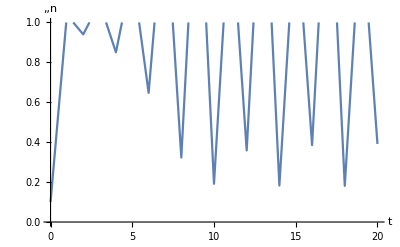

{}

```mathematica
rr=2.6;
sol=EcoSim[{n->0.1},20];
PlotDynamics[sol]
SelectValid[{sol}]
```

#### lvc

```mathematica
SetModel[lvc]
```

```mathematica
SolveEcoEq[Verbose->True]
```

{EcoEvo`Private`var_[1+t]→EcoEvo`Private`var[t],EcoEvo`Private`var_'[t]→0}

sol=Solve[{0==n1 (1-n1-0.5 n2),0==n2 (1-0.833333 (0.5 n1+n2))},{n1,n2}]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1→0,n2→0},{n1→1.,n2→0},{n1→0,n2→1.2},{n1→0.533333,n2→0.933333}}

```mathematica
eq=SolveEcoEq[]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1→0,n2→0},{n1→1.,n2→0},{n1→0,n2→1.2},{n1→0.533333,n2→0.933333}}

```mathematica
eq=SolveEcoEq[Fixed->{n2->0},Verbose->True]
```

sol=Solve[{0==(1.-n1) n1},{n1}]

{{n1→0,n2→0},{n1→1.,n2→0}}

```mathematica
SolveEcoEq[{n1}]
```

{{n1→0,n2→0},{n1→1.,n2→0}}

```mathematica
SolveEcoEq[{n1},QSS->True]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1→0,n2→n2},{n1→0.5 (2.-1. n2),n2→n2}}

```mathematica
eq=NSolveEcoEq[]
```

{{n1→0,n2→0},{n1→1.,n2→0},{n1→0,n2→1.2},{n1→0.533333,n2→0.933333}}

```mathematica
SelectValid[eq]
```

{{n1→0,n2→0},{n1→1.,n2→0},{n1→0,n2→1.2},{n1→0.533333,n2→0.933333}}

```mathematica
EcoEigenvalues[eq]
```

{{1.,1.},{-1.,0.583333},{-1.,0.4},{-1.,-0.311111}}

```mathematica
EcoStableQ[eq]
```

{False,False,False,True}

```mathematica
SelectEcoStable[eq]
```

{{n1→0.533333,n2→0.933333}}

```mathematica
EcoJacobian[eq⟦-1⟧]
```

{{-0.533333,-0.266667},{-0.388889,-0.777778}}

```mathematica
Eigensystem[EcoJacobian[eq⟦-1⟧]]
```

{{-1.,-0.311111},{{0.496139,0.868243},{0.768221,-0.640184}}}

```mathematica
FindEcoEq[{n1->0.5,n2->0.9}]
```

{n1→0.533333,n2→0.933333}

```mathematica
FindEcoEq[{n1->0.01,n2->0.9}]
```

{n1→0,n2→1.2}

```mathematica
FindEcoEq[{n2->0.9},Fixed->{n1->0}]
```

{n1→0,n2→1.2}

```mathematica
FindEcoEq[{n2->0.9},{n2}]
```

{n1→0,n2→1.2}

```mathematica
FindEcoEq[{n2->0.9}]
```

{n1→0,n2→1.2}

#### rm

```mathematica
SetModel[rm]
```

```mathematica
EcoJacobian[]//MatrixForm
```

(1-n+(n p)/(1+n)^2-p/(1+n) | -n/(1+n)
(-(2 n)/(1+n)^2+2/(1+n)) p | -1+(2 n)/(1+n))

```mathematica
eq=SolveEcoEq[]
```

{{n→0,p→0},{n→2,p→0},{n→1,p→1}}

```mathematica
SolveEcoEq[{n}]
```

{{n→0,p→0},{n→2,p→0}}

```mathematica
SolveEcoEq[{n},QSS->True]
```

{{n→0,p→p},{n→1/2 (1-√(9-8 p)),p→p},{n→1/2 (1+√(9-8 p)),p→p}}

```mathematica
SolveEcoEq[{p}]
```

{{n→0,p→0}}

```mathematica
NSolveEcoEq[]
```

{{n→0,p→0},{n→2.,p→0},{n→1.,p→1.}}

```mathematica
EcoStableQ[eq⟦-1⟧]
```

True

```mathematica
SelectEcoStable[eq]
```

{{n→1,p→1}}

```mathematica
EcoEigenvalues[eq]
```

{{-1,1},{-1,1/3},{1/8 (-1+ⅈ √15),1/8 (-1-ⅈ √15)}}

```mathematica
FindEcoEq[{n->0.9,p->1.1}]
```

{n→1.,p→1.}

```mathematica
FindEcoEq[{n->1.9}]
```

{n→2.,p→0}

```mathematica
FindEcoEq[{p->1.1}]
```

{n→0,p→0}

```mathematica
Clear[nk]
```

```mathematica
eq=SolveEcoEq[]
```

{{n→0,p→0},{n→nk,p→0},{n→1,p→(2 (-1+nk))/nk}}

```mathematica
jac=EcoJacobian[eq⟦-1⟧]
```

{{1-2/nk-(-1+nk)/(2 nk),-1/2},{(-1+nk)/nk,0}}

```mathematica
RouthHurwitzCriteria[jac]
```

Piecewise[{{True, 1-2/nk-(-1+nk)/(2 nk)<0&&1/2-1/(2 nk)>0}, {False, 1-2/nk-(-1+nk)/(2 nk)>0||1/2-1/(2 nk)<0}, {Indeterminate, True}}]

```mathematica
Simplify[RouthHurwitzCriteria[jac]]
```

Piecewise[{{True, 1<nk<3}, {False, 0<nk<1||nk>3||nk<0}, {Indeterminate, True}}]

```mathematica
EcoStableQ[eq⟦-1⟧]
```

Piecewise[{{True, 1<nk<3}, {False, 0<nk<1||nk>3||nk<0}, {Indeterminate, True}}]

```mathematica
Clear[an,apred,h,mp,nk]
```

```mathematica
eq=SolveEcoEq[]
```

{{n→0,p→0},{n→nk,p→0},{n→(h mp)/(apred-mp),p→(apred h (-h mp+apred nk-mp nk))/(an (apred-mp)^2 nk)}}

```mathematica
EcoStableQ[eq⟦-1⟧]
```

Piecewise[{{True, apred (apred-mp) mp nk (apred (h-nk)+mp (h+nk))>0&&apred mp nk (-h mp+(apred-mp) nk)>0}, {False, apred mp nk (-h mp+(apred-mp) nk)<0||apred (apred-mp) mp nk (apred (h-nk)+mp (h+nk))<0}, {Indeterminate, True}}]

```mathematica
EcoStableQ[eq⟦-1⟧,Assumptions->{an>0,apred>0,h>0,mp>0,nk>0,apred>mp}]
```

Piecewise[{{True, apred h+mp (h+nk)>apred nk&&apred nk>mp (h+nk)}, {False, apred h+mp (h+nk)<apred nk||apred nk<mp (h+nk)}, {Indeterminate, True}}]

```mathematica
SolveEcoEq[{n}]
```

{{n→0,p→0},{n→nk,p→0}}

```mathematica
SolveEcoEq[{n},QSS->True]
```

{{n→0,p→p},{n→1/2 (-h+nk-√(h^2+2 h nk+nk^2-4 an nk p)),p→p},{n→1/2 (-h+nk+√(h^2+2 h nk+nk^2-4 an nk p)),p→p}}

```mathematica
an=1;
apred=2;
h=1;
mp=1;
nk=2;
EcoStableQ[eq⟦-1⟧]
```

True

```mathematica
EcoStableQ[eq⟦-1⟧,Tolerance->-10,Method->"Eigenvalues"]
```

False

#### fl

```mathematica
SetModel[fl]
```

```mathematica
eq=SolveEcoEq[]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{b1→0,b2→0,R→20.},{b1→(5. (-21.+100. (Piecewise[{{1., Mod[t,365.]<219.}, {0, True}}])))/(-1.+5. (Piecewise[{{1., Mod[t,365.]<219.}, {0, True}}])),b2→0,R→1/(-1.+5. (Piecewise[{{1., Mod[t,365.]<219.}, {0, True}}]))},{b1→0,b2→(20. (-6.+25. (Piecewise[{{2., Mod[t,365.]<219.}, {0, True}}])))/(-1.+5. (Piecewise[{{2., Mod[t,365.]<219.}, {0, True}}])),R→4./(-1.+5. (Piecewise[{{2., Mod[t,365.]<219.}, {0, True}}]))}}

```mathematica
NSolveEcoEq[]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{b1→0,b2→0,R→20.},{b1→(5. (-21.+100. (Piecewise[{{1., Mod[t,365.]<219.}, {0, True}}])))/(-1.+5. (Piecewise[{{1., Mod[t,365.]<219.}, {0, True}}])),b2→0,R→1/(-1.+5. (Piecewise[{{1., Mod[t,365.]<219.}, {0, True}}]))},{b1→0,b2→(20. (-6.+25. (Piecewise[{{2., Mod[t,365.]<219.}, {0, True}}])))/(-1.+5. (Piecewise[{{2., Mod[t,365.]<219.}, {0, True}}])),R→4./(-1.+5. (Piecewise[{{2., Mod[t,365.]<219.}, {0, True}}]))}}

```mathematica
FindEcoEq[{b1->10,b2->10,R->1}]
```

EcoEq::noneq: Can't find equilibrium of periodically forced model with FindRoot.  Give Time option or try FindEcoCycle instead.

```mathematica
FindEcoEq[{b1->10,b2->10,R->1},Time->0]
```

{b1→0,b2→97.7778,R→0.444444}

```mathematica
FindEcoEq[{b1->10,b2->10,R->1},Time->290]
```

{b1→0,b2→0,R→20.}

```mathematica
EcoJacobian[]
```

{{-0.2+(R (Piecewise[{{1, Mod[t,365]<219.}, {0, True}}]))/(1+R),0,b1 (-(R (Piecewise[{{1, Mod[t,365]<219.}, {0, True}}]))/(1+R)^2+Piecewise[{{1, Mod[t,365]<219.}, {0, True}}]/(1+R))},{0,-0.2+(R (Piecewise[{{2, Mod[t,365]<219.}, {0, True}}]))/(4+R),b2 (-(R (Piecewise[{{2, Mod[t,365]<219.}, {0, True}}]))/(4+R)^2+Piecewise[{{2, Mod[t,365]<219.}, {0, True}}]/(4+R))},{-(R (Piecewise[{{1, Mod[t,365]<219.}, {0, True}}]))/(1+R),-(R (Piecewise[{{2, Mod[t,365]<219.}, {0, True}}]))/(4+R),-1+(b1 R (Piecewise[{{1, Mod[t,365]<219.}, {0, True}}]))/(1+R)^2-(b1 (Piecewise[{{1, Mod[t,365]<219.}, {0, True}}]))/(1+R)+(b2 R (Piecewise[{{2, Mod[t,365]<219.}, {0, True}}]))/(4+R)^2-(b2 (Piecewise[{{2, Mod[t,365]<219.}, {0, True}}]))/(4+R)}}

#### twop

```mathematica
Clear[disp]
```

```mathematica
SetModel[twop]
```

```mathematica
SolveEcoEq[]
```

{{p1→0,p2→0},{p1→1,p2→1},{p1→1/2 (1-2 disp+√(1-2 disp^2)),p2→(disp-disp^2-disp √(1-2 disp^2))/(2 disp)},{p1→1/2 (1-2 disp-√(1-2 disp^2)),p2→(disp-disp^2+disp √(1-2 disp^2))/(2 disp)}}

```mathematica
NSolveEcoEq[]
```

{{p1→0,p2→0},{p1→1.,p2→1.},{p1→0.5 (1.-2. disp+√(1.-2. disp^2)),p2→(0.5 (disp-1. disp^2-1. disp √(1.-2. disp^2)))/disp},{p1→0.5 (1.-2. disp-1. √(1.-2. disp^2)),p2→(0.5 (disp-1. disp^2+disp √(1.-2. disp^2)))/disp}}

```mathematica
disp=0.1;
eq=SolveEcoEq[]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p1→0,p2→0},{p1→-0.0949747,p2→0.944975},{p1→0.894975,p2→-0.0449747},{p1→1.,p2→1.}}

```mathematica
SelectValid[eq]
```

{{p1→0,p2→0},{p1→1.,p2→1.}}

```mathematica
EcoEigenvalues[eq]
```

{{1.9099,0.890098},{-1.88326,1.09331},{2.08326,-0.893313},{-2.1099,-1.0901}}

```mathematica
SelectEcoStable[eq]
```

{{p1→1.,p2→1.}}

```mathematica
FindEcoEq[{p1->0.1,p2->0.4}]
```

{p1→0,p2→0}

```mathematica
FindEcoEq[{p1->0.9,p2->0.4}]
```

{p1→0.894975,p2→-0.0449747}

```mathematica
FindEcoEq[{p1->0.9,p2->0.4},BoundaryDetection->True]
```

FindRoot::reged: The point {0.865904,0.} is at the edge of the search region {0.,∞} in coordinate 2 and the computed search direction points outside the region.

{p1→0.865904,p2→0}

#### dl

```mathematica
SetModel[dl]
```

```mathematica
eq=SolveEcoEq[]
```

{{j→0,a→0}}

```mathematica
NSolveEcoEq[]
```

{{j→0,a→0}}

```mathematica
SelectValid[eq]
```

{{j→0,a→0}}

```mathematica
EcoEigenvalues[eq]
```

{{1.28078,-0.780776}}

```mathematica
EcoStableQ[eq⟦1⟧]
```

False

```mathematica
SelectEcoStable[eq]
```

{}

```mathematica
FindEcoEq[{a->0.1,j->0.1}]
```

{j→0,a→0}

#### lv

```mathematica
SetModel[lv]
```

```mathematica
EcoJacobian[{Nsp[n]->1}]
```

{{1-(2 n_1)/(1-x_1^2)}}

```mathematica
EcoJacobian[{Nsp[n]->2}]
```

{{1-n_1/(1-x_1^2)-(n_1+ⅇ^(-2 (x_1-x_2)^2) n_2)/(1-x_1^2),-(ⅇ^(-2 (x_1-x_2)^2) n_1)/(1-x_1^2)},{-(ⅇ^(-2 (-x_1+x_2)^2) n_2)/(1-x_2^2),1-n_2/(1-x_2^2)-(ⅇ^(-2 (-x_1+x_2)^2) n_1+n_2)/(1-x_2^2)}}

```mathematica
EcoJacobian[{Subscript[x, 1]->0}]
```

{{1-2 n_1}}

```mathematica
EcoJacobian[{Subscript[x, 1]->0,Subscript[x, 2]->0.5}]//MatrixForm
```

(1-2 n_1-0.606531 n_2 | -0.606531 n_1
-0.808708 n_2 | 1-1.33333 n_2-1.33333 (0.606531 n_1+n_2))

```mathematica
SelectValid[{{Subscript[n, 1]->0},{Subscript[n, 1]->1},{Subscript[n, 1]->-1},{Subscript[n, 1]->1,Subscript[n, 2]->1},{Subscript[x, 1]->0.5,Subscript[n, 1]->1}}]
```

{{n_1→0},{n_1→1},{n_1→1,n_2→1},{x_1→0.5,n_1→1}}

```mathematica
SolveEcoEq[{Nsp[n]->1}]
```

{{n_1→0},{n_1→1-x_1^2}}

```mathematica
eq=SolveEcoEq[{Subscript[x, 1]->0}]
```

{{n_1→0},{n_1→1}}

```mathematica
SelectValid[eq]
```

{{n_1→0},{n_1→1}}

```mathematica
traits={Subscript[x, 1]->0,Subscript[x, 2]->0.2};
eq=SolveEcoEq[traits]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n_1→0,n_2→0},{n_1→1.,n_2→0},{n_1→0,n_2→0.96},{n_1→0.769723,n_2→0.249456}}

```mathematica
EcoStableQ[traits,eq⟦-1⟧]
```

True

```mathematica
EcoStableQ[Join[traits,eq⟦-1⟧]]
```

True

```mathematica
NSolveEcoEq[traits]
```

{{n_1→0,n_2→0},{n_1→1.,n_2→0},{n_1→0,n_2→0.96},{n_1→0.769723,n_2→0.249456}}

```mathematica
SelectValid[eq]
```

{{n_1→0,n_2→0},{n_1→1.,n_2→0},{n_1→0,n_2→0.96},{n_1→0.769723,n_2→0.249456}}

```mathematica
EcoJacobian[traits,eq⟦-1⟧]
```

{{-0.769723,-0.710544},{-0.239872,-0.25985}}

```mathematica
EcoEigenvalues[traits,eq⟦-1⟧]
```

{-1.,-0.0295731}

```mathematica
EcoEigenvalues[traits,eq]
```

{{1.,1.},{-1.,0.0384205},{-1.,0.113808},{-1.,-0.0295731}}

```mathematica
EcoStableQ[traits,eq]
```

{False,False,False,True}

```mathematica
SelectEcoStable[traits,eq]
```

{{n_1→0.769723,n_2→0.249456}}

```mathematica
eq=SolveEcoEq[{Subscript[x, 1]->0,Subscript[x, 2]->0.01,Subscript[x, 3]->0.02}]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{1.,0.,0.,0.},{0.,1.,0.,0.},{4.01652×10^14,4.01893×10^14,4.01973×10^14,-4.01973×10^14}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{1.,0.,0.,0.},{1.4998×10^8,1.5001×10^8,1.4998×10^8,-1.49995×10^8},{4.01652×10^14,4.01893×10^14,4.01973×10^14,-4.01973×10^14}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.,1.,0.,0.},{0.,0.,1.,0.},{4.01973×10^14,4.01893×10^14,4.01652×10^14,-4.01812×10^14}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n_1→0,n_2→0,n_3→0},{n_1→1.,n_2→0,n_3→0},{n_1→0,n_2→0.9999,n_3→0},{n_1→0.75005,n_2→0.25,n_3→0},{n_1→0,n_2→0,n_3→0.9996},{n_1→0.7502,n_2→0,n_3→0.25},{n_1→0,n_2→1.25,n_3→-0.25015},{n_1→625.25,n_2→-1248.75,n_3→624.75}}

```mathematica
SelectValid[eq]
```

{{n_1→0,n_2→0,n_3→0},{n_1→1.,n_2→0,n_3→0},{n_1→0,n_2→0.9999,n_3→0},{n_1→0.75005,n_2→0.25,n_3→0},{n_1→0,n_2→0,n_3→0.9996},{n_1→0.7502,n_2→0,n_3→0.25}}

```mathematica
SolveEcoEq[{Subscript[x, 1]->0,Subscript[x, 2]->0.2},Fixed->{Subscript[n, 1]->0}]
```

{{n_1→0,n_2→0},{n_1→0,n_2→0.96}}

```mathematica
SolveEcoEq[{Subscript[x, 1]->0,Subscript[x, 2]->0.2},{Subscript[n, 2]}]
```

{{n_1→0,n_2→0},{n_1→0,n_2→0.96}}

```mathematica
FindEcoEq[{Subscript[x, 1]->-0.1,Subscript[x, 2]->0.2},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.9}]
```

{n_1→0,n_2→0.96}

```mathematica
FindEcoEq[{Subscript[x, 1]->-0.1,Subscript[x, 2]->0.2},{Subscript[n, 1]->0.6,Subscript[n, 2]->0.4}]
```

{n_1→0.622315,n_2→0.440199}

```mathematica
FindEcoEq[{Subscript[x, 1]->-0.1,Subscript[x, 2]->0.2},{Subscript[n, 1]->0.6}]
```

{n_1→0.99,n_2→0}

```mathematica
FindEcoEq[{Subscript[x, 1]->-0.1,Subscript[x, 2]->0.2},{Subscript[n, 2]->0.9}]
```

{n_1→0,n_2→0.96}

#### si

```mathematica
SetModel[si]
```

```mathematica
SolveEcoEq[{Subscript[B, 1]->0}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{s_1→0,i_1→0},{s_1→15.3333,i_1→0}}

```mathematica
traits={Subscript[B, 1]->0,Subscript[B, 2]->0.5};
eq=SolveEcoEq[traits]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{s_1→0,i_1→0,s_2→0,i_2→0},{s_1→15.3333,i_1→0,s_2→0,i_2→0},{s_1→0,i_1→0,s_2→18.25,i_2→0},{s_1→0,i_1→0,s_2→0.56,i_2→-1.24545},{s_1→0,i_1→0,s_2→0.56,i_2→10.6054},{s_1→14.3067,i_1→0,s_2→0.56,i_2→0.466667}}

```mathematica
NSolveEcoEq[traits]
```

{{s_1→0,i_1→0,s_2→0,i_2→0},{s_1→15.3333,i_1→0,s_2→0,i_2→0},{s_1→0,i_1→0,s_2→18.25,i_2→0},{s_1→0,i_1→0,s_2→0.56,i_2→-1.24545},{s_1→0,i_1→0,s_2→0.56,i_2→10.6054},{s_1→14.3067,i_1→0,s_2→0.56,i_2→0.466667}}

```mathematica
val=SelectValid[eq]
```

{{s_1→0,i_1→0,s_2→0,i_2→0},{s_1→15.3333,i_1→0,s_2→0,i_2→0},{s_1→0,i_1→0,s_2→18.25,i_2→0},{s_1→0,i_1→0,s_2→0.56,i_2→10.6054},{s_1→14.3067,i_1→0,s_2→0.56,i_2→0.466667}}

```mathematica
EcoJacobian[traits,val⟦-1⟧]
```

{{-0.2146,-0.1621,-0.2146,-0.2146},{0,-0.28,0,0},{-0.0364,-0.3164,-0.153067,-0.1764},{0,0.28,0.233333,5.55112×10^-17}}

```mathematica
EcoEigenvalues[traits,val]
```

{{0.73,-0.28,-0.28,0.23},{-0.28,-0.28,-0.23,0.116667},{8.845,-0.73,-0.28,-0.04375},{-4.98145,-0.378456,-0.28,0.0625183},{-0.28,-0.211396,-0.0781351+0.164489 ⅈ,-0.0781351-0.164489 ⅈ}}

```mathematica
SelectEcoStable[traits,val]
```

{{s_1→14.3067,i_1→0,s_2→0.56,i_2→0.466667}}

```mathematica
FindEcoEq[{Subscript[B, 1]->0.1},{Subscript[i, 1]->0.1,Subscript[s, 1]->10}]
```

{s_1→16.5,i_1→0}

#### ch

```mathematica
SetModel[ch]
```

```mathematica
eq=SolveEcoEq[{Subscript[mu, 1]->0.25}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n_1→0,R→1.},{n_1→49.7283,R→0.00543478}}

```mathematica
NSolveEcoEq[{Subscript[mu, 1]->0.25}]
```

{{n_1→0,R→1.},{n_1→49.7283,R→0.00543478}}

```mathematica
EcoEigenvalues[{Subscript[mu, 1]->0.25},eq]
```

{{-1.,0.215294},{-169.34,-0.0198842}}

```mathematica
SelectEcoStable[{Subscript[mu, 1]->0.25},eq]
```

{{n_1→49.7283,R→0.00543478}}

```mathematica
traits={Subscript[mu, 1]->0.25,Subscript[mu, 2]->0.5};
```

```mathematica
eq=SolveEcoEq[traits]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n_1→0,n_2→0,R→1.},{n_1→49.7283,n_2→0,R→0.00543478},{n_1→0,n_2→49.4792,R→0.0104167}}

```mathematica
EcoStableQ[traits,eq]
```

{False,True,False}

```mathematica
SelectEcoStable[traits,eq]
```

{{n_1→49.7283,n_2→0,R→0.00543478}}

```mathematica
SolveEcoEq[]
```

{{R→1}}

```mathematica
FindEcoEq[{Subscript[mu, 1]->0.25},{R->0,Subscript[n, 1]->40}]
```

{n_1→49.7283,R→0.00543478}

```mathematica
FindEcoEq[{R->0}]
```

{R→1.}

#### pp

```mathematica
SetModel[pp]
```

```mathematica
traits={Subscript[xn, 1]->0.5,Subscript[xn, 2]->0.7,Subscript[xp, 1]->0,Subscript[xp, 2]->0.2};
```

```mathematica
SolveEcoEq[traits]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{1.,0.,0.,0.,0.},{0.,0.,1.,0.,0.},{0.,0.,0.,1.,0.},{0.,0.,2.02511×10^17,2.28331×10^17,-5.17465×10^15}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{1.,0.,0.,0.,0.},{0.,0.,2.02511×10^17,2.28331×10^17,-5.17465×10^15},{«22»,«4»},{4.97057×10^25,4.4085×10^25,1.10439×10^26,1.01948×10^26,-5.63239×10^25}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.,1.,0.,0.,0.},{0.,0.,1.,0.,0.},{0.,0.,0.,1.,0.},{0.,0.,4.14612×10^16,4.49144×10^16,-9.39634×10^14}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{p_2→1.04603-1.3947 n_1-1.28747 n_2-0.923116 p_1},{p_2→1.13315-2.05104 n_1-2.22186 n_2-0.88692 p_1},{n_2→0.0255524-1.1275 n_1,p_2→0},{n_2→0.022663-1.08329 n_1,p_1→0},{n_1→0.0653579,n_2→-0.0481384},{p_1→-2.40692+18.1327 n_1+25.8147 n_2,p_2→3.26789-18.1333 n_1-25.1174 n_2},{n_2→0.022663-1.08329 n_1,p_2→1.01685-0.923116 p_1},{n_2→0.0255524-1.1275 n_1,p_2→1.01313+0.0569189 n_1-0.923116 p_1},{n_2→0.022663-1.08329 n_1,p_2→1.08279+0.355877 n_1-0.88692 p_1},{n_2→0.0255524-1.1275 n_1,p_2→1.07637+0.454105 n_1-0.88692 p_1},{n_2→0.022663-1.08329 n_1,p_1→-1.82188-9.83196 n_1,p_2→2.69866+9.07605 n_1},{n_2→0.0255524-1.1275 n_1,p_1→-1.74729-10.9732 n_1,p_2→2.62608+10.1865 n_1},{n_1→0.0653579,n_2→-0.0481384,p_2→1.01685-0.923116 p_1},{n_1→0.0653579,n_2→-0.0481384,p_2→1.10605-0.88692 p_1},{n_1→0,n_2→0,p_1→0,p_2→0},{n_1→0.0653579,n_2→-0.0481384,p_1→-2.46448,p_2→3.29185}}

```mathematica
NSolveEcoEq[traits]
```

{{n_1→0,n_2→0,p_1→0,p_2→0},{n_1→0.75,n_2→0,p_1→0,p_2→0},{n_1→0,n_2→0.51,p_1→0,p_2→0},{n_1→1.88839,n_2→-1.23321,p_1→0,p_2→0},{n_1→0.022663,n_2→0,p_1→1.09891,p_2→0},{n_1→0,n_2→0.0255524,p_1→1.21361,p_2→0},{n_1→-0.257801,n_2→0.316222,p_1→1.08161,p_2→0},{n_1→0.0209206,n_2→0,p_1→0,p_2→1.01685},{n_1→0,n_2→0.022663,p_1→0,p_2→1.08279},{n_1→-0.185302,n_2→0.223398,p_1→0,p_2→1.01685},{n_1→0.0653579,n_2→-0.0481384,p_1→-2.46448,p_2→3.29185}}

```mathematica
eq=SolveEcoEq[traits,SolveOpts->{Reals}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n_1→0,n_2→0,p_1→0,p_2→0},{n_1→0.75,n_2→0,p_1→0,p_2→0},{n_1→0,n_2→0.51,p_1→0,p_2→0},{n_1→1.88839,n_2→-1.23321,p_1→0,p_2→0},{n_1→0.022663,n_2→0,p_1→1.09891,p_2→0},{n_1→0,n_2→0.0255524,p_1→1.21361,p_2→0},{n_1→-0.257801,n_2→0.316222,p_1→1.08161,p_2→0},{n_1→0.0209206,n_2→0,p_1→0,p_2→1.01685},{n_1→0,n_2→0.022663,p_1→0,p_2→1.08279},{n_1→-0.185302,n_2→0.223398,p_1→0,p_2→1.01685},{n_1→0.0653579,n_2→-0.0481384,p_1→-2.46448,p_2→3.29185}}

```mathematica
val=SelectValid[eq]
```

{{n_1→0,n_2→0,p_1→0,p_2→0},{n_1→0.75,n_2→0,p_1→0,p_2→0},{n_1→0,n_2→0.51,p_1→0,p_2→0},{n_1→0.022663,n_2→0,p_1→1.09891,p_2→0},{n_1→0,n_2→0.0255524,p_1→1.21361,p_2→0},{n_1→0.0209206,n_2→0,p_1→0,p_2→1.01685},{n_1→0,n_2→0.022663,p_1→0,p_2→1.08279}}

```mathematica
EcoEigenvalues[traits,val]
```

{{1.,1.,-0.02,-0.02},{-1.,0.696998,0.641873,-0.357524},{-1.,0.430073,0.379179,0.372281},{-0.0151086+0.138446 ⅈ,-0.0151086-0.138446 ⅈ,0.0988592,0.00166574},{-0.0250514+0.135537 ⅈ,-0.0250514-0.135537 ⅈ,-0.102457,0.00254994},{-0.013947+0.138736 ⅈ,-0.013947-0.138736 ⅈ,0.0647663,-0.00153767},{-0.0222186+0.136446 ⅈ,-0.0222186-0.136446 ⅈ,-0.0630429,-0.00226159}}

```mathematica
EcoStableQ[traits,val]
```

{False,False,False,False,False,False,True}

```mathematica
EcoEigenvalues[traits,val]
```

{{1.,1.,-0.02,-0.02},{-1.,0.696998,0.641873,-0.357524},{-1.,0.430073,0.379179,0.372281},{-0.0151086+0.138446 ⅈ,-0.0151086-0.138446 ⅈ,0.0988592,0.00166574},{-0.0250514+0.135537 ⅈ,-0.0250514-0.135537 ⅈ,-0.102457,0.00254994},{-0.013947+0.138736 ⅈ,-0.013947-0.138736 ⅈ,0.0647663,-0.00153767},{-0.0222186+0.136446 ⅈ,-0.0222186-0.136446 ⅈ,-0.0630429,-0.00226159}}

```mathematica
SelectEcoStable[traits,val]
```

{{n_1→0,n_2→0.022663,p_1→0,p_2→1.08279}}

```mathematica
SolveEcoEq[traits,SolveOpts->{Reals},Fixed->{Subscript[p, 2]->0}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n_1→0,n_2→0,p_1→0,p_2→0},{n_1→0.75,n_2→0,p_1→0,p_2→0},{n_1→0,n_2→0.51,p_1→0,p_2→0},{n_1→1.88839,n_2→-1.23321,p_1→0,p_2→0},{n_1→0.022663,n_2→0,p_1→1.09891,p_2→0},{n_1→0,n_2→0.0255524,p_1→1.21361,p_2→0},{n_1→-0.257801,n_2→0.316222,p_1→1.08161,p_2→0}}

```mathematica
SolveEcoEq[{Subscript[xn, 1]->Subscript[xn, 1],Subscript[xp, 1]->Subscript[xp, 1]}]
```

{{n_1→0,p_1→0},{n_1→1.-1. xn_1^2,p_1→0},{n_1→0.02 ⅇ^(0.5 (xn_1-1. xp_1)^2),p_1→(0.02 (-50. ⅇ^(0.5 (xn_1-1. xp_1)^2)+1. ⅇ^(1. (xn_1-1. xp_1)^2)+50. ⅇ^(0.5 (xn_1-1. xp_1)^2) xn_1^2))/(-1.+1. xn_1^2)}}

```mathematica
SolveEcoEq[{Nsp[prey]->1,Nsp[pred]->1}]
```

{{n_1→0,p_1→0},{n_1→1.-1. xn_1^2,p_1→0},{n_1→0.02 ⅇ^(0.5 (xn_1-1. xp_1)^2),p_1→(0.02 (-50. ⅇ^(0.5 (xn_1-1. xp_1)^2)+1. ⅇ^(1. (xn_1-1. xp_1)^2)+50. ⅇ^(0.5 (xn_1-1. xp_1)^2) xn_1^2))/(-1.+1. xn_1^2)}}

```mathematica
FindEcoEq[traits,{Subscript[n, 1]->0.05,Subscript[n, 2]->0,Subscript[p, 1]->1,Subscript[p, 2]->0}]
```

{n_1→0.022663,n_2→0,p_1→1.09891,p_2→0}

#### lv2

```mathematica
SetModel[lv2]
```

```mathematica
SolveEcoEq[{Subscript[x, 1]->-0.25,Subscript[y, 1]->0.1,Subscript[x, 2]->0.25,Subscript[y, 2]->0}]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{1.,0.,0.},{1.30364×10^10,2.19275×10^10,-2.03378×10^10}} may contain significant numerical errors.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n_1→0,n_2→0},{n_1→0.9275,n_2→0},{n_1→0,n_2→0.9375},{n_1→0.572484,n_2→0.597146}}

```mathematica
FindEcoEq[{Subscript[x, 1]->-0.25,Subscript[y, 1]->0.1,Subscript[x, 2]->0.25,Subscript[y, 2]->0},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5}]
```

{n_1→0.572484,n_2→0.597146}

```mathematica
traits={Subscript[x, 1]->0.25,Subscript[y, 1]->0.1,Subscript[x, 2]->0.25,Subscript[y, 2]->0,Subscript[x, 3]->0.26,Subscript[y, 3]->0};
```

```mathematica
eq=SolveEcoEq[traits,SolveOpts->{Reals}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n_1→0,n_2→0,n_3→0},{n_1→0.9275,n_2→0,n_3→0},{n_1→0,n_2→0.9375,n_3→0},{n_1→0.218404,n_2→0.723421,n_3→0},{n_1→0,n_2→0,n_3→0.9324},{n_1→0.347155,n_2→0,n_3→0.592187},{n_1→0,n_2→13.2188,n_3→-12.2838},{n_1→0.218404,n_2→13.0047,n_3→-12.2838}}

```mathematica
SelectValid[eq]
```

{{n_1→0,n_2→0,n_3→0},{n_1→0.9275,n_2→0,n_3→0},{n_1→0,n_2→0.9375,n_3→0},{n_1→0.218404,n_2→0.723421,n_3→0},{n_1→0,n_2→0,n_3→0.9324},{n_1→0.347155,n_2→0,n_3→0.592187}}

```mathematica
EcoEigenvalues[traits,eq]
```

{{0.9375,0.9324,0.9275},{-0.9275,0.0283657,0.0234475},{-0.9375,0.00856374,-0.00491252},{-0.9352,-0.00662445,-0.00491252},{-0.9324,0.0137455,0.00528646},{-0.930595,-0.00874701,0.00515038},{-0.999982,0.0649387,0.00856374},{-0.997697,0.0665665,-0.00823787}}

```mathematica
SelectEcoStable[traits,eq]
```

{{n_1→0.218404,n_2→0.723421,n_3→0}}

#### droop

```mathematica
SetModel[droop]
```

```mathematica
SolveEcoEq[{Subscript[a1, 1]->0.26}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{b_1→0,q_1→1.12381,r1→20.},{b_1→985.83,q_1→1.0101,r1→0.084246}}

```mathematica
traits={Subscript[a1, 1]->0.26,Subscript[a1, 2]->0.28};
```

```mathematica
eq=SolveEcoEq[traits]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{b_1→0,q_1→1.12381,b_2→0,q_2→1.13333,r1→20.},{b_1→985.83,q_1→1.0101,b_2→0,q_2→1.01088,r1→0.084246},{b_1→0,q_1→1.00938,b_2→986.151,q_2→1.0101,r1→0.0777605}}

```mathematica
SelectValid[eq]
```

{{b_1→0,q_1→1.12381,b_2→0,q_2→1.13333,r1→20.},{b_1→985.83,q_1→1.0101,b_2→0,q_2→1.01088,r1→0.084246},{b_1→0,q_1→1.00938,b_2→986.151,q_2→1.0101,r1→0.0777605}}

```mathematica
EcoEigenvalues[traits,eq]
```

{{-2.,-2.,-1.,0.215294,0.200339},{-219.032,-2.,-1.97991,-0.0199096,0.00152191},{-238.715,-2.,-1.97992,-0.019917,-0.0014153}}

```mathematica
SelectEcoStable[traits,eq]
```

{{b_1→0,q_1→1.00938,b_2→986.151,q_2→1.0101,r1→0.0777605}}

```mathematica
SolveEcoEq[{Subscript[a1, 1]->0.26},Fixed->{Subscript[b, 1]->0}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{b_1→0,q_1→1.12381,r1→20.}}

```mathematica
FindEcoEq[{Subscript[a1, 1]-> 0.26},{r1->0.08,Subscript[b, 1]->985,Subscript[q, 1]->1}]
```

{b_1→985.83,q_1→1.0101,r1→0.084246}

```mathematica
FindEcoEq[{Subscript[a1, 1]-> 0.26},{r1->20,Subscript[q, 1]->1},Fixed->{Subscript[b, 1]->0}]
```

{b_1→0,q_1→1.12381,r1→20.}

```mathematica
FindEcoEq[{Subscript[a1, 1]-> 0.26},{r1->20,Subscript[q, 1]->1}]
```

{b_1→0,q_1→1.12381,r1→20.}

#### dlv

```mathematica
SetModel[dlv]
```

```mathematica
SolveEcoEq[{Subscript[x, 1]->0}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n_1→0},{n_1→1}}

```mathematica
eq=SolveEcoEq[{Subscript[x, 1]->0,Subscript[x, 2]->0.5}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n_1→0,n_2→0.75},{n_1→0.862339,n_2→0.226965}}

```mathematica
SelectValid[eq]
```

{{n_1→0,n_2→0.75},{n_1→0.862339,n_2→0.226965}}

```mathematica
EcoEigenvalues[{Subscript[x, 1]->0,Subscript[x, 2]->0.5},eq]
```

{{1.72478,0},{0.835041,0}}

```mathematica
SelectEcoStable[{Subscript[x, 1]->0,Subscript[x, 2]->0.5},eq]
```

{{n_1→0.862339,n_2→0.226965}}

```mathematica
FindEcoEq[{Subscript[x, 1]->0},{Subscript[n, 1]->0.9}]
```

{n_1→1.}

```mathematica
FindEcoEq[{Subscript[x, 1]->0},{Subscript[n, 1]->0.1}]
```

{n_1→0}

```mathematica
FindEcoEq[{Subscript[x, 1]->0,Subscript[x, 2]->0.5},{Subscript[n, 1]->0.6,Subscript[n, 2]->0.3}]
```

{n_1→0.862339,n_2→0.226965}

#### jon

```mathematica
SetModel[jon]
```

```mathematica
eq=SolveEcoEq[{Subscript[x, 1]->15}]
```

{{c_1→0},{c_1→1.-0.0333333 ⅇ^(5.76 Sin[0.0172142 t]^2)}}

```mathematica
NSolveEcoEq[{Subscript[x, 1]->15}]
```

{{c_1→0},{c_1→1.-0.0333333 2.71828^(5.76 Sin[0.0172142 t]^2)}}

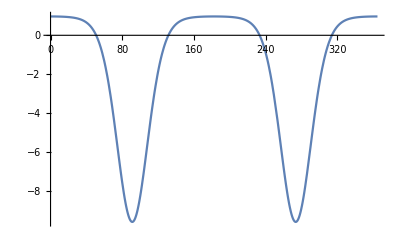

```mathematica
Plot[Subscript[c, 1]/.eq⟦2⟧,{t,0,365}]
```

```mathematica
SolveEcoEq[{Subscript[x, 1]->15},Time->130]
```

{{c_1→0},{c_1→-0.166652}}

```mathematica
SolveEcoEq[{Subscript[x, 1]->15},Time->130]
```

{{c_1→0},{c_1→-0.166652}}

```mathematica
FindEcoEq[{Subscript[x, 1]->15},{Subscript[c, 1]->10}]
```

EcoEq::noneq: Can't find equilibrium of periodically forced model with FindRoot.  Give Time option or try FindEcoCycle instead.

```mathematica
FindEcoEq[{Subscript[x, 1]->15},{Subscript[c, 1]->10},Time->0]
```

{c_1→0.966667}

```mathematica
FindEcoEq[{Subscript[x, 1]->10,Subscript[x, 2]->20},{Subscript[c, 1]->1,Subscript[c, 2]->1},Time->290]
```

{c_1→0.963379,c_2→0}

#### mc

```mathematica
SetModel[mc]
```

```mathematica
eq=SolveEcoEq[{Subscript[dd, 1]->0.1},Time->1,Verbose->True]
```

sol=Solve[{0==0.1 p1_1-p1_1^2+0.1 (-p1_1+p2_1),0==0.1 (p1_1-p2_1)+0.1 p2_1-p2_1^2},{p1_1,p2_1}]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p1_1→0,p2_1→0},{p1_1→-0.05-0.0866025 ⅈ,p2_1→-0.05+0.0866025 ⅈ},{p1_1→-0.05+0.0866025 ⅈ,p2_1→-0.05-0.0866025 ⅈ},{p1_1→0.1,p2_1→0.1}}

```mathematica
valid=SelectValid[eq]
```

{{p1_1→0,p2_1→0},{p1_1→0.1,p2_1→0.1}}

```mathematica
EcoEigenvalues[{Subscript[dd, 1]->0.1},valid,Time->1]
```

{{-0.1,0.1},{-0.3,-0.1}}

```mathematica
EcoStableQ[{Subscript[dd, 1]->0.1},valid⟦1⟧,Time->1,Verbose->True]
```

EcoStableQ: method=Eigenvalues

EcoStableQ: evs={-0.1,0.1}

False

```mathematica
SelectEcoStable[{Subscript[dd, 1]->0.1},valid,Time->1]
```

{{p1_1→0.1,p2_1→0.1}}

```mathematica
SolveEcoEq[{Subscript[dd, 1]->0.1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p1_1→0,p2_1→0},{p1_1→0.666667 Sin[6.28319 t]+((2.09987×10^-6+3.63708×10^-6 ⅈ) (300000. Sin[6.28319 t]-1.×10^6 Sin[6.28319 t]^2))/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3)-(0.0132283-0.0229122 ⅈ) (27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3),p2_1→-0.666667 Sin[6.28319 t]-((7.93701-13.7473 ⅈ) Sin[6.28319 t]^2)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(2/3)+((52.9134-91.6486 ⅈ) Sin[6.28319 t]^3)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(2/3)-((88.1889-152.748 ⅈ) Sin[6.28319 t]^4)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(2/3)+((2.09987+3.63708 ⅈ) Sin[6.28319 t]^2)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3)-((6.99956+12.1236 ⅈ) Sin[6.28319 t]^3)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3)-(0.0440945-0.0763739 ⅈ) Sin[6.28319 t] (27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3)-(0.00349978+0.0060618 ⅈ) (27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(2/3)},{p1_1→0.666667 Sin[6.28319 t]+((2.09987×10^-6-3.63708×10^-6 ⅈ) (300000. Sin[6.28319 t]-1.×10^6 Sin[6.28319 t]^2))/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3)-(0.0132283+0.0229122 ⅈ) (27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3),p2_1→-0.666667 Sin[6.28319 t]-((7.93701+13.7473 ⅈ) Sin[6.28319 t]^2)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(2/3)+((52.9134+91.6486 ⅈ) Sin[6.28319 t]^3)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(2/3)-((88.1889+152.748 ⅈ) Sin[6.28319 t]^4)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(2/3)+((2.09987-3.63708 ⅈ) Sin[6.28319 t]^2)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3)-((6.99956-12.1236 ⅈ) Sin[6.28319 t]^3)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3)-(0.0440945+0.0763739 ⅈ) Sin[6.28319 t] (27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3)-(0.00349978-0.0060618 ⅈ) (27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(2/3)},{p1_1→0.666667 Sin[6.28319 t]-(4.19974×10^-6 (300000. Sin[6.28319 t]-1.×10^6 Sin[6.28319 t]^2))/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3)+0.0264567 (27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3),p2_1→-0.666667 Sin[6.28319 t]+(15.874 Sin[6.28319 t]^2)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(2/3)-(105.827 Sin[6.28319 t]^3)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(2/3)+(176.378 Sin[6.28319 t]^4)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(2/3)-(4.19974 Sin[6.28319 t]^2)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3)+(13.9991 Sin[6.28319 t]^3)/(27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3)+0.0881889 Sin[6.28319 t] (27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(1/3)+0.00699956 (27.+900. Sin[6.28319 t]^2-2000. Sin[6.28319 t]^3+5.19615 √(27.+1800. Sin[6.28319 t]^2-10000. Sin[6.28319 t]^4))^(2/3)}}

```mathematica
FindEcoEq[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.09,Subscript[p2, 1]->0.11},Time->1]
```

{p1_1→0.1,p2_1→0.1}

#### dfltwop

```mathematica
SetModel[dfltwop]
```

```mathematica
SolveEcoEq[{Subscript[dd, 1]->0.1},Verbose->True]
```

sol=Solve[{p1_1==p1_1+If[Mod[t,2]==0,rp1a,rp1b] p1_1-p1_1^2+0.1 (-p1_1+p2_1),p2_1==0.1 (p1_1-p2_1)+p2_1+If[Mod[t,2]==0,rp2a,rp2b] p2_1-p2_1^2},{p1_1,p2_1}]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p1_1→0,p2_1→0},{p1_1→0.0666667 (-1.+10. If[Mod[t,2.]==0,0.5,1.])-(0.00419974 (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5]))/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)+0.00264567 (20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3),p2_1→-0.0666667+0.666667 If[Mod[t,2.]==0,1.,0.5]+7.05512/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(2/3)+(141.102 If[Mod[t,2.]==0,0.5,1.])/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(2/3)-(7055.12 If[Mod[t,2.]==0,0.5,1.]^3)/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(2/3)+(17637.8 If[Mod[t,2.]==0,0.5,1.]^4)/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(2/3)-(211.653 If[Mod[t,2.]==0,1.,0.5])/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(2/3)-(2116.53 If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(2/3)+(10582.7 If[Mod[t,2.]==0,0.5,1.]^2 If[Mod[t,2.]==0,1.,0.5])/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(2/3)+(1587.4 If[Mod[t,2.]==0,1.,0.5]^2)/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(2/3)+0.279982/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)-(41.9974 If[Mod[t,2.]==0,0.5,1.]^2)/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)+(139.991 If[Mod[t,2.]==0,0.5,1.]^3)/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)-(4.19974 If[Mod[t,2.]==0,1.,0.5])/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)+(41.9974 If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)-0.000881889 (20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)+0.00881889 If[Mod[t,2.]==0,0.5,1.] (20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)+0.0000699956 (20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(2/3)},{p1_1→0.0666667 (-1.+10. If[Mod[t,2.]==0,0.5,1.])+((0.00209987-0.00363708 ⅈ) (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5]))/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)-(0.00132283+0.00229122 ⅈ) (20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3),p2_1→0.0666667 (-1.+10. If[Mod[t,2.]==0,0.5,1.])+((0.00209987-0.00363708 ⅈ) (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5]))/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)-(0.00132283+0.00229122 ⅈ) (20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)-10. If[Mod[t,2.]==0,0.5,1.] (0.0666667 (-1.+10. If[Mod[t,2.]==0,0.5,1.])+((0.00209987-0.00363708 ⅈ) (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5]))/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)-(0.00132283+0.00229122 ⅈ) (20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3))+10. (0.0666667 (-1.+10. If[Mod[t,2.]==0,0.5,1.])+((0.00209987-0.00363708 ⅈ) (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5]))/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)-(0.00132283+0.00229122 ⅈ) (20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3))^2},{p1_1→0.0666667 (-1.+10. If[Mod[t,2.]==0,0.5,1.])+((0.00209987+0.00363708 ⅈ) (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5]))/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)-(0.00132283-0.00229122 ⅈ) (20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3),p2_1→0.0666667 (-1.+10. If[Mod[t,2.]==0,0.5,1.])+((0.00209987+0.00363708 ⅈ) (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5]))/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)-(0.00132283-0.00229122 ⅈ) (20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)-10. If[Mod[t,2.]==0,0.5,1.] (0.0666667 (-1.+10. If[Mod[t,2.]==0,0.5,1.])+((0.00209987+0.00363708 ⅈ) (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5]))/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)-(0.00132283-0.00229122 ⅈ) (20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3))+10. (0.0666667 (-1.+10. If[Mod[t,2.]==0,0.5,1.])+((0.00209987+0.00363708 ⅈ) (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5]))/(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3)-(0.00132283-0.00229122 ⅈ) (20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5]+√(4. (200.+2000. If[Mod[t,2.]==0,0.5,1.]-10000. If[Mod[t,2.]==0,0.5,1.]^2-3000. If[Mod[t,2.]==0,1.,0.5])^3+(20000.+30000. If[Mod[t,2.]==0,0.5,1.]+600000. If[Mod[t,2.]==0,0.5,1.]^2-2.×10^6 If[Mod[t,2.]==0,0.5,1.]^3+90000. If[Mod[t,2.]==0,1.,0.5]-900000. If[Mod[t,2.]==0,0.5,1.] If[Mod[t,2.]==0,1.,0.5])^2))^(1/3))^2}}

```mathematica
eq=SolveEcoEq[{Subscript[dd, 1]->0.1},Time->0]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p1_1→0,p2_1→0},{p1_1→-0.158062,p2_1→0.882081},{p1_1→0.389377,p2_1→-0.0413631},{p1_1→0.568684,p2_1→0.959282}}

```mathematica
EcoJacobian[{Subscript[dd, 1]->0.1},eq⟦4⟧,Time->0]
```

{{0.262631,0.1},{0.1,-0.0185646}}

```mathematica
EcoEigenvalues[{Subscript[dd, 1]->0.1},eq,Time->0]
```

{{1.91926,1.38074},{1.72243,0.129536},{1.99003,0.61394},{0.294567,-0.0505001}}

```mathematica
SelectEcoStable[{Subscript[dd, 1]->0.1},eq,Time->0]
```

{{p1_1→0.568684,p2_1→0.959282}}

```mathematica
SolveEcoEq[{Subscript[dd, 1]->0.1},Time->1]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p1_1→0,p2_1→0},{p1_1→-0.0413631,p2_1→0.389377},{p1_1→0.882081,p2_1→-0.158062},{p1_1→0.959282,p2_1→0.568684}}

```mathematica
FindEcoEq[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.5,Subscript[p2, 1]->0.9}]
```

EcoEq::noneq: Can't find equilibrium of periodically forced model with FindRoot.  Give Time option or try FindEcoCycle instead.

```mathematica
FindEcoEq[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.5,Subscript[p2, 1]->0.9},Time->0]
```

{p1_1→0.568684,p2_1→0.959282}

### FindEcoCycle / EcoJacobian / EcoEigenvalues

```mathematica
?FindEcoCycle
```

FindEcoCycle[pops] finds an ecological limit cycle using initial guess pops.
FindEcoCycle[traits, pops] uses trait values traits.

#### ricker

```mathematica
SetModel[ricker]
```

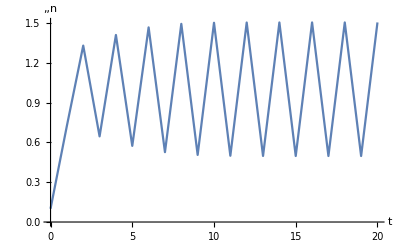

{n→1.50294}

```mathematica
rr=2.2;
sol=EcoSim[{n->0.1},20];
PlotDynamics[sol]
FinalSlice[sol]
```

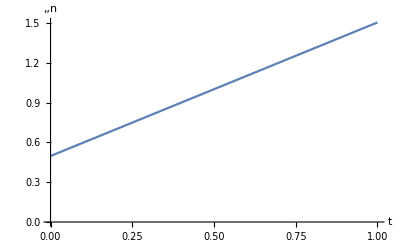

```mathematica
lc=FindEcoCycle[{n->0.3},Period->2];
PlotDynamics[lc]
```

```mathematica
ev=EcoEigenvalues[lc]
```

{0.215731}

```mathematica
EcoStableQ[lc]
```

True

```mathematica
FindEcoCycle[{n->0.3},Period->1,PrintTrace->True]
```

1: {n→1.39938}

2: {n→0.581234}

3: {n→1.46036}

4: {n→0.530407}

5: {n→1.49032}

6: {n→0.506759}

7: {n→1.49992}

8: {n→0.499369}

9: {n→1.50227}

10: {n→0.49757}

11: {n→1.5028}

12: {n→0.49717}

13: {n→1.50291}

14: {n→0.497083}

15: {n→1.50293}

16: {n→0.497065}

17: {n→1.50294}

18: {n→0.497061}

19: {n→1.50294}

20: {n→0.49706}

21: {n→1.50294}

22: {n→0.497059}

23: {n→1.50294}

24: {n→0.497059}

25: {n→1.50294}

26: {n→0.497059}

27: {n→1.50294}

28: {n→0.497059}

29: {n→1.50294}

30: {n→0.497059}

31: {n→1.50294}

32: {n→0.497059}

33: {n→1.50294}

34: {n→0.497059}

35: {n→1.50294}

36: {n→0.497059}

37: {n→1.50294}

38: {n→0.497059}

39: {n→1.50294}

40: {n→0.497059}

41: {n→1.50294}

42: {n→0.497059}

43: {n→1.50294}

44: {n→0.497059}

45: {n→1.50294}

46: {n→0.497059}

47: {n→1.50294}

48: {n→0.497059}

49: {n→1.50294}

50: {n→0.497059}

51: {n→1.50294}

52: {n→0.497059}

53: {n→1.50294}

54: {n→0.497059}

55: {n→1.50294}

56: {n→0.497059}

57: {n→1.50294}

58: {n→0.497059}

59: {n→1.50294}

60: {n→0.497059}

61: {n→1.50294}

62: {n→0.497059}

63: {n→1.50294}

64: {n→0.497059}

65: {n→1.50294}

66: {n→0.497059}

67: {n→1.50294}

68: {n→0.497059}

69: {n→1.50294}

70: {n→0.497059}

71: {n→1.50294}

72: {n→0.497059}

73: {n→1.50294}

74: {n→0.497059}

75: {n→1.50294}

76: {n→0.497059}

77: {n→1.50294}

78: {n→0.497059}

79: {n→1.50294}

80: {n→0.497059}

81: {n→1.50294}

82: {n→0.497059}

83: {n→1.50294}

84: {n→0.497059}

85: {n→1.50294}

86: {n→0.497059}

87: {n→1.50294}

88: {n→0.497059}

89: {n→1.50294}

90: {n→0.497059}

91: {n→1.50294}

92: {n→0.497059}

93: {n→1.50294}

94: {n→0.497059}

95: {n→1.50294}

96: {n→0.497059}

97: {n→1.50294}

98: {n→0.497059}

99: {n→1.50294}

100: {n→0.497059}

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

$Failed

{n→TimeSeries[…]}

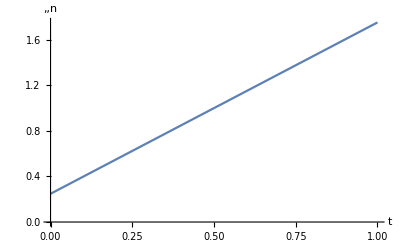

```mathematica
rr=2.6;
lc=FindEcoCycle[{n->0.4},Period->2,Method->"FindRoot"]
PlotDynamics[lc]
```

```mathematica
jac=EcoJacobian[lc]
```

TimeSeries[…]

```mathematica
Normal@jac
```

{{0,{{2.51104}}},{1,{{-0.503135}}}}

```mathematica
ev=EcoEigenvalues[lc]
```

{-1.26339}

```mathematica
EcoStableQ[lc]
```

False

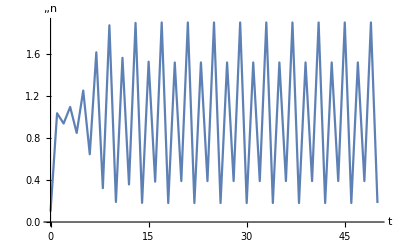

{n→0.181222}

```mathematica
sol=EcoSim[{n->0.1},50];
PlotDynamics[sol]
FinalSlice[sol]
```

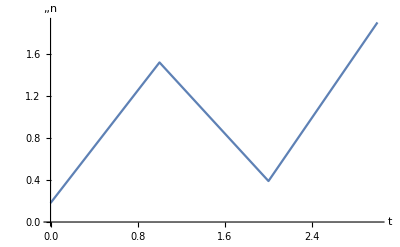

-Graphics-

```mathematica
lc=FindEcoCycle[{n->0.18},Period->4,Method->"FindRoot"];
PlotDynamics[lc]
lc=FindEcoCycle[{n->0.18},Period->4];
PlotDynamics[lc]
```

```mathematica
Normal@EcoJacobian[lc]
```

{{0,{{4.44473}}},{1,{{-0.7596}}},{2,{{-0.0789572}}},{3,{{-0.376037}}}}

```mathematica
ev=EcoEigenvalues[lc]
```

{-0.100243}

```mathematica
EcoStableQ[lc]
```

True

#### dl

```mathematica
SetModel[dl]
```

```mathematica
Eigenvalues@EcoJacobian[{j->0,a->0}]
```

{1.28078,-0.780776}

#### rm

```mathematica
SetModel[rm]
```

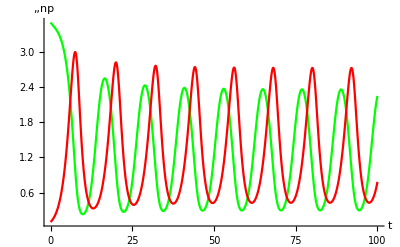

```mathematica
tmax=100;
nk=3.5;
sol=EcoSim[{n->nk,p->0.1},tmax];
PlotDynamics[sol]
```

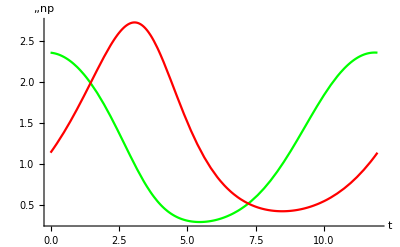

```mathematica
debug=False;
sol=FindEcoCycle[{n->nk,p->0.1}];
PlotDynamics[sol]
```

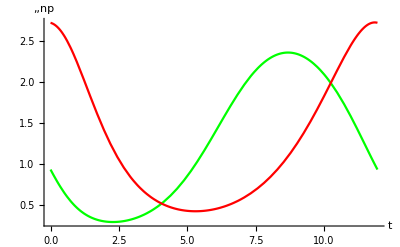

```mathematica
sol=FindEcoCycle[{n->nk,p->0.1},TriggerVariable->p];
PlotDynamics[sol]
```

```mathematica
FinalTime[sol]
```

11.9613

```mathematica
jmat=EcoJacobian[sol]
```

{{1-0.571429 InterpolatingFunction[…][t]+(InterpolatingFunction[…][t] InterpolatingFunction[…][t])/(1+InterpolatingFunction[…][t])^2-(InterpolatingFunction[…][t])/(1+InterpolatingFunction[…][t]),-(InterpolatingFunction[…][t])/(1+InterpolatingFunction[…][t])},{(-(2 InterpolatingFunction[…][t])/(1+InterpolatingFunction[…][t])^2+2/(1+InterpolatingFunction[…][t])) InterpolatingFunction[…][t],-1+(2 InterpolatingFunction[…][t])/(1+InterpolatingFunction[…][t])}}

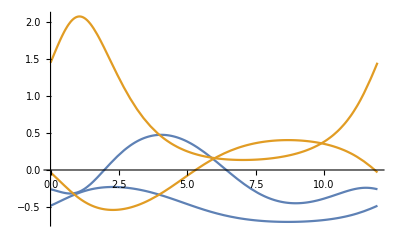

```mathematica
Plot[jmat,{t,0,FinalTime[sol]}]
```

```mathematica
EcoEigenvalues[sol]
```

{-3.06151×10^-7,-0.0712229}

```mathematica
EcoEigenvalues[sol,Multipliers->True]
```

{0.999996,0.426596}

```mathematica
EcoStableQ[sol]
```

True

```mathematica
SelectEcoStable[{sol}]
```

{{n→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

```mathematica
sol=FindEcoCycle[{n->nk,p->0.1},Logged->True]
```

{n→InterpolatingFunction[…],p→InterpolatingFunction[…]}

```mathematica
sol=FindEcoCycle[{n->1.0,p->0.1},Method->"FindRoot",Period->12]
```

{n→InterpolatingFunction[…],p→InterpolatingFunction[…]}

```mathematica
FinalTime[sol]
```

11.9613

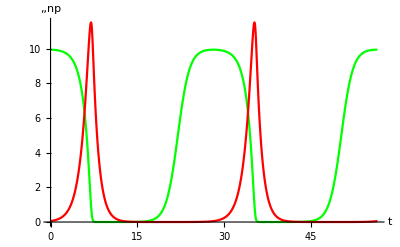

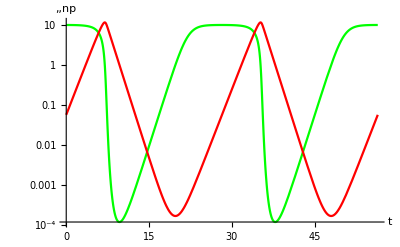

```mathematica
nk=10;
sol=FindEcoCycle[{n->nk,p->0.1}];
PlotDynamics[sol]
PlotDynamics[sol,Logged->True]
```

```mathematica
sol=FindEcoCycle[{n->1.0,p->0.1},Method->"FindRoot",Period->28]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{n→InterpolatingFunction[…],p→InterpolatingFunction[…]}

```mathematica
sol=FindEcoCycle[{n->1.0,p->0.1},Method->"FindRoot",Logged->True,Period->28]
```

{n→InterpolatingFunction[…],p→InterpolatingFunction[…]}

#### tt

```mathematica
SetModel[tt]
```

```mathematica
B1=2.28;
```

```mathematica
tmax=10000;
sol=EcoSim[{x->0.1,y->0.1,z->5.0},tmax];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol],{t,tmax-1000,tmax}]
```

-Graphics3D-

```mathematica
lc=FindEcoCycle[FinalSlice[sol]]
```

{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}

```mathematica
EcoEigenvalues[lc]
```

{1.99747×10^-8,-0.00172165+0.0520204 ⅈ,-∞}

```mathematica
EcoEigenvalues[lc,Multipliers->True]
```

{1.,-0.90125,0}

```mathematica
B1=2.3;
sol=EcoSim[{x->0.1,y->0.1,z->5.0},tmax];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol],{t,tmax-1000,tmax}]
```

-Graphics3D-

```mathematica
lc=FindEcoCycle[FinalSlice[sol],Method->"FindRoot",Period->60]
```

{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}

```mathematica
EcoEigenvalues[lc]
```

{0.00125244+0.0514284 ⅈ,1.91685×10^-8,-∞}

```mathematica
EcoEigenvalues[lc,Multipliers->True]
```

{-1.07951,1.,0}

#### fl

```mathematica
SetModel[fl]
```

```mathematica
sol=FindEcoCycle[{R->Rin,b1->0,b2->0}]
```

{b1→InterpolatingFunction[…],b2→InterpolatingFunction[…],R→InterpolatingFunction[…]}

```mathematica
Inv[b2,Method->"Integrate"]/.R[t]->Rin
```

0.8

```mathematica
Inv[sol,b2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {219.565}. NIntegrate obtained 291.967 and 0.0639756 for the integral and error estimates.

0.79991

{b1→9.06343×10^-11,b2→1.51587×10^-15,R→20.}

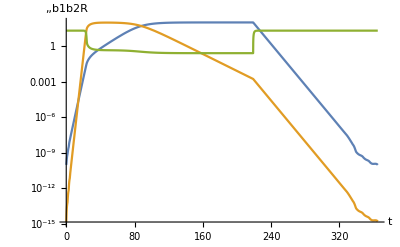

```mathematica
eq=FindEcoCycle[{b1->10^-10,b2->10^-15,R->Rin},Method->"FindRoot"];
FinalSlice[eq]
PlotDynamics[eq,Logged->True]
```

{b1→2.05636×10^-11,b2→1.79618×10^-15,R→20.}

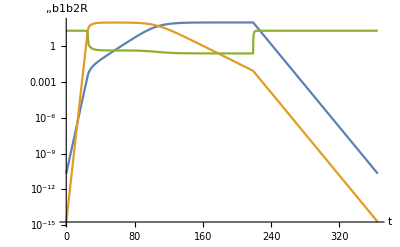

```mathematica
eq=FindEcoCycle[{b1->10.^-10,b2->10.^-15,R->Rin},Method->"FindRoot",Logged->True];
FinalSlice[eq]
PlotDynamics[eq,Logged->True]
```

{b1→9.06429×10^-11,b2→1.35111×10^-15,R→20.}

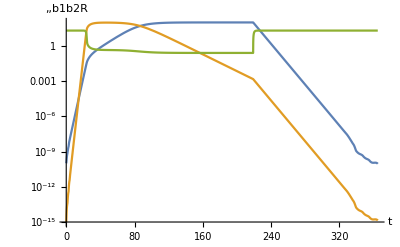

```mathematica
eq=FindEcoCycle[{b1->10.^-10,b2->10.^-15,R->Rin},Method->"FixedPoint"];
FinalSlice[eq]
PlotDynamics[eq,Logged->True]
```

{b1→2.05636×10^-11,b2→1.79618×10^-15,R→20.}

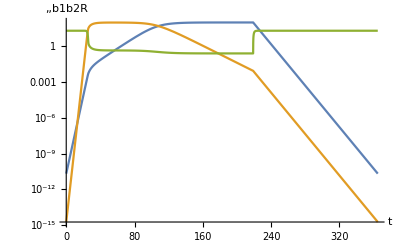

```mathematica
eq=FindEcoCycle[{b1->10.^-10,b2->10.^-15,R->Rin},Method->"FixedPoint",Logged->True];
FinalSlice[eq]
PlotDynamics[eq,Logged->True]
```

```mathematica
EcoEigenvalues[eq]
```

{-0.00298572,-∞,-∞}

```mathematica
EcoEigenvalues[eq,Multipliers->True]
```

{0.336288,0,0}

```mathematica
EcoStableQ[eq]
```

True

```mathematica
eq=FindEcoCycle[{b1->10.^-10,R->Rin},Method->"FixedPoint",Fixed->{b2->0}];
FinalSlice[eq]
PlotDynamics[eq,Logged->True]
```

{b1→-2.06074×10^-11,b2→0,R→20.}

-Graphics-

{b1→2.05657×10^-11,b2→0,R→20.}

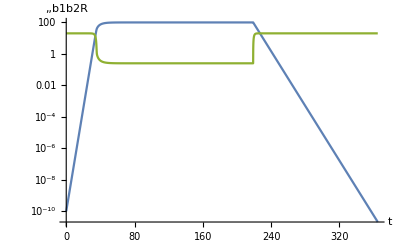

```mathematica
eq=FindEcoCycle[{b1->10.^-10,R->Rin},Method->"FixedPoint",Fixed->{b2->0},EcoSimOpts->{NDSolveOpts->{AccuracyGoal->16}}];
FinalSlice[eq]
PlotDynamics[eq,Logged->True]
```

1: {b1→2.05655×10^-11,b2→0,R→20.}

2: {b1→2.05655×10^-11,b2→0,R→20.}

{b1→InterpolatingFunction[…],b2→InterpolatingFunction[…],R→InterpolatingFunction[…]}

{b1→2.05655×10^-11,b2→0,R→20.}

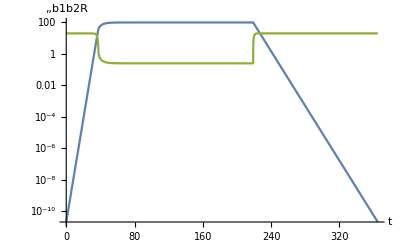

```mathematica
eq=FindEcoCycle[{b1->10.^-10,R->Rin},Method->"FixedPoint",Logged->True,Fixed->{b2->0},PrintTrace->True]
FinalSlice[eq]
PlotDynamics[eq,Logged->True]
```

#### jon

```mathematica
SetModel[jon]
```

```mathematica
eq=FindEcoCycle[{Subscript[x, 1]->15},{Subscript[c, 1]->0.1}]
```

{c_1→InterpolatingFunction[…]}

```mathematica
EcoEigenvalues[{Subscript[x, 1]->15},eq,Multipliers->False]
```

{-0.0611348+0.0086071 ⅈ}

```mathematica
eq=FindEcoCycle[{Subscript[x, 1]->15},{Subscript[c, 1]->0.1},EcoSimOpts->{Logged->True}]
```

{c_1→InterpolatingFunction[…]}

```mathematica
eq=FindEcoCycle[{Subscript[x, 1]->15},{Subscript[c, 1]->0.1},Logged->True]
```

{c_1→InterpolatingFunction[…]}

```mathematica
eq=FindEcoCycle[{Subscript[x, 1]->15},{Subscript[c, 1]->0.1},Method->"FixedPoint"]
```

{c_1→InterpolatingFunction[…]}

```mathematica
eq=FindEcoCycle[{Subscript[x, 1]->15},{Subscript[c, 1]->0.1},Method->"FixedPoint",Logged->True]
```

{c_1→InterpolatingFunction[…]}

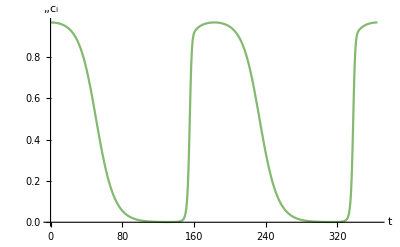

```mathematica
PlotDynamics[eq]
```

```mathematica
EcoEigenvalues[{Subscript[x, 1]->15},eq,Multipliers->True]
```

{-2.03732×10^-10}

```mathematica
(* weird case that doesn't converge *)
FindEcoCycle[{Subscript[x, 1]->17.5},{Subscript[c, 1]->1},Logged->True]
```

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

$Failed

```mathematica
FindEcoCycle[{Subscript[x, 1]->17.5},{Subscript[c, 1]->1},MaxIterations->20,PrintTrace->True]
```

1: {c_1→0.0023933}

2: {c_1→0.00237713}

3: {c_1→0.00239006}

4: {c_1→0.00237221}

5: {c_1→0.00239006}

6: {c_1→0.00237221}

7: {c_1→0.00239006}

8: {c_1→0.0023722}

9: {c_1→0.00239006}

10: {c_1→0.00237221}

11: {c_1→0.00239006}

12: {c_1→0.0023722}

13: {c_1→0.00239006}

14: {c_1→0.00237221}

15: {c_1→0.00239006}

16: {c_1→0.00237221}

17: {c_1→0.00239006}

18: {c_1→0.00237222}

19: {c_1→0.00239006}

20: {c_1→0.00237222}

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 20 iterations.

$Failed

```mathematica
eq=FindEcoCycle[{Subscript[x, 1]->10,Subscript[x, 2]->20},{Subscript[c, 1]->0.1,Subscript[c, 2]->0.1}]
```

{c_1→InterpolatingFunction[…],c_2→InterpolatingFunction[…]}

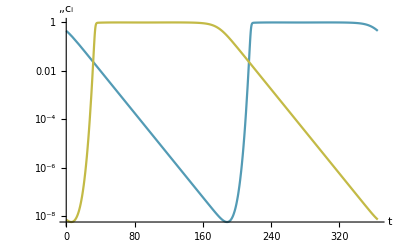

```mathematica
PlotDynamics[eq,Logged->True]
```

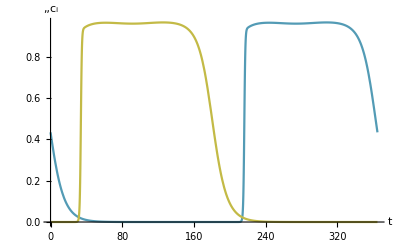

```mathematica
eq=FindEcoCycle[{Subscript[x, 1]->10,Subscript[x, 2]->20},{Subscript[c, 1]->0.1,Subscript[c, 2]->0.1},Logged->True];
PlotDynamics[eq]
```

```mathematica
eq=FindEcoCycle[{Subscript[x, 1]->10,Subscript[x, 2]->20},{Subscript[c, 1]->0.1,Subscript[c, 2]->0.1},Method->"FixedPoint",Logged->True]
```

{c_1→InterpolatingFunction[…],c_2→InterpolatingFunction[…]}

```mathematica
FinalSlice[eq]
```

{c_1→0.434336,c_2→7.22047×10^-9}

```mathematica
eq=FindEcoCycle[{Subscript[x, 1]->10,Subscript[x, 2]->15,Subscript[x, 3]->20},{Subscript[c, 1]->0.1,Subscript[c, 2]->0.1,Subscript[c, 3]->0.1},Method->"FixedPoint",Logged->True]
```

{c_1→InterpolatingFunction[…],c_2→InterpolatingFunction[…],c_3→InterpolatingFunction[…]}

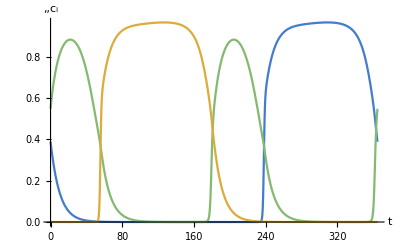

```mathematica
PlotDynamics[eq]
```

```mathematica
EcoEigenvalues[{Subscript[x, 1]->10,Subscript[x, 2]->15,Subscript[x, 3]->20},eq]
```

{-0.0198702,-0.0200053,-∞}

```mathematica
EcoEigenvalues[{Subscript[x, 1]->10,Subscript[x, 2]->15,Subscript[x, 3]->20},eq,Multipliers->True]
```

{0.000708309,0.000674237,0}

#### mc

```mathematica
SetModel[mc]
```

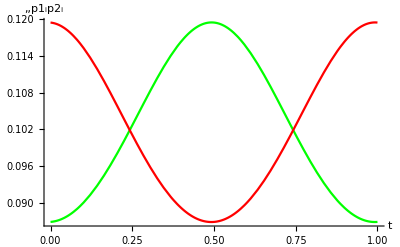

```mathematica
lc=FindEcoCycle[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.1,Subscript[p2, 1]->0.1}];
PlotDynamics[lc]
```

```mathematica
EcoEigenvalues[{Subscript[dd, 1]->0.1},lc]
```

{-0.102529,-0.307611}

```mathematica
Inv[{Subscript[dd, 1]->0.1},lc,{Subscript[dd, 0]->0.1}]
```

7.96096×10^-6

```mathematica
Inv[{Subscript[dd, 1]->0.1},lc,{Subscript[dd, 0]->0.11}]
```

0.000261662

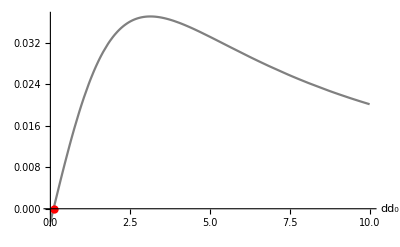

```mathematica
PlotInv[{Subscript[dd, 1]->0.1},lc,{Subscript[dd, 0],0,10}]
```

#### pulsed

```mathematica
SetModel[pulsed]
```

```mathematica
τ=10;
```

```mathematica
lc=FindEcoCycle[{Subscript[a1, 1]->0.5},{r1->10,Subscript[b, 1]->1000,Subscript[q, 1]->1.0}]
```

{r1→InterpolatingFunction[…],b_1→InterpolatingFunction[…],q_1→InterpolatingFunction[…]}

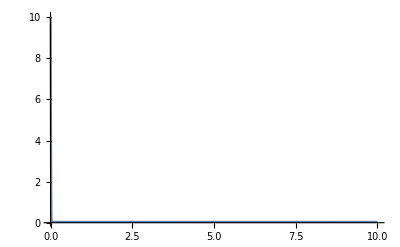

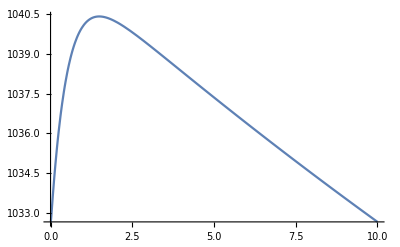

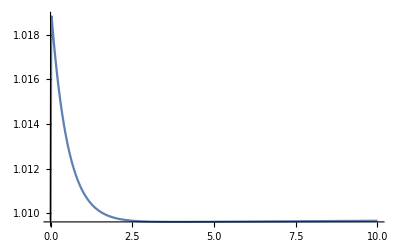

```mathematica
Plot[r1[t]/.lc,{t,0,τ},PlotRange->All]
Plot[Subscript[b, 1][t]/.lc,{t,0,τ},PlotRange->All]
Plot[Subscript[q, 1][t]/.lc,{t,0,τ},PlotRange->All]
```

```mathematica
sol=EcoSim[{Subscript[a1, 1]->0.5,Subscript[a1, 0]->0.6},Join[FinalSlice[lc],{Subscript[q, 0]->(Subscript[q, 1][τ]/.lc)}],τ]
```

{q_0→Function[{t},1.00966],b_1→InterpolatingFunction[…],q_1→InterpolatingFunction[…],r1→InterpolatingFunction[…]}

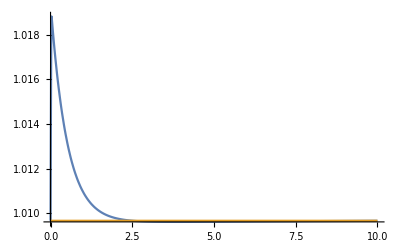

```mathematica
Plot[Evaluate[{Subscript[q, 1][t],Subscript[q, 0][t]}/.sol],{t,0,τ},PlotRange->All]
```

```mathematica
invlc=FindEcoCycle[{Subscript[a1, 1]->0.5,Subscript[a1, 0]->0.6},Join[FinalSlice[lc],{Subscript[q, 0]->(Subscript[q, 1][τ]/.lc)}]]
```

ReplaceAll::reps: {Slice[{q_0→Function[{t},1.00966],«2»,r1→InterpolatingFunction[{{0.,10.}},{5,23,1,{227},{4},0,0,0,0,Automatic,{},{},False},«1»,{Developer`PackedArrayForm,{0,2,«47»,98,«178»},{0.0402115,«49»,«404»}},{Automatic}]},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{r1→InterpolatingFunction[…],b_1→InterpolatingFunction[…],q_0→Function[{t},1.00966],q_1→InterpolatingFunction[…]}

```mathematica
InitialSlice[invlc]
FinalSlice[invlc]
```

{r1→10.0402,b_1→1032.66,q_0→Function[{t},1.00966],q_1→1.00966}

{r1→0.0402115,b_1→1032.66,q_0→Function[{t},1.00966],q_1→1.00966}

#### dormant

```mathematica
SetModel[dormant]
```

```mathematica
τ=10;
tmax=100τ;
sol=EcoSim[{Subscript[a1, 1]->0.5},{r1->rin1,Subscript[b, 1]->1000,Subscript[bd, 1]->0,Subscript[q, 1]->qmin},tmax];
```

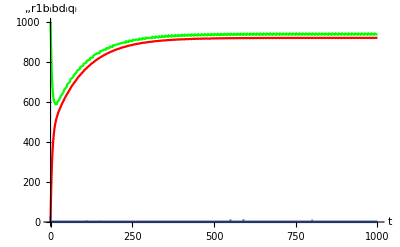

```mathematica
PlotDynamics[sol]
```

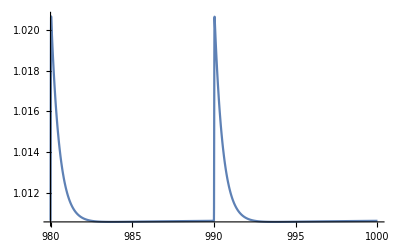

```mathematica
Plot[Subscript[q, 1][t]/.sol,{t,tmax-2τ,tmax},PlotRange->All]
```

```mathematica
lc=FindEcoCycle[{Subscript[a1, 1]->0.5},FinalSlice[sol]]
```

{r1→InterpolatingFunction[…],b_1→InterpolatingFunction[…],bd_1→InterpolatingFunction[…],q_1→InterpolatingFunction[…]}

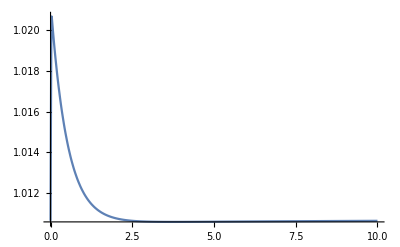

```mathematica
Plot[Subscript[q, 1][t]/.lc,{t,0,τ},PlotRange->All]
```

#### dfltwop

```mathematica
SetModel[dfltwop]
```

```mathematica
rp2a=1;
```

```mathematica
tmax=50;
sol=EcoSim[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.1,Subscript[p2, 1]->0.1},tmax];
PlotDynamics[sol,Joined->True]
```

-Graphics-

```mathematica
FinalSlice[sol]
```

{p1_1→0.808131,p2_1→0.531453}

```mathematica
lc=FindEcoCycle[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.5,Subscript[p2, 1]->0.8},Method->"FixedPoint"]
FinalSlice[lc]
```

{p1_1→TimeSeries[…],p2_1→TimeSeries[…]}

{p1_1→0.531453,p2_1→0.808131}

```mathematica
lc=FindEcoCycle[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.5,Subscript[p2, 1]->0.8},Method->"FindRoot"]
FinalSlice[lc]
```

{p1_1→TimeSeries[…],p2_1→TimeSeries[…]}

{p1_1→0.531453,p2_1→0.808131}

```mathematica
Normal@EcoJacobian[{Subscript[dd, 1]->0.1},lc]
```

{{0,{{-0.216263,0.1},{0.1,0.837094}}},{1,{{0.837094,0.1},{0.1,-0.216263}}}}

```mathematica
EcoEigenvalues[{Subscript[dd, 1]->0.1},lc]
```

{-0.171032+0.0850958 ⅈ,-0.171032-0.0850958 ⅈ}

```mathematica
rp2a=1.7;
tmax=100;
sol=EcoSim[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.1,Subscript[p2, 1]->0.1},tmax];
lc4=FindEcoCycle[{Subscript[dd, 1]->0.1},FinalSlice[sol],Method->"FindRoot",Period->4];
EcoEigenvalues[{Subscript[dd, 1]->0.1},lc4]
lc2=FindEcoCycle[{Subscript[dd, 1]->0.1},FinalSlice[sol],Method->"FindRoot"];
InitialSlice[lc2]
Normal@EcoJacobian[{Subscript[dd, 1]->0.1},lc2]
EcoEigenvalues[{Subscript[dd, 1]->0.1},lc2]
rp2a=1;
```

{0.632677,0.0458587}

{p1_1→0.819551,p2_1→0.436003}

{{0,{{-0.239102,0.1},{0.1,1.72799}}},{1,{{0.861384,0.1},{0.1,-0.65093}}}}

{-1.089,-0.221765}

### FindEcoAttractor

```mathematica
?FindEcoAttractor
```

FindEcoAttractor[] tries to find an ecological attractor.
FindEcoAttractor[traits] uses trait values traits.

#### ricker

```mathematica
SetModel[ricker]
```

```mathematica
rr=1.2;
FindEcoAttractor[]
```

{n→1.}

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={1.00588} at t=1000). Trying FindEcoCycle.

{n→TimeSeries[…]}

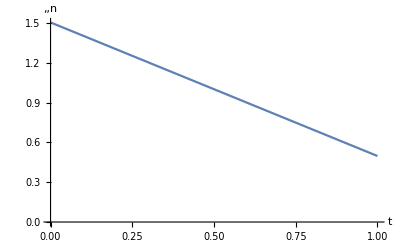

```mathematica
rr=2.2;
ea=FindEcoAttractor[{n->0.1}]
PlotDynamics[ea]
```

```mathematica
rr=2.4;
FindEcoAttractor[{n->0.1}]
```

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={1.31714} at t=1000). Trying FindEcoCycle.

{n→TimeSeries[…]}

```mathematica
rr=2.55;
FindEcoAttractor[{n->0.1}]
```

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={1.48963} at t=1000). Trying FindEcoCycle.

{n→TimeSeries[…]}

FindEcoAttactor: FindEcoEq Mode

FindEcoAttactor: Warming Up...

FinalSlice[EcoSim[{},{n→0.1},100,Time→t]]

FindEcoEq[{},{n→0.128663},Time→t]

FindEcoAttactor: eq={{n→0}}

FindEcoAttactor: valid eq={{n→0}}

FindEcoAttactor: stable eq={}

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {}. Trying EcoSim.

FindEcoAttactor: EcoSim Mode

EcoSim[{},{n→0.128663},1000,Time→t]

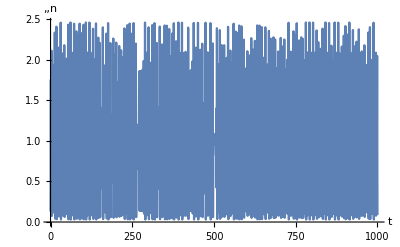

FindEcoAttactor: d/dt={-1.96163}

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-1.96163} at t=1000). Trying FindEcoCycle.

FindEcoAttactor: FindEcoCycle Mode

Table[FindEcoCycle[{},{n→0.0879421},Period→permult 16],{permult,2}]

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttactor: eq={}

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttactor: stable eq={}

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

{n→TimeSeries[…]}

```mathematica
rr=3.0;
ea=FindEcoAttractor[{n->0.1},Method->"FindEcoEq",WarmUp->100,Verbose->True]
```

#### lvc

```mathematica
SetModel[lvc]
```

```mathematica
FindEcoAttractor[]
```

{n1→0.533333,n2→0.933333}

```mathematica
FindEcoAttractor[Verbose->True]
```

FindEcoAttactor: NSolveEcoEq Mode

eq=Union[NSolveEcoEq[{},Time→t]]

FindEcoAttactor: eq={{n1→0,n2→0},{n1→0,n2→1.2},{n1→0.533333,n2→0.933333},{n1→1.,n2→0}}

FindEcoAttactor: valid eq={{n1→0,n2→0},{n1→0,n2→1.2},{n1→0.533333,n2→0.933333},{n1→1.,n2→0}}

FindEcoAttactor: stable eq={{n1→0.533333,n2→0.933333}}

{n1→0.533333,n2→0.933333}

```mathematica
FindEcoAttractor[Method->"SolveEcoEq"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{n1→0.533333,n2→0.933333}

```mathematica
FindEcoAttractor[{n1->0.5,n2->0.9}]
```

{n1→0.533333,n2→0.933333}

FindEcoAttactor: FindEcoEq Mode

FindEcoEq[{},{n1→0.2,n2→0.3},Time→t]

FindEcoAttactor: eq={{n1→0,n2→0}}

FindEcoAttactor: valid eq={{n1→0,n2→0}}

FindEcoAttactor: stable eq={}

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {}. Trying EcoSim.

FindEcoAttactor: EcoSim Mode

EcoSim[{},{n1→0.2,n2→0.3},1000,Time→t]

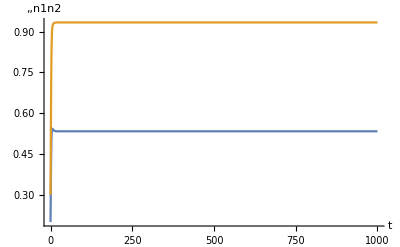

FindEcoAttactor: d/dt={-7.12575×10^-19,1.44165×10^-18}

FindEcoAttactor: Equilibrium found

{n1→0.533333,n2→0.933333}

```mathematica
FindEcoAttractor[{n1->0.2,n2->0.3},Method->"FindEcoEq",Verbose->True]
```

```mathematica
FindEcoAttractor[{n1->0.2,n2->0.3},Method->"FindEcoEq",NumTries->10,Verbose->True]
```

FindEcoAttactor: FindEcoEq Mode

FindEcoEq[{},{n1→0.2,n2→0.3},Time→t]

FindEcoEq[{},{n1→0.0365778,n2→2.13934},Time→t]

FindEcoEq[{},{n1→1.28732,n2→2.52086},Time→t]

FindEcoEq[{},{n1→0.218195,n2→0.204352},Time→t]

FindEcoEq[{},{n1→1.44905,n2→1.45346},Time→t]

FindEcoEq[{},{n1→0.0712897,n2→0.337098},Time→t]

FindEcoEq[{},{n1→0.134442,n2→0.367094},Time→t]

FindEcoEq[{},{n1→0.0804063,n2→1.60526},Time→t]

FindEcoEq[{},{n1→0.024868,n2→1.56491},Time→t]

FindEcoEq[{},{n1→0.831701,n2→2.17527},Time→t]

FindEcoAttactor: eq={{n1→0,n2→0},{n1→0,n2→1.2},{n1→0.533333,n2→0.933333}}

FindEcoAttactor: valid eq={{n1→0,n2→0},{n1→0,n2→1.2},{n1→0.533333,n2→0.933333}}

FindEcoAttactor: stable eq={{n1→0.533333,n2→0.933333}}

{n1→0.533333,n2→0.933333}

#### twop

```mathematica
SetModel[twop]
```

```mathematica
disp=0.1;
```

```mathematica
FindEcoAttractor[]
```

{p1→1.,p2→1.}

```mathematica
FindEcoAttractor[Method->"SolveEcoEq"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{p1→1.,p2→1.}

```mathematica
FindEcoAttractor[Method->"NSolveEcoEq"]
```

{p1→1.,p2→1.}

```mathematica
FindEcoAttractor[{p1->0.7,p2->0.9},Method->"FindEcoEq"]
```

{p1→1.,p2→1.}

```mathematica
FindEcoAttractor[{p1->0.01,p2->0.01},Method->"FindEcoEq"]
```

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {}. Trying EcoSim.

{p1→1.,p2→1.}

```mathematica
FindEcoAttractor[{p1->0.7,p2->0.9},Method->"EcoSim"]
```

{p1→1.,p2→1.}

#### dl

```mathematica
SetModel[dl]
```

```mathematica
FindEcoAttractor[]
```

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {}. Trying EcoSim.

FindEcoAttractor::nopops: No initial population sizes given, cannot continue with EcoSim.

$Aborted

```mathematica
ra=0.01;
FindEcoAttractor[Verbose->True]
ra=5;
```

FindEcoAttactor: NSolveEcoEq Mode

eq=Union[NSolveEcoEq[{},Time→t]]

FindEcoAttactor: eq={{j→0,a→0}}

FindEcoAttactor: valid eq={{j→0,a→0}}

FindEcoAttactor: stable eq={{j→0,a→0}}

{j→0,a→0}

```mathematica
FindEcoAttractor[{a->0.1,j->0.1}]
```

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={1.98621×10^106,3.10157×10^105} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

{j→TimeSeries[…],a→TimeSeries[…]}

#### lv

```mathematica
SetModel[lv]
```

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0}]
```

{n_1→1.}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0},Method->"NSolveEcoEq"]
```

{n_1→1.}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0},Method->"SolveEcoEq"]
```

{n_1→1}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0},{Subscript[n, 1]->0.8},Method->"FindEcoEq"]
```

{n_1→1.}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0},{Subscript[n, 1]->0.01},Method->"FindEcoEq"]
```

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→0}. Trying EcoSim.

{n_1→1.}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0},{Subscript[n, 1]->0.1},Method->"FindEcoEq",NumTries->20]
```

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→0}. Trying EcoSim.

{n_1→1.}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0},{Subscript[n, 1]->0.1},Method->"FindEcoEq",WarmUp->100]
```

{n_1→1.}

FindEcoAttactor: EcoSim Mode

EcoSim[{x_1→0},{n_1→0.1},1000,Time→t]

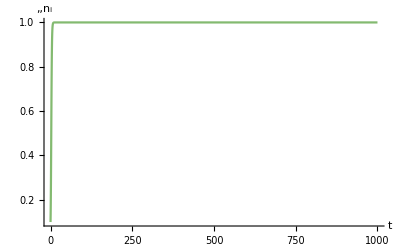

FindEcoAttactor: d/dt={-2.06794×10^-19}

FindEcoAttactor: Equilibrium found

{n_1→1.}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0},{Subscript[n, 1]->0.1},Method->"EcoSim",Verbose->True]
```

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0},{Subscript[n, 1]->0.1},Method->"EcoSim",TMax->10]
```

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000408264} at t=10). Trying FindEcoCycle.

FindEcoCycle::nomaxima: Found no maxima in warmup #3, probably not periodic solution.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

{n_1→InterpolatingFunction[…]}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0,Subscript[x, 2]->0.1}]
```

{n_1→0.754983,n_2→0.249967}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0,Subscript[x, 2]->0.1},Method->"SolveEcoEq"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{n_1→0.754983,n_2→0.249967}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0,Subscript[x, 2]->0.1},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},Method->"FindEcoEq",NumTries->10]
```

{n_1→0.754983,n_2→0.249967}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0,Subscript[x, 2]->0.1},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},Method->"EcoSim"]
```

{n_1→0.75489,n_2→0.25006}

#### si

```mathematica
SetModel[si]
```

```mathematica
FindEcoAttractor[{Subscript[B, 1]->0}]
```

{s_1→15.3333,i_1→0}

```mathematica
FindEcoAttractor[{Subscript[B, 1]->0},Method->"SolveEcoEq"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{s_1→15.3333,i_1→0}

```mathematica
FindEcoAttractor[{Subscript[B, 1]->0},{Subscript[s, 1]->15,Subscript[i, 1]->0.1},Method->"FindEcoEq"]
```

{s_1→15.3333,i_1→0}

```mathematica
FindEcoAttractor[{Subscript[B, 1]->0},{Subscript[s, 1]->0.1,Subscript[i, 1]->0.1},Method->"FindEcoEq"]
```

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {B_1→0}. Trying EcoSim.

{s_1→15.3333,i_1→0}

```mathematica
FindEcoAttractor[{Subscript[B, 1]->0},{Subscript[s, 1]->0.1,Subscript[i, 1]->0.1},Method->"EcoSim"]
```

{s_1→15.3333,i_1→0}

```mathematica
traits={Subscript[B, 1]->0,Subscript[B, 2]->0.5};
FindEcoAttractor[traits]
```

{s_1→14.3067,i_1→0,s_2→0.56,i_2→0.466667}

```mathematica
traits={Subscript[B, 1]->0,Subscript[B, 2]->0.5,Subscript[B, 3]->0.4};
FindEcoAttractor[traits]
```

{s_1→14.3067,i_1→0,s_2→0.56,i_2→0.466667,s_3→0,i_3→0}

```mathematica
FindEcoAttractor[traits,{Subscript[s, 1]->0.1,Subscript[i, 1]->0.1,Subscript[s, 2]->0.1,Subscript[i, 2]->0.1,Subscript[s, 3]->0.1,Subscript[i, 3]->0.1},Method->"EcoSim"]
```

{s_1→14.3067,i_1→0,s_2→0.559989,i_2→0.466656,s_3→0.0000133848,i_3→9.21834×10^-6}

#### ch

```mathematica
SetModel[ch]
```

```mathematica
FindEcoAttractor[{Subscript[mu, 1]->0.25}]
```

{n_1→49.7283,R→0.00543478}

```mathematica
FindEcoAttractor[{Subscript[mu, 1]->0.25},{R->0,Subscript[n, 1]->40},Method->"FindEcoEq"]
```

{n_1→49.7283,R→0.00543478}

```mathematica
FindEcoAttractor[{Subscript[mu, 1]->0.25},{R->0,Subscript[n, 1]->40},Method->"EcoSim"]
```

{n_1→49.7283,R→0.00543478}

```mathematica
FindEcoAttractor[{Subscript[mu, 1]->0.25,Subscript[mu, 2]->0.5}]
```

{n_1→49.7283,n_2→0,R→0.00543478}

```mathematica
FindEcoAttractor[{Subscript[mu, 1]->0.25,Subscript[mu, 2]->0.5},Method->"SolveEcoEq"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{n_1→49.7283,n_2→0,R→0.00543478}

```mathematica
FindEcoAttractor[{Subscript[mu, 1]->0.25,Subscript[mu, 2]->0.5},{R->0,Subscript[n, 1]->40,Subscript[n, 2]->40},Method->"FindEcoEq"]
```

{n_1→49.7283,n_2→0,R→0.00543478}

```mathematica
FindEcoAttractor[{Subscript[mu, 1]->0.25,Subscript[mu, 2]->0.5},{R->0,Subscript[n, 1]->40,Subscript[n, 2]->40},Method->"EcoSim",TMax->10^4]
```

{n_1→49.7283,n_2→0,R→0.00543478}

#### pp

```mathematica
SetModel[pp]
```

```mathematica
FindEcoAttractor[{Subscript[xn, 1]->0.5,Subscript[xp, 1]->0}]
```

{n_1→0.022663,p_1→1.09891}

```mathematica
FindEcoAttractor[{Subscript[xn, 1]->0.5,Subscript[xp, 1]->0},Method->"SolveEcoEq"]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.,1.,0.},{0.,1.44607×10^10,-3.27722×10^8}} may contain significant numerical errors.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{n_1→0.022663,p_1→1.09891}

```mathematica
FindEcoAttractor[{Subscript[xn, 1]->0.5,Subscript[xp, 1]->0},Method->"NSolveEcoEq"]
```

{n_1→0.022663,p_1→1.09891}

```mathematica
FindEcoAttractor[{Subscript[xn, 1]->0.5,Subscript[xp, 1]->0},Method->"FindEcoEq"]
```

FindEcoAttractor::nopops: No initial population sizes given, cannot continue with FindEcoEq.

$Failed

```mathematica
FindEcoAttractor[{Subscript[xn, 1]->0.5,Subscript[xp, 1]->0},{Subscript[n, 1]->0.02,Subscript[p, 1]->1},Method->"FindEcoEq"]
```

{n_1→0.022663,p_1→1.09891}

```mathematica
FindEcoAttractor[{Subscript[xn, 1]->0.5,Subscript[xp, 1]->0},{Subscript[n, 1]->0.02,Subscript[p, 1]->0.1},Method->"FindEcoEq"]
```

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {xn_1→0.5,xp_1→0}. Trying EcoSim.

{n_1→0.0226629,p_1→1.09891}

```mathematica
FindEcoAttractor[{Subscript[xn, 1]->0.5,Subscript[xn, 2]->0.7,Subscript[xp, 1]->0,Subscript[xp, 2]->0.2}]
```

{n_1→0,n_2→0.022663,p_1→0,p_2→1.08279}

```mathematica
FindEcoAttractor[{Subscript[xn, 1]->0.5,Subscript[xn, 2]->0.7,Subscript[xp, 1]->0,Subscript[xp, 2]->0.2},{Subscript[n, 1]->0.05,Subscript[n, 2]->0.05,Subscript[p, 1]->1,Subscript[p, 2]->0.5},Method->"FindEcoEq"]
```

{n_1→0,n_2→0.022663,p_1→0,p_2→1.08279}

```mathematica
FindEcoAttractor[{Subscript[xn, 1]->0.5,Subscript[xn, 2]->0.7,Subscript[xp, 1]->0,Subscript[xp, 2]->0.2},{Subscript[n, 1]->0.05,Subscript[n, 2]->0.05,Subscript[p, 1]->1,Subscript[p, 2]->0.5},Method->"EcoSim",TMax->10^4]
```

{n_1→0,n_2→0.022663,p_1→-1.76534×10^-10,p_2→1.08279}

#### lv2

```mathematica
SetModel[lv2]
```

```mathematica
FindEcoAttractor[{Subscript[x, 1]->-0.25,Subscript[y, 1]->0.1,Subscript[x, 2]->0.25,Subscript[y, 2]->0}]
```

{n_1→0.572484,n_2→0.597146}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->-0.25,Subscript[y, 1]->0.1,Subscript[x, 2]->0.25,Subscript[y, 2]->0},Method->"SolveEcoEq"]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{1.,0.,0.},{1.30364×10^10,2.19275×10^10,-2.03378×10^10}} may contain significant numerical errors.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{n_1→0.572484,n_2→0.597146}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->-0.25,Subscript[y, 1]->0.1,Subscript[x, 2]->0.25,Subscript[y, 2]->0},Method->"NSolveEcoEq"]
```

{n_1→0.572484,n_2→0.597146}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->-0.25,Subscript[y, 1]->0.1,Subscript[x, 2]->0.25,Subscript[y, 2]->0},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},Method->"FindEcoEq"]
```

{n_1→0.572484,n_2→0.597146}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->-0.25,Subscript[y, 1]->0.1,Subscript[x, 2]->0.25,Subscript[y, 2]->0},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},Method->"EcoSim"]
```

{n_1→0.572484,n_2→0.597146}

#### droop

```mathematica
SetModel[droop]
```

```mathematica
FindEcoAttractor[{Subscript[a1, 1]-> 0.26}]
```

{b_1→985.83,q_1→1.0101,r1→0.084246}

```mathematica
FindEcoAttractor[{Subscript[a1, 1]-> 0.26},{r1->0.08,Subscript[b, 1]->985,Subscript[q, 1]->1},Method->"FindEcoEq"]
```

{b_1→985.83,q_1→1.0101,r1→0.084246}

```mathematica
FindEcoAttractor[{Subscript[a1, 1]-> 0.26},{r1->0.08,Subscript[b, 1]->985,Subscript[q, 1]->1},Method->"EcoSim"]
```

{b_1→985.83,q_1→1.0101,r1→0.084246}

#### dlv

```mathematica
SetModel[dlv]
```

```mathematica
r=1;
```

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{n_1→1.}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0},Method->"SolveEcoEq"]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{n_1→1}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0},Method->"NSolveEcoEq"]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{n_1→1.}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0},{Subscript[n, 1]->0.8},Method->"FindEcoEq"]
```

{n_1→1.}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0},{Subscript[n, 1]->0.8},Method->"EcoSim"]
```

{n_1→1.}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0,Subscript[x, 2]->0.5}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{n_1→0.862339,n_2→0.226965}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0,Subscript[x, 2]->0.5},Method->"SolveEcoEq"]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{n_1→0.862339,n_2→0.226965}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0,Subscript[x, 2]->0.5},Method->"NSolveEcoEq"]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{n_1→0.862339,n_2→0.226965}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0,Subscript[x, 2]->0.5},{Subscript[n, 1]->0.8,Subscript[n, 2]->0.3},Method->"FindEcoEq"]
```

{n_1→0.862339,n_2→0.226965}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0,Subscript[x, 2]->0.5},{Subscript[n, 1]->0.8,Subscript[n, 2]->0.3},Method->"EcoSim"]
```

{n_1→0.862339,n_2→0.226965}

FindEcoAttactor: EcoSim Mode

EcoSim[{x_1→0,x_2→0.5},{n_1→0.8,n_2→0.3},1000,Time→t]

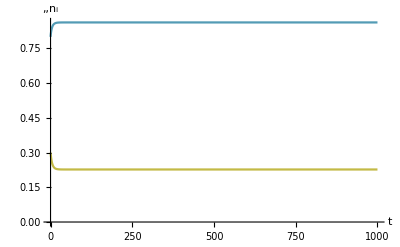

FindEcoAttactor: d/dt={0.,0.}

FindEcoAttactor: Equilibrium found

{n_1→0.862339,n_2→0.226965}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0,Subscript[x, 2]->0.5},{Subscript[n, 1]->0.8,Subscript[n, 2]->0.3},Method->"EcoSim",Verbose->True]
```

```mathematica
r=1.2;
```

```mathematica
FindEcoAttractor[{Subscript[x, 1]->0,Subscript[x, 2]->0.5}]
```

Join::heads: Heads List and Rule at positions 1 and 2 are expected to be the same.

NSolve::bdomv: Warning: Join[{},Method→EndomorphismMatrix] is not a valid domain specification. Assuming it is a variable to eliminate.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→0,x_2→0.5}. Trying EcoSim.

FindEcoAttractor::nopops: No initial population sizes given, cannot continue with EcoSim.

$Aborted

```mathematica
r=1;
```

#### jon

```mathematica
SetModel[jon]
```

```mathematica
FindEcoAttractor[{Subscript[x, 1]->10},{Subscript[c, 1]->0.1}]
```

{c_1→InterpolatingFunction[…]}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->10,Subscript[x, 2]->20},{Subscript[c, 1]->0.1,Subscript[c, 2]->0.1}]
```

{c_1→InterpolatingFunction[…],c_2→InterpolatingFunction[…]}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->10,Subscript[x, 2]->20},{Subscript[c, 1]->0.1,Subscript[c, 2]->0.1},Method->"FindEcoCycle",FindEcoCycleOpts->{Method->"FindRoot"}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{c_1→InterpolatingFunction[…],c_2→InterpolatingFunction[…]}

```mathematica
(* speed test *)
```

```mathematica
Do[FindEcoAttractor[{Subscript[x, 1]->10},{Subscript[c, 1]->1}],{100}]//AbsoluteTiming
```

{2.06927,Null}

```mathematica
Do[FindEcoAttractor[{Subscript[x, 1]->10},{Subscript[c, 1]->1},TestStability->False],{100}]//AbsoluteTiming
```

{0.7316,Null}

FindEcoAttactor: FindEcoCycle Mode

FindEcoCycle[{x_1→17.5},{c_1→1}]

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttactor: eq={}

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttactor: stable eq={}

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.5}. Trying EcoSim.

FindEcoAttactor: EcoSim Mode

EcoSim[{x_1→17.5},{c_1→1},36500,Time→t]

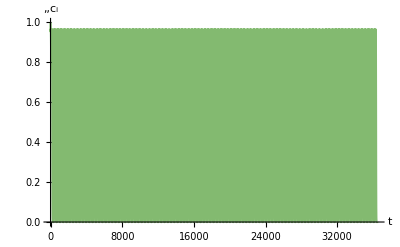

FindEcoAttactor: d/dt={5.23524×10^-8}

FindEcoAttactor: Equilibrium found

{c_1→InterpolatingFunction[…]}

```mathematica
FindEcoAttractor[{Subscript[x, 1]->17.5},{Subscript[c, 1]->1},Verbose->True]
```

```mathematica
(* deliberately broken with EqThreshold *)
FindEcoAttractor[{Subscript[x, 1]->17.5},{Subscript[c, 1]->1},Verbose->True,EqThreshold->0]
```

FindEcoAttactor: FindEcoCycle Mode

FindEcoCycle[{x_1→17.5},{c_1→1}]

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttactor: eq={}

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttactor: stable eq={}

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.5}. Trying EcoSim.

FindEcoAttactor: EcoSim Mode

EcoSim[{x_1→17.5},{c_1→1},36500,Time→t]

-Graphics-

FindEcoAttactor: d/dt={5.23524×10^-8}

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={5.23524×10^-8} at t=36500). Trying FindEcoCycle.

FindEcoAttactor: FindEcoCycle Mode

FindEcoCycle[{x_1→17.5},{c_1→0.00239007}]

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttactor: eq={}

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttactor: stable eq={}

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

{c_1→InterpolatingFunction[{{0., 36500.}}, <>]}

#### dfltwop

```mathematica
SetModel[dfltwop]
```

```mathematica
tmax=50;
sol=EcoSim[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.1,Subscript[p2, 1]->0.1},tmax];
PlotDynamics[sol]
```

-Graphics-

```mathematica
ea=FindEcoAttractor[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.1,Subscript[p2, 1]->0.1},Method->"EcoSim"]
```

{p1_1→TimeSeries[…],p2_1→TimeSeries[…]}

```mathematica
ea=FindEcoAttractor[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.1,Subscript[p2, 1]->0.1}]
```

{p1_1→TimeSeries[…],p2_1→TimeSeries[…]}

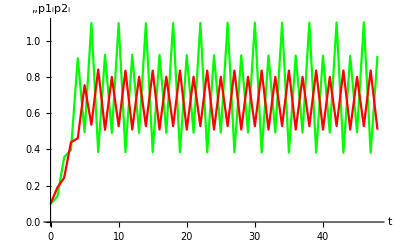

```mathematica
rp1b=1.66;
tmax=48;
sol=EcoSim[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.1,Subscript[p2, 1]->0.1},tmax];
PlotDynamics[sol]
```

```mathematica
FindEcoAttractor[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.1,Subscript[p2, 1]->0.1},Verbose->True]
```

FindEcoAttactor: FindEcoCycle Mode

Table[FindEcoCycle[{dd_1→0.1},{p1_1→0.1,p2_1→0.1},Period→permult 2],{permult,2}]

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttactor: eq={{p1_1→TimeSeries[…],p2_1→TimeSeries[…]}}

FindEcoAttactor: valid eq={{p1_1→TimeSeries[…],p2_1→TimeSeries[…]}}

FindEcoAttactor: stable eq={{p1_1→TimeSeries[…],p2_1→TimeSeries[…]}}

{p1_1→TimeSeries[…],p2_1→TimeSeries[…]}

```mathematica
FindEcoAttractor[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.5,Subscript[p2, 1]->0.5},WarmUp->12,FindEcoCycleOpts->{Method->"FindRoot"}]
```

{p1_1→TimeSeries[…],p2_1→TimeSeries[…]}

```mathematica
rp1b=1;
```

#### pulsed

```mathematica
SetModel[pulsed]
```

```mathematica
τ=10;
```

```mathematica
sol=EcoSim[{Subscript[a1, 1]->0.4},{r1->rin1,Subscript[q, 1]->qmin,Subscript[b, 1]->1},100τ];
FinalSlice[sol]
```

{b_1→1032.,q_1→1.00966,r1→0.0507806}

```mathematica
ea=FindEcoAttractor[{Subscript[a1, 1]->0.4},{r1->rin1,Subscript[q, 1]->qmin,Subscript[b, 1]->1}];
FinalSlice[ea]
```

{r1→0.0507806,b_1→1032.,q_1→1.00966}

```mathematica
ea=FindEcoAttractor[{Subscript[a1, 1]->0.4},{r1->0.05,Subscript[q, 1]->1,Subscript[b, 1]->1000},FindEcoCycleOpts->{MaxIterations->300}]
```

{r1→InterpolatingFunction[…],b_1→InterpolatingFunction[…],q_1→InterpolatingFunction[…]}

```mathematica
ea=FindEcoAttractor[{Subscript[a1, 1]->0.1},{r1->0.02,Subscript[q, 1]->1.01,Subscript[b, 1]->1000},FindEcoCycleOpts->{MaxIterations->300}]
```

{r1→InterpolatingFunction[…],b_1→InterpolatingFunction[…],q_1→InterpolatingFunction[…]}

```mathematica
FinalSlice[ea]
```

{r1→0.240191,b_1→1020.26,q_1→1.00968}

### PlotEcoIsoclines / PlotEcoStreams / PlotEcoPhasePlane

```mathematica
?PlotEcoIsoclines
```

PlotEcoIsoclines[{var1, var1min, var1max}, {var2, var2min, var2max}] plots ecological isoclines in the phase plane of variables var1 and var2.
PlotEcoIsoclines[traits,{var1, var1min, var1max},{var2, var2min, var2max}] uses trait values traits.

```mathematica
?PlotEcoStreams
```

PlotEcoStreams[{var1, var1min, var1max}, {var2, var2min, var2max}] plots ecological streams in the phase plane of variables var1 and var2.
PlotEcoStreams[traits, {var1, var1min, var1max}, {var2, var2min, var2max}] uses trait values traits.

```mathematica
?PlotEcoPhasePlane
```

PlotEcoPhasePlane[{var1, var1min, var1max}, {var2, var2min, var2max}] plots ecological streams and isoclines in the phase plane of variables var1 and var2.
PlotEcoPhasePlane[traits, {var1, var1min, var1max}, {var2, var2min, var2max}] uses trait values traits.

#### lvc

```mathematica
SetModel[lvc]
```

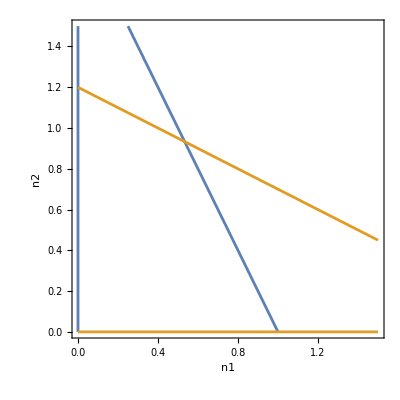

```mathematica
PlotEcoIsoclines[{n1,0,1.5},{n2,0,1.5}]
```

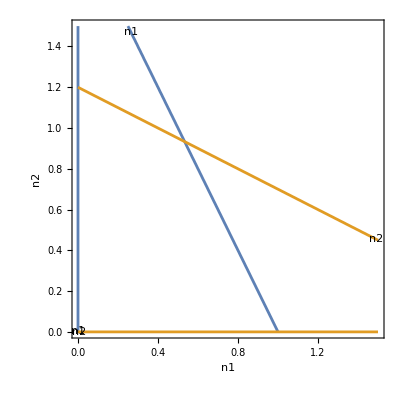

```mathematica
PlotEcoIsoclines[{n1,0,1.5},{n2,0,1.5},IsoclineLabels->True]
```

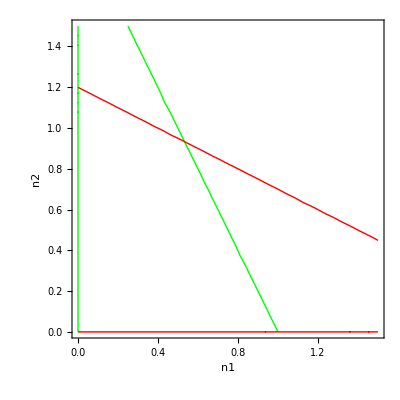

```mathematica
PlotEcoIsoclines[{n1,0,1.5},{n2,0,1.5},IsoclineStyle->{Green,Red},PlotPoints->2]
```

```mathematica
PlotEcoIsoclines[{n1,0,1.5},{n2,0,1.5},FrameLabel->None]
```

-Graphics-

```mathematica
PlotEcoStreams[{n1,0,1.5},{n2,0,1.5}]
```

-Graphics-

```mathematica
PlotEcoStreams[{n1,0,1.5},{n2,0,1.5},StreamStyle->Blue]
```

-Graphics-

```mathematica
PlotEcoStreams[{n1,0,1.5},{n2,0,1.5},FrameLabel->None]
```

-Graphics-

```mathematica
PlotEcoPhasePlane[{n1,0,1.5},{n2,0,1.5}]
```

-Graphics-

```mathematica
PlotEcoPhasePlane[{n1,0,1.5},{n2,0,1.5},IsoclineLabels->True]
```

-Graphics-

```mathematica
PlotEcoPhasePlane[{n1,0,1.5},{n2,0,1.5},FrameLabel->None]
```

-Graphics-

```mathematica
PlotEcoPhasePlane[{n1,0,1.5},{n2,0,1.5},IsoclineStyle->{Green,Red}]
```

-Graphics-

#### rm

```mathematica
SetModel[rm]
PlotEcoPhasePlane[{n,0,4},{p,0,4}]
```

-Graphics-

#### twop

```mathematica
SetModel[twop]
PlotEcoPhasePlane[{p1,0,2},{p2,0,2}]
```

-Graphics-

#### dl

```mathematica
SetModel[dl]
PlotEcoPhasePlane[{j,0,1},{a,0,1}]
```

-Graphics-

#### lv

```mathematica
SetModel[lv]
```

```mathematica
PlotEcoPhasePlane[{Subscript[x, 1]->0.5,Subscript[x, 2]->-0.5},{Subscript[n, 1],0,1},{Subscript[n, 2],0,1}]
```

-Graphics-

```mathematica
PlotEcoPhasePlane[{Subscript[x, 1]->0.5,Subscript[x, 2]->-0.5},{Subscript[n, 1],0,1},{Subscript[n, 2],0,1},IsoclineLabels->True]
```

-Graphics-

```mathematica
PlotEcoPhasePlane[{Subscript[x, 1]->0.5,Subscript[x, 2]->-0.5},{Subscript[n, 1],0,1},{Subscript[n, 2],0,1},IsoclineStyle->{{Thick,Dashed,Red},{Thick,Dotted,Green}}]
```

-Graphics-

```mathematica
SetModel[{Guild[n]->{Variable->n,Equation:>g,Trait[1]->{Variable->x,Range->Interval[{-1,1}]},LineStyle->Dotted}}];
PlotEcoPhasePlane[{Subscript[x, 1]->0.5,Subscript[x, 2]->-0.5},{Subscript[n, 1],0,1},{Subscript[n, 2],0,1}]
```

-Graphics-

```mathematica
lv={Guild[n]->{Variable->n,Equation:>g,Trait[1]->{Variable->x,Range->Interval[{-1,1}]}}};
SetModel[lv,LineStyles->{Dashed,Dotted}];
PlotEcoIsoclines[{Subscript[x, 1]->0.5,Subscript[x, 2]->-0.5},{Subscript[n, 1],0,1},{Subscript[n, 2],0,1}]
```

-Graphics-

```mathematica
lv={Guild[n]->{Variable->n,Equation:>g,Trait[1]->{Variable->x,Range->Interval[{-1,1}]}}};
SetModel[lv]
```

#### si

```mathematica
SetModel[si]
PlotEcoPhasePlane[{Subscript[B, 1]->0.5},{Subscript[s, 1],0,1},{Subscript[i, 1],0,20}]
```

-Graphics-

#### ch

```mathematica
SetModel[ch]
PlotEcoPhasePlane[{Subscript[mu, 1]->0.0201},{R,0,1.2},{Subscript[n, 1],0,100}]
```

-Graphics-

#### pp

```mathematica
SetModel[pp]
PlotEcoPhasePlane[{Subscript[xn, 1]->0.5,Subscript[xp, 1]->0.5},{Subscript[n, 1],0,1},{Subscript[p, 1],0,1}]
```

-Graphics-

```mathematica
PlotEcoPhasePlane[{Subscript[xn, 1]->0.5,Subscript[xp, 1]->0.5},{Subscript[n, 1],0,1},{Subscript[p, 1],0,1},PlotEcoIsoclinesOpts->{PlotPoints->100}]
```

-Graphics-

#### lv2

```mathematica
SetModel[lv2]
PlotEcoPhasePlane[{Subscript[x, 1]->0.5,Subscript[y, 1]->0.5,Subscript[x, 2]->0,Subscript[y, 2]->0},{Subscript[n, 1],0,1},{Subscript[n, 2],0,1}]
```

-Graphics-

#### droop – add Fixed or QSS options?

#### dlv

```mathematica
SetModel[dlv]
PlotEcoPhasePlane[{Subscript[x, 1]->0.5,Subscript[x, 2]->-0.5},{Subscript[n, 1],0,1},{Subscript[n, 2],0,1}]
```

-Graphics-

#### jon

```mathematica
SetModel[jon]
PlotEcoPhasePlane[{Subscript[x, 1]->14,Subscript[x, 2]->16},{Subscript[c, 1],0,1},{Subscript[c, 2],0,1},Time->190]
```

-Graphics-

### PrestonPlot / WhittakerPlot / PlotTAD

```mathematica
?PrestonPlot
```

PrestonPlot[pops] makes a Preston species abundance distribution plot based on pops.

```mathematica
?WhittakerPlot
```

WhittakerPlot[pops] makes a Whittaker rank-abundance plot based on pops.

```mathematica
?PlotTAD
```

PlotTAD[traits, pops] plots abundance vs trait for the species in traits and pops.

#### lv

```mathematica
SetModel[lv];
```

```mathematica
nsp=99;
traits=RuleList[x,nsp,{-0.98,0.98}];
ics=RuleList[n,nsp,0.001];
```

```mathematica
sol=EcoSim[traits,ics,100,NDSolveOpts->{AccuracyGoal->16}];
PrestonPlot[FinalSlice[sol]]
```

-Graphics-

```mathematica
PrestonPlot[FinalSlice[sol],ShowSpecies->False]
```

-Graphics-

```mathematica
PrestonPlot[FinalSlice[sol],MarkerStyle->Black]
```

-Graphics-

```mathematica
WhittakerPlot[FinalSlice[sol]]
```

-Graphics-

```mathematica
WhittakerPlot[Slice[sol,1],PlotRange->{-10,0},PlotStyle->Red]
```

-Graphics-

```mathematica
PlotTAD[traits,FinalSlice[sol]]
```

-Graphics-

```mathematica
PlotTAD[traits,FinalSlice[sol],Logged->True]
```

-Graphics-

## Fitness Commands

### Inv

```mathematica
?Inv
```

Inv[pops, inv] calculates the growth rate of invader inv invading the resident community pops.
Inv[traits, pops, Guild→guild] calculates the growth rate of an invader in guild guild (default=1), using resident trait values traits.
Inv[traits, pops, traitinv] uses invader traits traitinv.
Inv[traitsandpops, traitinv] uses combined trait and community state traitsandpops.

```mathematica
?StablePopulationStructure
```

StablePopulationStructure[pops, inv] calculates the stable population structure of invader inv invading the resident community pops.
StablePopulationStructure[traits, pops, Guild→guild] calculates the stable population structure of an invader in guild guild, using resident trait values traits.
StablePopulationStructure[traits, pops, traitinv] uses invader traits traitinv.
StablePopulationStructure[traitsandpops, traitinv] uses combined trait and community state traitsandpops.

```mathematica
?ReproductiveValues
```

ReproductiveValues[pops, inv] calculates the reproductive values of invader inv invading the resident community pops.
ReproductiveValues[traits, pops, Guild→guild] calculates the reproductive value of an invader in guild guild, using resident trait values traits.
ReproductiveValues[traits, pops, traitinv] uses invader traits traitinv.
ReproductiveValues[traitsandpops, traitinv] uses combined trait and community state traitsandpops.

#### lvc

```mathematica
SetModel[lvc]
```

```mathematica
Inv["n1"]
```

1.

```mathematica
Inv["n1",Verbose->True]
```

InvSPS: eigenvalue mode

InvSPS: qsssol={{}}

InvSPS: eigenvalue=1.

InvSPS: eigenvector={1}

1.

```mathematica
Inv[n1]
```

1.

```mathematica
Inv["n2"]
```

1.

```mathematica
eq=SolveEcoEq[]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1→0,n2→0},{n1→1.,n2→0},{n1→0,n2→1.2},{n1→0.533333,n2→0.933333}}

```mathematica
Inv[eq⟦1⟧,n2]
```

1.

```mathematica
Inv[eq⟦1⟧,n1]
```

1.

```mathematica
Inv[eq⟦3⟧,n2]
```

InvSPS::nonzero: Invasion rate only defined for rare invaders.

$Aborted

```mathematica
Clear[k1,k2]
```

```mathematica
eq=SolveEcoEq[]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1→0,n2→0},{n1→1. k1,n2→0},{n1→0,n2→1. k2},{n1→1.33333 k1-0.666667 k2,n2→-0.666667 k1+1.33333 k2}}

```mathematica
Inv[eq⟦2⟧,n2]
```

1.-(0.5 k1)/k2

```mathematica
Clear[k1,k2,α12,α21]
```

```mathematica
eq=SolveEcoEq[]
```

{{n1→0,n2→0},{n1→k1,n2→0},{n1→0,n2→k2},{n1→-(k1-k2 α12)/(-1+α12 α21),n2→-(k2-k1 α21)/(-1+α12 α21)}}

```mathematica
Inv[eq⟦1⟧,n1]
```

1

```mathematica
k1=1;k2=1.2;α12=α21=0.5;
```

#### fl

```mathematica
SetModel[fl]
```

```mathematica
eq=FindEcoEq[{b1->10,b2->10,R->1},Time->0]
```

{b1→0,b2→97.7778,R→0.444444}

```mathematica
Inv[eq,b1,Time->0,Verbose->True]
```

InvSPS: eigenvalue mode

InvSPS: qsssol={{}}

InvSPS: eigenvalue=0.107692

InvSPS: eigenvector={1}

0.107692

```mathematica
eq=FindEcoEq[{b1->10,b2->0,R->1},Time->0]
```

{b1→98.75,b2→0,R→0.25}

```mathematica
Inv[eq,b2,Time->0]
```

-0.0823529

```mathematica
Inv[b2,Verbose->True,Method->"Integrate"]
```

InvSPS: ContinuousTime Floquet mode

qsssol={}

eval=∫_0^365 (-0.2+((Piecewise[{{2, Mod[t,365]<219.}, {0, True}}]) R[t])/(4+R[t])/.qsssol)ⅆt

1/365 ∫_0^365 (-0.2+((Piecewise[{{2, Mod[t,365]<219.}, {0, True}}]) R[t])/(4+R[t]))ⅆt

```mathematica
eq=FindEcoCycle[{b1->10^-10,b2->10^-15,R->Rin},EcoSimOpts->{NDSolveOpts->{AccuracyGoal->16}}];
PlotDynamics[eq,{b1,b2},Logged->True]
```

-Graphics-

```mathematica
Inv[eq,b2,Verbose->True]
```

InvSPS: ContinuousTime Floquet mode

qsssol={}

eval=NIntegrate[-0.2+((Piecewise[{{2, Mod[t,365]<219.}, {0, True}}]) R[t])/(4+R[t])/.sol/.qsssol,{t,0.,365.},Sequence[Method→{Automatic,SymbolicProcessing→0}]]

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {219.565}. NIntegrate obtained -0.823914 and 0.00541123 for the integral and error estimates.

-0.0022573

```mathematica
Inv[eq,b2,Method->"NIntegrate"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {219.565}. NIntegrate obtained -0.823914 and 0.00541123 for the integral and error estimates.

-0.0022573

```mathematica
Inv[eq,b2,Method->"NDSolve"]
```

-0.00225097

#### twop/threep

```mathematica
SetModel[twop]
```

```mathematica
disp=0.1;
```

```mathematica
Inv[]
```

1.9099

```mathematica
Inv[p1]
```

1.9099

```mathematica
Inv["pop"]
```

1.9099

```mathematica
StablePopulationStructure[]
```

{p1→0.0985376,p2→0.995133}

```mathematica
ReproductiveValues[]
```

{p1→0.0985376,p2→0.995133}

```mathematica
Clear[disp]
Inv[]
StablePopulationStructure[]
```

1/2 (3+Re[-2 disp+√(1+4 disp^2)])

{p1→(-1+√(1+4 disp^2))/(2 disp),p2→1}

```mathematica
SetModel[threep]
```

```mathematica
disp=0.1;
```

```mathematica
Inv[]
```

1.90318

```mathematica
StablePopulationStructure[]
```

{p1→0.0504268,p2→0.998642,p3→0.0131029}

```mathematica
ReproductiveValues[]
```

{p1→0.0504268,p2→0.998642,p3→0.0131029}

```mathematica
Clear[disp]
Inv[threep]
StablePopulationStructure[threep]
```

Max[1/2 Re[Root[32-32 disp-6 disp^2+(-16-8 disp+9 disp^2) #1+(-2+6 disp) #1^2+#1^3&,1]],1/2 Re[Root[32-32 disp-6 disp^2+(-16-8 disp+9 disp^2) #1+(-2+6 disp) #1^2+#1^3&,2]],1/2 Re[Root[32-32 disp-6 disp^2+(-16-8 disp+9 disp^2) #1+(-2+6 disp) #1^2+#1^3&,3]]]

InvSPS::nosymev: Warning: don't know how to find analytical StablePopulationStructure for > 2x2 matrix.

{p1→?,p2→?,p3→?}

```mathematica
disp=0.1;
```

#### dl

```mathematica
SetModel[dl]
```

```mathematica
Inv[]
```

1.28078

```mathematica
Inv["pop"]
```

1.28078

```mathematica
Inv["pop",Verbose->True]
```

InvSPS: eigenvalue mode

InvSPS: qsssol={{}}

InvSPS: numerical Jacobian

InvSPS: eigenvalue=1.28078

InvSPS: eigenvector={0.988026,0.154286}

1.28078

#### opt

```mathematica
SetModel[opt]
```

```mathematica
Inv[]
```

1-x_0^2

#### newlv

```mathematica
SetModel[newlv]
```

```mathematica
Inv[]
```

1-x_0^2

```mathematica
Inv[{Subscript[x, 0]->0.5}]
```

0.75

#### lv

```mathematica
SetModel[lv]
```

```mathematica
Inv[]
```

1

```mathematica
Inv[{Subscript[x, 1]->0},{Subscript[n, 1]->1}]
```

1+(ⅇ^(-2 x_0^2))/(-1+x_0^2)

```mathematica
Inv[{Subscript[x, 1]->0,Subscript[n, 1]->1}]
```

1+(ⅇ^(-2 x_0^2))/(-1+x_0^2)

```mathematica
Inv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},Guild->n]
```

1+(ⅇ^(-2 x_0^2))/(-1+x_0^2)

```mathematica
Inv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0]->0.1}]
```

0.00990033

```mathematica
Inv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},Subscript[x, 0]->0.1]
```

0.00990033

```mathematica
Inv[{Subscript[x, 1]->0},{Subscript[n, 1]->1,Subscript[n, 2]->1}]
```

SetNsp::badnsp: Number of species inconsistent between traits {1} and densities {2}.

$Aborted

```mathematica
Inv[{Nsp[n]->1}]
```

1+(ⅇ^(-2 (x_0-x_1)^2) n_1)/(-1+x_0^2)

```mathematica
(* interpolatingfunction sol *)
ic={Subscript[n, 1]->1};
res=Table[
ic=FindEcoEq[{Subscript[x, 1]->x},ic];
ic/.{(var_->val_?NumericQ)->(var->{x,val})}
,{x,-0.99,0.99,0.01}];
new=Normal@Merge[res,Interpolation[#][Subscript[x, 1]]&]
```

{n_1→InterpolatingFunction[…][x_1]}

```mathematica
Plot[Evaluate[Subscript[n, 1]/.new],{Subscript[x, 1],-1,1}]
```

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Inv[{Subscript[x, 1]->0.1},new]
```

1+(0.99 ⅇ^(-2. (-0.1+x_0)^2))/(-1.+x_0^2)

#### si

```mathematica
SetModel[si]
```

```mathematica
Inv[]
```

Power::infy: Infinite expression 1/0 encountered.

0.5 (-0.05+Re[1. B_0+√(0.2601+1.02 B_0+1. B_0^2)])

```mathematica
traits={Subscript[B, 1]->0.1};
eq=SolveEcoEq[traits]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{s_1→0,i_1→0},{s_1→16.5,i_1→0},{s_1→2.8,i_1→-10.2096},{s_1→2.8,i_1→5.00964}}

```mathematica
Inv[traits,eq⟦4⟧]
```

0.5 (-0.167145+Re[-4.40013 B_0+√(0.154335-0.709105 B_0+28.5215 B_0^2)])

```mathematica
StablePopulationStructure[traits,eq⟦4⟧]
```

{i_0→1,s_0→(0.0392099-0.439166 B_0+0.0998075 √(0.154335-0.709105 B_0+28.5215 B_0^2))/B_0}

```mathematica
Inv[traits,eq⟦4⟧,SimplifyResult->Full]
```

0.5 (-0.167145-4.40013 B_0+√(0.154335+B_0 (-0.709105+28.5215 B_0)))

```mathematica
Inv[traits,eq⟦4⟧,{Subscript[B, 0]->0.2}]
```

0.0133915

```mathematica
PlotInv[traits,eq⟦4⟧,{Subscript[B, 0],0,0.5}]
```

-Graphics-

#### ch

```mathematica
SetModel[ch]
```

```mathematica
Inv[]
```

-0.02+(R mu_0)/(R+mu_0^2)

```mathematica
Inv[{Subscript[mu, 0]->1}]
```

-0.02+R/(1+R)

```mathematica
Inv[{},{R->Rin},Guild->1]
```

-0.02+(20 mu_0)/(20+mu_0^2)

```mathematica
Inv[{R->Rin},Guild->1]
```

-0.02+(20 mu_0)/(20+mu_0^2)

```mathematica
traits={Subscript[mu, 1]->0.25};
eq=SolveEcoEq[traits]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n_1→0,R→1.},{n_1→49.7283,R→0.00543478}}

```mathematica
Inv[traits,eq⟦1⟧]
```

-0.02+(1. mu_0)/(1.+mu_0^2)

#### pp

```mathematica
SetModel[pp]
```

```mathematica
Inv[Guild->pred]
```

-0.02

```mathematica
Inv[Guild->prey]
```

1

```mathematica
traits={Subscript[xn, 1]->0,Subscript[xn, 2]->0.7,Subscript[xp, 1]->0,Subscript[xp, 2]->0.6};
eq=FindEcoAttractor[traits]
```

{n_1→0.0124432,n_2→0.0096547,p_1→0.490022,p_2→0.591319}

```mathematica
Inv[eq,Guild->pred]
```

-0.02+0.0124432 ⅇ^(-1/2 (xn_1-xp_0)^2)+0.0096547 ⅇ^(-1/2 (xn_2-xp_0)^2)

```mathematica
Inv[eq,Guild->prey]
```

1-0.490022 ⅇ^(-1/2 (xn_0-xp_1)^2)-0.591319 ⅇ^(-1/2 (xn_0-xp_2)^2)+(0.0124432 ⅇ^(-2 (xn_0-xn_1)^2))/(-1.+xn_0^2)+(0.0096547 ⅇ^(-2 (xn_0-xn_2)^2))/(-1.+xn_0^2)

```mathematica
PlotInv[traits,eq,{Subscript[xn, 0],-1,1}]
PlotInv[traits,eq,{Subscript[xp, 0],-1,1}]
```

-Graphics-

-Graphics-

```mathematica
Inv[traits,eq,{Subscript[xn, 0]->0.1}]
Inv[traits,eq,{Subscript[xp, 0]->0.1}]
```

-0.0264822

0.000445445

#### lv2

```mathematica
SetModel[lv2]
```

```mathematica
traits={Subscript[x, 1]->-0.25,Subscript[y, 1]->0.1,Subscript[x, 2]->0.25,Subscript[y, 2]->0};
eq=FindEcoAttractor[traits]
```

{n_1→0.572484,n_2→0.597146}

```mathematica
Inv[traits,eq]
```

1-0.572484 ⅇ^(-2. (0.25+x_0)^2-2. (-0.1+y_0)^2)-0.597146 ⅇ^(-2. (-0.25+x_0)^2-2 y_0^2)-x_0^2-y_0^2

```mathematica
Show[
ContourPlot[Evaluate[Inv[traits,eq]]
,{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},Contours->{0},PlotPoints->40],
ListPlot[{{-0.25,0.1},{0.25,0}},PlotStyle->{Red,PointSize[0.02]}]
]
```

-Graphics-

```mathematica
Inv[traits,eq]/.{Subscript[x, 0]->0.25,Subscript[y, 0]->0.1}
```

-0.00505131

```mathematica
Inv[traits,eq,{Subscript[x, 0]->0.25,Subscript[y, 0]->0.1}]
```

-0.00505131

#### droop

```mathematica
SetModel[droop];
```

```mathematica
eq=SolveEcoEq[{Nsp[1]->1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{b_1→0,q_1→0.047619 (21.+10. a1_1),r1→20.},{b_1→(297. (-7.+330. a1_1))/(-2.+99. a1_1),q_1→1.0101,r1→2./(-2.+99. a1_1)}}

```mathematica
Inv[eq⟦2⟧]
```

(1.98 a1_0-1.98 a1_1)/(1. a1_0+99. a1_1)

```mathematica
InvSPS[eq⟦2⟧]
```

{(1.98 a1_0-1.98 a1_1)/(1. a1_0+99. a1_1),{b_0→1,q_0→(0.010101 (a1_0+99. a1_1))/a1_1}}

```mathematica
traits={Subscript[a1, 1]-> 0.26};
eq=FindEcoAttractor[traits]
```

{b_1→985.83,q_1→1.0101,r1→0.084246}

```mathematica
Inv[traits,eq]
```

(-0.5148+1.98 a1_0)/(25.74+1. a1_0)

```mathematica
InvSPS[traits,eq]
```

{(-0.5148+1.98 a1_0)/(25.74+1. a1_0),{b_0→1,q_0→0.000777001 (1287.+50. a1_0)}}

```mathematica
Inv[traits,eq]/.Subscript[a1, 0]->0.26
```

-1.28103×10^-16

```mathematica
Inv[traits,eq]/.Subscript[a1, 0]->0.27
```

0.000761246

```mathematica
Inv[traits,eq,{Subscript[a1, 0]->0.27}]
```

0.000761246

```mathematica
PlotInv[traits,eq,{Subscript[a1, 0],0,1}]
```

-Graphics-

```mathematica
Inv[traits,{Subscript[a1, 0]->0.5}]
```

(-0.016+0.38 r1)/(0.8+1. r1)

```mathematica
Plot[Evaluate[Inv[traits,{Subscript[a1, 0]->0.5}]],{r1,0,10},PlotRange->All]
```

-Graphics-

#### jon

```mathematica
SetModel[jon]
```

```mathematica
Inv[]
```

NIntegrate::inumr: The integrand -0.1+3. ⅇ^(-0.16 (-15-6 Sin[«1»]+x_0)^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,365}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1/365 NIntegrate[Cancel[(EcoEvo`Private`inveqns$1810⟦1⟧)/(EcoEvo`Private`invunks$1810⟦1⟧[t])]/.EcoEvo`Private`removets$1810/.EcoEvo`Private`traits$1810/.EcoEvo`Private`invtraits$1810/.EcoEvo`Private`sol$1810/.EcoEvo`Private`qsssol$1810,{t,EcoEvo`Private`tstart$1810,EcoEvo`Private`tend$1810},Method→{Automatic,SymbolicProcessing→0}]

```mathematica
(* wrong *)
Inv[Method->"Integrate"]
```

-0.1

```mathematica
Inv[{Subscript[x, 0]->16}]
```

0.664212

```mathematica
eq= FindEcoCycle[{Subscript[x, 1]->15},{Subscript[c, 1]->0.96}];
PlotDynamics[eq]
```

-Graphics-

```mathematica
Inv[{Subscript[x, 1]->15},eq,{Subscript[x, 0]->16},Method->"NIntegrate",Verbose->True]
```

InvSPS: ContinuousTime Floquet mode

qsssol={}

eval=NIntegrate[-0.1-3. ⅇ^(-0.16 (1-6 Sin[(2 π t)/365])^2) (-1.+1. c_1[t])/.sol/.qsssol,{t,0.,365.},Sequence[Method→{Automatic,SymbolicProcessing→0}]]/365.

0.039763

```mathematica
Inv[{Subscript[x, 1]->15},eq,{Subscript[x, 0]->16},Method->"NIntegrate"]//Timing
```

{0.009176,0.039763}

```mathematica
Inv[{Subscript[x, 1]->15},eq,{Subscript[x, 0]->16},Method->"NIntegrate",NIntegrateOpts->{Method->{"InterpolationPointsSubdivision" ,SymbolicProcessing->0}}]//Timing
```

{0.157158,0.039763}

```mathematica
Inv[{Subscript[x, 1]->15},eq,{Subscript[x, 0]->16},Method->"NDSolve"]//Timing
```

{0.011119,0.039763}

```mathematica
Inv[{Subscript[x, 1]->15},eq,{Subscript[x, 0]->15},Method->"Instantaneous"]
```

-0.1+ⅇ^(-5.76 Sin[(2 π t)/365]^2) (3.-3. InterpolatingFunction[…][t])

```mathematica
Inv[{Subscript[x, 1]->15},eq,{Subscript[x, 0]->15},Time->110]
```

-0.0831898

```mathematica
PlotInv[{Subscript[x, 1]->15},eq,{Subscript[x, 0],10,20}]
```

-Graphics-

```mathematica
Animate[
PlotInv[{Subscript[x, 1]->15},eq,{Subscript[x, 0],8,22},Time->t,PlotRange->{-0.1,3},PlotLabel->t]
,{t,0,365,5}]
```

```mathematica
eq=FindEcoCycle[{Subscript[x, 1]->10,Subscript[x, 2]->20},{Subscript[c, 1]->0.1,Subscript[c, 2]->0.1}];
PlotDynamics[eq]
```

-Graphics-

```mathematica
PlotInv[{Subscript[x, 1]->10,Subscript[x, 2]->20},eq,{Subscript[x, 0],8,22}]
```

-Graphics-

```mathematica
sol=EcoSim[{Subscript[x, 1]->12},{Subscript[c, 1]->0.01},2T]
```

{c_1→InterpolatingFunction[…]}

```mathematica
slice1=Slice[sol,{0,T}]
slice2=Slice[sol,{T,2T}]
```

{c_1→InterpolatingFunction[…]}

{c_1→InterpolatingFunction[…]}

```mathematica
Inv[{Subscript[x, 1]->12},slice1,{Subscript[x, 0]->16},Method->"NDSolve"]
Inv[{Subscript[x, 1]->12},slice2,{Subscript[x, 0]->16},Method->"NDSolve"]
```

0.48978

0.393699

```mathematica
sol2=EcoSim[{Subscript[x, 1]->12},FinalSlice[sol],T]
```

{c_1→InterpolatingFunction[…]}

```mathematica
Inv[{Subscript[x, 1]->12},sol2,{Subscript[x, 0]->16},Method->"NDSolve"]
```

0.393698

```mathematica
Animate[
PlotInv[{Subscript[x, 1]->10,Subscript[x, 2]->20},eq,{Subscript[x, 0],8,22},Time->t,PlotRange->{-0.1,3},PlotLabel->t]
,{t,0,365,5}]
```

#### dlv

```mathematica
SetModel[dlv]
```

```mathematica
Inv[]
```

ⅇ

```mathematica
Inv[{Subscript[x, 1]->0,Subscript[n, 1]->1}]
```

ⅇ^(1+(ⅇ^(-2 x_0^2))/(-1+x_0^2))

```mathematica
Inv[{Subscript[x, 1]->0,Subscript[n, 1]->1,Subscript[x, 0]->0.1}]
```

{x_1→0,x_0→0.1}

```mathematica
Inv[{Subscript[x, 1]->0},{Subscript[n, 1]->1}]
```

ⅇ^(1+(ⅇ^(-2 x_0^2))/(-1+x_0^2))

```mathematica
Inv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0]->0.1}]
```

1.00995

```mathematica
Inv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},Subscript[x, 0]->0.1]
```

1.00995

```mathematica
Inv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},Guild->1]
```

ⅇ^(1+(ⅇ^(-2 x_0^2))/(-1+x_0^2))

#### mc

```mathematica
SetModel[mc]
```

```mathematica
lc=FindEcoCycle[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.1,Subscript[p2, 1]->0.1}];
PlotDynamics[lc]
```

-Graphics-

```mathematica
Inv[{Subscript[dd, 1]->0.1},lc,{Subscript[dd, 0]->0.1},Verbose->True]
```

InvSPS: ContinuousTime Floquet mode

qsssol={}

invsol=NDSolve[{x'[t]=={{0.+Sin[2 π t]-p1_1[t],0.1},{0.1,0.-Sin[2 π t]-p2_1[t]}}.x[t]/.sol/.qsssol,x[0.]==IdentityMatrix[2]},x,{t,0.,1.}]

eval=Max[Re[Log[Chop[Sort[Eigenvalues[Evaluate[x[1.]/.invsol]]]]]]]/1.

7.96096×10^-6

```mathematica
Inv[{Subscript[dd, 1]->0.1},lc,{Subscript[dd, 0]->0.11}]
```

0.000261662

```mathematica
PlotInv[{Subscript[dd, 1]->0.1},lc,{Subscript[dd, 0],0,10}]
```

-Graphics-

#### pulsed

```mathematica
SetModel[pulsed]
```

```mathematica
τ=10;
lc=FindEcoCycle[{Subscript[a1, 1]->0.5},{r1->10,Subscript[b, 1]->1000,Subscript[q, 1]->1.0}];
invlc=FindEcoCycle[{Subscript[a1, 1]->0.5,Subscript[a1, 0]->0.6},Join[FinalSlice[lc],{Subscript[q, 0]->(Subscript[q, 1][τ]/.lc)}]];
inv=EcoSim[{Subscript[a1, 1]->0.5,Subscript[a1, 0]->0.6},Join[FinalSlice[invlc],{Subscript[b, 0]->1}],τ];
Log[Subscript[b, 0][τ]]/τ/.inv
```

0.00395117

```mathematica
Inv[{Subscript[a1, 1]->0.5},lc,{Subscript[a1, 0]->0.6},Method->"NIntegrate"]
```

0.00395119

```mathematica
Inv[{Subscript[a1, 1]->0.5},lc,{Subscript[a1, 0]->0.6},Method->"NDSolve"]
```

0.00395119

```mathematica
(* 1.48 s *)
PlotInv[{Subscript[a1, 1]->0.5},lc,{Subscript[a1, 0],0,1}]
```

-Graphics-

#### dormant

```mathematica
SetModel[dormant]
```

```mathematica
τ=10;
tmax=100τ;
sol=EcoSim[{Subscript[a1, 1]->0.5},{r1->rin1,Subscript[b, 1]->1000,Subscript[bd, 1]->0,Subscript[q, 1]->qmin},tmax];
```

```mathematica
PlotDynamics[sol]
```

-Graphics-

```mathematica
lc=FindEcoCycle[{Subscript[a1, 1]->0.5},FinalSlice[sol],MaxIterations->100,Method->"FindRoot"]
```

{r1→InterpolatingFunction[…],b_1→InterpolatingFunction[…],bd_1→InterpolatingFunction[…],q_1→InterpolatingFunction[…]}

```mathematica
PlotDynamics[lc,{b,bd}]
```

-Graphics-

```mathematica
Inv[{Subscript[a1, 1]->0.5},lc,{Subscript[a1, 0]->0.6}]
```

0.00221624

```mathematica
PlotInv[{Subscript[a1, 1]->0.5},lc,{Subscript[a1, 0],0,1}]
```

-Graphics-

#### dfltwop

```mathematica
SetModel[dfltwop]
```

```mathematica
lc=FindEcoCycle[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.5,Subscript[p2, 1]->0.8},Method->"FixedPoint"]
```

{p1_1→TimeSeries[…],p2_1→TimeSeries[…]}

```mathematica
Inv[{Subscript[dd, 1]->0.1},lc,{Subscript[dd, 0]->0.1},Verbose->True]
```

InvSPS: DiscreteTime Floquet mode

qsssol={}

invsol=ListMultiplier[Table[{{0.9+If[Mod[t,2]==0,rp1a,rp1b]-p1_1[t],0.1},{0.1,0.9+If[Mod[t,2]==0,rp2a,rp2b]-p2_1[t]}}/.sol/.qsssol,{t,0,1}]]

eval=√Max[Re[Chop[Sort[Eigenvalues[invsol]]]]]

1.

```mathematica
Inv[{Subscript[dd, 1]->0.1},lc,{Subscript[dd, 0]->0.11}]
```

0.999098

```mathematica
PlotInv[{Subscript[dd, 1]->0.1},lc,{Subscript[dd, 0],0,1}]
```

-Graphics-

```mathematica
tmax=100;
sol=EcoSim[{Subscript[dd, 1]->0.1,Subscript[dd, 2]->0.6},{Subscript[p1, 1]->0.5,Subscript[p2, 1]->0.8,Subscript[p1, 2]->0.01,Subscript[p2, 2]->0.01},tmax];
PlotDynamics[sol,Joined->True,Logged->True]
```

-Graphics-

### DInv / NDInv

```mathematica
?DInv
```

DInv[traits, pops, target, point] calculates a derivative of invasion fitness with respect to target, with resident traits traits and community pops.
target can be x for a single trait, {x1,x2,...,xn} for multiple traits, {x,2} for the second derivative with respect to x, {{x1,x2,...,xn},2} for the Hessian matrix.
point is where DInv will be evaluated.
DInv[traits, pops, target] gives derivatives for all species in a guild determined from target.
DInv[traits, pops] gives derivatives for all traits in Guild (default=1).

```mathematica
?NDInv
```

NDInv[traits, pops, target, point] numerically approximates a derivative of invasion fitness with respect to target, with resident traits traits and community pops.
target can be x for a single trait, {x1,x2,...,xn} for multiple traits, {x,2} for the second derivative with respect to x, {{x1,x2,...,xn},2} for the Hessian matrix.
point is where NDInv will be evaluated.
NDInv[traits, pops, target] gives derivatives for all species in a guild determined from target.
NDInv[traits, pops] gives derivatives for all traits in Guild (default=1).

#### opt

```mathematica
SetModel[opt]
```

```mathematica
Plot[fit[x],{x,-1,1}]
```

-Graphics-

```mathematica
Inv[]
```

1-x_0^2

```mathematica
DInv[{Subscript[x, 0],1}]
```

-2 x_0

```mathematica
NDInv[{Subscript[x, 0],1}]
```

(0.998001 (0.001001-1. x_0)^2-1.002 (0.000999001+1. x_0)^2)/(2 (0.001+0.001 x_0))

```mathematica
DInv[{Subscript[x, 0],1},{Subscript[x, 0]->0}]
```

0

```mathematica
NDInv[{Subscript[x, 0],1},{Subscript[x, 0]->0}]
```

0

```mathematica
DInv[{Subscript[x, 0],2}]
```

-2

```mathematica
NDInv[{Subscript[x, 0],2},{Subscript[x, 0]->0}]
```

-2.

```mathematica
DInv[{Subscript[x, 0],1}]
```

-2 x_0

```mathematica
DInv[Subscript[x, 0]]
```

-2 x_0

```mathematica
DInv[Subscript[x, 0],{Subscript[x, 0]->0}]
```

0

#### lv

```mathematica
SetModel[lv]
```

```mathematica
PlotInv[{Subscript[x, 1]->0,Subscript[n, 1]->1},{Subscript[x, 0],-1,1}]
```

-Graphics-

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],1},Species->1]
```

0

```mathematica
DInv[{Nsp[n]->1},{Nsp[n]->1},Verbose->False]
```

{{-(2 n_1 x_1)/((-1+x_1^2)^2)}}

```mathematica
DInv[{Nsp[n]->1}]
```

{{-(2 n_1 x_1)/((-1+x_1^2)^2)}}

```mathematica
DInv[{Nsp[n]->1},{Subscript[x, 0],1}]
```

{-(2 n_1 x_1)/((-1+x_1^2)^2)}

```mathematica
DInv[{Nsp[n]->1},Subscript[x, 0]]
```

{-(2 n_1 x_1)/((-1+x_1^2)^2)}

```mathematica
DInv[{Nsp[n]->2}]
```

{{-(2 n_1 x_1)/((-1+x_1^2)^2)-(2 ⅇ^(-2 (x_1-x_2)^2) n_2 x_1)/((-1+x_1^2)^2)-(4 ⅇ^(-2 (x_1-x_2)^2) n_2 (x_1-x_2))/(-1+x_1^2)},{-(2 ⅇ^(-2 (-x_1+x_2)^2) n_1 x_2)/((-1+x_2^2)^2)-(2 n_2 x_2)/((-1+x_2^2)^2)-(4 ⅇ^(-2 (-x_1+x_2)^2) n_1 (-x_1+x_2))/(-1+x_2^2)}}

```mathematica
DInv[{Subscript[x, 1]->0,Subscript[n, 1]->1},{Subscript[x, 0],1},{Subscript[x, 0]->0}]
```

0

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],1},{Subscript[x, 0]->0},Verbose->True]
```

DInv: sol={n_1→1}

inv=Simplify[Inv[{x_1→0},{n_1→1},Guild→n,Sequence[Time→t]],Assumptions→_∈ℝ]

DInv: inv=1+(ⅇ^(-2 x_0^2))/(-1+x_0^2)

res=∂_{x_0,1} (1+(ⅇ^(-2 x_0^2))/(-1+x_0^2))/.{x_0→0}/.{x_1→0}

DInv: res=0

0

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],1},{Subscript[x, 0]->0},Verbose->True]
```

DInv: sol={n_1→1}

invl=Inv[{x_1→0},{n_1→1},{x_0→-0.001},Sequence[Time→t]]

DInv invl=9.99999×10^-7

invr=Inv[{x_1→0},{n_1→1},{x_0→0.001},Sequence[Time→t]]

DInv invr=9.99999×10^-7

0

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],1},{Subscript[x, 0]->0}]
```

0

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},Subscript[x, 0],{Subscript[x, 0]->0}]
```

0

```mathematica
DInv[{Subscript[x, 1]->0,Subscript[n, 1]->1},Subscript[x, 0],{Subscript[x, 0]->0}]
```

0

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},Subscript[x, 0],{Subscript[x, 0]->0}]
```

0

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0]},{Subscript[x, 0]->0}]
```

0

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0]},{Subscript[x, 0]->0}]
```

0

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0]}]
```

{0}

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0]}]
```

{0}

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},Subscript[x, 0],{Subscript[x, 0]->0.5}]
```

0.539138

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},Subscript[x, 0],{Subscript[x, 0]->0.5}]
```

0.539134

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],1},Species->1]
```

0

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],1},Species->1]
```

0

```mathematica
DInv[{Subscript[x, 1]->0.5},{Subscript[n, 1]->0.75},{Subscript[x, 0],1}]
```

{-1.33333}

```mathematica
NDInv[{Subscript[x, 1]->0.5},{Subscript[n, 1]->0.75},{Subscript[x, 0],1},Species->1]
```

-1.33334

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],2},Verbose->True]
```

DInv: sol={n_1→1}

inv=Simplify[Inv[{x_1→0},{n_1→1},Guild→n,Sequence[Time→t]],Assumptions→_∈ℝ]

DInv: inv=1+(ⅇ^(-2 x_0^2))/(-1+x_0^2)

res=∂_{x_0,2} (1+(ⅇ^(-2 x_0^2))/(-1+x_0^2))/.{{x_0→0}}/.{x_1→0}

DInv: res={2}

{2}

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],2},Verbose->True]
```

DInv: sol={n_1→1}

DInv: sol={n_1→1}

invl=Inv[{x_1→0},{n_1→1},{x_0→-0.001},Sequence[Time→t]]

DInv invl=9.99999×10^-7

invr=Inv[{x_1→0},{n_1→1},{x_0→0.001},Sequence[Time→t]]

DInv invr=9.99999×10^-7

invc=Inv[{x_1→0},{n_1→1},{x_0→0},Sequence[Time→t]]

DInv invc=0

{2.}

```mathematica
DInv[{Subscript[n, 1]->1,Subscript[x, 1]->0},{Subscript[x, 0],2},Verbose->True]
```

DInv: sol={n_1→1}

inv=Simplify[Inv[{x_1→0},{n_1→1},Guild→n,Sequence[Time→t]],Assumptions→_∈ℝ]

DInv: inv=1+(ⅇ^(-2 x_0^2))/(-1+x_0^2)

res=∂_{x_0,2} (1+(ⅇ^(-2 x_0^2))/(-1+x_0^2))/.{{x_0→0}}/.{x_1→0}

DInv: res={2}

{2}

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0]},Species->0]
```

-(2 ⅇ^(-2 x_0^2) x_0)/((-1+x_0^2)^2)-(4 ⅇ^(-2 x_0^2) x_0)/(-1+x_0^2)

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0]},Species->0]
```

(-(ⅇ^(-1.996 (0.001001-1. x_0)^2))/(-1+(0.001-0.999 x_0)^2)+(ⅇ^(-2.004 (0.000999001+1. x_0)^2))/(-1+(0.001+1.001 x_0)^2))/(2 (0.001+0.001 x_0))

```mathematica
eq=SolveEcoEq[{Nsp[n]->1}]⟦2⟧
```

{n_1→1-x_1^2}

```mathematica
DInv[{Nsp[n]->1},eq,{Subscript[x, 0]}]
```

{(2 x_1)/(-1+x_1^2)}

```mathematica
Plot[Evaluate[DInv[{Subscript[x, 1]->xres},eq,{Subscript[x, 0]},Species->1]],{xres,-1,1}]
Plot[Evaluate[DInv[{Subscript[x, 1]->xres},eq,{Subscript[x, 0],2},Species->1]],{xres,-1,1}]
```

-Graphics-

-Graphics-

```mathematica
tr={Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3};
eq=SolveEcoEq[tr]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n_1→0,n_2→0},{n_1→0.91,n_2→0},{n_1→0,n_2→0.91},{n_1→0.612072,n_2→0.612072}}

```mathematica
PlotInv[tr,eq⟦4⟧,{Subscript[x, 0],-1,1}]
```

-Graphics-

```mathematica
DInv[tr,eq⟦4⟧,{Subscript[x, 0]},Species->1]
DInv[tr,eq⟦4⟧,{Subscript[x, 0]},Species->2]
```

-0.126402

0.126402

```mathematica
DInv[tr,eq⟦4⟧,{Subscript[x, 0]}]
```

{-0.126402,0.126402}

```mathematica
NDInv[tr,eq⟦4⟧,{Subscript[x, 0]}]
```

{-0.126402,0.126401}

```mathematica
DInv[tr,eq⟦4⟧,{Subscript[x, 0],2}]
```

{0.0830988,0.0830988}

```mathematica
NDInv[tr,eq⟦4⟧,{Subscript[x, 0],2}]
```

{0.0830979,0.0830956}

```mathematica
DInv[tr,eq⟦4⟧,{Subscript[x, 0]},Species->0]
```

-(1.22414 ⅇ^(-2. (-0.3+x_0)^2) x_0)/((-1.+x_0^2)^2)-(1.22414 ⅇ^(-2. (0.3+x_0)^2) x_0)/((-1.+x_0^2)^2)-(2.44829 ⅇ^(-2. (-0.3+x_0)^2) (-0.3+x_0))/(-1.+x_0^2)-(2.44829 ⅇ^(-2. (0.3+x_0)^2) (0.3+x_0))/(-1.+x_0^2)

```mathematica
DInv[{Subscript[x, 1]->0.1},"FindEcoAttractor",Subscript[x, 0],Verbose->True]
```

sol=FindEcoAttractor[{x_1→0.1}]

DInv: sol={n_1→0.99}

inv=Simplify[Inv[{x_1→0.1},{n_1→0.99},Guild→n,Sequence[Time→t]],Assumptions→_∈ℝ]

DInv: inv=1+(0.99 ⅇ^(-2. (-0.1+x_0)^2))/(-1.+x_0^2)

res=∂_{x_0,1} (1+(0.99 ⅇ^(-2. (-0.1+x_0)^2))/(-1.+x_0^2))/.{{x_0→0.1}}/.{x_1→0.1}

DInv: res={-0.20202}

{-0.20202}

```mathematica
DInv[{Subscript[x, 1]->0.1},"FindEcoAttractor"]
```

{{-0.20202}}

```mathematica
DInv[{Nsp[n]->1},{Subscript[x, 0],1}]
```

{-(2 n_1 x_1)/((-1+x_1^2)^2)}

#### si

```mathematica
SetModel[si]
```

```mathematica
traits={Subscript[B, 1]->0.1};
eq=FindEcoAttractor[traits]
```

{s_1→2.8,i_1→5.00964}

```mathematica
PlotInv[traits,eq,{Subscript[B, 0],0,0.5}]
```

-Graphics-

```mathematica
Inv[traits,eq]
```

0.5 (-0.167145+Re[-4.40013 B_0+√(0.154335-0.709105 B_0+28.5215 B_0^2)])

```mathematica
DInv[traits,eq,{Subscript[B, 0]},Species->0]
```

0.5 (-4.40013+(-0.709105+57.043 B_0)/(2 √(0.154335-0.709105 B_0+28.5215 B_0^2)))

```mathematica
DInv[traits,eq,{Subscript[B, 0]},Species->1]
```

-0.143266

```mathematica
NDInv[traits,eq,{Subscript[B, 0]},Species->1]
```

-0.143305

```mathematica
DInv[traits,eq,{Subscript[B, 0]},{Subscript[B, 0]->0.2}]
```

0.290619

```mathematica
NDInv[traits,eq,{Subscript[B, 0]},{Subscript[B, 0]->0.2}]
```

0.290613

```mathematica
Simplify[DInv[traits,eq,{Subscript[B, 0],2},Species->0]]
```

0.0749639/((0.00541119-0.0248621 B_0+1. B_0^2) √(0.154335-0.709105 B_0+28.5215 B_0^2))

```mathematica
DInv[traits,eq,{Subscript[B, 0],2},Species->1]
```

9.5526

```mathematica
NDInv[traits,eq,{Subscript[B, 0],2},Species->1]
```

9.55303

```mathematica
DInv[traits,eq,{Subscript[B, 0],2},{Subscript[B, 0]->0.2}]
```

1.72611

```mathematica
NDInv[traits,eq,{Subscript[B, 0],2},{Subscript[B, 0]->0.2}]
```

1.72616

#### ch

```mathematica
SetModel[ch]
```

```mathematica
DInv[{Subscript[mu, 0]}]
```

{-(2 R mu_0^2)/((R+mu_0^2)^2)+R/(R+mu_0^2)}

```mathematica
DInv[{Subscript[mu, 0]},Simplify->True]
```

{(R (R-mu_0^2))/((R+mu_0^2)^2)}

```mathematica
NDInv[{Subscript[mu, 0]}]
```

{(-(R (-0.001+0.999 mu_0))/(R+(0.001-0.999 mu_0)^2)+(R (0.001+1.001 mu_0))/(R+(0.001+1.001 mu_0)^2))/(2 (0.001+0.001 mu_0))}

```mathematica
traits={Subscript[mu, 1]->0.25};
eq=FindEcoAttractor[traits]
```

{n_1→49.7283,R→0.00543478}

```mathematica
DInv[traits,eq,{Subscript[mu, 0]},Species->0]
```

-(0.0108696 mu_0^2)/((0.00543478+mu_0^2)^2)+0.00543478/(0.00543478+mu_0^2)

```mathematica
NDInv[traits,eq,{Subscript[mu, 0]},Species->0]
```

(-(0.00543478 (-0.001+0.999 mu_0))/(0.00543478+(0.001-0.999 mu_0)^2)+(0.00543478 (0.001+1.001 mu_0))/(0.00543478+(0.001+1.001 mu_0)^2))/(2 (0.001+0.001 mu_0))

```mathematica
DInv[traits,eq,{Subscript[mu, 0]},Species->1]
```

-0.0672

```mathematica
NDInv[traits,eq,{Subscript[mu, 0]},Species->1]
```

-0.0672008

#### pp

```mathematica
SetModel[pp]
```

```mathematica
traits={Subscript[xn, 1]->0,Subscript[xn, 2]->0.7,Subscript[xp, 1]->0,Subscript[xp, 2]->0.6};
eq=FindEcoAttractor[traits]
```

{n_1→0.0124432,n_2→0.0096547,p_1→0.490022,p_2→0.591319}

```mathematica
PlotInv[traits,eq,{Subscript[xn, 0],-1,1}]
PlotInv[traits,eq,{Subscript[xp, 0],-1,1}]
```

-Graphics-

-Graphics-

```mathematica
DInv[traits,eq,{Subscript[xn, 0]},Species->0]
```

0.591319 ⅇ^(-0.5 (-0.6+xn_0)^2) (-0.6+xn_0)+0.490022 ⅇ^(-xn_0^2/2) xn_0-(0.0193094 ⅇ^(-2. (-0.7+xn_0)^2) xn_0)/((-1.+xn_0^2)^2)-(0.0248864 ⅇ^(-2 xn_0^2) xn_0)/((-1.+xn_0^2)^2)-(0.0386188 ⅇ^(-2. (-0.7+xn_0)^2) (-0.7+xn_0))/(-1.+xn_0^2)-(0.0497729 ⅇ^(-2 xn_0^2) xn_0)/(-1.+xn_0^2)

```mathematica
DInv[traits,eq,{Subscript[xn, 0]}]
```

{-0.306492,0.275853}

```mathematica
DInv[traits,eq]
```

{{-0.306492},{0.275853}}

```mathematica
NDInv[traits,eq,{Subscript[xn, 0]}]
```

{-0.306492,0.275851}

```mathematica
DInv[traits,eq,{Subscript[xp, 0]}]
```

{0.00528974,-0.00527542}

```mathematica
NDInv[traits,eq,{Subscript[xp, 0]}]
```

{0.00528974,-0.00527541}

```mathematica
DInv[traits,eq,{Subscript[xp, 0]},Species->0]
```

-0.0096547 ⅇ^(-0.5 (-0.7+xp_0)^2) (-0.7+xp_0)-0.0124432 ⅇ^(-xp_0^2/2) xp_0

```mathematica
DInv[traits,eq,Subscript[xp, 0]]
```

{0.00528974,-0.00527542}

```mathematica
DInv[traits,eq,Guild->prey]
```

{{0.00528974},{-0.00527542}}

```mathematica
DInv[traits,eq,{Subscript[xp, 0],1}]
```

{0.00528974,-0.00527542}

```mathematica
DInv[traits,eq,{Subscript[xp, 0],2}]
```

{-0.0162972,-0.0161623}

```mathematica
NDInv[traits,eq,{Subscript[xp, 0],2},AbsoluteStepSize->0.01]
```

{-0.0162968,-0.0161619}

```mathematica
DInv[traits,eq,Subscript[xn, 0],{Subscript[xn, 0]->0}]
```

-0.306492

```mathematica
NDInv[traits,eq,Subscript[xn, 0],{Subscript[xn, 0]->0}]
```

-0.306492

```mathematica
NDInv[traits,"FindEcoAttractor",Subscript[xn, 0],{Subscript[xn, 0]->0},Verbose->True]
```

sol=FindEcoAttractor[{xn_1→0,xn_2→0.7,xp_1→0,xp_2→0.6}]

DInv: sol={n_1→0.0124432,n_2→0.0096547,p_1→0.490022,p_2→0.591319}

invl=Inv[{xn_1→0,xn_2→0.7,xp_1→0,xp_2→0.6},{n_1→0.0124432,n_2→0.0096547,p_1→0.490022,p_2→0.591319},{xn_0→-0.001},Sequence[Time→t]]

DInv invl=0.000306897

invr=Inv[{xn_1→0,xn_2→0.7,xp_1→0,xp_2→0.6},{n_1→0.0124432,n_2→0.0096547,p_1→0.490022,p_2→0.591319},{xn_0→0.001},Sequence[Time→t]]

DInv invr=-0.000306087

-0.306492

#### lv2

```mathematica
SetModel[lv2]
```

```mathematica
traits={Subscript[x, 1]->-0.25,Subscript[y, 1]->0.1,Subscript[x, 2]->0.25,Subscript[y, 2]->0};
eq=FindEcoAttractor[traits]
```

{n_1→0.572484,n_2→0.597146}

```mathematica
D[Inv[traits,eq],{{Subscript[x, 0],Subscript[y, 0]}}]//Simplify
```

{2.38859 ⅇ^(-2. (-0.25+x_0)^2-2 y_0^2) (-0.25+x_0)-2 x_0+2.28994 ⅇ^(-2. (0.25+x_0)^2-2. (-0.1+y_0)^2) (0.25+x_0),2.28994 ⅇ^(-2. (0.25+x_0)^2-2. (-0.1+y_0)^2) (-0.1+y_0)-2 y_0+2.38859 ⅇ^(-2. (-0.25+x_0)^2-2 y_0^2) y_0}

```mathematica
DInv[traits,eq,{{Subscript[x, 0],Subscript[y, 0]}},Species->0]//Simplify
```

{2.38859 ⅇ^(-2. (-0.25+x_0)^2-2 y_0^2) (-0.25+x_0)-2 x_0+2.28994 ⅇ^(-2. (0.25+x_0)^2-2. (-0.1+y_0)^2) (0.25+x_0),2.28994 ⅇ^(-2. (0.25+x_0)^2-2. (-0.1+y_0)^2) (-0.1+y_0)-2 y_0+2.38859 ⅇ^(-2. (-0.25+x_0)^2-2 y_0^2) y_0}

```mathematica
DInv[traits,eq,{{Subscript[x, 0],Subscript[y, 0]}}]
```

{{-0.210032,-0.0579937},{0.180707,-0.136141}}

```mathematica
DInv[traits,eq,{{Subscript[x, 0],Subscript[y, 0]}},Species->1]
```

{-0.210032,-0.0579937}

```mathematica
DInv[traits,eq,{{Subscript[x, 0],Subscript[y, 0]}},Species->2]
```

{0.180707,-0.136141}

```mathematica
DInv[traits,eq]
```

{{-0.210032,-0.0579937},{0.180707,-0.136141}}

```mathematica
NDInv[traits,eq,{{Subscript[x, 0],Subscript[y, 0]}}]
```

{{-0.210031,-0.057994},{0.180706,-0.136141}}

```mathematica
DInv[traits,eq,{{Subscript[x, 0],Subscript[y, 0]},2},Species->0]
```

{{-2+2.28994 ⅇ^(-2. (0.25+x_0)^2-2. (-0.1+y_0)^2)+2.38859 ⅇ^(-2. (-0.25+x_0)^2-2 y_0^2)-9.55434 ⅇ^(-2. (-0.25+x_0)^2-2 y_0^2) (-0.25+x_0)^2-9.15975 ⅇ^(-2. (0.25+x_0)^2-2. (-0.1+y_0)^2) (0.25+x_0)^2,-9.15975 ⅇ^(-2. (0.25+x_0)^2-2. (-0.1+y_0)^2) (0.25+x_0) (-0.1+y_0)-9.55434 ⅇ^(-2. (-0.25+x_0)^2-2 y_0^2) (-0.25+x_0) y_0},{-9.15975 ⅇ^(-2. (0.25+x_0)^2-2. (-0.1+y_0)^2) (0.25+x_0) (-0.1+y_0)-9.55434 ⅇ^(-2. (-0.25+x_0)^2-2 y_0^2) (-0.25+x_0) y_0,-2+2.28994 ⅇ^(-2. (0.25+x_0)^2-2. (-0.1+y_0)^2)+2.38859 ⅇ^(-2. (-0.25+x_0)^2-2 y_0^2)-9.15975 ⅇ^(-2. (0.25+x_0)^2-2. (-0.1+y_0)^2) (-0.1+y_0)^2-9.55434 ⅇ^(-2. (-0.25+x_0)^2-2 y_0^2) y_0^2}}

```mathematica
DInv[traits,eq,{{Subscript[x, 0],Subscript[y, 0]},2},Species->1]
```

{{0.289937,0.284013},{0.284013,1.6532}}

```mathematica
NDInv[traits,eq,{{Subscript[x, 0],Subscript[y, 0]},2},Species->1]
```

{{0.289936,0.284012},{0.284012,1.65319}}

```mathematica
$invcount=0;
DInv[traits,eq,{{Subscript[x, 0],Subscript[y, 0]},2},{Subscript[x, 0]->0.25,Subscript[y, 0]->0.1}]
$invcount
```

{{0.341288,0},{0,1.63655}}

1

```mathematica
$invcount=0;
NDInv[traits,eq,{{Subscript[x, 0],Subscript[y, 0]},2},{Subscript[x, 0]->0.25,Subscript[y, 0]->0.1}]
$invcount
```

{{0.341286,0},{0,1.63655}}

10

#### droop

```mathematica
SetModel[droop]
```

```mathematica
traits={Subscript[a1, 1]-> 0.26};
eq=FindEcoAttractor[traits]
```

{b_1→985.83,q_1→1.0101,r1→0.084246}

```mathematica
D[Inv[traits,eq],Subscript[a1, 0]]
```

1.98/(25.74+1. a1_0)-(1. (-0.5148+1.98 a1_0))/(25.74+1. a1_0)^2

```mathematica
DInv[traits,eq,Subscript[a1, 0]]
```

{0.0761538}

```mathematica
NDInv[traits,eq,Subscript[a1, 0]]
```

{0.0761538}

```mathematica
NDInv[traits,eq,All]
```

{{0.0761538}}

```mathematica
DInv[traits,eq,Subscript[a1, 0],Species->0]
```

1.98/(25.74+1. a1_0)-(1. (-0.5148+1.98 a1_0))/(25.74+1. a1_0)^2

```mathematica
DInv[traits,eq,Subscript[a1, 0],Species->1]
```

0.0761538

```mathematica
DInv[traits,"FindEcoAttractor",Subscript[a1, 0],Species->1,Verbose->True]
```

sol=FindEcoAttractor[{a1_1→0.26}]

DInv: sol={b_1→985.83,q_1→1.0101,r1→0.084246}

inv=Simplify[Inv[{a1_1→0.26},{b_1→985.83,q_1→1.0101,r1→0.084246},Guild→1,Sequence[Time→t]],Assumptions→_∈ℝ]

DInv: inv=(-0.5148+1.98 a1_0)/(25.74+1. a1_0)

res=∂_{a1_0,1} (-0.5148+1.98 a1_0)/(25.74+1. a1_0)/.{a1_0→0.26}/.{a1_1→0.26}

DInv: res=0.0761538

0.0761538

#### jon

```mathematica
SetModel[jon]
```

```mathematica
tr={Subscript[x, 1]->12};
eq=FindEcoCycle[tr,{Subscript[c, 1]->0.96}];
PlotDynamics[eq]
```

-Graphics-

```mathematica
PlotInv[tr,eq,{Subscript[x, 0],10,20}]
```

-Graphics-

```mathematica
NDInv[tr,eq,{Subscript[x, 0],1},Species->1]
```

0.0341464

```mathematica
NDInv[tr,eq,Subscript[x, 0]]
```

{0.0341464}

```mathematica
NDInv[tr,eq,{Subscript[x, 0],1},Species->1,AbsoluteStepSize->0.01]
```

0.0341471

```mathematica
NDInv[tr,eq,{Subscript[x, 0],1},Species->1,Time->290]
```

-0.0913826

```mathematica
Inv[tr,eq,{Subscript[x, 0]->12.03}]
```

0.000977482

```mathematica
Inv[tr,eq,{Subscript[x, 0]->12.03},Time->290]
```

0.000494713

```mathematica
Inv[{Subscript[x, 1]->Subscript[x, 1]},{Subscript[c, 1]->Subscript[c, 1]},Guild->1,Method->"Instantaneous"]
```

-0.1+ⅇ^(-0.16 (-15-6 Sin[(2 π t)/365]+x_0)^2) (3.-3. c_1)

```mathematica
DInv[{Subscript[x, 1]->Subscript[x, 1]},{Subscript[c, 1]->Subscript[c, 1]},Subscript[x, 0],InvOpts->{Method->"Instantaneous"}]
```

{-0.32 ⅇ^(-0.16 (-15-6 Sin[(2 π t)/365]+x_1)^2) (3.-3. c_1) (-15-6 Sin[(2 π t)/365]+x_1)}

```mathematica
tr={Subscript[x, 1]->15};
eq=FindEcoCycle[tr,{Subscript[c, 1]->0.96}];
PlotDynamics[eq]
```

-Graphics-

```mathematica
PlotInv[tr,eq,{Subscript[x, 0],10,20}]
```

-Graphics-

```mathematica
NDInv[tr,eq,{Subscript[x, 0],1},Species->1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {340.043}. NIntegrate obtained 0.00354079 and 2.25377×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {340.043}. NIntegrate obtained 0.00354089 and 2.21926×10^-7 for the integral and error estimates.

8.77318×10^-9

```mathematica
Plot[NDInv[tr,eq,Subscript[x, 0],Time->time],{time,0,365},PlotRange->All]
```

-Graphics-

```mathematica
Plot[Evaluate[DInv[tr,eq,{Subscript[x, 0],1},Species->1,InvOpts->{Method->"Instantaneous"}]],{t,0,365},PlotRange->All]
```

-Graphics-

#### dlv

```mathematica
SetModel[dlv]
```

```mathematica
PlotInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],-1,1}]
```

-Graphics-

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],1},{Subscript[x, 0]->0}]
```

0

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],1},{Subscript[x, 0]->0}]
```

0

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},Subscript[x, 0],{Subscript[x, 0]->0}]
```

0

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},Subscript[x, 0],{Subscript[x, 0]->0}]
```

0

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0]},{Subscript[x, 0]->0}]
```

0

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0]},{Subscript[x, 0]->0}]
```

0

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0]}]
```

{0}

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0]}]
```

{0}

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},Subscript[x, 0],{Subscript[x, 0]->0.5}]
```

0.652796

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},Subscript[x, 0],{Subscript[x, 0]->0.5}]
```

0.65279

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],1},Species->1]
```

0

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],1},Species->1]
```

0

```mathematica
DInv[{Subscript[x, 1]->0.5},{Subscript[n, 1]->0.75},{Subscript[x, 0],1}]
```

{-1.33333}

```mathematica
NDInv[{Subscript[x, 1]->0.5},{Subscript[n, 1]->0.75},{Subscript[x, 0],1},Species->1]
```

-1.33334

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],2}]
```

{2}

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0],2}]
```

{2.}

```mathematica
DInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0]},Species->0]
```

ⅇ^(1+(ⅇ^(-2 x_0^2))/(-1+x_0^2)) (-(2 ⅇ^(-2 x_0^2) x_0)/((-1+x_0^2)^2)-(4 ⅇ^(-2 x_0^2) x_0)/(-1+x_0^2))

```mathematica
NDInv[{Subscript[x, 1]->0},{Subscript[n, 1]->1},{Subscript[x, 0]},Species->0]
```

(1. ⅇ^(1.-(1. ⅇ^(-2.×10^-6-0.004004 x_0-2.004 x_0^2))/(0.999999-0.002002 x_0-1.002 x_0^2))-1. ⅇ^(1.-(1. ⅇ^(-2.×10^-6+0.003996 x_0-1.996 x_0^2))/(0.999999+0.001998 x_0-0.998001 x_0^2)))/(2 (0.001+0.001 x_0))

```mathematica
eq=SolveEcoEq[{Nsp[1]->1}]⟦2⟧
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{n_1→1-x_1^2}

```mathematica
DInv[{Subscript[x, 1]->Subscript[x, 1]},eq,{Subscript[x, 0]}]
```

{(2 x_1)/(-1+x_1^2)}

```mathematica
tr={Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3};
eq=FindEcoAttractor[tr]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{n_1→0.612072,n_2→0.612072}

```mathematica
PlotInv[tr,eq,{Subscript[x, 0],-1,1}]
```

-Graphics-

```mathematica
D[Inv[tr,eq],Subscript[x, 0]]/.Subscript[x, 0]->-0.3
```

-0.126402

```mathematica
DInv[tr,eq,{Subscript[x, 0]},Species->1]
DInv[tr,eq,{Subscript[x, 0]},Species->2]
```

-0.126402

0.126402

```mathematica
DInv[tr,eq,{Subscript[x, 0]}]
```

{-0.126402,0.126402}

```mathematica
NDInv[tr,eq,{Subscript[x, 0]}]
```

{-0.126402,0.126401}

```mathematica
DInv[tr,eq,{Subscript[x, 0]},Species->0]
```

1. ⅇ^(1.+(-0.612072 ⅇ^(-2. (-0.3+x_0)^2)-0.612072 ⅇ^(-2. (0.3+x_0)^2))/(1-x_0^2)) ((2 (-0.612072 ⅇ^(-2. (-0.3+x_0)^2)-0.612072 ⅇ^(-2. (0.3+x_0)^2)) x_0)/((1-x_0^2)^2)+(2.44829 ⅇ^(-2. (-0.3+x_0)^2) (-0.3+x_0)+2.44829 ⅇ^(-2. (0.3+x_0)^2) (0.3+x_0))/(1-x_0^2))

```mathematica
DInv[tr,"FindEcoAttractor",{Subscript[x, 0]},Species->0]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

1. ⅇ^(1.+(-0.612072 ⅇ^(-2. (-0.3+x_0)^2)-0.612072 ⅇ^(-2. (0.3+x_0)^2))/(1-x_0^2)) ((2 (-0.612072 ⅇ^(-2. (-0.3+x_0)^2)-0.612072 ⅇ^(-2. (0.3+x_0)^2)) x_0)/((1-x_0^2)^2)+(2.44829 ⅇ^(-2. (-0.3+x_0)^2) (-0.3+x_0)+2.44829 ⅇ^(-2. (0.3+x_0)^2) (0.3+x_0))/(1-x_0^2))

#### mc

```mathematica
SetModel[mc]
```

```mathematica
lc=FindEcoCycle[{Subscript[dd, 1]->2},{Subscript[p1, 1]->0.1,Subscript[p2, 1]->0.1}];
PlotDynamics[lc]
```

-Graphics-

```mathematica
PlotInv[{Subscript[dd, 1]->2},lc,{Subscript[dd, 0],0,10}]
```

-Graphics-

```mathematica
NDInv[{Subscript[dd, 1]->2},lc,Subscript[dd, 0]]
```

{0.0073543}

```mathematica
NDInv[{Subscript[dd, 1]->2},lc,{Subscript[dd, 0],1}]
```

{0.0073543}

```mathematica
NDInv[{Subscript[dd, 1]->2},lc,Subscript[dd, 0],Species->1]
```

0.0073543

```mathematica
NDInv[{Subscript[dd, 1]->2},lc,{Subscript[dd, 0],2}]
```

{-0.00937143}

#### pulsed

```mathematica
SetModel[pulsed]
```

```mathematica
τ=10;
lc=FindEcoCycle[{Subscript[a1, 1]->0.5},{r1->10,Subscript[b, 1]->1000,Subscript[q, 1]->1.0}]
PlotInv[{Subscript[a1, 1]->0.5},lc,{Subscript[a1, 0],0,2}]
```

{r1→InterpolatingFunction[…],b_1→InterpolatingFunction[…],q_1→InterpolatingFunction[…]}

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

InvSPS::noqsssol: Couldn't find QSS solution for invader's Intensive components.

-Graphics-

```mathematica
NDInv[{Subscript[a1, 1]->0.5},lc,Subscript[a1, 0]]
```

{0.0395923}

```mathematica
NDInv[{Subscript[a1, 1]->0.5},lc,{Subscript[a1, 0],1},Verbose->True]
```

DInv: sol={r1→InterpolatingFunction[…],b_1→InterpolatingFunction[…],q_1→InterpolatingFunction[…]}

DInv: sol={r1→InterpolatingFunction[…],b_1→InterpolatingFunction[…],q_1→InterpolatingFunction[…]}

invl=Inv[{a1_1→0.5},sol,{a1_0→0.4985},Sequence[Time→t]]

DInv invl=-0.0000593845

invr=Inv[{a1_1→0.5},sol,{a1_0→0.5015},Sequence[Time→t]]

DInv invr=0.0000593922

{0.0395923}

```mathematica
NDInv[{Subscript[a1, 1]->0.5},lc,{Subscript[a1, 0],2}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.092537}. NIntegrate obtained 5.67136×10^-8 and 1.06939×10^-11 for the integral and error estimates.

{-0.00161743}

#### dormant

```mathematica
SetModel[dormant]
```

```mathematica
τ=10;
tmax=100τ;
sol=EcoSim[{Subscript[a1, 1]->0.5},{r1->rin1,Subscript[b, 1]->1000,Subscript[bd, 1]->0,Subscript[q, 1]->qmin},tmax];
```

```mathematica
lc=FindEcoCycle[{Subscript[a1, 1]->0.5},FinalSlice[sol],Method->"FindRoot"]
```

{r1→InterpolatingFunction[…],b_1→InterpolatingFunction[…],bd_1→InterpolatingFunction[…],q_1→InterpolatingFunction[…]}

```mathematica
NDInv[{Subscript[a1, 1]->0.5},lc,Subscript[a1, 0]]
```

{0.0219741}

#### dfltwop

```mathematica
SetModel[dfltwop]
```

```mathematica
lc=FindEcoCycle[{Subscript[dd, 1]->0.1},{Subscript[p1, 1]->0.5,Subscript[p2, 1]->0.8},Method->"FixedPoint"]
```

{p1_1→TimeSeries[…],p2_1→TimeSeries[…]}

```mathematica
PlotInv[{Subscript[dd, 1]->0.1},lc,{Subscript[dd, 0],0,0.6}]
```

-Graphics-

```mathematica
NDInv[{Subscript[dd, 1]->0.1},lc,{Subscript[dd, 0]}]
```

{-0.08912}

```mathematica
NDInv[{Subscript[dd, 1]->0.1},lc,{Subscript[dd, 0],2}]
```

{-0.206869}

## Evolutionary Commands

### EvoEqns

#### lv

```mathematica
SetModel[lv]
```

```mathematica
EvoEqns[{Subscript[n, 1]->0.1}]
```

{x_1'[t]==-(0.2 x_1[t])/((-1.+x_1[t]^2)^2)}

```mathematica
EvoEqns[{Nsp[n]->1}]
```

{x_1'[t]==-(2 n_1[t] x_1[t])/((-1+x_1[t]^2)^2)}

```mathematica
EvoEqns[{Nsp[n]->2}]
```

{x_1'[t]==-(2 n_1[t] x_1[t])/((-1+x_1[t]^2)^2)-(2 ⅇ^(-2 (x_1[t]-x_2[t])^2) n_2[t] x_1[t])/((-1+x_1[t]^2)^2)-(4 ⅇ^(-2 (x_1[t]-x_2[t])^2) n_2[t] (x_1[t]-x_2[t]))/(-1+x_1[t]^2),x_2'[t]==-(2 ⅇ^(-2 (-x_1[t]+x_2[t])^2) n_1[t] x_2[t])/((-1+x_2[t]^2)^2)-(2 n_2[t] x_2[t])/((-1+x_2[t]^2)^2)-(4 ⅇ^(-2 (-x_1[t]+x_2[t])^2) n_1[t] (-x_1[t]+x_2[t]))/(-1+x_2[t]^2)}

```mathematica
EvoEqns[{Nsp[n]->1},DelayDInv->True]
```

{x_1'[t]==NumDInv[{x_1→x_1},{n_1→n_1},x_0,Species→1,Method→NDInv,VerboseAll→False]}

```mathematica
EvoEqns[{Nsp[n]->2},DelayDInv->True]
```

{x_1'[t]==NumDInv[{x_1→x_1,x_2→x_2},{n_1→n_1,n_2→n_2},x_0,Species→1,Method→NDInv,VerboseAll→False],x_2'[t]==NumDInv[{x_1→x_1,x_2→x_2},{n_1→n_1,n_2→n_2},x_0,Species→2,Method→NDInv,VerboseAll→False]}

### PlotZIP

```mathematica
?PlotZIP
```

PlotZIP[{var1, var1min, var1max}, {var2, var2min, var2max}, inv] creates a zero invasion plot, with invader inv (inferred if omitted).
PlotZIP[eq0, {var1, var1min, var1max}, {var2, var2min, var2max}, inv] uses equilibrium eq0.

#### newlv (1 trait, 1 par)

```mathematica
SetModel[newlv]
```

```mathematica
Clear[k0]
PlotZIP[{k0,0,1},{Subscript[x, 0],-1,1}]
```

-Graphics-

```mathematica
Clear[k0]
PlotZIP[{k0,0,1},{Subscript[x, 0],-1,1},Verbose->True]
```

inv[x _,y _]=Inv[{},{},{x_0→y}]/.{k0→x}/.{x_0→y}

PlotZIP: inv[x,y]=x-y^2

-Graphics-

```mathematica
Clear[k0]
PlotZIP[{k0,0,1},{Subscript[x, 0],-1,1},Verbose->True,DelayInv->True]
```

inv[x _?NumberQ,y _?NumberQ]:=inv[x,y]=Inv[{},{},{x_0→y}]/.{k0→x,x_0→y}

-Graphics-

```mathematica
PlotZIP[{k0,0,1},{Subscript[x, 0],-1,1},InvStyle->None,NonInvStyle->Gray]
```

-Graphics-

```mathematica
k0=1;
```

#### lv2 (2 traits)

```mathematica
SetModel[lv2]
```

```mathematica
PlotZIP[{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1}]
```

-Graphics-

```mathematica
PlotZIP[{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},InvStyle->None]
```

-Graphics-

```mathematica
PlotZIP[{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},PlotType->"Plot3D"]
```

-Graphics3D-

```mathematica
PlotZIP[{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},PlotType->"ContourPlot"]
```

-Graphics-

```mathematica
PlotZIP[{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},PlotType->"RegionZIP"]
```

-Graphics-

```mathematica
PlotZIP[{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},DelayInv->True,Monitor->True]
```

-Graphics-

#### t82

```mathematica
SetModel[t82]
```

```mathematica
eq=SolveEcoEq[{R1,R2},Verbose->True]⟦1⟧
```

sol=Solve[{0==-R1+R1in,0==-R2+R2in},{R1,R2}]

{n→0,R1→R1in,R2→R2in}

```mathematica
PlotZIP[eq,{R1in,0,1},{R2in,0,1},n]
```

-Graphics-

```mathematica
PlotZIP[eq,{R1in,0,1},{R2in,0,1},n,InvStyle->None]
```

-Graphics-

```mathematica
PlotZIP[{R1,0,1},{R2,0,1},n,InvStyle->None]
```

-Graphics-

```mathematica
PlotZIP[{R1,0,1},{R2,0,1},n,InvStyle->None,DelayInv->True]
```

-Graphics-

### PlotPIP/PlotMIP

```mathematica
?PlotPIP
```

PlotPIP[{trait, traitmin, traitmax}] creates a pairwise invasibility plot, where trait varies from traitmin to traitmax.
PlotPIP[sol, {trait, traitmin, traitmax}] uses equilibrium sol for improved speed.

```mathematica
?PlotMIP
```

PlotMIP[{trait, traitmin, traitmax}] creates a mutual invasibility plot, where trait varies from traitmin to traitmax.
PlotMIP[sol, {trait, traitmin, traitmax}] uses equilibrium sol for improved speed.
PlotMIP[{trait1, trait1min, trait1max}, {trait2, trait2min, trait2max}] allows for two different traits.
PlotMIP[{sol1, sol2}, {trait1, trait1min, trait1max}, {trait2, trait2min, trait2max}] uses equilibria sol1 and sol2.

#### opt

```mathematica
SetModel[opt]
```

```mathematica
PlotPIP[{},{Subscript[x, 1],-1,1},SubtractDiagonal->True]
```

-Graphics-

```mathematica
PlotPIP[{},{Subscript[x, 1],-1,1},SubtractDiagonal->True,DelayInv->True]
```

-Graphics-

#### lv

```mathematica
SetModel[lv]
```

```mathematica
σa=1/2;
```

```mathematica
(* no sol given - 6.48s *)
PlotPIP[{Subscript[x, 1],-0.999,0.999},Verbose->False]
```

-Graphics-

```mathematica
(* interpolatingfunction sol *)
ic={Subscript[n, 1]->1};
res=Table[
ic=FindEcoEq[{Subscript[x, 1]->x},ic];
ic/.{(var_->val_?NumericQ)->(var->{x,val})}
,{x,-0.99,0.99,0.01}];
new=Normal@Merge[res,Interpolation[#][Subscript[x, 1]]&]
```

{n_1→InterpolatingFunction[…][x_1]}

```mathematica
(* interpolatingfunction sol *)
ic={Subscript[n, 1]->1};
res=Table[
ic=FinalSlice[EcoSim[{Subscript[x, 1]->x},ic,10^4]];
ic/.{(var_->val_?NumericQ)->(var->{x,val})}
,{x,-0.99,0.99,0.01}];
new=Normal@Merge[res,Interpolation[#][Subscript[x, 1]]&]
```

{n_1→InterpolatingFunction[…][x_1]}

```mathematica
Plot[Subscript[n, 1]/.new,{Subscript[x, 1],-1,1}]
```

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
PlotPIP[new,{Subscript[x, 1],-0.99,0.99},Verbose->False]
```

-Graphics-

```mathematica
eq=SolveEcoEq[{Nsp[1]->1}]⟦2⟧
```

{n_1→1-x_1^2}

```mathematica
(* sol given - 0.33s *)
PlotPIP[eq,{Subscript[x, 1],-1,1}]
```

-Graphics-

```mathematica
(* testing verbose *)
PlotPIP[eq,{Subscript[x, 1],-1,1},SubtractDiagonal->True,Verbose->True];
Print["--"];
PlotPIP[eq,{Subscript[x, 1],-1,1},DelayInv->True,SubtractDiagonal->True,Verbose->True];
```

sol[x _]={n_1→1-x_1^2}/.x_1→x

PlotPIP: sol[x]={n_1→1-x^2}

resinv[x _]=Inv[{x_1→x},{n_1→1-x^2},{x_0→x}]

PlotPIP: resinv[x]=0

inv[x _,y _]=Inv[{x_1→x},{n_1→1-x^2},{x_0→y}]-resinv[x]

PlotPIP: inv[x,y]=1-((-1+x^2) ⅇ^(-2 (x-y)^2))/(-1+y^2)

--

sol[x _]={n_1→1-x_1^2}/.x_1→x

PlotPIP: sol[x]={n_1→1-x^2}

resinv[x _?NumberQ]:=resinv[x]=Inv[{x_1→x},{n_1→1-x^2},{x_0→x}]

inv[x _?NumberQ,y _?NumberQ]:=inv[x,y]=Inv[{x_1→x},{n_1→1-x^2},{x_0→y}]-resinv[x]

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
PlotPIP[eq,{Subscript[x, 1],-1,1},ZeroDiagonal->True]
```

-Graphics-

```mathematica
PlotPIP[eq,{Subscript[x, 1],-1,1},SubtractDiagonal->True]
```

-Graphics-

```mathematica
(* 0.15s *)
PlotPIP[eq,{Subscript[x, 1],-1,1},PlotType->"RegionPlot"]
```

-Graphics-

```mathematica
PlotPIP[eq,{Subscript[x, 1],-1,1},PlotType->"Plot3D"]
```

-Graphics3D-

```mathematica
PlotPIP[eq,{Subscript[x, 1],-1,1},PlotType->"ContourPlot"]
```

-Graphics-

```mathematica
(* 4.62s – got slower? *)
PlotPIP[eq,{Subscript[x, 1],-1,1},DelayInv->True]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
eq=SolveEcoEq[{Nsp[1]->1}]⟦2⟧
```

{n_1→1-x_1^2}

```mathematica
(* 0.32s *)
PlotMIP[eq,{Subscript[x, 1],-1,1}]
```

-Graphics-

```mathematica
PlotMIP[{Subscript[x, 1],-0.999,0.999}]
```

-Graphics-

```mathematica
(* 0.18s *)
PlotMIP[eq,{Subscript[x, 1],-1,1},PlotType->"RegionMIP"]
```

-Graphics-

```mathematica
PlotMIP[eq,{Subscript[x, 1],-1,1},Filling->None]
```

-Graphics-

```mathematica
PlotMIP[eq,{Subscript[x, 1],-1,1},InvStyle->Blue,BoundaryStyle->{Dashed,Red}]
```

-Graphics-

```mathematica
(* 5.97s *)
PlotMIP[eq,{Subscript[x, 1],-0.999,0.999},DelayInv->True]
```

-Graphics-

```mathematica
(* testing verbose *)
PlotMIP[{Subscript[x, 1],-0.999,0.999},Verbose->True];
Print["--"];
PlotMIP[eq,{Subscript[x, 1],-0.999,0.999},Verbose->True];
```

PlotMIP: ics={n_1→1}

sol1[x _?NumberQ]:=sol1[x]=FindEcoAttractor[{x_1→x},{n_1→1}]

PlotMIP: sol2[x]=sol1[x]

inv21[x _?NumberQ,y _?NumberQ]:=inv21[x,y]=Inv[{x_1→x},sol1[x],{x_0→y}]

inv12[x _,y _]:=inv21[x,y]

--

sol1[x _]={n_1→1-x_1^2}/.x_1→x

PlotMIP: sol1[x]={n_1→1-x^2}

PlotMIP: sol2[x]=sol1[x]

inv21[x _,y _]=Inv[{x_1→x},sol1[x],{x_0→y}]

inv12[x _,y _]:=inv21[x,y]

PlotMIP: inv12[x,y]=inv21[x,y]

```mathematica
PlotMIP[eq,{Subscript[x, 1],-1,1},PlotType->"RegionMIP",Filling->None]
```

-Graphics-

```mathematica
PlotMIP[eq,{Subscript[x, 1],-1,1},PlotType->"Outcome"]
```

-Graphics-

```mathematica
PlotMIP[eq,{Subscript[x, 1],-1,1},PlotType->"RegionOutcome",Verbose->True]
```

sol1[x _]={n_1→1-x_1^2}/.x_1→x

PlotMIP: sol1[x]={n_1→1-x^2}

PlotMIP: sol2[x]=sol1[x]

inv21[x _,y _]=Inv[{x_1→x},sol1[x],{x_0→y}]

inv12[x _,y _]:=inv21[x,y]

PlotMIP: inv12[x,y]=inv21[x,y]

-Graphics-

```mathematica
PlotMIP[eq,{Subscript[x, 1],-1,1},PlotType->"RegionOutcome",FrameLabel->None]
```

-Graphics-

#### si

```mathematica
SetModel[si]
```

```mathematica
(* 12.8s *)
PlotPIP[{Subscript[B, 1],0,1}]
```

-Graphics-

```mathematica
(* 12.08s *)
PlotPIP[{Subscript[B, 1],0,1},PlotType->"RegionPlot"]
```

-Graphics-

```mathematica
eq=SolveEcoEq[{Nsp[1]->1}]⟦-1⟧
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{s_1→0.28/B_1,i_1→(0.00666667 (-147. B_1-1590. B_1^2+15000. B_1^3+1.73205 √(147. B_1^2+495180. B_1^3+2.2623×10^6 B_1^4-1.03×10^7 B_1^5+7.5×10^7 B_1^6)))/(3. B_1^2+10. B_1^3)}

```mathematica
(* 3.02s *)
PlotPIP[eq,{Subscript[B, 1],0,1}]
```

-Graphics-

```mathematica
PlotPIP[eq,{Subscript[B, 1],0,1},ZeroDiagonal->True]
PlotPIP[eq,{Subscript[B, 1],0,1},SubtractDiagonal->True]
```

-Graphics-

-Graphics-

```mathematica
(* 8.18s *)
PlotPIP[eq,{Subscript[B, 1],0,1},DelayInv->True]
```

-Graphics-

```mathematica
PlotMIP[{Subscript[B, 1],0,1}]
```

-Graphics-

```mathematica
PlotMIP[eq,{Subscript[B, 1],0,1},Monitor->True]
```

-Graphics-

```mathematica
PlotMIP[eq,{Subscript[B, 1],0,1},DelayInv->True,Monitor->True]
```

-Graphics-

```mathematica
PlotMIP[eq,{Subscript[B, 1],0,1},PlotType->"Outcome"]
```

-Graphics-

```mathematica
PlotMIP[eq,{Subscript[B, 1],0,1},PlotType->"RegionOutcome"]
```

-Graphics-

#### ch

```mathematica
SetModel[ch]
```

```mathematica
(* 8.0s *)
PlotPIP[{Subscript[mu, 1],0,1}]
```

-Graphics-

```mathematica
(* 20.8s *)
PlotPIP[{Subscript[mu, 1],0,1},PlotType->"RegionPlot"]
```

-Graphics-

```mathematica
eq=SolveEcoEq[{Nsp[1]->1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n_1→0,R→1.},{n_1→-(50. (1.-50. mu_1+mu_1^2))/(-1.+50. mu_1),R→mu_1^2/(-1.+50. mu_1)}}

```mathematica
(* 1.25s *)
PlotPIP[eq⟦2⟧,{Subscript[mu, 1],0,1}]
```

-Graphics-

```mathematica
(* 0.12s *)
PlotPIP[eq⟦2⟧,{Subscript[mu, 1],0,1},PlotType->"RegionPlot"]
```

-Graphics-

```mathematica
(* 6.37s *)
PlotPIP[eq⟦2⟧,{Subscript[mu, 1],0,1},DelayInv->True]
```

-Graphics-

```mathematica
PlotMIP[eq⟦2⟧,{Subscript[mu, 1],0,1}]
```

-Graphics-

```mathematica
PlotMIP[eq⟦2⟧,{Subscript[mu, 1],0,1},PlotType->"Outcome"]
```

-Graphics-

#### droop

```mathematica
SetModel[droop]
```

```mathematica
(* 2.1s *)
PlotPIP[{Subscript[a1, 1],0.05,0.95}]
```

-Graphics-

```mathematica
(* 23.63s *)
PlotPIP[{Subscript[a1, 1],0.05,0.95},PlotType->"RegionPlot"]
```

-Graphics-

```mathematica
eq=SolveEcoEq[{Nsp[1]->1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{b_1→0,q_1→0.047619 (21.+10. a1_1),r1→20.},{b_1→(297. (-7.+330. a1_1))/(-2.+99. a1_1),q_1→1.0101,r1→2./(-2.+99. a1_1)}}

```mathematica
(* 0.18s *)
PlotPIP[eq⟦2⟧,{Subscript[a1, 1],0.05,0.95}]
```

-Graphics-

#### lv2

```mathematica
SetModel[lv2]
```

```mathematica
PlotPIP[{Subscript[x, 1],-0.999,0.999},Fixed->{Subscript[y, 1]->0},Verbose->True]
```

PlotPIP: ics={n_1→1}

sol[x _?NumberQ]:=sol[x]=FindEcoAttractor[{y_1→0,x_1→x},{n_1→1}]

inv[x _?NumberQ,y _?NumberQ]:=inv[x,y]=Inv[{y_1→0,x_1→x},EcoEvo`Private`sol$2947969[x],{y_0→0,x_0→y}]-0

-Graphics-

```mathematica
eq=SolveEcoEq[{Subscript[x, 1]->Subscript[x, 1],Subscript[y, 1]->0}]
```

{{n_1→0},{n_1→1-x_1^2}}

```mathematica
PlotPIP[eq⟦2⟧,{Subscript[x, 1],-0.999,0.999},Fixed->{Subscript[y, 1]->0}]
```

-Graphics-

```mathematica
PlotPIP[{Subscript[x, 1],-0.8,0.8},Fixed->{Subscript[y, 1]->0.2},Monitor->True]
```

-Graphics-

```mathematica
PlotMIP[{Subscript[x, 1],-0.999,0.999},Fixed->{Subscript[y, 1]->0},Verbose->True]
```

PlotMIP: ics={n_1→1}

sol1[x _?NumberQ]:=sol1[x]=FindEcoAttractor[{y_1→0,x_1→x},{n_1→1}]

PlotMIP: sol2[x]=sol1[x]

inv21[x _?NumberQ,y _?NumberQ]:=inv21[x,y]=Inv[{y_1→0,x_1→x},sol1[x],{y_0→0,y_0→0,x_0→y}]

inv12[x _,y _]:=inv21[x,y]

-Graphics-

```mathematica
PlotMIP[{Subscript[x, 1],-0.999,0.999},Fixed->{Subscript[y, 1]->0.5},Monitor->True]
```

-Graphics-

```mathematica
PlotMIP[eq⟦2⟧,{Subscript[x, 1],-0.999,0.999},Fixed->{Subscript[y, 1]->0}]
```

-Graphics-

```mathematica
PlotMIP[eq⟦2⟧,{Subscript[x, 1],-0.999,0.999},Fixed->{Subscript[y, 1]->0},PlotType->"Outcome"]
```

-Graphics-

#### pp

```mathematica
SetModel[pp]
```

```mathematica
sol=SolveEcoEq[{Nsp[prey]->1,Subscript[xp, 1]->0}]
```

{{n_1→0,p_1→0},{n_1→1.-1. xn_1^2,p_1→0},{n_1→0.02 ⅇ^(0.5 xn_1^2),p_1→(0.02 (-50. ⅇ^(0.5 xn_1^2)+1. ⅇ^(1. xn_1^2)+50. ⅇ^(0.5 xn_1^2) xn_1^2))/(-1.+1. xn_1^2)}}

```mathematica
PlotPIP[sol⟦3⟧,{Subscript[xn, 1],-1,1},Fixed->{Subscript[xp, 1]->0}]
```

-Graphics-

```mathematica
PlotMIP[sol⟦3⟧,{Subscript[xn, 1],-1,1},Fixed->{Subscript[xp, 1]->0}]
```

-Graphics-

```mathematica
sol=SolveEcoEq[{Nsp[pred]->1,Subscript[xn, 1]->0}]
```

{{n_1→0,p_1→0},{n_1→1.,p_1→0},{n_1→0.02 ⅇ^(0.5 xp_1^2),p_1→1. (1. ⅇ^(0.5 xp_1^2)-0.02 ⅇ^(1. xp_1^2))}}

```mathematica
PlotPIP[sol⟦3⟧,{Subscript[xp, 1],-1,1},Fixed->{Subscript[xn, 1]->0}]
```

-Graphics-

```mathematica
PlotMIP[{Subscript[xn, 1],-0.999,0.999},{Subscript[xp, 1],-4,4}]
```

-Graphics-

```mathematica
sol1=SolveEcoEq[{Nsp[prey]->1,Nsp[pred]->0}]⟦2⟧
sol2=SolveEcoEq[{Nsp[prey]->0,Nsp[pred]->1}]⟦1⟧
```

{n_1→1-xn_1^2}

{p_1→0}

```mathematica
PlotMIP[{sol1,sol2},{Subscript[xn, 1],-1.2,1.2},{Subscript[xp, 1],-4,4}]
```

-Graphics-

```mathematica
PlotMIP[{sol1,sol2},{Subscript[xn, 1],-1.2,1.2},{Subscript[xp, 1],-4,4},PlotType->"Outcome"]
```

-Graphics-

#### dlv

```mathematica
SetModel[dlv]
```

```mathematica
(* 6.43s *)
PlotPIP[{Subscript[x, 1],-0.999,0.999},Monitor->True]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

-Graphics-

```mathematica
eq=SolveEcoEq[{Nsp[1]->1}]⟦2⟧
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{n_1→1-x_1^2}

```mathematica
(* 0.33s *)
PlotPIP[eq,{Subscript[x, 1],-0.999,0.999}]
```

-Graphics-

```mathematica
PlotPIP[eq,{Subscript[x, 1],-0.999,0.999},DelayInv->True]
```

-Graphics-

```mathematica
PlotMIP[eq,{Subscript[x, 1],-0.999,0.999}]
```

-Graphics-

#### jon

```mathematica
SetModel[jon]
```

```mathematica
(* 60s *)
PlotPIP[{Subscript[x, 1],10,20},(*Monitor->True,*)PlotOpts->{PlotPoints->41},PlotType->"ContourPlot",FindEcoAttractorOpts->{TestStability->False,FindEcoCycleOpts->{Method->"FindRoot"}}]
```

-Graphics-

```mathematica
(* 22s *)
PlotPIP[{Subscript[x, 1],10,20},Monitor->True,PlotOpts->{PlotPoints->41},PlotType->"PIP",FindEcoAttractorOpts->{TestStability->False}]
```

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.5}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.125}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.0625}. Trying EcoSim.

-Graphics-

```mathematica
(* 25s *)
PlotPIP[{Subscript[x, 1],10,20},Monitor->True,PlotOpts->{PlotPoints->41},FindEcoAttractorOpts->{TestStability->False,Logged->True}]
```

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.5}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.125}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.0625}. Trying EcoSim.

-Graphics-

```mathematica
(* 15s *)
PlotPIP[{Subscript[x, 1],10,20},Monitor->True,PlotOpts->{PlotPoints->41},ZeroDiagonal->True,FindEcoAttractorOpts->{TestStability->False}]
```

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.5}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.125}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.0625}. Trying EcoSim.

-Graphics-

```mathematica
(* 15s *)
PlotPIP[{Subscript[x, 1],10,20},Monitor->True,PlotOpts->{PlotPoints->41},SubtractDiagonal->True,FindEcoAttractorOpts->{TestStability->False}]
```

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.5}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.125}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.0625}. Trying EcoSim.

-Graphics-

```mathematica
PlotMIP[{Subscript[x, 1],10,20},Monitor->True,PlotOpts->{PlotPoints->41},FindEcoAttractorOpts->{TestStability->False}]
```

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.5}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.125}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→17.0625}. Trying EcoSim.

-Graphics-

#### mc

```mathematica
SetModel[mc];
```

```mathematica
(* 22s *)
PlotPIP[{Subscript[dd, 1],0,10}]
```

-Graphics-

```mathematica
PlotMIP[{Subscript[dd, 1],0,10}]
```

-Graphics-

#### pulsed

```mathematica
SetModel[pulsed]
```

```mathematica
τ=10;
```

```mathematica
ea=FindEcoAttractor[{Subscript[a1, 1]->0.2},{r1->0.02,Subscript[q, 1]->1.01,Subscript[b, 1]->1000}]
```

{r1→InterpolatingFunction[…],b_1→InterpolatingFunction[…],q_1→InterpolatingFunction[…]}

```mathematica
PlotPIP[{Subscript[a1, 1],0,1},ICs->{r1->0.02,Subscript[q, 1]->1.01,Subscript[b, 1]->1000},Monitor->True,PlotOpts->{PlotPoints->11},PrintTrace->False]
```

ReplaceAll::reps: {Slice[{q_0→Function[{t},1.00005],«2»,r1→InterpolatingFunction[{{0.,10.}},{5,23,1,{80},{4},0,0,0,0,Automatic,{},{},False},«1»,{Developer`PackedArrayForm,{0,«49»,«31»},{20.0005,-0.000454029,20.0005,«45»,28.7218,-8.72177,«110»}},{Automatic}]},«4»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.025}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.000232366,1.32939×10^-9,2.47216×10^-6} at t=1000). Trying FindEcoCycle.

-Graphics-

#### dormant

```mathematica
SetModel[dormant]
```

```mathematica
τ=10;
```

```mathematica
PlotPIP[{Subscript[a1, 1],0,1},FindEcoAttractorOpts->{TestStability->False}]
```

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.0000204082}. Trying EcoSim.

InterpolatingFunction::dmval: Input value {990.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {990.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.0204082}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.000518672,-0.000515368,2.33428×10^-10,0.0000100938} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

General::stop: Further output of FindEcoCycle::cvmit will be suppressed during this calculation.

InvSPS::noqsssol: Couldn't find QSS solution for invader's Intensive components.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.0408163}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.291285,0.314236,-3.37085×10^-6,-0.000790828} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.0612245}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.00553418,0.00602811,-6.27398×10^-8,-4.81994×10^-6} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.0816327}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.00167149,0.00182306,-1.90097×10^-8,-8.50467×10^-7} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.102041}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000963988,0.0010523,-1.09761×10^-8,-3.42292×10^-7} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.122449}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000710172,0.00077224,-8.08392×10^-9,-1.92775×10^-7} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.142857}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000585133,0.000637,-6.64123×10^-9,-1.2827×10^-7} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.163265}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000513232,0.000559408,-5.85828×10^-9,-9.42489×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.183673}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000465379,0.000511592,-5.33979×10^-9,-7.34789×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.204082}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000435531,0.00047626,-4.96362×10^-9,-6.02874×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.22449}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.00041207,0.00045253,-4.72339×10^-9,-5.07669×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.244898}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.00039631,0.000433111,-4.69378×10^-9,-4.39781×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.265306}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000382839,0.000418703,-4.35565×10^-9,-3.88853×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.285714}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000372829,0.000407574,-4.54889×10^-9,-3.45098×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.306122}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.00036428,0.000398375,-4.14535×10^-9,-3.1132×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.326531}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000357744,0.000390221,-4.1073×10^-9,-2.83964×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.346939}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000350693,0.000385037,-4.32901×10^-9,-2.59822×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.367347}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000346215,0.000378821,-3.91638×10^-9,-2.39511×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.387755}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000342445,0.000373969,-3.88221×10^-9,-2.23882×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.408163}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000338965,0.000369901,-3.83522×10^-9,-2.09303×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.428571}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000334493,0.00036824,-4.23068×10^-9,-1.9567×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.44898}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.00033303,0.000363521,-3.79203×10^-9,-1.85069×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.469388}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000330144,0.000361169,-3.74715×10^-9,-1.74014×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.489796}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.00032869,0.000358094,-3.72225×10^-9,-1.66053×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.510204}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000325828,0.000356593,-3.62857×10^-9,-1.57439×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.530612}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000323945,0.000354576,-3.57179×10^-9,-1.50002×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.55102}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000322283,0.000352729,-3.60629×10^-9,-1.43256×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.571429}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000320883,0.000350916,-3.65365×10^-9,-1.37141×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.591837}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000319858,0.00034895,-3.61935×10^-9,-1.31633×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.612245}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000318292,0.000347741,-3.60298×10^-9,-1.26306×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.632653}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000317205,0.000346388,-3.61825×10^-9,-1.21529×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.653061}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000316174,0.000345198,-3.61919×10^-9,-1.17084×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.673469}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000314947,0.000344346,-3.59889×10^-9,-1.12575×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.693878}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000313871,0.000343488,-3.54641×10^-9,-1.08966×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.714286}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000313052,0.000342576,-3.54571×10^-9,-1.05384×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.734694}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000312491,0.000341553,-3.54063×10^-9,-1.02093×10^-8} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.755102}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000311557,0.000340947,-3.52551×10^-9,-9.888×10^-9} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.77551}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000310895,0.000340203,-3.51379×10^-9,-9.59241×10^-9} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.795918}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000310416,0.000339496,-3.64679×10^-9,-9.30572×10^-9} at t=1000). Trying FindEcoCycle.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {a1_1→0.816327}. Trying EcoSim.

$Aborted

#### dfltwop

```mathematica
SetModel[dfltwop]
```

```mathematica
PlotPIP[{Subscript[dd, 1],0,0.65},Monitor->True]
```

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.596939}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.610204}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.0000140401,7.00081×10^-6} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.623469}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.0000405854,-0.0001477} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.636735}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.00167615,0.000410004} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.65}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.0130954,0.00338258} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.603571}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.616837}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.000050724,-0.0000174669} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.643367}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000534575,0.00425157} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.593622}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.606888}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.600255}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.61352}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.0000298808,1.94636×10^-6} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.646684}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.00443792,0.00604628} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.608546}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.611862}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.0000210923,5.62931×10^-6} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.630102}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000399596,-0.000343525} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.620153}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.0000649307,-0.000063689} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.640051}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.00196656,0.0019113} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.645026}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.0014122,0.00539323} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.626786}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.00008474,-0.000261796} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.609375}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.0000111692,7.11595×10^-6} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.633418}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.000967021,-0.000223055} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.621811}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.0000606868,-0.000100697} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.618495}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.0000600361,-0.0000363813} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.625128}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={4.26741×10^-6,-0.000203038} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.615179}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.0000400667,-5.25521×10^-6} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.611033}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.0000173441,6.54025×10^-6} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.641709}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={0.00157843,0.00301607} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.644196}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.000311902,0.00485435} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.595281}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.648342}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.00849711,0.00562226} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.645855}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={-0.00278554,0.0058131} at t=200). Trying FindEcoCycle.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::giveup: Couldn't find an equilibrium or cycle, returing EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.60523}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.607717}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {dd_1→0.606059}. Trying EcoSim.

-Graphics-

### PlotEvoStreams/PlotEvoIsoclines/PlotEvoPhasePlane

```mathematica
?PlotEvoStreams
```

PlotEvoStreams[{trait1, trait1min, trait1max}] plots two-species evolutionary streams.
PlotEvoStreams[sol, {trait1, trait1min, trait1max}] uses two-species equilibrium sol for improved speed.
PlotEvoStreams[{trait1, trait1min, trait1max}, {trait2, trait2min, trait2max}] allows for two different traits.
PlotEvoStreams[sol, {trait1, trait1min, trait1max}, {trait2, trait2min, trait2max}] uses equilibrium sol.
PlotEvoStreams[sol, varcovars, {trait1, trait1min, trait1max}, {trait2, trait2min, trait2max}] uses trait variances/covariances in varcovars.

```mathematica
?PlotEvoIsoclines
```

PlotEvoIsoclines[{trait1, trait1min, trait1max}] plots two-species evolutionary isoclines.
PlotEvoIsoclines[sol, {trait1, trait1min, trait1max}] uses two-species equilibrium sol for improved speed.
PlotEvoIsoclines[{trait1, trait1min, trait1max}, {trait2, trait2min, trait2max}] allows for two different traits.
PlotEvoIsoclines[sol, {trait1, trait1min, trait1max}, {trait2, trait2min, trait2max}] uses equilibrium sol.
PlotEvoStreams[sol, varcovars, {trait1, trait1min, trait1max}, {trait2, trait2min, trait2max}] uses trait variances/covariances in varcovars.

```mathematica
?PlotEvoPhasePlane
```

PlotEvoPhasePlane[{trait1, trait1min, trait1max}] combines PlotMIP, PlotEvoStreams and PlotEvoIsoclines.
PlotEvoPhasePlane[eq1, eq2, {trait1, trait1min, trait1max}] uses one-species equilibrium eq1 and two-species equilibrium eq2 for improved speed (2 species).
PlotEvoPhasePlane[{trait1, trait1min, trait1max}, {trait2, trait2min, trait2max}] allows for two different traits (within or between guilds).
PlotEvoPhasePlane[{eq11, eq12}, eq2, {trait1, trait1min, trait1max}, {trait2, trait2min, trait2max}] uses one-species equilibria eq11 and eq12 and two-species equilibrium eq2 (2 guilds).
PlotEvoPhasePlane[{eq11, eq12}, eq2, varcovars, {trait1, trait1min, trait1max}, {trait2, trait2min, trait2max}] uses trait variances/covariances in varcovars.
PlotEvoPhasePlane[eq0, eq1, {trait1, trait1min, trait1max}, {trait2, trait2min, trait2max}] combines PlotZIP, PlotEvoStreams and PlotEvoIsoclines (2 traits)

#### lv

```mathematica
SetModel[lv]
```

```mathematica
σa=1/2;
```

```mathematica
eq1=SolveEcoEq[{Nsp[n]->1}]⟦-1⟧
```

{n_1→1-x_1^2}

```mathematica
mip=PlotMIP[eq1,{Subscript[x, 1],-1,1},InvStyle->Opacity[0]]
```

-Graphics-

```mathematica
eq2=SolveEcoEq[{Nsp[n]->2}]⟦-1⟧
```

{n_1→-(ⅇ^(2 (x_1-x_2)^2) (1-ⅇ^(2 (x_1-x_2)^2)+ⅇ^(2 (x_1-x_2)^2) x_1^2-x_2^2))/(-1+ⅇ^(4 (x_1-x_2)^2)),n_2→-(ⅇ^(2 (x_1-x_2)^2) (1-ⅇ^(2 (x_1-x_2)^2)-x_1^2+ⅇ^(2 (x_1-x_2)^2) x_2^2))/(-1+ⅇ^(4 (x_1-x_2)^2))}

```mathematica
PlotEvoStreams[eq2,{Subscript[x, 1],-1,1},Verbose->True]
```

sol[x _,y _]={n_1→-(ⅇ^(2 (x_1-x_2)^2) (1-ⅇ^(2 (x_1-x_2)^2)+ⅇ^(2 (x_1-x_2)^2) x_1^2-x_2^2))/(-1+ⅇ^(4 (x_1-x_2)^2)),n_2→-(ⅇ^(2 (x_1-x_2)^2) (1-ⅇ^(2 (x_1-x_2)^2)-x_1^2+ⅇ^(2 (x_1-x_2)^2) x_2^2))/(-1+ⅇ^(4 (x_1-x_2)^2))}/.{x_1→x,x_2→y}

PlotEvoStreams: sol[x,y]={n_1→-(ⅇ^(2 (x-y)^2) (1-y^2-ⅇ^(2 (x-y)^2)+x^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2)),n_2→-(ⅇ^(2 (x-y)^2) (1-x^2-ⅇ^(2 (x-y)^2)+y^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))}

fg1[x _,y _]=DInv[{x_1→x,x_2→y},{n_1→-(ⅇ^(2 (x-y)^2) (1-y^2-ⅇ^(2 (x-y)^2)+x^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2)),n_2→-(ⅇ^(2 (x-y)^2) (1-x^2-ⅇ^(2 (x-y)^2)+y^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))},x_0,Species→1,Time→t]

PlotEvoStreams: fg1[x,y]=-(2 x ⅇ^(2 (-x+y)^2) (-1+y^2-(-1+x^2) ⅇ^(2 (x-y)^2)))/((-1+x^2)^2 (-1+ⅇ^(4 (x-y)^2)))-(2 x (-1+x^2-(-1+y^2) ⅇ^(2 (x-y)^2)))/((-1+x^2)^2 (-1+ⅇ^(4 (x-y)^2)))-(2 (2 x-2 y) (-1+x^2-(-1+y^2) ⅇ^(2 (x-y)^2)))/((-1+x^2) (-1+ⅇ^(4 (x-y)^2)))

fg2[x _,y _]=DInv[{x_1→x,x_2→y},{n_1→-(ⅇ^(2 (x-y)^2) (1-y^2-ⅇ^(2 (x-y)^2)+x^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2)),n_2→-(ⅇ^(2 (x-y)^2) (1-x^2-ⅇ^(2 (x-y)^2)+y^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))},x_0,Species→2,Time→t]

PlotEvoStreams: fg2[x,y]=-(2 y (-1+y^2-(-1+x^2) ⅇ^(2 (x-y)^2)))/((-1+y^2)^2 (-1+ⅇ^(4 (x-y)^2)))-(2 (-2 x+2 y) (-1+y^2-(-1+x^2) ⅇ^(2 (x-y)^2)))/((-1+y^2) (-1+ⅇ^(4 (x-y)^2)))-(2 y ⅇ^(2 (x-y)^2) (-1+x^2-(-1+y^2) ⅇ^(2 (x-y)^2)))/((-1+y^2)^2 (-1+ⅇ^(4 (x-y)^2)))

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
PlotEvoStreams[eq2,{Subscript[x, 1],-1,1},FitnessGradient->"NDInv",Verbose->True]
```

sol[x _,y _]={n_1→-(ⅇ^(2 (x_1-x_2)^2) (1-ⅇ^(2 (x_1-x_2)^2)+ⅇ^(2 (x_1-x_2)^2) x_1^2-x_2^2))/(-1+ⅇ^(4 (x_1-x_2)^2)),n_2→-(ⅇ^(2 (x_1-x_2)^2) (1-ⅇ^(2 (x_1-x_2)^2)-x_1^2+ⅇ^(2 (x_1-x_2)^2) x_2^2))/(-1+ⅇ^(4 (x_1-x_2)^2))}/.{x_1→x,x_2→y}

PlotEvoStreams: sol[x,y]={n_1→-(ⅇ^(2 (x-y)^2) (1-y^2-ⅇ^(2 (x-y)^2)+x^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2)),n_2→-(ⅇ^(2 (x-y)^2) (1-x^2-ⅇ^(2 (x-y)^2)+y^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))}

fg1[x _?NumberQ,y _?NumberQ]:=DInv[{x_1→x,x_2→y},{n_1→-(ⅇ^(2 (x-y)^2) (1-y^2-ⅇ^(2 (x-y)^2)+x^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2)),n_2→-(ⅇ^(2 (x-y)^2) (1-x^2-ⅇ^(2 (x-y)^2)+y^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))},x_0,Species→1,Method→NDInv,Time→t]

fg2[x _?NumberQ,y _?NumberQ]:=DInv[{x_1→x,x_2→y},{n_1→-(ⅇ^(2 (x-y)^2) (1-y^2-ⅇ^(2 (x-y)^2)+x^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2)),n_2→-(ⅇ^(2 (x-y)^2) (1-x^2-ⅇ^(2 (x-y)^2)+y^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))},x_0,Species→2,Method→NDInv,Time→t]

-Graphics-

```mathematica
PlotEvoPhasePlane[eq1,eq2,{Subscript[x, 1],-1,1}]
```

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
PlotEvoIsoclines[eq2,{Subscript[x, 1],-1,1},Verbose->True]
```

sol[x _,y _]={n_1→-(ⅇ^(2 (x_1-x_2)^2) (1-ⅇ^(2 (x_1-x_2)^2)+ⅇ^(2 (x_1-x_2)^2) x_1^2-x_2^2))/(-1+ⅇ^(4 (x_1-x_2)^2)),n_2→-(ⅇ^(2 (x_1-x_2)^2) (1-ⅇ^(2 (x_1-x_2)^2)-x_1^2+ⅇ^(2 (x_1-x_2)^2) x_2^2))/(-1+ⅇ^(4 (x_1-x_2)^2))}/.{x_1→x,x_2→y}

PlotEvoIsoclines: sol[x,y]={n_1→-(ⅇ^(2 (x-y)^2) (1-y^2-ⅇ^(2 (x-y)^2)+x^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2)),n_2→-(ⅇ^(2 (x-y)^2) (1-x^2-ⅇ^(2 (x-y)^2)+y^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))}

fg1[x _,y _]=DInv[{x_1→x,x_2→y},{n_1→-(ⅇ^(2 (x-y)^2) (1-y^2-ⅇ^(2 (x-y)^2)+x^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2)),n_2→-(ⅇ^(2 (x-y)^2) (1-x^2-ⅇ^(2 (x-y)^2)+y^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))},x_0,Species→1,Time→t]

PlotEvoIsoclines: fg1[x,y]=-(2 x ⅇ^(2 (-x+y)^2) (-1+y^2-(-1+x^2) ⅇ^(2 (x-y)^2)))/((-1+x^2)^2 (-1+ⅇ^(4 (x-y)^2)))-(2 x (-1+x^2-(-1+y^2) ⅇ^(2 (x-y)^2)))/((-1+x^2)^2 (-1+ⅇ^(4 (x-y)^2)))-(2 (2 x-2 y) (-1+x^2-(-1+y^2) ⅇ^(2 (x-y)^2)))/((-1+x^2) (-1+ⅇ^(4 (x-y)^2)))

fg2[x _,y _]=DInv[{x_1→x,x_2→y},{n_1→-(ⅇ^(2 (x-y)^2) (1-y^2-ⅇ^(2 (x-y)^2)+x^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2)),n_2→-(ⅇ^(2 (x-y)^2) (1-x^2-ⅇ^(2 (x-y)^2)+y^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))},x_0,Species→2,Time→t]

PlotEvoIsoclines: fg2[x,y]=-(2 y (-1+y^2-(-1+x^2) ⅇ^(2 (x-y)^2)))/((-1+y^2)^2 (-1+ⅇ^(4 (x-y)^2)))-(2 (-2 x+2 y) (-1+y^2-(-1+x^2) ⅇ^(2 (x-y)^2)))/((-1+y^2) (-1+ⅇ^(4 (x-y)^2)))-(2 y ⅇ^(2 (x-y)^2) (-1+x^2-(-1+y^2) ⅇ^(2 (x-y)^2)))/((-1+y^2)^2 (-1+ⅇ^(4 (x-y)^2)))

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

dinv21[x,y]=DInv[{x_1→x,x_2→y},{n_1→-(ⅇ^(2 (x-y)^2) (1-y^2-ⅇ^(2 (x-y)^2)+x^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2)),n_2→-(ⅇ^(2 (x-y)^2) (1-x^2-ⅇ^(2 (x-y)^2)+y^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))},{x_0,2},Species→1,Time→t]

dinv22[x,y]=DInv[{x_1→x,x_2→y},{n_1→-(ⅇ^(2 (x-y)^2) (1-y^2-ⅇ^(2 (x-y)^2)+x^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2)),n_2→-(ⅇ^(2 (x-y)^2) (1-x^2-ⅇ^(2 (x-y)^2)+y^2 ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))},{x_0,2},Species→2,Time→t]

PlotEvoIsoclines: dinv21[x,y]=-(4 ⅇ^(2 (-x+y)^2) (-1+y^2-(-1+x^2) ⅇ^(2 (x-y)^2)))/((-1+x^2) (-1+ⅇ^(4 (x-y)^2)))+(((8 x^2)/((-1+x^2)^3)-2/((-1+x^2)^2)) ⅇ^(2 (-x+y)^2) (-1+y^2-(-1+x^2) ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))+(((8 x^2)/((-1+x^2)^3)-2/((-1+x^2)^2)) (-1+x^2-(-1+y^2) ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))+((-4+4 (2 x-2 y)^2) (-1+x^2-(-1+y^2) ⅇ^(2 (x-y)^2)))/((-1+x^2) (-1+ⅇ^(4 (x-y)^2)))+(8 x (2 x-2 y) (-1+x^2-(-1+y^2) ⅇ^(2 (x-y)^2)))/((-1+x^2)^2 (-1+ⅇ^(4 (x-y)^2)))

PlotEvoIsoclines: dinv22[x,y]=(8 y (-2 x+2 y) (-1+y^2-(-1+x^2) ⅇ^(2 (x-y)^2)))/((-1+y^2)^2 (-1+ⅇ^(4 (x-y)^2)))+((-4+4 (-2 x+2 y)^2) (-1+y^2-(-1+x^2) ⅇ^(2 (x-y)^2)))/((-1+y^2) (-1+ⅇ^(4 (x-y)^2)))+(((8 y^2)/((-1+y^2)^3)-2/((-1+y^2)^2)) (-1+y^2-(-1+x^2) ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))-(4 ⅇ^(2 (x-y)^2) (-1+x^2-(-1+y^2) ⅇ^(2 (x-y)^2)))/((-1+y^2) (-1+ⅇ^(4 (x-y)^2)))+(((8 y^2)/((-1+y^2)^3)-2/((-1+y^2)^2)) ⅇ^(2 (x-y)^2) (-1+x^2-(-1+y^2) ⅇ^(2 (x-y)^2)))/(-1+ⅇ^(4 (x-y)^2))

-Graphics-

```mathematica
(* canonical eqn 1.55s *)
PlotEvoStreams[eq2,{Subscript[x, 1],-1,1},{Subscript[x, 2],-1,1},EvoEquation->"CE"]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
(* sol provided, ndinv – 88s *)
PlotEvoStreams[eq2,{Subscript[x, 1],-1,1},{Subscript[x, 2],-1,1},Monitor->True,FitnessGradient->"NDInv"]
```

$Aborted

```mathematica
(* no sol provided – 311s *)
PlotEvoStreams[{Subscript[x, 1],-0.999,0.999},{Subscript[x, 2],-0.999,0.999},Monitor->True,UseSymmetry->True]
```

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→0.134317,x_2→0.514857}. Trying EcoSim.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→0.1343,x_2→0.514858}. Trying EcoSim.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {x_1→-0.109912,x_2→-0.7549}. Trying EcoSim.

$Aborted

```mathematica
(* 0.8s *)
PlotEvoIsoclines[eq2,{Subscript[x, 1],-1,1},{Subscript[x, 2],-1,1},ESTest->False]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
(* 1.23s *)
pei=PlotEvoIsoclines[eq2,{Subscript[x, 1],-1,1},{Subscript[x, 2],-1,1}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
(* 1.23s *)
pei=PlotEvoIsoclines[eq2,{Subscript[x, 1],-1,1},{Subscript[x, 2],-1,1},IsoclineStyle->{{{Black,Thick},{Black,Thin}},{{Red,Thick},{Red,Thin}}},ExcludeDiagonal->True]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

#### si

```mathematica
SetModel[si]
```

```mathematica
(* 204s *)
PlotEvoStreams[{Subscript[B, 1],0,1},{Subscript[B, 2],0,1}]//Quiet
```

-Graphics-

```mathematica
(* should have some lines? *)
PlotEvoIsoclines[{Subscript[B, 1],0,1},{Subscript[B, 2],0,1},Monitor->True]//Quiet
```

-Graphics-

#### ch

```mathematica
SetModel[ch]
```

```mathematica
(* 180s *)
PlotEvoPhasePlane[{Subscript[mu, 1],0,1},{Subscript[mu, 2],0,1}]
```

-Graphics-

#### droop

```mathematica
SetModel[droop]
```

```mathematica
PlotEvoStreams[{Subscript[a1, 1],0.1,0.9},{Subscript[a1, 2],0.11,0.89},FindEcoAttractorOpts->{WarmUp->100},Monitor->True]//Quiet
```

$Aborted

```mathematica
(* too slow, can't wait *)
```

#### pp

```mathematica
SetModel[pp]
```

```mathematica
eq=SolveEcoEq[{Nsp[prey]->1,Nsp[pred]->1}]⟦3⟧
```

{n_1→0.02 ⅇ^(0.5 (xn_1-1. xp_1)^2),p_1→(0.02 (-50. ⅇ^(0.5 (xn_1-1. xp_1)^2)+1. ⅇ^(1. (xn_1-1. xp_1)^2)+50. ⅇ^(0.5 (xn_1-1. xp_1)^2) xn_1^2))/(-1.+1. xn_1^2)}

```mathematica
PlotEvoStreams[eq,{Subscript[xn, 1],-0.99,0.99},{Subscript[xp, 1],-0.99,0.99},FitnessGradient->"NDInv",Verbose->True]
```

sol[x _,y _]={n_1→0.02 ⅇ^(0.5 (xn_1-1. xp_1)^2),p_1→(0.02 (-50. ⅇ^(0.5 (xn_1-1. xp_1)^2)+1. ⅇ^(1. (xn_1-1. xp_1)^2)+50. ⅇ^(0.5 (xn_1-1. xp_1)^2) xn_1^2))/(-1.+1. xn_1^2)}/.{xn_1→x,xp_1→y}

PlotEvoStreams: sol[x,y]={n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)}

fg1[x _?NumberQ,y _?NumberQ]:=DInv[{xn_1→x,xp_1→y},{n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)},xn_0,Species→1,Method→NDInv,Time→t]

fg2[x _?NumberQ,y _?NumberQ]:=DInv[{xn_1→x,xp_1→y},{n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)},xp_0,Species→1,Method→NDInv,Time→t]

-Graphics-

```mathematica
(* sol provided, dinv *)
PlotEvoStreams[eq,{Subscript[xn, 1],-0.99,0.99},{Subscript[xp, 1],-0.99,0.99},Verbose->True]
```

sol[x _,y _]={n_1→0.02 ⅇ^(0.5 (xn_1-1. xp_1)^2),p_1→(0.02 (-50. ⅇ^(0.5 (xn_1-1. xp_1)^2)+1. ⅇ^(1. (xn_1-1. xp_1)^2)+50. ⅇ^(0.5 (xn_1-1. xp_1)^2) xn_1^2))/(-1.+1. xn_1^2)}/.{xn_1→x,xp_1→y}

PlotEvoStreams: sol[x,y]={n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)}

fg1[x _,y _]=DInv[{xn_1→x,xp_1→y},{n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)},xn_0,Species→1,Time→t]

PlotEvoStreams: fg1[x,y]=-(0.04 x ⅇ^(0.5 (x-1. y)^2))/((-1.+x^2)^2)+((-x+y) ⅇ^(-1/2 (-x+y)^2) ((1.-1. x^2) ⅇ^(0.5 (x-1. y)^2)-0.02 ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)

fg2[x _,y _]=DInv[{xn_1→x,xp_1→y},{n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)},xp_0,Species→1,Time→t]

PlotEvoStreams: fg2[x,y]=0.02 (x-y) ⅇ^(-1/2 (x-y)^2+0.5 (x-1. y)^2)

-Graphics-

```mathematica
(* sol provided, dinv *)
pes=PlotEvoStreams[eq,{V[xn]->1,V[xp]->10},{Subscript[xn, 1],-0.99,0.99},{Subscript[xp, 1],-2,2}]
```

-Graphics-

```mathematica
pei=PlotEvoIsoclines[eq,{V[xn]->1,V[xp]->10},{Subscript[xn, 1],-0.99,0.99},{Subscript[xp, 1],-2,2}]
```

-Graphics-

```mathematica
PlotEvoIsoclines[eq,{Subscript[xn, 1],-0.99,0.99},{Subscript[xp, 1],-0.99,0.99},Verbose->True]
```

sol[x _,y _]={n_1→0.02 ⅇ^(0.5 (xn_1-1. xp_1)^2),p_1→(0.02 (-50. ⅇ^(0.5 (xn_1-1. xp_1)^2)+1. ⅇ^(1. (xn_1-1. xp_1)^2)+50. ⅇ^(0.5 (xn_1-1. xp_1)^2) xn_1^2))/(-1.+1. xn_1^2)}/.{xn_1→x,xp_1→y}

PlotEvoIsoclines: sol[x,y]={n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)}

fg1[x _,y _]=DInv[{xn_1→x,xp_1→y},{n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)},xn_0,Species→1,Time→t]

PlotEvoIsoclines: fg1[x,y]=-(0.04 x ⅇ^(0.5 (x-1. y)^2))/((-1.+x^2)^2)+((-x+y) ⅇ^(-1/2 (-x+y)^2) ((1.-1. x^2) ⅇ^(0.5 (x-1. y)^2)-0.02 ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)

fg2[x _,y _]=DInv[{xn_1→x,xp_1→y},{n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)},xp_0,Species→1,Time→t]

PlotEvoIsoclines: fg2[x,y]=0.02 (x-y) ⅇ^(-1/2 (x-y)^2+0.5 (x-1. y)^2)

dinv21[x,y]=DInv[{xn_1→x,xp_1→y},{n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)},{xn_0,2},Species→1,Time→t]

dinv22[x,y]=DInv[{xn_1→x,xp_1→y},{n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)},{xp_0,2},Species→1,Time→t]

PlotEvoIsoclines: dinv21[x,y]=-(0.08 ⅇ^(0.5 (x-1. y)^2))/(-1.+x^2)+0.02 ((8 x^2)/((-1.+x^2)^3)-2/((-1.+x^2)^2)) ⅇ^(0.5 (x-1. y)^2)+(((1.-1. x^2) ⅇ^(0.5 (x-1. y)^2)-0.02 ⅇ^(1. (x-1. y)^2)) (-ⅇ^(-1/2 (-x+y)^2)+(-x+y)^2 ⅇ^(-1/2 (-x+y)^2)))/(-1.+1. x^2)

PlotEvoIsoclines: dinv22[x,y]=0.02 (-ⅇ^(-1/2 (x-y)^2+0.5 (x-1. y)^2)+(x-y)^2 ⅇ^(-1/2 (x-y)^2+0.5 (x-1. y)^2))

-Graphics-

```mathematica
PlotEvoIsoclines[eq,{Subscript[xn, 1],-0.99,0.99},{Subscript[xp, 1],-0.99,0.99},FitnessGradient->"NDInv",Verbose->True]
```

sol[x _,y _]={n_1→0.02 ⅇ^(0.5 (xn_1-1. xp_1)^2),p_1→(0.02 (-50. ⅇ^(0.5 (xn_1-1. xp_1)^2)+1. ⅇ^(1. (xn_1-1. xp_1)^2)+50. ⅇ^(0.5 (xn_1-1. xp_1)^2) xn_1^2))/(-1.+1. xn_1^2)}/.{xn_1→x,xp_1→y}

PlotEvoIsoclines: sol[x,y]={n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)}

fg1[x _?NumberQ,y _?NumberQ]:=DInv[{xn_1→x,xp_1→y},{n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)},xn_0,Species→1,Method→NDInv,Time→t]

fg2[x _?NumberQ,y _?NumberQ]:=DInv[{xn_1→x,xp_1→y},{n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)},xp_0,Species→1,Method→NDInv,Time→t]

dinv21[x,y]=DInv[{xn_1→x,xp_1→y},{n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)},{xn_0,2},Species→1,Time→t]

dinv22[x,y]=DInv[{xn_1→x,xp_1→y},{n_1→0.02 ⅇ^(0.5 (x-1. y)^2),p_1→(0.02 (-50. ⅇ^(0.5 (x-1. y)^2)+50. x^2 ⅇ^(0.5 (x-1. y)^2)+1. ⅇ^(1. (x-1. y)^2)))/(-1.+1. x^2)},{xp_0,2},Species→1,Time→t]

PlotEvoIsoclines: dinv21[x,y]=-(0.08 ⅇ^(0.5 (x-1. y)^2))/(-1.+x^2)+0.02 ((8 x^2)/((-1.+x^2)^3)-2/((-1.+x^2)^2)) ⅇ^(0.5 (x-1. y)^2)+(((1.-1. x^2) ⅇ^(0.5 (x-1. y)^2)-0.02 ⅇ^(1. (x-1. y)^2)) (-ⅇ^(-1/2 (-x+y)^2)+(-x+y)^2 ⅇ^(-1/2 (-x+y)^2)))/(-1.+1. x^2)

PlotEvoIsoclines: dinv22[x,y]=0.02 (-ⅇ^(-1/2 (x-y)^2+0.5 (x-1. y)^2)+(x-y)^2 ⅇ^(-1/2 (x-y)^2+0.5 (x-1. y)^2))

-Graphics-

```mathematica
eq1=SolveEcoEq[{Nsp[prey]->1,Nsp[pred]->0}]⟦2⟧
eq2=SolveEcoEq[{Nsp[prey]->0,Nsp[pred]->1}]⟦1⟧
```

{n_1→1-xn_1^2}

{p_1→0}

```mathematica
mip=PlotMIP[{eq1,eq2},{Subscript[xn, 1],-0.99,0.99},{Subscript[xp, 1],-2,2},InvStyle->Opacity[0]]
```

-Graphics-

```mathematica
Show[pes,pei,mip]
```

-Graphics-

```mathematica
PlotEvoPhasePlane[{eq1,eq2},eq,{V[xn]->1,V[xp]->10},{Subscript[xn, 1],-0.999,0.999},{Subscript[xp, 1],-2,2}]
```

-Graphics-

```mathematica
(* automatic *)
PlotEvoStreams[{Subscript[xn, 1],-0.99,0.99},{Subscript[xp, 1],-0.99,0.99}]
```

-Graphics-

#### lv2

```mathematica
SetModel[lv2]
```

```mathematica
σa=1/2;
eq=SolveEcoEq[{Nsp[1]->1}]⟦2⟧
```

{n_1→1-x_1^2-y_1^2}

```mathematica
(* eq given, NDInv - 54s *)
PlotEvoStreams[eq,{Subscript[x, 1],-0.99,0.99},{Subscript[y, 1],-0.99,0.99},FitnessGradient->"NDInv",Verbose->True,RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2<1]]
```

sol[x _,y _]={n_1→1-x_1^2-y_1^2}/.{x_1→x,y_1→y}

PlotEvoStreams: sol[x,y]={n_1→1-x^2-y^2}

fg1[x _?NumberQ,y _?NumberQ]:=DInv[{x_1→x,y_1→y},{n_1→1-x^2-y^2},x_0,Species→1,Method→NDInv,Time→t]

fg2[x _?NumberQ,y _?NumberQ]:=DInv[{x_1→x,y_1→y},{n_1→1-x^2-y^2},y_0,Species→1,Method→NDInv,Time→t]

-Graphics-

```mathematica
(* eq given, DInv - 0.4s *)
PlotEvoStreams[eq,{Subscript[x, 1],-0.99,0.99},{Subscript[y, 1],-0.99,0.99},RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2<1]]
```

-Graphics-

```mathematica
(* eq given, DInv, V *)
PlotEvoStreams[eq,{V[x]->1,V[y]->10},{Subscript[x, 1],-0.99,0.99},{Subscript[y, 1],-0.99,0.99},RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2<1]]
```

-Graphics-

```mathematica
PlotEvoIsoclines[eq,{V[x]->1,V[y]->10},{Subscript[x, 1],-0.99,0.99},{Subscript[y, 1],-0.99,0.99},Verbose->True]
```

sol[x _,y _]={n_1→1-x_1^2-y_1^2}/.{x_1→x,y_1→y}

PlotEvoIsoclines: sol[x,y]={n_1→1-x^2-y^2}

fg1[x _,y _]=DInv[{x_1→x,y_1→y},{n_1→1-x^2-y^2},x_0,Species→1,Time→t]

PlotEvoIsoclines: fg1[x,y]=-2 x

fg2[x _,y _]=DInv[{x_1→x,y_1→y},{n_1→1-x^2-y^2},y_0,Species→1,Time→t]

PlotEvoIsoclines: fg2[x,y]=-2 y

dinv21[x,y]=DInv[{x_1→x,y_1→y},{n_1→1-x^2-y^2},{x_0,2},Species→1,Time→t]

dinv22[x,y]=DInv[{x_1→x,y_1→y},{n_1→1-x^2-y^2},{y_0,2},Species→1,Time→t]

PlotEvoIsoclines: dinv21[x,y]=-2-4 (-1+x^2+y^2)

PlotEvoIsoclines: dinv22[x,y]=-2-4 (-1+x^2+y^2)

-Graphics-

```mathematica
PlotEvoPhasePlane[eq,{V[x]->1,V[y]->10},{Subscript[x, 1],-1,1},{Subscript[y, 1],-1,1}]
```

-Graphics-

```mathematica
PlotEvoPhasePlane[eq,{G[1]->{{1,-0.5},{-0.5,1}}},{Subscript[x, 1],-1,1},{Subscript[y, 1],-1,1}]
```

-Graphics-

```mathematica
(* nonauto, DInv *)
PlotEvoStreams[eq,{G[1]->{{1,-0.5},{-0.5,1}}},{Subscript[x, 1],-0.99,0.99},{Subscript[y, 1],-0.99,0.99},RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2<1]]
```

-Graphics-

```mathematica
(*nonauto, ndinv*)
PlotEvoStreams[eq,{Subscript[x, 1],-0.99,0.99},{Subscript[y, 1],-0.99,0.99},Monitor->True,RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2<1],FitnessGradient->"NDInv"]
```

-Graphics-

```mathematica
(* automatic *)
PlotEvoStreams[{Subscript[x, 1],-0.99,0.99},{Subscript[y, 1],-0.99,0.99},Monitor->True,RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2<1]]
```

-Graphics-

```mathematica
eq2=EcoEq[{Nsp[1]->2}]⟦4⟧
```

{n_1→-(ⅇ^(2 x_1^2+2 x_2^2+2 y_1^2+2 y_2^2) (ⅇ^(4 x_1 x_2+4 y_1 y_2)-ⅇ^(2 x_1^2+2 x_2^2+2 y_1^2+2 y_2^2)+ⅇ^(2 x_1^2+2 x_2^2+2 y_1^2+2 y_2^2) x_1^2-ⅇ^(4 x_1 x_2+4 y_1 y_2) x_2^2+ⅇ^(2 x_1^2+2 x_2^2+2 y_1^2+2 y_2^2) y_1^2-ⅇ^(4 x_1 x_2+4 y_1 y_2) y_2^2))/(-ⅇ^(8 x_1 x_2+8 y_1 y_2)+ⅇ^(4 x_1^2+4 x_2^2+4 y_1^2+4 y_2^2)),n_2→-(ⅇ^(2 x_1^2+2 x_2^2+2 y_1^2+2 y_2^2) (-ⅇ^(4 x_1 x_2+4 y_1 y_2)+ⅇ^(2 x_1^2+2 x_2^2+2 y_1^2+2 y_2^2)+ⅇ^(4 x_1 x_2+4 y_1 y_2) x_1^2-ⅇ^(2 x_1^2+2 x_2^2+2 y_1^2+2 y_2^2) x_2^2+ⅇ^(4 x_1 x_2+4 y_1 y_2) y_1^2-ⅇ^(2 x_1^2+2 x_2^2+2 y_1^2+2 y_2^2) y_2^2))/(ⅇ^(8 x_1 x_2+8 y_1 y_2)-ⅇ^(4 x_1^2+4 x_2^2+4 y_1^2+4 y_2^2))}

```mathematica
PlotEvoStreams[eq2,{Subscript[x, 1],-0.99,0.99},{Subscript[x, 2],-0.99,0.99},Fixed->{Subscript[y, 1]->0,Subscript[y, 2]->0}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

#### jon

```mathematica
SetModel[jon]
```

```mathematica
(* 81 s *)
PlotEvoStreams[{Subscript[x, 1],10.01,19.99},{Subscript[x, 2],10,20},Time->190]
```

-Graphics-

```mathematica
(* 1200s *)
PlotEvoStreams[{Subscript[x, 1],10,20},{Subscript[x, 2],10,20},Monitor->True]//Quiet
```

-Graphics-

```mathematica
PlotEvoIsoclines[{Subscript[x, 1],10,20},{Subscript[x, 2],10.01,19.98},Time->0,Monitor->True]
```

-Graphics-

#### dlv

```mathematica
SetModel[dlv]
```

```mathematica
σa=1/2;
```

```mathematica
eq=SolveEcoEq[{Nsp[1]->1}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n_1→0},{n_1→1-x_1^2}}

```mathematica
mip=PlotMIP[eq⟦2⟧,{Subscript[x, 1],-0.999,0.999},PlotType->"MIP",Monitor->True]
```

-Graphics-

```mathematica
sol=SolveEcoEq[{Nsp[1]->2}]⟦2⟧
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{n_1→-(ⅇ^(2 x_1^2+2 x_2^2) (ⅇ^(4 x_1 x_2)-ⅇ^(2 x_1^2+2 x_2^2)+ⅇ^(2 x_1^2+2 x_2^2) x_1^2-ⅇ^(4 x_1 x_2) x_2^2))/(-ⅇ^(8 x_1 x_2)+ⅇ^(4 x_1^2+4 x_2^2)),n_2→-(ⅇ^(2 x_1^2+2 x_2^2) (-ⅇ^(4 x_1 x_2)+ⅇ^(2 x_1^2+2 x_2^2)+ⅇ^(4 x_1 x_2) x_1^2-ⅇ^(2 x_1^2+2 x_2^2) x_2^2))/(ⅇ^(8 x_1 x_2)-ⅇ^(4 x_1^2+4 x_2^2))}

```mathematica
(* sol provided, dinv *)
pes=PlotEvoStreams[sol,{Subscript[x, 1],-1,1},{Subscript[x, 2],-1,1},Monitor->True]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
PlotEvoIsoclines[sol,{Subscript[x, 1],-1,1},{Subscript[x, 2],-1,1},Monitor->True]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
PlotEvoPhasePlane[eq⟦2⟧,sol,{Subscript[x, 1],-1,1}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::munfl: Exp[-744.842] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-835.349] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-760.936] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

### EcoEvoSim

```mathematica
?EcoEvoSim
```

EcoEvoSim[traits, pops, tmax] simulates coupled ecological and evolutionary dynamics, with initial traits and pops.
EcoEvoSim[traits, pops, varcovars, tmax] uses trait variances/covariances in varcovars.

#### lv

```mathematica
SetModel[lv]
```

```mathematica
σa=0.5;
tmax=100;
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1},tmax,Verbose->False];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
σa=0.5;
tmax=100;
sol=EcoEvoSim[{Subscript[x, 1]->0.8,Subscript[n, 1]->0.1},tmax];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
sol=EcoEvoSim[{Subscript[x, 1]->0.8,Subscript[n, 1]->0.1},tmax,TMin->10];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

NDSolve::ndsz: At t == 9.94528, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

-Graphics-

```mathematica
EcoEvoSim[{Subscript[x, 1]->0.8,Subscript[n, 1]->0.1},tmax,Output->"FinalSlice"]
```

{n_1→1.,x_1→0}

```mathematica
EcoEvoSim[{Subscript[x, 1]->0.8,Subscript[n, 1]->0.1},tmax,OutputTMin->90]
```

{n_1→InterpolatingFunction[…],x_1→InterpolatingFunction[…]}

```mathematica
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1},{V[x]->0.1},tmax];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1},{G[1]->{{0.01}}},tmax];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
tmax=100;
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1},tmax,EvoEquation->"CE"];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
tmax=100;
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1},{V[x]->0.01},tmax,EvoEquation->"CE"];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
tmax=100;
sol=EcoEvoSim[{Subscript[x, 1]->0.8,Subscript[n, 1]->0.1},{V[x]->0.01},tmax,EvoEquation->"CE"];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
tmax=100;
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1},tmax,DelayDInv->True,Verbose->False];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
tmax=100;
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1},tmax,DInvOpts->{Method->"NDInv"}];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
tmax=1000;
sol=EcoEvoSim[{Subscript[x, 1]->0.8,Subscript[x, 2]->0.81},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{V[x]->0.01},tmax];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
tmax=1000;
sol=EcoEvoSim[{Subscript[x, 1]->0.8,Subscript[x, 2]->0.81},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{V[x]->0.01},tmax,DelayDInv->True,Verbose->False];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
σa=0.3;
tmax=1000;
sol=EcoEvoSim[{Subscript[x, 1]->0.8,Subscript[x, 2]->0.81,Subscript[x, 3]->0.82},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1,Subscript[n, 3]->0.1},{V[x]-> 0.01},tmax];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
eq=FinalSlice[sol];
PlotInv[eq,{Subscript[x, 0],-1,1}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
tmax=1000;
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{V[x]->0.01},tmax,Fixed->{Subscript[x, 2]->0.81}];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
eq=FinalSlice[sol];
PlotInv[eq,{Subscript[x, 0],-1,1}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
GlobalESSQ[eq]
```

{{False},{{0.92205,{x→-0.902112}}}}

#### si

```mathematica
SetModel[si]
```

```mathematica
tmax=200;
sol=EcoEvoSim[{Subscript[B, 1]->0.1},{Subscript[s, 1]->15,Subscript[i, 1]->0.5},{V[B]->0.01},tmax];
PlotDynamics[sol,{s,i}]
PlotDynamics[sol,B]
```

-Graphics-

-Graphics-

```mathematica
tmax=200;
sol=EcoEvoSim[{Subscript[B, 1]->0.1},{Subscript[s, 1]->15,Subscript[i, 1]->0.5},{V[B]->0.01},tmax,BoundaryDetection->True,Verbose->False,NDSolveOpts->{AccuracyGoal->8}];
PlotDynamics[sol,{s,i}]
PlotDynamics[sol,B,PlotRange->{-0.01,0.1}]
```

-Graphics-

-Graphics-

```mathematica
tmax=200;
sol=EcoEvoSim[{Subscript[B, 1]->0.1},{Subscript[s, 1]->15,Subscript[i, 1]->0.5},{V[B]->0.01},tmax,DelayDInv->True];
PlotDynamics[sol,{s,i}]
PlotDynamics[sol,B]
```

-Graphics-

-Graphics-

```mathematica
tmax=200;
sol=EcoEvoSim[{Subscript[B, 1]->0.1},{Subscript[s, 1]->15,Subscript[i, 1]->0.5},{V[B]->0.01},tmax,DelayDInv->True,BoundaryDetection->True,NDSolveOpts->{AccuracyGoal->4},Verbose->False];
PlotDynamics[sol,{s,i}]
PlotDynamics[sol,B]
```

-Graphics-

-Graphics-

```mathematica
tmax=200;
sol=EcoEvoSim[{Subscript[B, 1]->0.1,Subscript[B, 2]->0.11},{Subscript[s, 1]->7.5,Subscript[i, 1]->0.25,Subscript[s, 2]->7.5,Subscript[i, 2]->0.25},{V[B]->0.01},tmax];
PlotDynamics[sol,{s,i}]
PlotDynamics[sol,B]
```

-Graphics-

-Graphics-

```mathematica
tmax=10000;
sol=EcoEvoSim[{Subscript[B, 1]->0.1,Subscript[B, 2]->0.11},{Subscript[s, 1]->7.5,Subscript[i, 1]->0.25,Subscript[s, 2]->7.5,Subscript[i, 2]->0.25},{V[B]->0.01},tmax,BoundaryDetection->True,NDSolveOpts->{AccuracyGoal->16}];
PlotDynamics[sol,{s,i}]
PlotDynamics[sol,B]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 2657.04 and t = 2658.17.

-Graphics-

-Graphics-

```mathematica
PlotInv[FinalSlice[sol],{Subscript[B, 0],0,1}]
```

-Graphics-

```mathematica
tmax=200;
sol=EcoEvoSim[{Subscript[B, 1]->0.1,Subscript[B, 2]->0.11},{Subscript[s, 1]->7.5,Subscript[i, 1]->0.25,Subscript[s, 2]->7.5,Subscript[i, 2]->0.25},{V[B]->0.01},tmax,EvoEquation->"CE"];
PlotDynamics[sol,{s,i}]
PlotDynamics[sol,B]
```

-Graphics-

-Graphics-

#### ch

```mathematica
SetModel[ch]
```

```mathematica
tmax=100;
sol=EcoEvoSim[{Subscript[mu, 1]->0.1},{Subscript[n, 1]->5,R->0.1},tmax];
PlotDynamics[sol,{R,n}]
PlotDynamics[sol,mu]
```

-Graphics-

-Graphics-

```mathematica
tmax=100;
sol=EcoEvoSim[{Subscript[mu, 1]->0.1},{Subscript[n, 1]->5,R->0.1},tmax,DInvOpts->{Method->"NDInv"}];
PlotDynamics[sol,{R,n}]
PlotDynamics[sol,mu]
```

-Graphics-

-Graphics-

```mathematica
tmax=100;
sol=EcoEvoSim[{Subscript[mu, 1]->0.1},{Subscript[n, 1]->5,R->0.1},tmax,DelayDInv->True,Verbose->False];
PlotDynamics[sol,{R,n}]
PlotDynamics[sol,mu]
```

-Graphics-

-Graphics-

```mathematica
tmax=100;
sol=EcoEvoSim[{Subscript[mu, 1]->0.1},{Subscript[n, 1]->5,R->0.1},tmax,EvoEquation->"CE"];
PlotDynamics[sol,{R,n}]
PlotDynamics[sol,mu]
```

-Graphics-

-Graphics-

#### pp

```mathematica
SetModel[pp]
```

```mathematica
tmax=1000;
sol=EcoEvoSim[{Subscript[xn, 1]->0.1,Subscript[xp, 1]->-0.1},{Subscript[n, 1]->1,Subscript[p, 1]->0.5},tmax];
PlotDynamics[sol,{xn,xp}]
PlotDynamics[sol,{n,p}]
```

-Graphics-

-Graphics-

```mathematica
FinalSlice[sol]
```

{n_1→0.0157459,p_1→1.0074,xn_1→-0.841287,xp_1→-0.517538}

```mathematica
tmax=200;
sol=EcoEvoSim[{Subscript[xn, 1]->0.1,Subscript[xp, 1]->-0.1},{Subscript[n, 1]->1,Subscript[p, 1]->0.5},tmax,DelayDInv->True];
PlotDynamics[sol,{xn,xp}]
PlotDynamics[sol,{n,p}]
```

-Graphics-

-Graphics-

```mathematica
(* testing BoundaryDetection *)
SetModel[{
Guild[prey]->
{Variable->n,Equation->dn,Trait[1]->{Variable->xn,Range->Interval[{-0.5,0.5}],Color->(ColorData["ArmyColors"][#]&)},Color->(ColorData["ArmyColors"][#]&)},Guild[pred]->{Variable->p,Equation->dp,Trait[1]->{Variable->xp,Range->Interval[{-0.5,0.5}],Color->(ColorData["ValentineTones"][#]&)},Color->(ColorData["ValentineTones"][#]&)}
}];
tmax=1000;
sol=EcoEvoSim[{Subscript[xn, 1]->0.1,Subscript[xp, 1]->-0.1},{Subscript[n, 1]->1,Subscript[p, 1]->0.5},tmax,BoundaryDetection->True];
PlotDynamics[sol,{xn,xp}]
PlotDynamics[sol,{n,p}]
SetModel[{
Guild[prey]->
{Variable->n,Equation->dn,Trait[1]->{Variable->xn,Range->Interval[{-1,1}],Color->(ColorData["ArmyColors"][#]&)},Color->(ColorData["ArmyColors"][#]&)},Guild[pred]->{Variable->p,Equation->dp,Trait[1]->{Variable->xp,Range->Interval[{-1,1}],Color->(ColorData["ValentineTones"][#]&)},Color->(ColorData["ValentineTones"][#]&)}
}];
```

-Graphics-

-Graphics-

```mathematica
tmax=4000;
sol=EcoEvoSim[{Subscript[xn, 1]->-0.841287,Subscript[xn, 2]->-0.6,Subscript[xp, 1]->-0.517538},{Subscript[n, 1]->0.015745878215421793/2,Subscript[n, 2]->0.015745878215421793/2,Subscript[p, 1]->1.0073963559410883},{V[xn]->0.1,V[xp]->0.1},tmax,NDSolveOpts->{AccuracyGoal->∞}];
PlotDynamics[sol,{xn,xp}]
```

-Graphics-

```mathematica
tmax=1000;
sol=EcoEvoSim[{Subscript[xn, 1]->0.1,Subscript[xp, 1]->-0.1},{Subscript[n, 1]->1,Subscript[p, 1]->0.5},{V[xn]->2,V[xp]->2},tmax,EvoEquation->"CE"];
PlotDynamics[sol,{xn,xp}]
PlotDynamics[sol,{n,p}]
```

-Graphics-

-Graphics-

```mathematica
tmax=1000;
sol=EcoEvoSim[{Subscript[xn, 1]->0.1,Subscript[xn, 2]->-0.1,Subscript[xp, 1]->0},{Subscript[n, 1]->1,Subscript[n, 2]->1,Subscript[p, 1]->0.5},{V[xn]->0.01,V[xp]->0.01},tmax,NDSolveOpts->{AccuracyGoal->16}];
PlotDynamics[sol,{xn,xp}]
PlotDynamics[sol,{n,p}]
```

-Graphics-

-Graphics-

```mathematica
PlotInv[FinalSlice[sol],{Subscript[xn, 0],-1,1}]
PlotInv[FinalSlice[sol],{Subscript[xp, 0],-1,1}]
```

-Graphics-

-Graphics-

#### lv2

```mathematica
SetModel[lv2]
```

```mathematica
σa=0.5;
```

```mathematica
tmax=100;
sol=EcoEvoSim[{Subscript[x, 1]->0.2,Subscript[y, 1]->0.1},{Subscript[n, 1]->0.9},{G[1]->{{1,0.5},{0.5,1}}},tmax];
ParametricPlot[Evaluate[{Subscript[x, 1][t],Subscript[y, 1][t]}/.sol],{t,0,tmax},PlotRange->All]
```

-Graphics-

```mathematica
tmax=100;
sol=EcoEvoSim[{Subscript[x, 1]->0.2,Subscript[y, 1]->0.1},{Subscript[n, 1]->0.9},{G[1]->{{1,0.5},{0.5,1}}},tmax,DelayDInv->True];
ParametricPlot[Evaluate[{Subscript[x, 1][t],Subscript[y, 1][t]}/.sol],{t,0,tmax},PlotRange->All]
```

-Graphics-

```mathematica
tmax=200;
sol=EcoEvoSim[{Subscript[x, 1]->0.1,Subscript[y, 1]->0.1,Subscript[x, 2]->0.1,Subscript[y, 2]->0.2},{Subscript[n, 1]->0.2,Subscript[n, 2]->0.2},tmax];
ParametricPlot[Evaluate[{{Subscript[x, 1][t],Subscript[y, 1][t]},{Subscript[x, 2][t],Subscript[y, 2][t]}}/.sol],{t,0,tmax},PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
tmax=200;
sol=EcoEvoSim[{Subscript[x, 1]->0.1,Subscript[y, 1]->0.1,Subscript[x, 2]->0.1,Subscript[y, 2]->0.2},{Subscript[n, 1]->0.2,Subscript[n, 2]->0.2},tmax,DelayDInv->True];
ParametricPlot[Evaluate[{{Subscript[x, 1][t],Subscript[y, 1][t]},{Subscript[x, 2][t],Subscript[y, 2][t]}}/.sol],{t,0,tmax},PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
tmax=1000;
σa=0.3;
(* 3.8s *)
traitics=RuleList[{x,y},20,{RandomReal[{-0.01,0.01}],RandomReal[{-0.01,0.01}]}];
popics=RuleList[n,20,0.1];
sol=EcoEvoSim[traitics,popics,tmax];
```

```mathematica
ParametricPlot[Evaluate[Table[{Subscript[x, i][t],Subscript[y, i][t]},{i,20}]/.sol],{t,0,tmax},PlotRange->All,AspectRatio->1,PlotPoints->100]
```

-Graphics-

#### jon

```mathematica
SetModel[jon]
```

```mathematica
tmax=5T;
sol=EcoEvoSim[{Subscript[x, 1]->12},{Subscript[c, 1]->0.96},tmax];
PlotDynamics[sol,c]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
tmax=10T;
sol=EcoEvoSim[{Subscript[x, 1]->14.999,Subscript[x, 2]->15.001},{Subscript[c, 1]->0.5,Subscript[c, 2]->0.5},{V[x]->0.1},tmax];
PlotDynamics[sol,c]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

#### droop

```mathematica
SetModel[droop]
```

```mathematica
traits={Subscript[a1, 1]-> 0.26};
tmax=10;
sol=EcoEvoSim[traits,{r1->0.1,Subscript[b, 1]->100,Subscript[q, 1]->1},tmax];
Plot[Evaluate[Subscript[a1, 1][t]/.sol],{t,0,tmax}]
```

-Graphics-

```mathematica
sol=EcoEvoSim[traits,{r1->0.1,Subscript[b, 1]->100,Subscript[q, 1]->1},tmax,BoundaryDetection->True];
Plot[Evaluate[Subscript[a1, 1][t]/.sol],{t,0,tmax}]
```

-Graphics-

#### dlv

```mathematica
SetModel[dlv]
```

```mathematica
σa=0.5;
tmax=100;
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1},{V[x]->0.1},tmax,Verbose->False];
PlotDynamics[sol,n,Joined->False]
PlotDynamics[sol,x,Joined->False]
```

-Graphics-

-Graphics-

```mathematica
dlv={ModelType->"DiscreteTime",Guild[1]->{Variable->n,Equation->dg,Trait[1]->{Variable->x,Range->Interval[{0.2,0.999999}]}}};
SetModel[dlv];
tmax=100;
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1},{V[x]->0.1},tmax,BoundaryDetection->True,Verbose->False];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
dlv={ModelType->"DiscreteTime",Guild[1]->{Variable->n,Equation->dg,Trait[1]->{Variable->x,Range->Interval[{-0.999999,0.999999}]}}};
SetModel[dlv];
```

-Graphics-

-Graphics-

```mathematica
tmax=100;
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1},{G[1]->{{0.01}}},tmax];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1},{V[x]->0.1},tmax,EvoEquation->"CE"];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1},{V[x]->0.1},tmax,DelayDInv->True,Verbose->False];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1},{V[x]->0.1},tmax,DInvOpts->{Method->"NDInv"}];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

-Graphics-

-Graphics-

```mathematica
tmax=1000;
sol=EcoEvoSim[{Subscript[x, 1]->0.8,Subscript[x, 2]->0.81},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{V[x]->0.01},tmax];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
eq=FinalSlice[sol]
PlotInv[eq,{Subscript[x, 0],-1,1}]
```

-Graphics-

-Graphics-

{n_1→0.633852,n_2→0.633607,x_1→-0.340878,x_2→0.341091}

-Graphics-

```mathematica
tmax=1000;
sol=EcoEvoSim[{Subscript[x, 1]->0.8},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{V[x]->0.01},tmax,Fixed->{Subscript[x, 2]->0.81}];
PlotDynamics[sol,n]
PlotDynamics[sol,x]
eq=FinalSlice[sol]
PlotInv[eq,{Subscript[x, 0],-1,1}]
```

-Graphics-

-Graphics-

{n_1→0.969889,n_2→0.12122,x_1→-0.0477435,x_2→0.81}

-Graphics-

```mathematica
GlobalESSQ[eq]
```

{{False},{{1.20478,{x→-0.681687}}}}

#### mc

```mathematica
SetModel[mc]
```

```mathematica
tmax=340;
eesim=EcoEvoSim[{Subscript[dd, 1]->1.0},{Subscript[p1, 1]->0.1,Subscript[p2, 1]->0.1},{V[dd]->0.01},tmax];
```

```mathematica
Plot[Evaluate[Subscript[dd, 1][t]/.eesim],{t,0,tmax}]
```

-Graphics-

```mathematica
(* weird, but maybe mathematica-correct (EcoEvoSim not a good idea here?) *)
```

### FindEcoEvoEq / GlobalESSQ / PlotInv

```mathematica
?FindEcoEvoEq
```

FindEcoEvoEq[traits, pops] finds an eco-evolutionary equilibrium with initial guess traits and pops.
FindEcoEvoEq[traitsandpops] uses combined initial guess traitsandpops.

```mathematica
?GlobalESSQ
```

GlobalESSQ[traits, sol] checks global ESS stability with traits and ecological attractor sol.
GlobalESSQ[traitsandpops] uses combined community state traitsandpops.

```mathematica
?PlotInv
```

PlotInv[traits, sol, {trait, traitmin, traitmax}] plots a fitness landscape, where trait varies from traitmin to traitmax.

#### lv

```mathematica
SetModel[lv]
```

```mathematica
σa=0.5;
eq=FindEcoEvoEq[{Subscript[x, 1]->0.1},{Subscript[n, 1]->0.9},Verbose->False]
PlotInv[eq,{Subscript[x, 0],-1,1}]
```

{n_1→1.,x_1→0}

-Graphics-

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->0.1},{Subscript[n, 1]->0.9},DelayDInv->True,Verbose->True]
```

FindEcoEvoEq: eqns=

{0==1-(1. EcoEvo`Private`unk[n_1])/(1-(EcoEvo`Private`unk[x_1])^2),0==NumDInv[{x_1→EcoEvo`Private`unk[x_1]},{n_1→EcoEvo`Private`unk[n_1]},x_0,Species→1,Method→NDInv,VerboseAll→False]}

FindEcoEvoEq: unksics=

{{EcoEvo`Private`unk[n_1],0.9},{EcoEvo`Private`unk[x_1],0.1}}

{n_1→1.,x_1→0}

```mathematica
GlobalESSQ[eq]
```

{{False},{{0.264241,{x→0.707107}}}}

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5}]
```

{n_1→0.63373,n_2→0.63373,x_1→-0.340984,x_2→0.340984}

```mathematica
PlotInv[eq,{Subscript[x, 0],-1,1}]
```

-Graphics-

```mathematica
GlobalESSQ[eq]
```

{{True},{{-5.55112×10^-17,{x→0.340984}}}}

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},DelayDInv->True]
```

{n_1→0.633729,n_2→0.63373,x_1→-0.340985,x_2→0.340983}

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},TraitShiftRate->{x->0.1}]
```

{n_1→0.492702,n_2→0.750655,x_1→-0.44943,x_2→0.221248}

```mathematica
PlotInv[eq,{Subscript[x, 0],-1,1}]
```

-Graphics-

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->-0.3},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},Fixed->{Subscript[x, 2]->0.3}]
```

{n_1→0.591761,n_2→0.665988,x_1→-0.36554,x_2→0.3}

```mathematica
PlotInv[eq,{Subscript[x, 0],-0.6,0.6}]
```

-Graphics-

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->0.1},{Subscript[n, 1]->0.9},Verbose->True]
```

FindEcoEvoEq: eqns=

{0==1-(1. n_1)/(1-x_1^2),0==-(2. n_1 x_1)/((-1+x_1^2)^2)}

FindEcoEvoEq: unksics=

{{n_1,0.9},{x_1,0.1}}

{n_1→1.,x_1→0}

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->0.1},{Subscript[n, 1]->0.9},Verbose->True,Method->"Secant"]
```

FindEcoEvoEq: eqns=

{0==1-(1. n_1)/(1-x_1^2),0==-(2. n_1 x_1)/((-1+x_1^2)^2)}

FindEcoEvoEq: unksics=

{{n_1,0.9,0.901},{x_1,0.1,0.101}}

{n_1→1.,x_1→0}

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->0.1},{Subscript[n, 1]->0.9},Verbose->True,BoundaryDetection->True]
```

FindEcoEvoEq: eqns=

{0==1-(1. n_1)/(1-x_1^2),0==-(2. n_1 x_1)/((-1+x_1^2)^2)}

FindEcoEvoEq: unksics=

{{n_1,0.9,0,∞},{x_1,0.1,-1,1}}

{n_1→1.,x_1→0}

#### si

```mathematica
SetModel[si]
```

```mathematica
FindEcoEvoEq[{Subscript[B, 1]->0.05},{Subscript[s, 1]->15,Subscript[i, 1]->0.5}]
```

{s_1→15.0331,i_1→0.295995,B_1→0.0186256}

```mathematica
eq=FindEcoEvoEq[{Subscript[B, 1]->0.05},{Subscript[s, 1]->15,Subscript[i, 1]->0.5},DelayDInv->True]
```

{s_1→15.0331,i_1→0.295995,B_1→0.0186256}

```mathematica
PlotInv[eq,{Subscript[B, 0],0,0.05}]
```

-Graphics-

```mathematica
GlobalESSQ[eq]
```

{{False},{{0.110304,{B→1.}}}}

```mathematica
traits={Subscript[B, 1]->0,Subscript[B, 2]->1.27};
eq=FindEcoEq[traits,{Subscript[s, 1]->12,Subscript[i, 1]->0,Subscript[s, 2]->0.5,Subscript[i, 2]->1.5}]
```

{s_1→2.66842,i_1→0,s_2→0.220472,i_2→12.4444}

```mathematica
PlotInv[traits,eq,{Subscript[B, 0],0,1.3}]
```

-Graphics-

#### ch

```mathematica
SetModel[ch]
```

```mathematica
eq=FindEcoEvoEq[{Subscript[mu, 1]->0.05},{Subscript[n, 1]->50,R->0.01}]
```

{n_1→49.92,R→0.0016,mu_1→0.04}

```mathematica
PlotInv[eq,{Subscript[mu, 0],0,1}]
```

-Graphics-

```mathematica
GlobalESSQ[eq]
```

{{True},{{0.,{mu→0.04}}}}

#### pp

```mathematica
SetModel[pp]
```

```mathematica
FindEcoEvoEq[{Subscript[xn, 1]->0.1,Subscript[xp, 1]->-0.1},{Subscript[n, 1]->1,Subscript[p, 1]->0.5},PerCapita->False,Verbose->True]
```

FindEcoEvoEq: eqns=

{0==n_1 (1-ⅇ^(-1/2 (xn_1-xp_1)^2) p_1-n_1/(1-xn_1^2)),0==(-0.02+ⅇ^(-1/2 (xn_1-xp_1)^2) n_1) p_1,0==-(2 n_1 xn_1)/((-1+xn_1^2)^2)-ⅇ^(-1/2 (xn_1-xp_1)^2) p_1 (-xn_1+xp_1),0==ⅇ^(-1/2 (xn_1-xp_1)^2) n_1 (xn_1-xp_1)}

FindEcoEvoEq: unksics=

{{n_1,1},{p_1,0.5},{xn_1,0.1},{xp_1,-0.1}}

{n_1→1.,p_1→0,xn_1→0,xp_1→0}

```mathematica
eq=FindEcoEvoEq[{Subscript[xn, 1]->0.1,Subscript[xp, 1]->-0.1},{Subscript[n, 1]->1,Subscript[p, 1]->0.5}]
```

{n_1→0.02,p_1→0.98,xn_1→0,xp_1→0}

```mathematica
PlotInv[eq,{Subscript[xn, 0],-1,1}]
PlotInv[eq,{Subscript[xp, 0],-1,1}]
```

-Graphics-

-Graphics-

```mathematica
GlobalESSQ[eq]
```

{{False,True},{{0.342255,{xn→0.952707}},{0.,{xp→-6.33149×10^-9}}}}

```mathematica
FindEcoEvoEq[{Subscript[xn, 1]->-0.9,Subscript[xn, 2]->0.9,Subscript[xp, 1]->0},{Subscript[n, 1]->0.015,Subscript[n, 2]->0.015,Subscript[p, 1]->1.38}]
```

{n_1→0.0150585,n_2→0.0150585,p_1→1.38059,xn_1→-0.904831,xn_2→0.904831,xp_1→0}

```mathematica
eq=FindEcoEvoEq[{Subscript[xn, 1]->-0.9,Subscript[xn, 2]->0.9,Subscript[xp, 1]->0},{Subscript[n, 1]->0.015,Subscript[n, 2]->0.015,Subscript[p, 1]->1.38},DelayDInv->True,Verbose->False]
```

{n_1→0.0150584,n_2→0.0150584,p_1→1.38059,xn_1→-0.904832,xn_2→0.904813,xp_1→-1.79975×10^-7}

```mathematica
PlotInv[eq,{Subscript[xn, 0],-1,1}]
PlotInv[eq,{Subscript[xp, 0],-1,1}]
```

-Graphics-

-Graphics-

```mathematica
GlobalESSQ[eq]
```

{{True,True},{{1.97065×10^-14,{xn→-0.904832}},{3.46945×10^-18,{xp→-1.48674×10^-7}}}}

#### lv2

```mathematica
SetModel[lv2]
```

```mathematica
σa=1/2;
```

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->0.1,Subscript[y, 1]->0.1},{Subscript[n, 1]->0.9}]
```

{n_1→1.,x_1→0,y_1→0}

```mathematica
Show[
Plot3D[0,{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},PlotStyle->{Black,Opacity[0.4]}],
Plot3D[Evaluate[Inv[eq]],{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},RegionFunction->Function[{x,y},x^2+y^2<0.99],PlotPoints->100]
]
```

-Graphics3D-

```mathematica
GlobalESSQ[eq]
```

{{False},{{0.153426,{x→0.526918,y→0.262548}}}}

```mathematica
GlobalESSQ[eq,Constraints->{Subscript[x, 0]^2+Subscript[y, 0]^2<0.99}]
```

{{False},{{0.153426,{x→0.526918,y→0.262548}}}}

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->0.1,Subscript[y, 1]->0.1,Subscript[x, 2]->0.5,Subscript[y, 2]->0.5},{Subscript[n, 1]->0.9,Subscript[n, 2]->0.9}]
```

{n_1→0.63373,n_2→0.63373,x_1→-0.241112,y_1→-0.241112,x_2→0.241112,y_2→0.241112}

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->0.3,Subscript[y, 1]->-0.3,Subscript[x, 2]->0.5,Subscript[y, 2]->0.5,Subscript[x, 3]->-0.5,Subscript[y, 3]->-0.5},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5,Subscript[n, 3]->0.5}]
```

{n_1→0.487712,n_2→0.487712,n_3→0.487712,x_1→0.299128,y_1→-0.299128,x_2→0.109488,y_2→0.408616,x_3→-0.408616,y_3→-0.109488}

```mathematica
Show[
Plot3D[0,{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},PlotStyle->{Black,Opacity[0.4]},Mesh->False],
Plot3D[Evaluate[Inv[eq]],{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},RegionFunction->Function[{x,y},x^2+y^2<0.99],PlotPoints->100,MeshFunctions->{#3&},Mesh->40,PlotRange->{-0.5,All}],
ListPointPlot3D[Table[{Subscript[x, i],Subscript[y, i],0.02}/.eq,{i,3}],PlotStyle->Red,Filling->Axis,FillingStyle->Red],
PlotRange->{-0.5,All}
]
```

-Graphics3D-

```mathematica
GlobalESSQ[eq,Constraints->{Subscript[x, 0]^2+Subscript[y, 0]^2<0.99}]
```

{{False},{{0.0310654,{x→0.524021,y→0.140411}}}}

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->0.1,Subscript[y, 1]->0.1},{Subscript[n, 1]->0.9},TraitShiftRate->{x->0.01}]
```

{n_1→0.999975,x_1→-0.005,y_1→0}

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->0.1,Subscript[y, 1]->0.1},{Subscript[n, 1]->0.9},{G[1]->{{1,0.5},{0.5,1}}},TraitShiftRate->{x->0.01}]
```

{n_1→0.999944,x_1→-0.00666667,y_1→0.00333333}

#### dlv

```mathematica
SetModel[dlv]
```

```mathematica
σa=0.5;
FindEcoEvoEq[{Subscript[x, 1]->0.2},{Subscript[n, 1]->0.1}]
```

{n_1→1.,x_1→0}

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->0.2,Subscript[x, 2]->-0.2},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5}]
```

{n_1→0.63373,n_2→0.63373,x_1→0.340984,x_2→-0.340984}

```mathematica
GlobalESSQ[eq]
```

{{True},{{1.,{x→0.340984}}}}

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->0.2},{Subscript[n, 1]->0.1},PerCapita->False]
FindEcoEvoEq[{Subscript[x, 1]->0.2},{Subscript[n, 1]->0.7},PerCapita->False]
```

{n_1→0,x_1→0.212604}

{n_1→1.,x_1→0}

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->0.2},{Subscript[n, 1]->0.7},DelayInv->True]
```

{n_1→1.,x_1→0}

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->0.2},{Subscript[n, 1]->0.7},TraitShiftRate->{x->0.01}]
```

{n_1→0.999975,x_1→-0.00499988}

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->-0.6},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5},Fixed->{Subscript[x, 2]->0},Verbose->True]
```

FindEcoEvoEq: eqns=

{1==ⅇ^(1-(1. n_1+ⅇ^(-2. x_1^2) n_2)/(1-x_1^2)),1==ⅇ^(1-ⅇ^(-2. x_1^2) n_1-1. n_2),x_1==x_1+2.71828 ⅇ^(-(1. n_1+1. ⅇ^(-2. (0.+x_1)^2) n_2)/(1-x_1^2)) (-(2 (1. n_1+1. ⅇ^(-2. (0.+x_1)^2) n_2) x_1)/((1-x_1^2)^2)+(4. ⅇ^(-2. (0.+x_1)^2) n_2 (0.+x_1))/(1-x_1^2))}

FindEcoEvoEq: unksics=

{{n_1,0.5},{n_2,0.5},{x_1,-0.6}}

{n_1→0.221084,n_2→0.873441,x_1→-0.528125,x_2→0}

```mathematica
PlotInv[eq,{Subscript[x, 0],-1,1}]
```

-Graphics-

```mathematica
GlobalESSQ[eq]
```

{{False},{{1.40022,{x→0.714979}}}}

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->0.2},{Subscript[n, 1]->0.1},EvoEquation->"CE"]
```

{n_1→1.,x_1→0}

```mathematica
FindEcoEvoEq[{Subscript[x, 1]->0.2},{Subscript[n, 1]->0.1},Method->"Secant"]
```

{n_1→1.,x_1→0}

```mathematica
dlv={ModelType->"DiscreteTime",Guild[1]->{Variable->n,Equation->dg,Trait[1]->{Variable->x,Range->Interval[{0.2,0.999999}]}}};
SetModel[dlv];
FindEcoEvoEq[{Subscript[x, 1]->0.5},{Subscript[n, 1]->0.1},BoundaryDetection->True]
dlv={ModelType->"DiscreteTime",Guild[1]->{Variable->n,Equation->dg,Trait[1]->{Variable->x,Range->Interval[{-0.999999,0.999999}]}}};
SetModel[dlv];
```

FindRoot::reged: The point {0.231183,0.2} is at the edge of the search region {0.2,0.999999} in coordinate 2 and the computed search direction points outside the region.

{n_1→0.231183,x_1→0.2}

#### droop

```mathematica
SetModel[droop]
```

```mathematica
traits={Subscript[a1, 1]-> 0.26};
tmax=1000;
sol=EcoEvoSim[traits,{r1->0.1,Subscript[b, 1]->100,Subscript[q, 1]->1},tmax];
Plot[Evaluate[Subscript[a1, 1][t]/.sol],{t,0,tmax}]
```

-Graphics-

```mathematica
FindEcoEvoEq[{Subscript[a1, 1]->0.1},{Subscript[b, 1]->1,Subscript[q, 1]->1,r1->19},DelayDInv->False]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{b_1→609.534,q_1→1.00841,r1→0.166215,a1_1→0.220366}

### FindEcoCycleEvoEq

```mathematica
?FindEcoCycleEvoEq
```

FindEcoCycleEvoEq[traits, pops] finds an evolutionary equilibrium with an ecological cycle, with initial guess traits and pops.
FindEcoCycleEvoEq[traitsandpops] uses combined initial guess traitsandpops.

#### jon

```mathematica
SetModel[jon]
```

```mathematica
FindEcoCycleEvoEq[{Subscript[x, 1]->16.0},{Subscript[c, 1]->0.96},Method->"FixedPoint"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {348.683046547156}. NIntegrate obtained 0.0416338 and 0.0000126033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {348.683046547156}. NIntegrate obtained -0.036649 and 0.000011135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {348.683046547156}. NIntegrate obtained 0.0415761 and 0.0000186773 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

FindEcoCycleEvoEq::cvmit: Failed to converge to the requested accuracy within 100 iterations.

{c_1→InterpolatingFunction[…],x_1→15.5745}

```mathematica
$findecocycleevoeqthingcount
```

100

```mathematica
FindEcoCycleEvoEq[{Subscript[x, 1]->16.0},{Subscript[c, 1]->0.96},{V[x]->100},Method->"FixedPoint"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {348.683046547156}. NIntegrate obtained 0.0416338 and 0.0000126033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {348.683046547156}. NIntegrate obtained -0.036649 and 0.000011135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {148.988}. NIntegrate obtained 0.01954 and 1.53222×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{c_1→InterpolatingFunction[…],x_1→15.}

```mathematica
$findecocycleevoeqthingcount
```

23

```mathematica
eeq=FindEcoCycleEvoEq[{Subscript[x, 1]->16.0},{Subscript[c, 1]->0.96}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {348.683046547156}. NIntegrate obtained 0.0416338 and 0.0000126033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {348.683046547156}. NIntegrate obtained -0.036649 and 0.000011135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {348.683046547156}. NIntegrate obtained 0.0416338 and 0.0000126033 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{c_1→InterpolatingFunction[…],x_1→15.}

```mathematica
PlotInv[eeq,{Subscript[x, 0],14,16}]
```

-Graphics-

```mathematica
eeq=FindEcoCycleEvoEq[{Subscript[x, 1]->12,Subscript[x, 2]->18},FinalSlice[FindEcoCycle[{Subscript[x, 1]->12,Subscript[x, 2]->18},{Subscript[c, 1]->0.1,Subscript[c, 2]->0.1}]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {208.158}. NIntegrate obtained -0.0495289 and 2.97235×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {208.158}. NIntegrate obtained 0.043725 and 3.1293×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {23.5197}. NIntegrate obtained 0.0627646 and 2.0289×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{c_1→InterpolatingFunction[…],c_2→InterpolatingFunction[…],x_1→12.3115,x_2→17.6886}

```mathematica
PlotInv[eeq,{Subscript[x, 0],10,20}]
```

-Graphics-

```mathematica
eeq=FindEcoCycleEvoEq[{Subscript[x, 1]->12,Subscript[x, 2]->18},FinalSlice[FindEcoCycle[{Subscript[x, 1]->12,Subscript[x, 2]->18},{Subscript[c, 1]->0.1,Subscript[c, 2]->0.1}]],{V[x]->10},Method->"FixedPoint"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {208.158}. NIntegrate obtained -0.0495289 and 2.97235×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {208.158}. NIntegrate obtained 0.043725 and 3.1293×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {23.5197}. NIntegrate obtained 0.0627646 and 2.0289×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{c_1→InterpolatingFunction[…],c_2→InterpolatingFunction[…],x_1→12.3115,x_2→17.6886}

```mathematica
PlotInv[eeq,{Subscript[x, 0],10,20}]
```

-Graphics-

```mathematica
es=EcoSim[{Subscript[x, 1]->11,Subscript[x, 2]->19,Subscript[x, 3]->15},{Subscript[c, 1]->0.1,Subscript[c, 2]->0.001,Subscript[c, 3]->0.001},5T];
```

```mathematica
PlotInv[{Subscript[x, 1]->11,Subscript[x, 2]->19,Subscript[x, 3]->15},FinalSlice[es,T],{Subscript[x, 0],10,20}]
```

-Graphics-

```mathematica
eeq=FindEcoCycleEvoEq[{Subscript[x, 1]->11,Subscript[x, 2]->19,Subscript[x, 3]->15},FinalSlice[es],EcoSimOpts->{NDSolveOpts->{AccuracyGoal->∞}}(*,DInvOpts->{InvOpts->{Method->"NDSolve"}}*)(*,FindRootOpts->{DampingFactor->0.1}*)]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {233.822}. NIntegrate obtained -0.0109179 and 2.80135×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {233.822}. NIntegrate obtained 0.010327 and 2.80664×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {53.4611}. NIntegrate obtained 0.0170506 and 1.39445×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{c_1→InterpolatingFunction[…],c_2→InterpolatingFunction[…],c_3→InterpolatingFunction[…],x_1→11.181,x_2→18.8189,x_3→14.9999}

```mathematica
PlotDynamics[eeq,c]
```

-Graphics-

```mathematica
PlotInv[eeq,{Subscript[x, 0],10,20}]
```

-Graphics-

```mathematica
eeq=FindEcoCycleEvoEq[{Subscript[x, 1]->11,Subscript[x, 2]->19},FinalSlice[es],EcoSimOpts->{NDSolveOpts->{AccuracyGoal->∞}},Fixed->{Subscript[x, 3]->15},Method->"FixedPoint"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {233.822}. NIntegrate obtained -0.0109181 and 2.60597×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {233.822}. NIntegrate obtained 0.0103268 and 2.61358×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {53.4611}. NIntegrate obtained 0.0170506 and 1.39723×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

FindEcoCycleEvoEq::cvmit: Failed to converge to the requested accuracy within 100 iterations.

{c_1→InterpolatingFunction[…],c_2→InterpolatingFunction[…],c_3→InterpolatingFunction[…],x_1→11.131,x_2→18.8691,x_3→15}

```mathematica
PlotInv[eeq,{Subscript[x, 0],10,20}]
```

-Graphics-

```mathematica
eeq=FindEcoCycleEvoEq[{Subscript[x, 1]->11,Subscript[x, 2]->19},FinalSlice[es],{V[x]->10},EcoSimOpts->{NDSolveOpts->{AccuracyGoal->∞}},Fixed->{Subscript[x, 3]->15},Method->"FixedPoint"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {233.822}. NIntegrate obtained -0.0109181 and 2.60597×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {233.822}. NIntegrate obtained 0.0103268 and 2.61358×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {53.4611}. NIntegrate obtained 0.0170506 and 1.39723×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{c_1→InterpolatingFunction[…],c_2→InterpolatingFunction[…],c_3→InterpolatingFunction[…],x_1→11.181,x_2→18.819,x_3→15}

```mathematica
PlotInv[eeq,{Subscript[x, 0],10,20}]
```

-Graphics-

```mathematica
eeq=FindEcoCycleEvoEq[{Subscript[x, 1]->11,Subscript[x, 2]->19},FinalSlice[es],EcoSimOpts->{NDSolveOpts->{AccuracyGoal->∞}},Fixed->{Subscript[x, 3]->15},Method->"FindRoot"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {233.822}. NIntegrate obtained -0.0109181 and 2.60597×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {233.822}. NIntegrate obtained 0.0103268 and 2.61358×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {53.4611}. NIntegrate obtained 0.0170506 and 1.39723×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{c_1→InterpolatingFunction[…],c_2→InterpolatingFunction[…],c_3→InterpolatingFunction[…],x_1→11.181,x_2→18.819,x_3→15}

#### mc

```mathematica
SetModel[mc]
```

```mathematica
traits={Subscript[dd, 1]->2};
tmax=10;
sol=EcoSim[traits,{Subscript[p1, 1]->0.01,Subscript[p2, 1]->0.01},tmax];
lc=FindEcoCycle[traits,FinalSlice[sol]];
PlotDynamics[lc]
PlotInv[traits,lc,{Subscript[dd, 0],2,4}]
```

-Graphics-

-Graphics-

```mathematica
eeq=FindEcoCycleEvoEq[{Subscript[dd, 1]->2},FinalSlice[lc]]
```

{p1_1→InterpolatingFunction[…],p2_1→InterpolatingFunction[…],dd_1→3.13195}

```mathematica
PlotDynamics[eeq]
```

-Graphics-

```mathematica
PlotInv[eeq,{Subscript[dd, 0],0,10}]
```

-Graphics-

### EvoEq

```mathematica
?EvoEq
```

EvoEq contains SolveEvoEq, NSolveEvoEq, and FindEvoEq. Use them instead.

```mathematica
?SolveEvoEq
```

SolveEvoEq[sol] solves for evolutionary equilibria using ecological equilibrium sol.

```mathematica
?NSolveEvoEq
```

NSolveEvoEq[sol] numerically solves for evolutionary equilibria using ecological equilibrium sol.

```mathematica
?FindEvoEq
```

FindEvoEq[sol] finds an evolutionary equilibrium using ecological equilibrium sol.
FindEvoEq[traits, sol] finds an evolutionary equilibrium using ecological equilibrium sol, with initial guess traits.

#### opt

```mathematica
SetModel[opt]
```

```mathematica
fit[x_]:=1-x^2;
```

```mathematica
SolveEvoEq[Verbose->True]
```

res=Solve[{0==-2 x_0},{x_0}]

{{x_0→0}}

```mathematica
NSolveEvoEq[]
```

{{x_0→0}}

```mathematica
FindEvoEq[{Subscript[x, 0]->0.1},DelayDInv->False,Verbose->True]
```

res=FindRoot[{0==-2 x_0},{{x_0,0.1}}]

{x_0→0}

```mathematica
FindEvoEq[{Subscript[x, 0]->0.1},DelayDInv->True,Verbose->True]
```

res=FindRoot[{0==NumDInv[{x_0→x_0},{},x_0,Species→0,Method→NDInv,VerboseAll→False]}/.ToUnkRules,{{x_0,0.1}}/.ToUnks]/.FromUnks

{x_0→0}

```mathematica
FindEvoEq[DelayDInv->False,Verbose->True]
```

res=FindInstance[{0==-2 x_0},{x_0},Sequence[{ℝ}]]⟦1⟧

{x_0→0}

```mathematica
FindEvoEq[DelayDInv->True,Verbose->True]
```

FindEvoEq::needic: Method FindInstance doesn't work with DelayDInv.  Give an initial guess to use Method FindRoot instead.

$Failed

```mathematica
fit[x_]:=E^(-(x-0.5)^2/0.125)+1.2E^(-(x+0.5)^2/0.125)-0.13533529846659245;
Plot[fit[x],{x,-1,1}]
```

-Graphics-

```mathematica
SolveEvoEq[]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

EvoEq::nosol: Solve/NSolve couldn't find a solution.  Try FindEcoEq instead.

$Failed

```mathematica
NSolveEvoEq[]
```

EvoEq::nosol: Solve/NSolve couldn't find a solution.  Try FindEcoEq instead.

$Failed

```mathematica
FindEvoEq[{Subscript[x, 0]->-0.6},DelayDInv->False]
```

{x_0→-0.499719}

```mathematica
FindEvoEq[{Subscript[x, 0]->0.1},DelayDInv->False]
```

{x_0→0.015195}

```mathematica
FindEvoEq[{Subscript[x, 0]->-0.6},DelayDInv->True,Verbose->True]
```

res=FindRoot[{0==NumDInv[{x_0→x_0},{},x_0,Species→0,Method→NDInv,VerboseAll→False]}/.ToUnkRules,{{x_0,-0.6}}/.ToUnks]/.FromUnks

{x_0→-0.499719}

```mathematica
FindEvoEq[Verbose->True]
```

res=FindInstance[{0==-16. ⅇ^(-8. (-0.5+x_0)^2) (-0.5+x_0)-19.2 ⅇ^(-8. (0.5+x_0)^2) (0.5+x_0)},{x_0},Sequence[{ℝ}]]⟦1⟧

{x_0→171/10}

```mathematica
fit[x_]:=1-x^2;
```

#### lv

```mathematica
SetModel[lv]
```

```mathematica
σa=1/2;
eq=SolveEcoEq[{Nsp[n]->1}]
```

{{n_1→0},{n_1→1-x_1^2}}

```mathematica
SolveEvoEq[eq⟦2⟧,Verbose->True]
```

res=Solve[{0==(2 x_1)/(-1+x_1^2)},{x_1}]

{{x_1→0}}

```mathematica
SolveEvoEq[eq⟦2⟧,Verbose->True,TraitShiftRate->{x->0.1}]
```

res=Solve[{0==-0.1+(2 x_1)/(-1+x_1^2)},{x_1}]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x_1→-0.0498756},{x_1→20.0499}}

```mathematica
NSolveEvoEq[eq⟦2⟧]
```

{{x_1→0}}

```mathematica
FindEvoEq[{Subscript[x, 1]->0.1},eq⟦2⟧]
```

{x_1→0}

```mathematica
FindEvoEq[{Subscript[x, 1]->0.1},eq⟦2⟧,DelayDInv->True,Verbose->True]
```

res=FindRoot[{0==NumDInv[{x_1→x_1},{n_1→1-x_1^2},x_0,Species→1,Method→NDInv,VerboseAll→False]}/.ToUnkRules,{{x_1,0.1}}/.ToUnks]/.FromUnks

{x_1→0}

```mathematica
FindEvoEq[{Subscript[x, 1]->0.1},eq⟦2⟧,DelayDInv->True,Verbose->True]
```

res=FindRoot[{0==NumDInv[{x_1→x_1},{n_1→1-x_1^2},x_0,Species→1,Method→NDInv,VerboseAll→False]}/.ToUnkRules,{{x_1,0.1}}/.ToUnks]/.FromUnks

{x_1→0}

```mathematica
FindEvoEq[eq⟦2⟧,Verbose->True]
```

res=FindInstance[{0==(2 x_1)/(-1+x_1^2)},{x_1},Sequence[{ℝ}]]⟦1⟧

{x_1→0}

```mathematica
Clear[res]
```

```mathematica
eq2=SolveEcoEq[{Nsp[n]->2}]
```

{{n_1→0,n_2→0},{n_1→1-x_1^2,n_2→0},{n_1→0,n_2→1-x_2^2},{n_1→-(ⅇ^(2 (x_1-x_2)^2) (1-ⅇ^(2 (x_1-x_2)^2)+ⅇ^(2 (x_1-x_2)^2) x_1^2-x_2^2))/(-1+ⅇ^(4 (x_1-x_2)^2)),n_2→-(ⅇ^(2 (x_1-x_2)^2) (1-ⅇ^(2 (x_1-x_2)^2)-x_1^2+ⅇ^(2 (x_1-x_2)^2) x_2^2))/(-1+ⅇ^(4 (x_1-x_2)^2))}}

```mathematica
FindEvoEq[{Subscript[x, 1]->-0.3,Subscript[x, 2]->0.34},eq2⟦4⟧]
```

{x_1→-0.340984,x_2→0.340984}

```mathematica
SolveEvoEq[eq2⟦4⟧,Fixed->{Subscript[x, 1]->0.1},Verbose->True]
```

res=Solve[{0==-(2 x_2 (-1+0.99 ⅇ^(2 (0.1-x_2)^2)+x_2^2))/((-1+ⅇ^(4 (0.1-x_2)^2)) (-1+x_2^2)^2)-(2 (-0.2+2 x_2) (-1+0.99 ⅇ^(2 (0.1-x_2)^2)+x_2^2))/((-1+ⅇ^(4 (0.1-x_2)^2)) (-1+x_2^2))-(2 ⅇ^(-2 (0.1-x_2) (-0.1+x_2)) x_2 (-0.99+ⅇ^(2 (0.1-x_2)^2)-ⅇ^(2 (0.1-x_2)^2) x_2^2))/((-1+ⅇ^(4 (0.1-x_2)^2)) (-1+x_2^2)^2)+(ⅇ^(-2 (0.1-x_2) (-0.1+x_2)) (-2 (0.1-x_2)-2 (-0.1+x_2)) (-0.99+ⅇ^(2 (0.1-x_2)^2)-ⅇ^(2 (0.1-x_2)^2) x_2^2))/((-1+ⅇ^(4 (0.1-x_2)^2)) (-1+x_2^2))},{x_2}]

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

EvoEq::nosol: Solve/NSolve couldn't find a solution.  Try FindEcoEq instead.

$Failed

```mathematica
FindEvoEq[{Subscript[x, 2]->-0.3},eq2⟦4⟧,Fixed->{Subscript[x, 1]->0.1},Verbose->True]
```

res=FindRoot[{0==-(2 x_2 (-1+0.99 ⅇ^(2 (0.1-x_2)^2)+x_2^2))/((-1+ⅇ^(4 (0.1-x_2)^2)) (-1+x_2^2)^2)-(2 (-0.2+2 x_2) (-1+0.99 ⅇ^(2 (0.1-x_2)^2)+x_2^2))/((-1+ⅇ^(4 (0.1-x_2)^2)) (-1+x_2^2))-(2 ⅇ^(-2 (0.1-x_2) (-0.1+x_2)) x_2 (-0.99+ⅇ^(2 (0.1-x_2)^2)-ⅇ^(2 (0.1-x_2)^2) x_2^2))/((-1+ⅇ^(4 (0.1-x_2)^2)) (-1+x_2^2)^2)+(ⅇ^(-2 (0.1-x_2) (-0.1+x_2)) (-2 (0.1-x_2)-2 (-0.1+x_2)) (-0.99+ⅇ^(2 (0.1-x_2)^2)-ⅇ^(2 (0.1-x_2)^2) x_2^2))/((-1+ⅇ^(4 (0.1-x_2)^2)) (-1+x_2^2))},{{x_2,-0.3}}]

{x_2→-0.477891}

#### si

```mathematica
SetModel[si]
```

```mathematica
eq=SolveEcoEq[{Nsp[1]->1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{s_1→0,i_1→0},{s_1→(2. (23.+100. B_1))/(3.+10. B_1),i_1→0},{s_1→0.28/B_1,i_1→(0.00666667 (-147. B_1-1590. B_1^2+15000. B_1^3-1.73205 √(147. B_1^2+495180. B_1^3+2.2623×10^6 B_1^4-1.03×10^7 B_1^5+7.5×10^7 B_1^6)))/(3. B_1^2+10. B_1^3)},{s_1→0.28/B_1,i_1→(0.00666667 (-147. B_1-1590. B_1^2+15000. B_1^3+1.73205 √(147. B_1^2+495180. B_1^3+2.2623×10^6 B_1^4-1.03×10^7 B_1^5+7.5×10^7 B_1^6)))/(3. B_1^2+10. B_1^3)}}

```mathematica
(*SolveEvoEq[eq⟦4⟧]*)
```

```mathematica
(*NSolveEvoEq[eq⟦4⟧]*)
```

```mathematica
FindEvoEq[{Subscript[B, 1]->0.018},eq⟦4⟧]
```

{B_1→0.0186256}

```mathematica
FindEcoEvoEq[{Subscript[B, 1]->0.05},{Subscript[s, 1]->15,Subscript[i, 1]->0.5}]
```

{s_1→15.0331,i_1→0.295995,B_1→0.0186256}

#### ch

```mathematica
SetModel[ch]
```

```mathematica
eq=SolveEcoEq[{Nsp[1]->1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n_1→0,R→1.},{n_1→-(50. (1.-50. mu_1+mu_1^2))/(-1.+50. mu_1),R→mu_1^2/(-1.+50. mu_1)}}

```mathematica
SolveEvoEq[eq⟦2⟧,Verbose->True]
```

res=Solve[{0==-(0.04 mu_1^4 (-0.02+1. mu_1))/((0.02 mu_1^2+mu_1^2 (-0.02+1. mu_1))^2)+(0.02 mu_1^2)/(0.02 mu_1^2+mu_1^2 (-0.02+1. mu_1))},{mu_1}]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{mu_1→0.04}}

```mathematica
NSolveEvoEq[eq⟦2⟧]
```

{{mu_1→0.04}}

```mathematica
FindEvoEq[{Subscript[mu, 1]->0.05},eq⟦2⟧]
```

{mu_1→0.04}

#### pp

```mathematica
SetModel[pp]
```

```mathematica
eq=SolveEcoEq[{Nsp[prey]->1,Nsp[pred]->1}]
```

{{n_1→0,p_1→0},{n_1→1.-1. xn_1^2,p_1→0},{n_1→0.02 ⅇ^(0.5 (xn_1-1. xp_1)^2),p_1→(0.02 (-50. ⅇ^(0.5 (xn_1-1. xp_1)^2)+1. ⅇ^(1. (xn_1-1. xp_1)^2)+50. ⅇ^(0.5 (xn_1-1. xp_1)^2) xn_1^2))/(-1.+1. xn_1^2)}}

```mathematica
SolveEvoEq[eq⟦3⟧]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{}

```mathematica
NSolveEvoEq[eq⟦3⟧]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{}

```mathematica
FindEvoEq[{Subscript[xn, 1]->0.1,Subscript[xp, 1]->0.01},eq⟦3⟧]
```

{xn_1→0,xp_1→0}

```mathematica
FindEvoEq[{Subscript[xn, 1]->0.1,Subscript[xp, 1]->0.01},eq⟦3⟧,DelayInv->True]
```

{xn_1→0,xp_1→0}

#### lv2

```mathematica
SetModel[lv2]
```

```mathematica
eq=SolveEcoEq[{Nsp[1]->1}]
```

{{n_1→0},{n_1→1-x_1^2-y_1^2}}

```mathematica
SolveEvoEq[eq⟦2⟧,Verbose->True]
```

res=Solve[{0==-2 x_1,0==-2 y_1},{x_1,y_1}]

{{x_1→0,y_1→0}}

```mathematica
NSolveEvoEq[eq⟦2⟧]
```

{{x_1→0,y_1→0}}

```mathematica
FindEvoEq[{Subscript[x, 1]->0.1,Subscript[y, 1]->0.02},eq⟦2⟧]
```

{x_1→0,y_1→0}

```mathematica
FindEvoEq[{Subscript[x, 1]->0.1,Subscript[y, 1]->0.02},eq⟦2⟧,DelayInv->True,Verbose->True]
```

res=FindRoot[{0==-2 x_1,0==-2 y_1},{{x_1,0.1},{y_1,0.02}}]

{x_1→0,y_1→0}

#### droop

```mathematica
SetModel[droop]
```

```mathematica
sol=SolveEcoEq[{Nsp[1]->1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{b_1→0,q_1→0.047619 (21.+10. a1_1),r1→20.},{b_1→(297. (-7.+330. a1_1))/(-2.+99. a1_1),q_1→1.0101,r1→2./(-2.+99. a1_1)}}

```mathematica
SolveEvoEq[sol⟦2⟧]
```

{}

```mathematica
NSolveEvoEq[sol⟦2⟧]
```

{}

```mathematica
FindEvoEq[{Subscript[a1, 1]->0.5},sol⟦2⟧]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a1_1→6.33825×10^29}

```mathematica
FindEvoEq[{Subscript[a1, 1]->0.5},sol⟦2⟧,BoundaryDetection->True]
```

FindRoot::reged: The point {1.} is at the edge of the search region {0.,1.} in coordinate 1 and the computed search direction points outside the region.

{a1_1→1.}

#### dlv

```mathematica
SetModel[dlv]
```

```mathematica
sol=SolveEcoEq[{Nsp[1]->1}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n_1→0},{n_1→1-x_1^2}}

```mathematica
σa=1/2;
SolveEvoEq[sol⟦2⟧]
NSolveEvoEq[sol⟦2⟧]
FindEvoEq[{Subscript[x, 1]->0.1},sol⟦2⟧]
```

{{x_1→0}}

{{x_1→0}}

{x_1→0}

```mathematica
SolveEvoEq[sol⟦2⟧,TraitShiftRate->{x->0.1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x_1→-0.0498756},{x_1→20.0499}}

### EcoEvoJacobian / EcoEvoEigenvalues / EvoJacobian / EvoEigenvalues

```mathematica
?EcoEvoJacobian
```

EcoEvoJacobian[traits, pops, varcovars] calculates the Jacobian of an eco-evolutionary equilibrium with traits, pops, trait variances/covariances in varcovars.

```mathematica
?EcoEvoEigenvalues
```

EcoEvoEigenvalues[traits, pops, varcovars] calculates the eigenvalues of an eco-evolutionary equilibrium with traits, pops, trait variances/covariances in varcovars.

```mathematica
?EvoJacobian
```

EvoJacobian[traits, pops, varcovars] calculates the Jacobian of an evolutionary equilibrium with traits, pops, trait variances/covariances in varcovars.

```mathematica
?EvoEigenvalues
```

EvoEigenvalues[traits, pops, varcovars] calculates the eigenvalues of an evolutionary equilibrium with traits, pops, trait variances/covariances in varcovars.

#### lv

```mathematica
SetModel[lv]
```

```mathematica
σa=1/2;
EcoEvoJacobian[{Nsp[n]->1},Verbose->True]
```

EcoEvoJacobian: eqns=

{n_1 (1-n_1/(1-x_1^2)),-(2 n_1 x_1)/((-1+x_1^2)^2)}

EcoEvoJacobian: unks=

{n_1,x_1}

EcoEvoJacobian: jmat={{1-(2 n_1)/(1-x_1^2),-(2 n_1^2 x_1)/((1-x_1^2)^2)},{-(2 x_1)/((-1+x_1^2)^2),(8 n_1 x_1^2)/((-1+x_1^2)^3)-(2 n_1)/((-1+x_1^2)^2)}}

{{1-(2 n_1)/(1-x_1^2),-(2 n_1^2 x_1)/((1-x_1^2)^2)},{-(2 x_1)/((-1+x_1^2)^2),(8 n_1 x_1^2)/((-1+x_1^2)^3)-(2 n_1)/((-1+x_1^2)^2)}}

```mathematica
EcoEvoEigenvalues[{Nsp[n]->1}]
```

{1/(2 (-1+x_1^2)^3)(-1+4 n_1+3 x_1^2+2 n_1 x_1^2-3 x_1^4+2 n_1 x_1^4+x_1^6-√((1-4 n_1-3 x_1^2-2 n_1 x_1^2+3 x_1^4-2 n_1 x_1^4-x_1^6)^2-4 (-2 n_1+4 n_1^2+12 n_1 x_1^4-12 n_1^2 x_1^4-16 n_1 x_1^6+8 n_1^2 x_1^6+6 n_1 x_1^8))),1/(2 (-1+x_1^2)^3)(-1+4 n_1+3 x_1^2+2 n_1 x_1^2-3 x_1^4+2 n_1 x_1^4+x_1^6+√((1-4 n_1-3 x_1^2-2 n_1 x_1^2+3 x_1^4-2 n_1 x_1^4-x_1^6)^2-4 (-2 n_1+4 n_1^2+12 n_1 x_1^4-12 n_1^2 x_1^4-16 n_1 x_1^6+8 n_1^2 x_1^6+6 n_1 x_1^8)))}

```mathematica
EvoJacobian[{Nsp[n]->1},Verbose->True]
```

EvoJacobian: eqns=

{-(2 n_1 x_1)/((-1+x_1^2)^2)}

EvoJacobian: unks=

{x_1}

{{(8 n_1 x_1^2)/((-1+x_1^2)^3)-(2 n_1)/((-1+x_1^2)^2)}}

```mathematica
eq=EcoEq[{Nsp[n]->1}]
```

{{n_1→0},{n_1→1-x_1^2}}

```mathematica
EcoEvoJacobian[{Nsp[n]->1},eq⟦2⟧,Verbose->True]
```

EcoEvoJacobian: eqns=

{n_1 (1-n_1/(1-x_1^2)),-(2 n_1 x_1)/((-1+x_1^2)^2)}

EcoEvoJacobian: unks=

{n_1,x_1}

EcoEvoJacobian: jmat={{1-(2 n_1)/(1-x_1^2),-(2 n_1^2 x_1)/((1-x_1^2)^2)},{-(2 x_1)/((-1+x_1^2)^2),(8 n_1 x_1^2)/((-1+x_1^2)^3)-(2 n_1)/((-1+x_1^2)^2)}}

{{-1,-2 x_1},{-(2 x_1)/((-1+x_1^2)^2),(8 x_1^2 (1-x_1^2))/((-1+x_1^2)^3)-(2 (1-x_1^2))/((-1+x_1^2)^2)}}

```mathematica
EcoEvoJacobian[{Nsp[n]->1},EvoEquation->"CE"]
```

{{1-(2 n_1)/(1-x_1^2),-(2 n_1^2 x_1)/((1-x_1^2)^2)},{-(4 n_1 x_1)/((-1+x_1^2)^2),(8 n_1^2 x_1^2)/((-1+x_1^2)^3)-(2 n_1^2)/((-1+x_1^2)^2)}}

```mathematica
EvoJacobian[{Nsp[n]->1},EvoEquation->"CE"]
```

{{(8 n_1^2 x_1^2)/((-1+x_1^2)^3)-(2 n_1^2)/((-1+x_1^2)^2)}}

```mathematica
EcoEvoJacobian[{Nsp[n]->1},{Nsp[n]->1},{V[x]->2}]
```

{{1-(2 n_1)/(1-x_1^2),-(2 n_1^2 x_1)/((1-x_1^2)^2)},{-(4 x_1)/((-1+x_1^2)^2),(16 n_1 x_1^2)/((-1+x_1^2)^3)-(4 n_1)/((-1+x_1^2)^2)}}

```mathematica
EvoJacobian[{Nsp[n]->1},{Nsp[n]->1},{V[x]->2}]
```

{{(16 n_1 x_1^2)/((-1+x_1^2)^3)-(4 n_1)/((-1+x_1^2)^2)}}

```mathematica
EcoEvoJacobian[{Nsp[n]->1},{V[x]->2}]
```

{{1-(2 n_1)/(1-x_1^2),-(2 n_1^2 x_1)/((1-x_1^2)^2)},{-(4 x_1)/((-1+x_1^2)^2),(16 n_1 x_1^2)/((-1+x_1^2)^3)-(4 n_1)/((-1+x_1^2)^2)}}

```mathematica
EcoEvoEigenvalues[{Nsp[n]->1},{V[x]->2}]
```

{1/(2 (-1+x_1^2)^3)(-1+6 n_1+3 x_1^2+8 n_1 x_1^2-3 x_1^4+2 n_1 x_1^4+x_1^6-√((1-6 n_1-3 x_1^2-8 n_1 x_1^2+3 x_1^4-2 n_1 x_1^4-x_1^6)^2-4 (-4 n_1+8 n_1^2+24 n_1 x_1^4-24 n_1^2 x_1^4-32 n_1 x_1^6+16 n_1^2 x_1^6+12 n_1 x_1^8))),1/(2 (-1+x_1^2)^3)(-1+6 n_1+3 x_1^2+8 n_1 x_1^2-3 x_1^4+2 n_1 x_1^4+x_1^6+√((1-6 n_1-3 x_1^2-8 n_1 x_1^2+3 x_1^4-2 n_1 x_1^4-x_1^6)^2-4 (-4 n_1+8 n_1^2+24 n_1 x_1^4-24 n_1^2 x_1^4-32 n_1 x_1^6+16 n_1^2 x_1^6+12 n_1 x_1^8)))}

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->0.1},{Subscript[n, 1]->0.9}]
```

{n_1→1.,x_1→0}

```mathematica
EcoEvoJacobian[eq,Verbose->True]
```

EcoEvoJacobian: eqns=

{n_1 (1-n_1/(1-x_1^2)),-(2 n_1 x_1)/((-1+x_1^2)^2)}

EcoEvoJacobian: unks=

{n_1,x_1}

EcoEvoJacobian: jmat={{1-(2 n_1)/(1-x_1^2),-(2 n_1^2 x_1)/((1-x_1^2)^2)},{-(2 x_1)/((-1+x_1^2)^2),(8 n_1 x_1^2)/((-1+x_1^2)^3)-(2 n_1)/((-1+x_1^2)^2)}}

{{-1.,0},{0,-2.}}

```mathematica
EvoJacobian[eq]
```

{{-2.}}

```mathematica
EcoEvoJacobian[{Nsp[n]->2}]
```

{{1-n_1/(1-x_1^2)-(n_1+ⅇ^(-2 (x_1-x_2)^2) n_2)/(1-x_1^2),-(ⅇ^(-2 (x_1-x_2)^2) n_1)/(1-x_1^2),n_1 (-(2 (n_1+ⅇ^(-2 (x_1-x_2)^2) n_2) x_1)/((1-x_1^2)^2)+(4 ⅇ^(-2 (x_1-x_2)^2) n_2 (x_1-x_2))/(1-x_1^2)),-(4 ⅇ^(-2 (x_1-x_2)^2) n_1 n_2 (x_1-x_2))/(1-x_1^2)},{-(ⅇ^(-2 (-x_1+x_2)^2) n_2)/(1-x_2^2),1-n_2/(1-x_2^2)-(ⅇ^(-2 (-x_1+x_2)^2) n_1+n_2)/(1-x_2^2),-(4 ⅇ^(-2 (-x_1+x_2)^2) n_1 n_2 (-x_1+x_2))/(1-x_2^2),n_2 (-(2 (ⅇ^(-2 (-x_1+x_2)^2) n_1+n_2) x_2)/((1-x_2^2)^2)+(4 ⅇ^(-2 (-x_1+x_2)^2) n_1 (-x_1+x_2))/(1-x_2^2))},{-(2 x_1)/((-1+x_1^2)^2),-(2 ⅇ^(-2 (x_1-x_2)^2) x_1)/((-1+x_1^2)^2)-(4 ⅇ^(-2 (x_1-x_2)^2) (x_1-x_2))/(-1+x_1^2),(8 n_1 x_1^2)/((-1+x_1^2)^3)+(8 ⅇ^(-2 (x_1-x_2)^2) n_2 x_1^2)/((-1+x_1^2)^3)-(2 n_1)/((-1+x_1^2)^2)-(2 ⅇ^(-2 (x_1-x_2)^2) n_2)/((-1+x_1^2)^2)-(4 ⅇ^(-2 (x_1-x_2)^2) n_2)/(-1+x_1^2)+(16 ⅇ^(-2 (x_1-x_2)^2) n_2 x_1 (x_1-x_2))/((-1+x_1^2)^2)+(16 ⅇ^(-2 (x_1-x_2)^2) n_2 (x_1-x_2)^2)/(-1+x_1^2),(4 ⅇ^(-2 (x_1-x_2)^2) n_2)/(-1+x_1^2)-(8 ⅇ^(-2 (x_1-x_2)^2) n_2 x_1 (x_1-x_2))/((-1+x_1^2)^2)-(16 ⅇ^(-2 (x_1-x_2)^2) n_2 (x_1-x_2)^2)/(-1+x_1^2)},{-(2 ⅇ^(-2 (-x_1+x_2)^2) x_2)/((-1+x_2^2)^2)-(4 ⅇ^(-2 (-x_1+x_2)^2) (-x_1+x_2))/(-1+x_2^2),-(2 x_2)/((-1+x_2^2)^2),-(8 ⅇ^(-2 (-x_1+x_2)^2) n_1 x_2 (-x_1+x_2))/((-1+x_2^2)^2)+(4 ⅇ^(-2 (-x_1+x_2)^2) n_1)/(-1+x_2^2)-(16 ⅇ^(-2 (-x_1+x_2)^2) n_1 (-x_1+x_2)^2)/(-1+x_2^2),(8 ⅇ^(-2 (-x_1+x_2)^2) n_1 x_2^2)/((-1+x_2^2)^3)+(8 n_2 x_2^2)/((-1+x_2^2)^3)-(2 ⅇ^(-2 (-x_1+x_2)^2) n_1)/((-1+x_2^2)^2)-(2 n_2)/((-1+x_2^2)^2)+(16 ⅇ^(-2 (-x_1+x_2)^2) n_1 x_2 (-x_1+x_2))/((-1+x_2^2)^2)-(4 ⅇ^(-2 (-x_1+x_2)^2) n_1)/(-1+x_2^2)+(16 ⅇ^(-2 (-x_1+x_2)^2) n_1 (-x_1+x_2)^2)/(-1+x_2^2)}}

```mathematica
EvoJacobian[{Nsp[n]->2}]
```

{{(8 n_1 x_1^2)/((-1+x_1^2)^3)+(8 ⅇ^(-2 (x_1-x_2)^2) n_2 x_1^2)/((-1+x_1^2)^3)-(2 n_1)/((-1+x_1^2)^2)-(2 ⅇ^(-2 (x_1-x_2)^2) n_2)/((-1+x_1^2)^2)-(4 ⅇ^(-2 (x_1-x_2)^2) n_2)/(-1+x_1^2)+(16 ⅇ^(-2 (x_1-x_2)^2) n_2 x_1 (x_1-x_2))/((-1+x_1^2)^2)+(16 ⅇ^(-2 (x_1-x_2)^2) n_2 (x_1-x_2)^2)/(-1+x_1^2),(4 ⅇ^(-2 (x_1-x_2)^2) n_2)/(-1+x_1^2)-(8 ⅇ^(-2 (x_1-x_2)^2) n_2 x_1 (x_1-x_2))/((-1+x_1^2)^2)-(16 ⅇ^(-2 (x_1-x_2)^2) n_2 (x_1-x_2)^2)/(-1+x_1^2)},{-(8 ⅇ^(-2 (-x_1+x_2)^2) n_1 x_2 (-x_1+x_2))/((-1+x_2^2)^2)+(4 ⅇ^(-2 (-x_1+x_2)^2) n_1)/(-1+x_2^2)-(16 ⅇ^(-2 (-x_1+x_2)^2) n_1 (-x_1+x_2)^2)/(-1+x_2^2),(8 ⅇ^(-2 (-x_1+x_2)^2) n_1 x_2^2)/((-1+x_2^2)^3)+(8 n_2 x_2^2)/((-1+x_2^2)^3)-(2 ⅇ^(-2 (-x_1+x_2)^2) n_1)/((-1+x_2^2)^2)-(2 n_2)/((-1+x_2^2)^2)+(16 ⅇ^(-2 (-x_1+x_2)^2) n_1 x_2 (-x_1+x_2))/((-1+x_2^2)^2)-(4 ⅇ^(-2 (-x_1+x_2)^2) n_1)/(-1+x_2^2)+(16 ⅇ^(-2 (-x_1+x_2)^2) n_1 (-x_1+x_2)^2)/(-1+x_2^2)}}

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->-0.5,Subscript[x, 2]->0.5},{Subscript[n, 1]->0.9,Subscript[n, 2]->0.9}]
```

{n_1→0.63373,n_2→0.63373,x_1→-0.340984,x_2→0.340984}

```mathematica
EcoEvoJacobian[eq,Verbose->True]//MatrixForm
```

EcoEvoJacobian: eqns=

{n_1 (1-(n_1+ⅇ^(-2 (x_1-x_2)^2) n_2)/(1-x_1^2)),n_2 (1-(ⅇ^(-2 (-x_1+x_2)^2) n_1+n_2)/(1-x_2^2)),-(2 n_1 x_1)/((-1+x_1^2)^2)-(2 ⅇ^(-2 (x_1-x_2)^2) n_2 x_1)/((-1+x_1^2)^2)-(4 ⅇ^(-2 (x_1-x_2)^2) n_2 (x_1-x_2))/(-1+x_1^2),-(2 ⅇ^(-2 (-x_1+x_2)^2) n_1 x_2)/((-1+x_2^2)^2)-(2 n_2 x_2)/((-1+x_2^2)^2)-(4 ⅇ^(-2 (-x_1+x_2)^2) n_1 (-x_1+x_2))/(-1+x_2^2)}

EcoEvoJacobian: unks=

{n_1,n_2,x_1,x_2}

EcoEvoJacobian: jmat={{1-n_1/(1-x_1^2)-(n_1+ⅇ^(-2 (x_1-x_2)^2) n_2)/(1-x_1^2),-(ⅇ^(-2 (x_1-x_2)^2) n_1)/(1-x_1^2),n_1 (-(2 (n_1+ⅇ^(-2 (x_1-x_2)^2) n_2) x_1)/((1-x_1^2)^2)+(4 ⅇ^(-2 (x_1-x_2)^2) n_2 (x_1-x_2))/(1-x_1^2)),-(4 ⅇ^(-2 (x_1-x_2)^2) n_1 n_2 (x_1-x_2))/(1-x_1^2)},{-(ⅇ^(-2 (-x_1+x_2)^2) n_2)/(1-x_2^2),1-n_2/(1-x_2^2)-(ⅇ^(-2 (-x_1+x_2)^2) n_1+n_2)/(1-x_2^2),-(4 ⅇ^(-2 (-x_1+x_2)^2) n_1 n_2 (-x_1+x_2))/(1-x_2^2),n_2 (-(2 (ⅇ^(-2 (-x_1+x_2)^2) n_1+n_2) x_2)/((1-x_2^2)^2)+(4 ⅇ^(-2 (-x_1+x_2)^2) n_1 (-x_1+x_2))/(1-x_2^2))},{-(2 x_1)/((-1+x_1^2)^2),-(2 ⅇ^(-2 (x_1-x_2)^2) x_1)/((-1+x_1^2)^2)-(4 ⅇ^(-2 (x_1-x_2)^2) (x_1-x_2))/(-1+x_1^2),(8 n_1 x_1^2)/((-1+x_1^2)^3)+(8 ⅇ^(-2 (x_1-x_2)^2) n_2 x_1^2)/((-1+x_1^2)^3)-(2 n_1)/((-1+x_1^2)^2)-(2 ⅇ^(-2 (x_1-x_2)^2) n_2)/((-1+x_1^2)^2)-(4 ⅇ^(-2 (x_1-x_2)^2) n_2)/(-1+x_1^2)+(16 ⅇ^(-2 (x_1-x_2)^2) n_2 x_1 (x_1-x_2))/((-1+x_1^2)^2)+(16 ⅇ^(-2 (x_1-x_2)^2) n_2 (x_1-x_2)^2)/(-1+x_1^2),(4 ⅇ^(-2 (x_1-x_2)^2) n_2)/(-1+x_1^2)-(8 ⅇ^(-2 (x_1-x_2)^2) n_2 x_1 (x_1-x_2))/((-1+x_1^2)^2)-(16 ⅇ^(-2 (x_1-x_2)^2) n_2 (x_1-x_2)^2)/(-1+x_1^2)},{-(2 ⅇ^(-2 (-x_1+x_2)^2) x_2)/((-1+x_2^2)^2)-(4 ⅇ^(-2 (-x_1+x_2)^2) (-x_1+x_2))/(-1+x_2^2),-(2 x_2)/((-1+x_2^2)^2),-(8 ⅇ^(-2 (-x_1+x_2)^2) n_1 x_2 (-x_1+x_2))/((-1+x_2^2)^2)+(4 ⅇ^(-2 (-x_1+x_2)^2) n_1)/(-1+x_2^2)-(16 ⅇ^(-2 (-x_1+x_2)^2) n_1 (-x_1+x_2)^2)/(-1+x_2^2),(8 ⅇ^(-2 (-x_1+x_2)^2) n_1 x_2^2)/((-1+x_2^2)^3)+(8 n_2 x_2^2)/((-1+x_2^2)^3)-(2 ⅇ^(-2 (-x_1+x_2)^2) n_1)/((-1+x_2^2)^2)-(2 n_2)/((-1+x_2^2)^2)+(16 ⅇ^(-2 (-x_1+x_2)^2) n_1 x_2 (-x_1+x_2))/((-1+x_2^2)^2)-(4 ⅇ^(-2 (-x_1+x_2)^2) n_1)/(-1+x_2^2)+(16 ⅇ^(-2 (-x_1+x_2)^2) n_1 (-x_1+x_2)^2)/(-1+x_2^2)}}

(-0.717108 | -0.282892 | 0 | 0.489045
-0.282892 | -0.717108 | -0.489045 | 0
0.873223 | -0.873223 | -3.23665 | 0.378004
0.873223 | -0.873223 | 0.378004 | -3.23665)

```mathematica
EvoJacobian[eq]//MatrixForm
```

(-3.23665 | 0.378004
0.378004 | -3.23665)

```mathematica
EvoEigenvalues[eq]
```

{-3.61465,-2.85865}

```mathematica
EcoJacobian[eq]//MatrixForm
```

(-0.717108 | -0.282892
-0.282892 | -0.717108)

```mathematica
EcoEigenvalues[eq]
```

{-1.,-0.434216}

#### si

```mathematica
SetModel[si]
```

```mathematica
eq=FindEcoEvoEq[{Subscript[B, 1]->0.05},{Subscript[s, 1]->15,Subscript[i, 1]->0.5}]
```

{s_1→15.0331,i_1→0.295995,B_1→0.0186256}

```mathematica
EcoEvoJacobian[eq]//MatrixForm
```

(-0.244131 | -0.467222 | -0.886933
0.00551309 | 0 | 4.44971
-0.0595442 | -0.842184 | 0.368886)

```mathematica
EcoEvoEigenvalues[eq]
```

{0.169188+1.91072 ⅈ,0.169188-1.91072 ⅈ,-0.213622}

```mathematica
EcoJacobian[eq]//MatrixForm
```

(-0.244131 | -0.467222
0.00551309 | 0.)

```mathematica
EcoEigenvalues[eq]
```

{-0.23308,-0.0110513}

#### ch

```mathematica
SetModel[ch]
```

```mathematica
eq=FindEcoEvoEq[{Subscript[mu, 1]->0.1},{Subscript[n, 1]->5,R->0.1}]
```

{n_1→49.92,R→0.0016,mu_1→0.04}

```mathematica
EcoEvoJacobian[eq]
```

{{0,312.,0},{-0.02,-313.,0},{0,156.25,-12.5}}

```mathematica
EcoEvoEigenvalues[eq]
```

{-312.98,-12.5,-0.0199374}

#### pp

```mathematica
SetModel[pp]
```

```mathematica
eq=FindEcoEvoEq[{Subscript[xn, 1]->0.1,Subscript[xp, 1]->-0.1},{Subscript[n, 1]->1,Subscript[p, 1]->0.5}]
```

{n_1→0.02,p_1→0.98,xn_1→0,xp_1→0}

```mathematica
EvoJacobian[eq]//MatrixForm
```

(0.94 | -0.98
0.02 | -0.02)

```mathematica
EcoEvoJacobian[eq,Verbose->True]
```

EcoEvoJacobian: eqns=

{n_1 (1-ⅇ^(-1/2 (xn_1-xp_1)^2) p_1-n_1/(1-xn_1^2)),(-0.02+ⅇ^(-1/2 (xn_1-xp_1)^2) n_1) p_1,-(2 n_1 xn_1)/((-1+xn_1^2)^2)-ⅇ^(-1/2 (xn_1-xp_1)^2) p_1 (-xn_1+xp_1),ⅇ^(-1/2 (xn_1-xp_1)^2) n_1 (xn_1-xp_1)}

EcoEvoJacobian: unks=

{n_1,p_1,xn_1,xp_1}

EcoEvoJacobian: jmat={{1-ⅇ^(-1/2 (xn_1-xp_1)^2) p_1-(2 n_1)/(1-xn_1^2),-ⅇ^(-1/2 (xn_1-xp_1)^2) n_1,n_1 (-(2 n_1 xn_1)/((1-xn_1^2)^2)-ⅇ^(-1/2 (xn_1-xp_1)^2) p_1 (-xn_1+xp_1)),-ⅇ^(-1/2 (xn_1-xp_1)^2) n_1 p_1 (xn_1-xp_1)},{ⅇ^(-1/2 (xn_1-xp_1)^2) p_1,-0.02+ⅇ^(-1/2 (xn_1-xp_1)^2) n_1,ⅇ^(-1/2 (xn_1-xp_1)^2) n_1 p_1 (-xn_1+xp_1),ⅇ^(-1/2 (xn_1-xp_1)^2) n_1 p_1 (xn_1-xp_1)},{-(2 xn_1)/((-1+xn_1^2)^2),-ⅇ^(-1/2 (xn_1-xp_1)^2) (-xn_1+xp_1),ⅇ^(-1/2 (xn_1-xp_1)^2) p_1+(8 n_1 xn_1^2)/((-1+xn_1^2)^3)-(2 n_1)/((-1+xn_1^2)^2)-ⅇ^(-1/2 (xn_1-xp_1)^2) p_1 (-xn_1+xp_1)^2,-ⅇ^(-1/2 (xn_1-xp_1)^2) p_1-ⅇ^(-1/2 (xn_1-xp_1)^2) p_1 (xn_1-xp_1) (-xn_1+xp_1)},{ⅇ^(-1/2 (xn_1-xp_1)^2) (xn_1-xp_1),0,ⅇ^(-1/2 (xn_1-xp_1)^2) n_1+ⅇ^(-1/2 (xn_1-xp_1)^2) n_1 (xn_1-xp_1) (-xn_1+xp_1),-ⅇ^(-1/2 (xn_1-xp_1)^2) n_1+ⅇ^(-1/2 (xn_1-xp_1)^2) n_1 (xn_1-xp_1)^2}}

{{-0.02,-0.02,0,0},{0.98,0,0,0},{0,0,0.94,-0.98},{0,0,0.02,-0.02}}

```mathematica
EcoEvoJacobian[eq]//MatrixForm
```

(-0.02 | -0.02 | 0 | 0
0.98 | 0 | 0 | 0
0 | 0 | 0.94 | -0.98
0 | 0 | 0.02 | -0.02)

```mathematica
EcoEvoEigenvalues[eq]
```

{0.91913,-0.01+0.139642 ⅈ,-0.01-0.139642 ⅈ,0.000870389}

```mathematica
EcoJacobian[eq]//MatrixForm
```

(-0.02 | -0.02
0.98 | 0.)

```mathematica
EcoEigenvalues[eq]
```

{-0.01+0.139642 ⅈ,-0.01-0.139642 ⅈ}

```mathematica
EvoEigenvalues[eq]
```

{0.91913,0.000870389}

#### lv2

```mathematica
SetModel[lv2]
```

```mathematica
σa=1/2;
```

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->0.1,Subscript[y, 1]->0.1},{Subscript[n, 1]->0.9}]
```

{n_1→1.,x_1→0,y_1→0}

```mathematica
EcoEvoJacobian[eq]//MatrixForm
```

(-1. | 0 | 0
0 | -2 | 0
0 | 0 | -2)

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->0.1,Subscript[y, 1]->0.1,Subscript[x, 2]->0.5,Subscript[y, 2]->0.5},{Subscript[n, 1]->0.9,Subscript[n, 2]->0.9}]
```

{n_1→0.63373,n_2→0.63373,x_1→-0.241112,y_1→-0.241112,x_2→0.241112,y_2→0.241112}

```mathematica
EcoEvoJacobian[eq]//MatrixForm
```

(-0.63373 | -0.25 | 0 | 0 | 0.3056 | 0.3056
-0.25 | -0.63373 | -0.3056 | -0.3056 | 0 | 0
0 | -0.760931 | -1.93016 | -0.930162 | -0.0698383 | 0.930162
0 | -0.760931 | -0.930162 | -1.93016 | 0.930162 | -0.0698383
0.760931 | 0 | -0.0698383 | 0.930162 | -1.93016 | -0.930162
0.760931 | 0 | 0.930162 | -0.0698383 | -0.930162 | -1.93016)

```mathematica
EcoEvoEigenvalues[eq]
```

{-3.87607,-2.2493,-2.,-0.728306,-0.134433,0}

#### dlv

```mathematica
SetModel[dlv]
```

```mathematica
σa=1/2;
eq=FindEcoEvoEq[{Subscript[x, 1]->0.2},{Subscript[n, 1]->0.1}]
```

{n_1→1.,x_1→0}

```mathematica
EcoEvoJacobian[eq,Verbose->True]//MatrixForm
```

EcoEvoJacobian: eqns=

{ⅇ^(1-n_1/(1-x_1^2)) n_1,x_1-(2 ⅇ^(1+n_1/(-1+x_1^2)) n_1 x_1)/((-1+x_1^2)^2)}

EcoEvoJacobian: unks=

{n_1,x_1}

EcoEvoJacobian: jmat={{ⅇ^(1-n_1/(1-x_1^2))-(ⅇ^(1-n_1/(1-x_1^2)) n_1)/(1-x_1^2),-(2 ⅇ^(1-n_1/(1-x_1^2)) n_1^2 x_1)/((1-x_1^2)^2)},{-(2 ⅇ^(1+n_1/(-1+x_1^2)) n_1 x_1)/((-1+x_1^2)^3)-(2 ⅇ^(1+n_1/(-1+x_1^2)) x_1)/((-1+x_1^2)^2),1+(4 ⅇ^(1+n_1/(-1+x_1^2)) n_1^2 x_1^2)/((-1+x_1^2)^4)+(8 ⅇ^(1+n_1/(-1+x_1^2)) n_1 x_1^2)/((-1+x_1^2)^3)-(2 ⅇ^(1+n_1/(-1+x_1^2)) n_1)/((-1+x_1^2)^2)}}

(0 | 0
0 | -1.)

```mathematica
EcoEvoEigenvalues[eq]
```

{-1.,0}

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->0.2,Subscript[x, 2]->-0.2},{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5}]
```

{n_1→0.63373,n_2→0.63373,x_1→0.340984,x_2→-0.340984}

```mathematica
EcoEvoJacobian[eq]//MatrixForm
```

(0.282892 | -0.282892 | 0 | -0.489045
-0.282892 | 0.282892 | 0.489045 | 0
-0.873223 | 0.873223 | -2.23665 | 0.378004
-0.873223 | 0.873223 | 0.378004 | -2.23665)

```mathematica
EcoEvoEigenvalues[eq]
```

{-2.61465,-2.17075,0.87789,0}

#### jon

```mathematica
SetModel[jon]
```

```mathematica
eeq=FindEcoCycleEvoEq[{Subscript[x, 1]->16.0},{Subscript[c, 1]->0.96}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {348.683046547156}. NIntegrate obtained 0.0416338 and 0.0000126033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {348.683046547156}. NIntegrate obtained -0.036649 and 0.000011135 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {348.683046547156}. NIntegrate obtained 0.0416338 and 0.0000126033 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{c_1→InterpolatingFunction[…],Sequence[x,1]→15.}

```mathematica
EcoEvoJacobian[eeq]
```

NIntegrate::inumr: The integrand -0.1-3. ⅇ^(-0.16 (-15-6 Sin[«1»]+x_0)^2) (-1.+1. c_1[t]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,365}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{-0.1+3. ⅇ^(-0.16 (1.9913×10^-6-6 Sin[(2 π t)/365])^2) (1-InterpolatingFunction[…])-3. ⅇ^(-0.16 (1.9913×10^-6-6 Sin[(2 π t)/365])^2) InterpolatingFunction[…],-0.96 ⅇ^(-0.16 (1.9913×10^-6-6 Sin[(2 π t)/365])^2) (1-InterpolatingFunction[…]) InterpolatingFunction[…] (1.9913×10^-6-6 Sin[(2 π t)/365])},{0,0}}

### MaximizeInv

#### opt

```mathematica
SetModel[opt]
```

```mathematica
Plot[fit[x],{x,-1,1}]
```

-Graphics-

```mathematica
MaximizeInv[]
```

{1.,{x_0→9.33418×10^-10}}

```mathematica
$invcount
```

1

```mathematica
MaximizeInv[Method->"Maximize"]
```

{1,{x_0→0}}

```mathematica
$invcount
```

1

```mathematica
MaximizeInv[DelayInv->True]
```

{1.,{x_0→9.32823×10^-10}}

```mathematica
$invcount
```

1706

```mathematica
fit[x_]:=E^(-(x-0.5)^2/0.125)+1.2E^(-(x+0.5)^2/0.125)-0.13533529846659245;
```

```mathematica
Plot[fit[x],{x,-1,1}]
```

-Graphics-

```mathematica
MaximizeInv[]
```

{1.065,{x_0→-0.499719}}

```mathematica
MaximizeInv[DelayInv->True]
```

{1.065,{x_0→-0.499719}}

```mathematica
fit[x_]:=1-x^2;
```

#### lv

```mathematica
SetModel[lv]
```

```mathematica
eq=FindEcoEvoEq[{Subscript[x, 1]->0.1,Subscript[n, 1]->0.9}];
PlotInv[eq,{Subscript[x, 0],-1,1}]
```

-Graphics-

```mathematica
MaximizeInv[eq]
```

{0.264241,{x_0→0.707107}}

```mathematica
MaximizeInv[eq,DelayInv->True]
```

{0.264241,{x_0→0.707107}}

```mathematica
MaximizeInv[eq,Method->"Maximize"]
```

{0.264241,{x_0→0.707107}}

```mathematica
eq=FindEcoEq[{Subscript[x, 1]->0.4},{Subscript[n, 1]->0.9}]
```

{n_1→0.84}

```mathematica
PlotInv[{Subscript[x, 1]->0.4},eq,{Subscript[x, 0],-1,1}]
```

-Graphics-

```mathematica
MaximizeInv[{Subscript[x, 1]->0.4},eq]
```

{0.869384,{x_0→-0.815218}}

#### ch

```mathematica
SetModel[ch]
```

```mathematica
eq=FindEcoEq[{Subscript[mu, 1]->0.5},{Subscript[n, 1]->50,R->0.001}]
```

{n_1→49.4792,R→0.0104167}

```mathematica
PlotInv[{Subscript[mu, 1]->0.5},eq,{Subscript[mu, 0],0,1}]
```

-Graphics-

```mathematica
MaximizeInv[{Subscript[mu, 1]->0.5},eq]
```

{0.031031,{mu_0→0.102062}}

#### pp

```mathematica
SetModel[pp]
```

```mathematica
eq=FindEcoEq[{Subscript[xn, 1]->-0.1,Subscript[xp, 1]->0.1},{Subscript[n, 1]->0.1,Subscript[p, 1]->1}]
```

{n_1→0.020404,p_1→0.999175}

```mathematica
PlotInv[{Subscript[xn, 1]->-0.1,Subscript[xp, 1]->0.1},eq,{Subscript[xn, 0],-1,1},PlotStyle->Green]
PlotInv[{Subscript[xn, 1]->-0.1,Subscript[xp, 1]->0.1},eq,{Subscript[xp, 0],-1,1},PlotStyle->Red]
```

-Graphics-

-Graphics-

```mathematica
MaximizeInv[{Subscript[xn, 1]->-0.1,Subscript[xp, 1]->0.1},eq,Guild->prey]
```

{0.375539,{xn_0→-0.942887}}

```mathematica
MaximizeInv[{Subscript[xn, 1]->-0.1,Subscript[xp, 1]->0.1},eq,Guild->pred]
```

{0.000404027,{xp_0→-0.1}}

#### lv2

```mathematica
SetModel[lv2]
```

```mathematica
σa=0.8;
```

```mathematica
eq=FindEcoEq[{Subscript[x, 1]->0.5,Subscript[y, 1]->0.5},{Subscript[n, 1]->0.9}]
```

{n_1→0.5}

```mathematica
Show[
Plot3D[0,{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},PlotStyle->{Black,Opacity[0.4]}],
Plot3D[Evaluate[Inv[{Subscript[x, 1]->0.5,Subscript[y, 1]->0.5},eq]],{Subscript[x, 0],-1,1},{Subscript[y, 0],-1,1},RegionFunction->Function[{x,y},x^2+y^2<0.99],PlotPoints->100]
]
```

-Graphics3D-

```mathematica
MaximizeInv[{Subscript[x, 1]->0.5,Subscript[y, 1]->0.5},eq,MaximizeOpts->{MaxIterations->200},Constraints->{Subscript[x, 0]^2+Subscript[y, 0]^2<0.99},Method->"NMaximize"]
```

{0.69728,{x_0→-0.132249,y_0→-0.132249}}

```mathematica
σa=1/2;
```

#### jon

```mathematica
SetModel[jon]
```

```mathematica
$invcount=0;
PlotInv[{Subscript[x, 0],5,25}]//AbsoluteTiming
$invcount
```

{0.412418,-Graphics-}

197

```mathematica
$invcount=0;
PlotInv[{Subscript[x, 0],5,25},DelayInv->True]//AbsoluteTiming
$invcount
```

{0.372757,-Graphics-}

197

```mathematica
MaximizeInv[]
$invcount
```

{0.904409,{x_0→10.5427}}

1

```mathematica
MaximizeInv[DelayInv->True]
$invcount
```

{0.904409,{x_0→10.5427}}

1724

## experimental

### EvoSim

```mathematica
Dynamic[{i,traits}]
```

```mathematica
(* try replacing progenitor – even faster?! *)
σa=0.3;
imax=1000;
verbose=False;

feaopts={Method->"EcoSim",TMax->10^12};
(*initial point*)
nsp=1;
traits={Subscript[x, 1]->-0.9};
pops=FindEcoAttractor[lv,traits,ICs->{Subscript[n, 1]->0.1},Evaluate[Sequence@@feaopts]];

(* storage *)
xresults={};
nresults={};

(* main loop *)
Do[
If[verbose,Print["i=",i]];
(* add to storage *)
Do[
AppendTo[xresults,{i,Subscript[x, sp]/.traits}];
AppendTo[nresults,{i,Subscript[n, sp]/.pops}];
,{sp,nsp}];
If[verbose,Print["traits=",traits]];
If[verbose,Print["eq=",eq]];

(* pick a species to mutate & generate mutant *)
(*sp′=RandomInteger[{1,nsp}];*)
sp′=RandomChoice[Table[Subscript[n, sp]/.pops,{sp,nsp}]->Table[sp,{sp,nsp}]];
xres=Subscript[x, sp′]/.traits;
xinv=xres+RandomReal[{-0.02,0.02}];

(* calculate invasion rate of mutant *)
inv=Inv[lv,traits,pops,Subscript[x, 0]->xinv];
If[verbose,Print["xinv=",xinv," inv=",inv]];

If[inv>0, (* if mutant can invade ... *)
(* replace xres with xinv and solve for eq *)
traits′=ReplacePart[traits,sp′->(Subscript[x, sp′]->xinv)];
eq′=FindEcoAttractor[lv,traits′,ICs->pops,Evaluate[Sequence@@feaopts]];
If[verbose,Print["eq′=",eq′]];

(* calculate invasion rate of xres back into eq′ *)
inv′=Inv[lv,traits′,eq′,Subscript[x, 0]->xres];
If[verbose,Print["inv′=",inv′]];

If[inv′>0, (* if xres can back invade *)
nsp=nsp+1;
traits′=Append[traits′,Subscript[x, nsp]->xres];
(*Print["mut inv at",traits′];*)
pops′=Append[pops,Subscript[n, nsp]->0.1];
eq′=FindEcoAttractor[lv,traits′,ICs->pops′,Evaluate[Sequence@@feaopts]];
];

(* check for extinct species *)
pos=Select[eq′,#⟦2⟧>10^-4&]⟦All,1,2⟧;
nsp′=Length[pos];
If[nsp′<nsp, (* extinction occured *)
traits=Table[Subscript[x, sp]->(Subscript[x, pos⟦sp⟧]/.traits′),{sp,nsp′}];
pops=Table[Subscript[n, sp]->(Subscript[n, pos⟦sp⟧]/.eq′),{sp,nsp′}];
nsp=nsp′
,
traits=traits′;
pops=eq′
];
];
,{i,imax}]
```

```mathematica
ListPlot[xresults,Frame->True,Axes->False]
```

-Graphics-

```mathematica
(* track paths – not so good *)
σa=0.35;
imax=1000;
verbose=False;

feaopts={Method->"EcoSim",TMax->10^12};
(*initial point*)
nsp=1;
traits={Subscript[x, 1]->-0.9};
pops=FindEcoAttractor[lv,traits,ICs->{Subscript[n, 1]->0.1},Evaluate[Sequence@@feaopts]];

(* storage *)
xresults={};
nresults={};
xpath[1]={};
sppath[1]=1;
paths={1};
npaths=1;

(* main loop *)
Do[
If[verbose,Print["i=",i]];
(* add to storage *)
Do[
AppendTo[xresults,{i,Subscript[x, sp]/.traits}];
AppendTo[nresults,{i,Subscript[n, sp]/.pops}];
,{sp,nsp}];
Do[
AppendTo[xpath[path],{i,Subscript[x, sppath[path]]/.traits}];
,{path,paths}];
If[verbose,Print["traits=",traits]];
If[verbose,Print["eq=",eq]];

(* pick a species to mutate & generate mutant *)
(*sp′=RandomInteger[{1,nsp}];*)
sp′=RandomChoice[Table[Subscript[n, sp]/.pops,{sp,nsp}]->Table[sp,{sp,nsp}]];
xres=Subscript[x, sp′]/.traits;
xinv=xres+RandomReal[{-0.02,0.02}];

(* calculate invasion rate of mutant *)
inv=Inv[lv,traits,pops,Subscript[x, 0]->xinv];
If[verbose,Print["xinv=",xinv," inv=",inv]];

If[inv>0, (* if mutant can invade ... *)
(* replace xres with xinv and solve for eq *)
traits′=ReplacePart[traits,sp′->(Subscript[x, sp′]->xinv)];
eq′=FindEcoAttractor[lv,traits′,ICs->pops,Evaluate[Sequence@@feaopts]];
If[verbose,Print["eq′=",eq′]];

(* calculate invasion rate of xres back into eq′ *)
inv′=Inv[lv,traits′,eq′,Subscript[x, 0]->xres];
If[verbose,Print["inv′=",inv′]];

If[inv′>0, (* if xres can back invade *)
nsp=nsp+1;
traits′=Append[traits′,Subscript[x, nsp]->xres];
(* end old path *)
paths=DeleteCases[paths,sppath[sp′]];
(* start 2 new paths *)
xpath[npaths+1]=xpath[npaths+2]={};
sppath[npaths+1]=sp′;
sppath[npaths+2]=nsp;
paths=Join[paths,{npaths+1,npaths+2}];
npaths=npaths+2;
(*Print["mut inv at",traits′];*)
pops′=Append[pops,Subscript[n, nsp]->0.1];
eq′=FindEcoAttractor[lv,traits′,ICs->pops′,Evaluate[Sequence@@feaopts]];
];

(* check for extinct species *)
pos=Select[eq′,#⟦2⟧>10^-4&]⟦All,1,2⟧;
nsp′=Length[pos];
If[nsp′<nsp, (* extinction occured *)
traits=Table[Subscript[x, sp]->(Subscript[x, pos⟦sp⟧]/.traits′),{sp,nsp′}];
pops=Table[Subscript[n, sp]->(Subscript[n, pos⟦sp⟧]/.eq′),{sp,nsp′}];
nsp=nsp′
,
traits=traits′;
pops=eq′
];
];
,{i,imax}]
```

```mathematica
ListPlot[Table[xpath[p],{p,npaths}]]
```

-Graphics-

```mathematica
npaths
```

105

```mathematica
traits
```

{x_1→0.571374,x_2→-0.179244,x_3→0.179244,x_4→-0.571745,x_5→-0.571234,x_6→0.178733}

```mathematica
?TemporalData
```

TemporalData[{v_1,v_2,…},tspec] represents temporal data with values v_i at times specified by tspec.
TemporalData[{{v_11,v_12,…},{v_21,v_22,…},…},tspec] represents a temporal data collection with values v_ij at times specified by tspec.
TemporalData[{{t_1,v_1},{t_2,v_2}…}] represents temporal data specified by time-value pairs {t_i,v_i}.
TemporalData[{{{t_11,v_11},{t_12,v_12}…},{{t_21,v_21},{t_22,v_22},…},…}] represents a temporal data collection given as lists of time-value pairs {t_ij,v_ij}.

```mathematica
?TreeGraph
```

RowBox[{"TreeGraph", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] yields a tree where SubscriptBox[StyleBox["u", "TI"], StyleBox["i", "TI"]] is the predecessor of SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]].
RowBox[{"TreeGraph", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] yields a tree with edges SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]].
RowBox[{"TreeGraph", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] yields a tree with vertices SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]] and edges SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]].
RowBox[{"TreeGraph", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["i", "TI"]], "[", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["j", "TI"]], "[", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] yields a tree with vertex and edge properties defined by the symbolic wrappers SubscriptBox[StyleBox["w", "TI"], StyleBox["k", "TI"]].
RowBox[{"TreeGraph", "[", RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]], "→", SubscriptBox[StyleBox["v", "TI"], StyleBox["j", "TI"]]}], ",", "…"}], "}"}], "]"}] uses rules RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]], "→", SubscriptBox[StyleBox["v", "TI"], StyleBox["j", "TI"]]}] to specify a tree.

$Aborted

$Aborted

$Aborted

«1 more identical outputs»